```mathematica
Print["working in:",NotebookDirectory[]]
```

working in:/home/kirscher/kette_repo/IRS/Projection/2body/

```mathematica
Off[Inverse::luc]
Off[LinearSolve::luc]

readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];{μs,Or}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]<=threshold&]];{(Transpose[transf].DiagonalMatrix[μ^(-1/2)]),Or,μs}]
decompose[threshold_,norm_,ham_]:= Block[{},Oμ=normreg[threshold,norm][[1]];{λs,trf}=Eigensystem[(Transpose[Oμ].ham).Oμ];];
```

```mathematica
NormHamMat=readREAL8list["./MATOUTB_M"];
dim=√((Length[NormHamMat])/2);
ham=ArrayReshape[NormHamMat[[1+dim^2;;]],{dim,dim}];
Print["Basis dimension:   ",dim]
Print["Hamiltonian Matrix:  ",ham[[;;4,;;4]]//MatrixForm]
norm=ArrayReshape[NormHamMat[[;;2+dim^2]],{dim,dim}];
Print["Norm Matrix:  ",norm[[;;4,;;4]]//MatrixForm]

Print["lowest (generalized) Eigenvalues:   ",Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&][[-5;;]]]
```

Basis dimension:   29

Hamiltonian Matrix:  (2113.8 | 77.1868 | 352.563 | 158.102
77.1868 | 9.84028 | 22.8288 | 14.9231
352.563 | 22.8288 | 133.317 | 57.81
158.102 | 14.9231 | 57.81 | 32.839)

Norm Matrix:  (1. | 0.0906553 | 0.357741 | 0.17825
0.0906553 | 1. | 0.536469 | 0.854183
0.357741 | 0.536469 | 1. | 0.829952
0.17825 | 0.854183 | 0.829952 | 1.)

lowest (generalized) Eigenvalues:   {9.63336,8.28715,3.61858,2.21218,-2.00294}

```mathematica
JbasisDim=NormHamMat[[1]];
Print["H,N ∈ M("<>ToString[JbasisDim]<>"x"<>ToString[JbasisDim]<>")"];
thr=6^-12;

norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
evhamunnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];
renorm=DiagonalMatrix[1/Sqrt[Diagonal[norm]]];
renormid=DiagonalMatrix[Table[1,{n,JbasisDim}]];
ham=renorm.ham.renorm;norm=renorm.norm.renorm;
evhamnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];

decompose[thr,norm,ham];
evn=Eigenvalues[norm];

Print["Condition number ℕ_ij = ",Abs[Max[evn]/Min[evn]]];
Print["EV_full(ℍ) = ",evhamnorm[[-4;;]]];
Print["EV_(EV (𝟙) > threshold)(ℍ) = ",Sort[λs,Re[#1]>Re[#2]&][[-4;;]]];

thh=100;(*Max[Abs[λs]];*)

Histogram[{Select[Re[evhamunnorm],Abs[#]<thh&],Re[Select[evhamnorm,Abs[#1]<thh&]]},{1},PlotRange->{{0,thh},Automatic}]
(*Grid[{{"ev(⟨i|j⟩)\n","ev(⟨i|H_nucl|j⟩)","ev(⟨α|H_nucl|β⟩) ev(𝟙) > "ScientificForm[thr]},{Sort[evn,Re[#1]>Re[#2]&]//MatrixForm,Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&]//MatrixForm,Sort[λs,Re[#1]>Re[#2]&]//MatrixForm}}]*)
```

H,N ∈ M(0.00335916x0.00335916)

Part::span: 2;;1.00001 is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

ArrayReshape::listrp: List or SparseArray or structured array expected at position 1 in ArrayReshape[{0.00335916,0.00935491,0.00854689,0.00913665,0.00866425,0.00903213,0.00699194,0.00878957,0.00930097,0.00864396,0.00922492,0.00935079,0.00942311,«25»,0.458381,1.80518,3.10325,4.73588,6.148,0.,0.,0.,0.,0.,0.,0.,«1632»}⟦2;;1.00001⟧,«1»].

Part::span: 2.00001;;1.00002 is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

ArrayReshape::listrp: List or SparseArray or structured array expected at position 1 in «1».

Diagonal::list: List expected at position 1 in Diagonal[ArrayReshape[{0.00335916,0.00935491,0.00854689,0.00913665,0.00866425,0.00903213,0.00699194,0.00878957,0.00930097,0.00864396,0.00922492,0.00935079,0.00942311,«25»,0.458381,1.80518,3.10325,4.73588,6.148,0.,0.,0.,0.,0.,0.,0.,«1632»}⟦2;;«18»⟧,{«1»}]].

DiagonalMatrix::vector: Argument {} at position 1 is not a non-empty vector.

Transpose::argt: If[If[True||False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[Transpose],System`Dump`TextualCompact[Transpose]] called with If[If[True||False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[0],System`Dump`TextualCompact[0]] arguments; If[If[True||False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[1],System`Dump`TextualCompact[1]] or If[If[True||False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[2],System`Dump`TextualCompact[2]] arguments are expected.

Set::shape: -- Message text not found -- (If[If[True||False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[{μ,transf}],System`Dump`TextualCompact[{μ,transf}]]) (If[If[True||False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[Transpose],System`Dump`TextualCompact[Transpose]])

Transpose::argt: If[If[True||False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[Transpose],System`Dump`TextualCompact[Transpose]] called with If[If[True||False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[0],System`Dump`TextualCompact[0]] arguments; If[If[True||False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[1],System`Dump`TextualCompact[1]] or If[If[True||False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[2],System`Dump`TextualCompact[2]] arguments are expected.

Set::shape: -- Message text not found -- (If[If[True||False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[{μs,Or}],System`Dump`TextualCompact[{μs,Or}]]) (If[If[True||False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[Transpose],System`Dump`TextualCompact[Transpose]])

Set::shape: -- Message text not found -- ({λs,trf}) (Eigensystem[(.DiagonalMatrix[1/(√Diagonal[ArrayReshape[{«1682»}⟦Span[«2»]⟧,{0.00335916,0.00335916}]])].ArrayReshape[{0.00335916,0.00935491,0.00854689,0.00913665,0.00866425,0.00903213,0.00699194,0.00878957,0.00930097,«33»,6.148,0.,0.,0.,0.,0.,0.,0.,«1632»}⟦«1»⟧,{«1»}].«1».transf.DiagonalMatrix[1/(√μ)]])

General::stop: Further output of Set::shape will be suppressed during this calculation.

Condition number ℕ_ij = (Abs[Eigenvalues[DiagonalMatrix[1/(√Diagonal[ArrayReshape[{0.00335916,0.00935491,0.00854689,0.00913665,0.00866425,0.00903213,0.00699194,0.00878957,0.00930097,0.00864396,0.00922492,0.00935079,0.00942311,0.00945893,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935491,3.17002,0.393731,1.34501,0.473968,1.0047,0.0822298,0.591503,2.44896,0.458381,1.80518,3.10325,4.73588,6.148,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00854689,0.393731,0.169921,0.302565,0.188374,0.269801,0.0578379,0.211475,0.367658,0.184983,0.335135,0.391639,0.430958,0.452718,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00913665,1.34501,0.302565,0.782142,0.352944,0.63458,0.0745484,0.422349,1.15635,0.343361,0.954125,1.32889,1.66487,1.88526,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00866425,0.473968,0.188374,0.352944,0.210427,0.311006,0.0607653,0.238425,0.438709,0.206353,0.395453,0.47112,0.525205,0.55564,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00903213,1.0047,0.269801,0.63458,0.311006,0.528213,0.07119,0.366497,0.886192,0.30323,0.753195,0.994765,1.19488,1.319,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00699194,0.0822298,0.0578379,0.0745484,0.0607653,0.07119,0.0310936,0.0640919,0.0802415,0.0602466,0.0775407,0.0820755,0.0848345,0.0862448,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00878957,0.591503,0.211475,0.422349,0.238425,0.366497,0.0640919,0.273232,0.541,0.233414,0.480415,0.587386,0.666687,0.712357,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00930097,2.44896,0.367658,1.15635,0.438709,0.886192,0.0802415,0.541,1.96509,0.424987,1.50484,2.4054,3.40773,4.18655,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00864396,0.458381,0.184983,0.343361,0.206353,0.30323,0.0602466,0.233414,0.424987,0.202408,0.383891,0.455687,0.506746,0.535387,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00922492,1.80518,0.335135,0.954125,0.395453,0.753195,0.0775407,0.480415,1.50484,0.383891,1.19987,1.77891,2.35029,2.75311,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935079,3.10325,0.391639,1.32889,0.47112,0.994765,0.0820755,0.587386,2.4054,0.455687,1.77891,3.03879,4.60622,5.94856,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00942311,4.73588,0.430958,1.66487,0.525205,1.19488,0.0848345,0.666687,3.40773,0.506746,2.35029,4.60622,8.2065,12.1544,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00945893,6.148,0.452718,1.88526,0.55564,1.319,0.0862448,0.712357,4.18655,0.535387,2.75311,5.94856,12.1544,20.7232,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000187593,0.000204694,0.000165792,0.000193723,0.000171153,0.000188591,0.00010377,0.000176985,0.00020195,0.000170219,0.000185889,0.000198118,0.000204483,0.000208192,0.000210044,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000204694,163.867,1.26128,22.1668,1.94428,11.2226,0.0326397,3.2602,89.736,1.79834,8.15388,44.0446,155.926,418.099,768.641,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000165792,1.26128,0.177523,0.682218,0.225802,0.522129,0.0143606,0.295766,1.07493,0.21643,0.455501,0.866015,1.2457,1.55726,1.74693,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000193723,22.1668,0.682218,6.25668,0.977218,3.84132,0.0259637,1.48563,15.5794,0.916426,3.02791,9.94848,21.5518,36.4667,48.7389,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000171153,1.94428,0.225802,0.977218,0.292358,0.727451,0.0161142,0.391288,1.62339,0.27932,0.626249,1.27418,1.91713,2.47047,2.8175,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000188591,11.2226,0.522129,3.84132,0.727451,2.50361,0.0233161,1.06702,8.37355,0.685719,2.02663,5.72965,10.9654,16.8179,21.1794,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00010377,0.0326397,0.0143606,0.0259637,0.0161142,0.0233161,0.00337476,0.0182482,0.0308278,0.015795,0.0220285,0.0284608,0.032497,0.0351032,0.03648,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000176985,3.2602,0.295766,1.48563,0.391288,1.06702,0.0182482,0.537757,2.64732,0.372371,0.903169,2.00655,3.2075,4.31018,5.03083,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00020195,89.736,1.07493,15.5794,1.62339,8.37355,0.0308278,2.64732,53.6911,1.50738,6.23536,28.8064,86.0565,193.983,313.575,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000170219,1.79834,0.21643,0.916426,0.27932,0.685719,0.015795,0.372371,1.50738,0.267021,0.591774,1.18895,1.77378,2.27259,2.58366,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000185889,8.15388,0.455501,3.02791,0.626249,2.02663,0.0220285,0.903169,6.23536,0.591774,1.6604,4.39288,7.98314,11.773,14.4888,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000198118,44.0446,0.866015,9.94848,1.27418,5.72965,0.0284608,2.00655,28.8064,1.18895,4.39288,16.9822,42.5637,81.5256,117.924,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000204483,155.926,1.2457,21.5518,1.91713,10.9654,0.032497,3.2075,86.0565,1.77378,7.98314,42.5637,148.473,391.875,711.713,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000208192,418.099,1.55726,36.4667,2.47047,16.8179,0.0351032,4.31018,193.983,2.27259,11.773,81.5256,391.875,1507.93,3770.43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000210044,768.641,1.74693,48.7389,2.8175,21.1794,0.03648,5.03083,313.575,2.58366,14.4888,117.924,711.713,3770.43,13094.2,7.1006,7.96508,8.42318,8.10393,8.36625,8.16651,8.85255,8.30182,8.00042,8.37633,8.04911,7.9678,7.91944,7.89504,-0.0577546,-0.265225,-0.23263,-0.256306,-0.237291,-0.252065,-0.173403,-0.242296,-0.263013,-0.236483,-0.249813,-0.259903,-0.265056,-0.268029,-0.269505,7.96508,31.1939,16.7547,23.4981,17.3117,21.1712,14.3504,18.1563,29.1879,17.202,26.2439,31.0654,30.9582,25.6434,-0.265225,-90.1402,-21.3667,-53.5314,-24.8972,-43.8792,-4.60605,-29.6782,-77.8022,-24.2299,-39.8123,-64.687,-89.0799,-111.522,-126.751,8.42318,16.7547,22.6534,21.0751,22.8079,22.0146,17.9489,22.8188,18.238,22.7894,19.813,16.8809,14.3059,12.6983,-0.23263,-21.3667,-9.93378,-17.0317,-10.9875,-15.3748,-3.05618,-12.2743,-20.165,-10.7956,-14.5793,-18.6244,-21.2714,-23.0347,-23.9853,8.10393,23.4981,21.0751,25.6847,21.8611,24.9298,15.8395,22.8216,25.098,21.7175,25.8521,23.6678,18.8866,14.3721,-0.256306,-53.5314,-17.0317,-36.6556,-19.4739,-31.3312,-4.11849,-22.6538,-48.36,-19.0186,-28.9551,-42.3111,-53.1051,-61.4741,-66.4562,8.36625,17.3117,22.8079,21.8611,23.0749,22.7114,17.6986,23.2252,18.9473,23.0357,20.6093,17.453,14.4983,12.588,-0.237291,-24.8972,-10.9875,-19.4739,-12.2167,-17.4495,-3.24196,-13.7323,-23.3753,-11.9921,-16.4869,-21.4451,-24.7759,-27.0335,-28.2635,8.16651,21.1712,22.0146,24.9298,22.7114,24.8012,16.3916,23.4906,23.0609,22.5879,24.4204,21.3536,16.8511,13.2049,-0.252065,-43.8792,-15.3748,-31.3312,-17.4495,-27.1563,-3.90494,-20.1108,-40.1398,-17.0648,-25.2576,-35.6489,-43.5744,-49.4502,-52.8422,8.85255,14.3504,17.9489,15.8395,17.6986,16.3916,17.3684,17.3505,14.7654,17.7468,15.2962,14.3833,13.7762,13.451,-0.173403,-4.60605,-3.05618,-4.11849,-3.24196,-3.90494,-1.40154,-3.45339,-4.48001,-3.20902,-3.79601,-4.30861,-4.59627,-4.77095,-4.86014,8.30182,18.1563,22.8188,22.8216,23.2252,23.4906,17.3505,23.5601,19.9499,23.1596,21.6565,18.3149,14.8808,12.5465,-0.242296,-29.6782,-12.2743,-22.6538,-13.7323,-20.1108,-3.45339,-15.5511,-27.6753,-13.4647,-18.9165,-25.1708,-29.5176,-32.5323,-34.1986,8.00042,29.1879,18.238,25.098,18.9473,23.0609,14.7654,19.9499,28.7629,18.811,27.1331,29.2029,26.2758,20.4222,-0.263013,-77.8022,-20.165,-48.36,-23.3753,-40.1398,-4.48001,-27.6753,-68.1769,-22.7708,-36.6162,-57.6169,-76.9865,-93.7982,-104.681,8.37633,17.202,22.7894,21.7175,23.0357,22.5879,17.7468,23.1596,18.811,23.0004,20.4601,17.3406,14.4561,12.6038,-0.236483,-24.2299,-10.7956,-19.0186,-11.9921,-17.0648,-3.20902,-13.4647,-22.7708,-11.7735,-16.1341,-20.9165,-24.1136,-26.2736,-27.4481,8.04911,26.2439,19.813,25.8521,20.6093,24.4204,15.2962,21.6565,27.1331,20.4601,26.8983,26.3651,21.9066,16.5441,-0.259903,-64.687,-18.6244,-42.3111,-21.4451,-35.6489,-4.30861,-25.1708,-57.6169,-20.9165,-32.7338,-49.59,-64.0967,-75.9409,-83.259,7.9678,31.0654,16.8809,23.6678,17.453,21.3536,14.3833,18.3149,29.2029,17.3406,26.3651,30.9504,30.5446,25.1276,-0.265056,-89.0799,-21.2714,-53.1051,-24.7759,-43.5744,-4.59627,-29.5176,-76.9865,-24.1136,-39.553,-64.0967,-88.0418,-109.961,-124.773,7.91944,30.9582,14.3059,18.8866,14.4983,16.8511,13.7762,14.8808,26.2758,14.4561,21.9066,30.5446,38.4397,38.8689,-0.268029,-111.522,-23.0347,-61.4741,-27.0335,-49.4502,-4.77095,-32.5323,-93.7982,-26.2736,-44.5138,-75.9409,-109.961,-144.671,-170.46,7.89504,25.6434,12.6983,14.3721,12.588,13.2049,13.451,12.5465,20.4222,12.6038,16.5441,25.1276,38.8689,49.5605,-0.269505,-126.751,-23.9853,-66.4562,-28.2635,-52.8422,-4.86014,-34.1986,-104.681,-27.4481,-47.3415,-83.259,-124.773,-170.46,-206.923,-0.0577546,-0.265225,-0.23263,-0.256306,-0.237291,-0.252065,-0.173403,-0.242296,-0.263013,-0.236483,-0.259903,-0.265056,-0.268029,-0.269505,0.0418762,0.025295,0.0588957,0.0358814,0.0549374,0.0405428,0.0863588,0.0503779,0.0280203,0.0556432,0.0429209,0.0317406,0.025506,0.021745,0.0198334,-0.265225,-90.1402,-21.3667,-53.5314,-24.8972,-43.8792,-4.60605,-29.6782,-77.8022,-24.2299,-64.687,-89.0799,-111.522,-126.751,0.025295,3349.39,54.1345,678.53,79.691,376.328,1.87088,126.311,2142.96,74.3293,284.373,1210.13,3233.97,5882.15,6960.03,-0.23263,-21.3667,-9.93378,-17.0317,-10.9875,-15.3748,-3.05618,-12.2743,-20.165,-10.7956,-18.6244,-21.2714,-23.0347,-23.9853,0.0588957,54.1345,27.1842,57.1238,32.1721,51.9738,3.2733,38.3542,58.2393,31.2539,48.8278,59.466,54.5776,42.5574,32.2361,-0.256306,-53.5314,-17.0317,-36.6556,-19.4739,-31.3312,-4.11849,-22.6538,-48.36,-19.0186,-42.3111,-53.1051,-61.4741,-66.4562,0.0358814,678.53,57.1238,339.552,77.8432,237.363,2.83298,110.852,590.733,73.683,197.45,461.355,672.771,698.328,573.643,-0.237291,-24.8972,-10.9875,-19.4739,-12.2167,-17.4495,-3.24196,-13.7323,-23.3753,-11.9921,-21.4451,-24.7759,-27.0335,-28.2635,0.0549374,79.691,32.1721,77.8432,38.8966,68.5758,3.32641,47.5857,84.0927,37.6404,63.4229,83.5207,80.2296,63.7849,48.1237,-0.252065,-43.8792,-15.3748,-31.3312,-17.4495,-27.1563,-3.90494,-20.1108,-40.1398,-17.0648,-35.6489,-43.5744,-49.4502,-52.8422,0.0405428,376.328,51.9738,237.363,68.5758,178.403,3.08411,93.6178,351.597,65.3032,153.249,298.429,375.292,349.531,273.252,-0.173403,-4.60605,-3.05618,-4.11849,-3.24196,-3.90494,-1.40154,-3.45339,-4.48001,-3.20902,-4.30861,-4.59627,-4.77095,-4.86014,0.0863588,1.87088,3.2733,2.83298,3.32641,3.08411,1.50238,3.32789,2.17568,3.32035,3.17677,2.52584,1.896,1.40777,1.12546,-0.242296,-29.6782,-12.2743,-22.6538,-13.7323,-20.1108,-3.45339,-15.5511,-27.6753,-13.4647,-25.1708,-29.5176,-32.5323,-34.1986,0.0503779,126.311,38.3542,110.852,47.5857,93.6178,3.32789,60.0967,129.597,45.832,84.8565,123.863,126.896,104.156,78.6066,-0.263013,-77.8022,-20.165,-48.36,-23.3753,-40.1398,-4.48001,-27.6753,-68.1769,-22.7708,-57.6169,-76.9865,-93.7982,-104.681,0.0280203,2142.96,58.2393,590.733,84.0927,351.597,2.17568,129.597,1531.29,78.7296,273.278,965.369,2089.4,3060.38,3095.85,-0.236483,-24.2299,-10.7956,-19.0186,-11.9921,-17.0648,-3.20902,-13.4647,-22.7708,-11.7735,-20.9165,-24.1136,-26.2736,-27.4481,0.0556432,74.3293,31.2539,73.683,37.6404,65.3032,3.32035,45.832,78.7296,36.4505,60.5721,78.6081,74.8525,59.2753,44.7424,-0.249813,-39.8123,-14.5793,-28.9551,-16.4869,-25.2576,-3.79601,-18.9165,-36.6162,-16.1341,-32.7338,-39.553,-44.5138,-47.3415,0.0429209,284.373,48.8278,197.45,63.4229,153.249,3.17677,84.8565,273.278,60.5721,133.569,240.107,284.231,254.214,195.79,-0.259903,-64.687,-18.6244,-42.3111,-21.4451,-35.6489,-4.30861,-25.1708,-57.6169,-20.9165,-49.59,-64.0967,-75.9409,-83.259,0.0317406,1210.13,59.466,461.355,83.5207,298.429,2.52584,123.863,965.369,78.6081,240.107,683.696,1191.11,1430.04,1273.39,-0.265056,-89.0799,-21.2714,-53.1051,-24.7759,-43.5744,-4.59627,-29.5176,-76.9865,-24.1136,-64.0967,-88.0418,-109.961,-124.773,0.025506,3233.97,54.5776,672.771,80.2296,375.292,1.896,126.896,2089.4,74.8525,284.231,1191.11,3125.24,5572.82,6495.4,-0.268029,-111.522,-23.0347,-61.4741,-27.0335,-49.4502,-4.77095,-32.5323,-93.7982,-26.2736,-75.9409,-109.961,-144.671,-170.46,0.021745,5882.15,42.5574,698.328,63.7849,349.531,1.40777,104.156,3060.38,59.2753,254.214,1430.04,5572.82,15990.2,27880.8,-0.269505,-126.751,-23.9853,-66.4562,-28.2635,-52.8422,-4.86014,-34.1986,-104.681,-27.4481,-83.259,-124.773,-170.46,-206.923,0.0198334,6960.03,32.2361,573.643,48.1237,273.252,1.12546,78.6066,3095.85,44.7424,195.79,1273.39,6495.4,27880.8,73930.4}⟦2;;1.00001⟧,{0.00335916,0.00335916}]])].ArrayReshape[{0.00335916,0.00935491,0.00854689,0.00913665,0.00866425,0.00903213,0.00699194,0.00878957,0.00930097,0.00864396,0.00922492,0.00935079,0.00942311,0.00945893,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935491,3.17002,0.393731,1.34501,0.473968,1.0047,0.0822298,0.591503,2.44896,0.458381,1.80518,3.10325,4.73588,6.148,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00854689,0.393731,0.169921,0.302565,0.188374,0.269801,0.0578379,0.211475,0.367658,0.184983,0.335135,0.391639,0.430958,0.452718,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00913665,1.34501,0.302565,0.782142,0.352944,0.63458,0.0745484,0.422349,1.15635,0.343361,0.954125,1.32889,1.66487,1.88526,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00866425,0.473968,0.188374,0.352944,0.210427,0.311006,0.0607653,0.238425,0.438709,0.206353,0.395453,0.47112,0.525205,0.55564,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00903213,1.0047,0.269801,0.63458,0.311006,0.528213,0.07119,0.366497,0.886192,0.30323,0.753195,0.994765,1.19488,1.319,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00699194,0.0822298,0.0578379,0.0745484,0.0607653,0.07119,0.0310936,0.0640919,0.0802415,0.0602466,0.0775407,0.0820755,0.0848345,0.0862448,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00878957,0.591503,0.211475,0.422349,0.238425,0.366497,0.0640919,0.273232,0.541,0.233414,0.480415,0.587386,0.666687,0.712357,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00930097,2.44896,0.367658,1.15635,0.438709,0.886192,0.0802415,0.541,1.96509,0.424987,1.50484,2.4054,3.40773,4.18655,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00864396,0.458381,0.184983,0.343361,0.206353,0.30323,0.0602466,0.233414,0.424987,0.202408,0.383891,0.455687,0.506746,0.535387,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00922492,1.80518,0.335135,0.954125,0.395453,0.753195,0.0775407,0.480415,1.50484,0.383891,1.19987,1.77891,2.35029,2.75311,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935079,3.10325,0.391639,1.32889,0.47112,0.994765,0.0820755,0.587386,2.4054,0.455687,1.77891,3.03879,4.60622,5.94856,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00942311,4.73588,0.430958,1.66487,0.525205,1.19488,0.0848345,0.666687,3.40773,0.506746,2.35029,4.60622,8.2065,12.1544,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00945893,6.148,0.452718,1.88526,0.55564,1.319,0.0862448,0.712357,4.18655,0.535387,2.75311,5.94856,12.1544,20.7232,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000187593,0.000204694,0.000165792,0.000193723,0.000171153,0.000188591,0.00010377,0.000176985,0.00020195,0.000170219,0.000185889,0.000198118,0.000204483,0.000208192,0.000210044,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000204694,163.867,1.26128,22.1668,1.94428,11.2226,0.0326397,3.2602,89.736,1.79834,8.15388,44.0446,155.926,418.099,768.641,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000165792,1.26128,0.177523,0.682218,0.225802,0.522129,0.0143606,0.295766,1.07493,0.21643,0.455501,0.866015,1.2457,1.55726,1.74693,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000193723,22.1668,0.682218,6.25668,0.977218,3.84132,0.0259637,1.48563,15.5794,0.916426,3.02791,9.94848,21.5518,36.4667,48.7389,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000171153,1.94428,0.225802,0.977218,0.292358,0.727451,0.0161142,0.391288,1.62339,0.27932,0.626249,1.27418,1.91713,2.47047,2.8175,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000188591,11.2226,0.522129,3.84132,0.727451,2.50361,0.0233161,1.06702,8.37355,0.685719,2.02663,5.72965,10.9654,16.8179,21.1794,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00010377,0.0326397,0.0143606,0.0259637,0.0161142,0.0233161,0.00337476,0.0182482,0.0308278,0.015795,0.0220285,0.0284608,0.032497,0.0351032,0.03648,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000176985,3.2602,0.295766,1.48563,0.391288,1.06702,0.0182482,0.537757,2.64732,0.372371,0.903169,2.00655,3.2075,4.31018,5.03083,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00020195,89.736,1.07493,15.5794,1.62339,8.37355,0.0308278,2.64732,53.6911,1.50738,6.23536,28.8064,86.0565,193.983,313.575,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000170219,1.79834,0.21643,0.916426,0.27932,0.685719,0.015795,0.372371,1.50738,0.267021,0.591774,1.18895,1.77378,2.27259,2.58366,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000185889,8.15388,0.455501,3.02791,0.626249,2.02663,0.0220285,0.903169,6.23536,0.591774,1.6604,4.39288,7.98314,11.773,14.4888,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000198118,44.0446,0.866015,9.94848,1.27418,5.72965,0.0284608,2.00655,28.8064,1.18895,4.39288,16.9822,42.5637,81.5256,117.924,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000204483,155.926,1.2457,21.5518,1.91713,10.9654,0.032497,3.2075,86.0565,1.77378,7.98314,42.5637,148.473,391.875,711.713,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000208192,418.099,1.55726,36.4667,2.47047,16.8179,0.0351032,4.31018,193.983,2.27259,11.773,81.5256,391.875,1507.93,3770.43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000210044,768.641,1.74693,48.7389,2.8175,21.1794,0.03648,5.03083,313.575,2.58366,14.4888,117.924,711.713,3770.43,13094.2,7.1006,7.96508,8.42318,8.10393,8.36625,8.16651,8.85255,8.30182,8.00042,8.37633,8.04911,7.9678,7.91944,7.89504,-0.0577546,-0.265225,-0.23263,-0.256306,-0.237291,-0.252065,-0.173403,-0.242296,-0.263013,-0.236483,-0.249813,-0.259903,-0.265056,-0.268029,-0.269505,7.96508,31.1939,16.7547,23.4981,17.3117,21.1712,14.3504,18.1563,29.1879,17.202,26.2439,31.0654,30.9582,25.6434,-0.265225,-90.1402,-21.3667,-53.5314,-24.8972,-43.8792,-4.60605,-29.6782,-77.8022,-24.2299,-39.8123,-64.687,-89.0799,-111.522,-126.751,8.42318,16.7547,22.6534,21.0751,22.8079,22.0146,17.9489,22.8188,18.238,22.7894,19.813,16.8809,14.3059,12.6983,-0.23263,-21.3667,-9.93378,-17.0317,-10.9875,-15.3748,-3.05618,-12.2743,-20.165,-10.7956,-14.5793,-18.6244,-21.2714,-23.0347,-23.9853,8.10393,23.4981,21.0751,25.6847,21.8611,24.9298,15.8395,22.8216,25.098,21.7175,25.8521,23.6678,18.8866,14.3721,-0.256306,-53.5314,-17.0317,-36.6556,-19.4739,-31.3312,-4.11849,-22.6538,-48.36,-19.0186,-28.9551,-42.3111,-53.1051,-61.4741,-66.4562,8.36625,17.3117,22.8079,21.8611,23.0749,22.7114,17.6986,23.2252,18.9473,23.0357,20.6093,17.453,14.4983,12.588,-0.237291,-24.8972,-10.9875,-19.4739,-12.2167,-17.4495,-3.24196,-13.7323,-23.3753,-11.9921,-16.4869,-21.4451,-24.7759,-27.0335,-28.2635,8.16651,21.1712,22.0146,24.9298,22.7114,24.8012,16.3916,23.4906,23.0609,22.5879,24.4204,21.3536,16.8511,13.2049,-0.252065,-43.8792,-15.3748,-31.3312,-17.4495,-27.1563,-3.90494,-20.1108,-40.1398,-17.0648,-25.2576,-35.6489,-43.5744,-49.4502,-52.8422,8.85255,14.3504,17.9489,15.8395,17.6986,16.3916,17.3684,17.3505,14.7654,17.7468,15.2962,14.3833,13.7762,13.451,-0.173403,-4.60605,-3.05618,-4.11849,-3.24196,-3.90494,-1.40154,-3.45339,-4.48001,-3.20902,-3.79601,-4.30861,-4.59627,-4.77095,-4.86014,8.30182,18.1563,22.8188,22.8216,23.2252,23.4906,17.3505,23.5601,19.9499,23.1596,21.6565,18.3149,14.8808,12.5465,-0.242296,-29.6782,-12.2743,-22.6538,-13.7323,-20.1108,-3.45339,-15.5511,-27.6753,-13.4647,-18.9165,-25.1708,-29.5176,-32.5323,-34.1986,8.00042,29.1879,18.238,25.098,18.9473,23.0609,14.7654,19.9499,28.7629,18.811,27.1331,29.2029,26.2758,20.4222,-0.263013,-77.8022,-20.165,-48.36,-23.3753,-40.1398,-4.48001,-27.6753,-68.1769,-22.7708,-36.6162,-57.6169,-76.9865,-93.7982,-104.681,8.37633,17.202,22.7894,21.7175,23.0357,22.5879,17.7468,23.1596,18.811,23.0004,20.4601,17.3406,14.4561,12.6038,-0.236483,-24.2299,-10.7956,-19.0186,-11.9921,-17.0648,-3.20902,-13.4647,-22.7708,-11.7735,-16.1341,-20.9165,-24.1136,-26.2736,-27.4481,8.04911,26.2439,19.813,25.8521,20.6093,24.4204,15.2962,21.6565,27.1331,20.4601,26.8983,26.3651,21.9066,16.5441,-0.259903,-64.687,-18.6244,-42.3111,-21.4451,-35.6489,-4.30861,-25.1708,-57.6169,-20.9165,-32.7338,-49.59,-64.0967,-75.9409,-83.259,7.9678,31.0654,16.8809,23.6678,17.453,21.3536,14.3833,18.3149,29.2029,17.3406,26.3651,30.9504,30.5446,25.1276,-0.265056,-89.0799,-21.2714,-53.1051,-24.7759,-43.5744,-4.59627,-29.5176,-76.9865,-24.1136,-39.553,-64.0967,-88.0418,-109.961,-124.773,7.91944,30.9582,14.3059,18.8866,14.4983,16.8511,13.7762,14.8808,26.2758,14.4561,21.9066,30.5446,38.4397,38.8689,-0.268029,-111.522,-23.0347,-61.4741,-27.0335,-49.4502,-4.77095,-32.5323,-93.7982,-26.2736,-44.5138,-75.9409,-109.961,-144.671,-170.46,7.89504,25.6434,12.6983,14.3721,12.588,13.2049,13.451,12.5465,20.4222,12.6038,16.5441,25.1276,38.8689,49.5605,-0.269505,-126.751,-23.9853,-66.4562,-28.2635,-52.8422,-4.86014,-34.1986,-104.681,-27.4481,-47.3415,-83.259,-124.773,-170.46,-206.923,-0.0577546,-0.265225,-0.23263,-0.256306,-0.237291,-0.252065,-0.173403,-0.242296,-0.263013,-0.236483,-0.259903,-0.265056,-0.268029,-0.269505,0.0418762,0.025295,0.0588957,0.0358814,0.0549374,0.0405428,0.0863588,0.0503779,0.0280203,0.0556432,0.0429209,0.0317406,0.025506,0.021745,0.0198334,-0.265225,-90.1402,-21.3667,-53.5314,-24.8972,-43.8792,-4.60605,-29.6782,-77.8022,-24.2299,-64.687,-89.0799,-111.522,-126.751,0.025295,3349.39,54.1345,678.53,79.691,376.328,1.87088,126.311,2142.96,74.3293,284.373,1210.13,3233.97,5882.15,6960.03,-0.23263,-21.3667,-9.93378,-17.0317,-10.9875,-15.3748,-3.05618,-12.2743,-20.165,-10.7956,-18.6244,-21.2714,-23.0347,-23.9853,0.0588957,54.1345,27.1842,57.1238,32.1721,51.9738,3.2733,38.3542,58.2393,31.2539,48.8278,59.466,54.5776,42.5574,32.2361,-0.256306,-53.5314,-17.0317,-36.6556,-19.4739,-31.3312,-4.11849,-22.6538,-48.36,-19.0186,-42.3111,-53.1051,-61.4741,-66.4562,0.0358814,678.53,57.1238,339.552,77.8432,237.363,2.83298,110.852,590.733,73.683,197.45,461.355,672.771,698.328,573.643,-0.237291,-24.8972,-10.9875,-19.4739,-12.2167,-17.4495,-3.24196,-13.7323,-23.3753,-11.9921,-21.4451,-24.7759,-27.0335,-28.2635,0.0549374,79.691,32.1721,77.8432,38.8966,68.5758,3.32641,47.5857,84.0927,37.6404,63.4229,83.5207,80.2296,63.7849,48.1237,-0.252065,-43.8792,-15.3748,-31.3312,-17.4495,-27.1563,-3.90494,-20.1108,-40.1398,-17.0648,-35.6489,-43.5744,-49.4502,-52.8422,0.0405428,376.328,51.9738,237.363,68.5758,178.403,3.08411,93.6178,351.597,65.3032,153.249,298.429,375.292,349.531,273.252,-0.173403,-4.60605,-3.05618,-4.11849,-3.24196,-3.90494,-1.40154,-3.45339,-4.48001,-3.20902,-4.30861,-4.59627,-4.77095,-4.86014,0.0863588,1.87088,3.2733,2.83298,3.32641,3.08411,1.50238,3.32789,2.17568,3.32035,3.17677,2.52584,1.896,1.40777,1.12546,-0.242296,-29.6782,-12.2743,-22.6538,-13.7323,-20.1108,-3.45339,-15.5511,-27.6753,-13.4647,-25.1708,-29.5176,-32.5323,-34.1986,0.0503779,126.311,38.3542,110.852,47.5857,93.6178,3.32789,60.0967,129.597,45.832,84.8565,123.863,126.896,104.156,78.6066,-0.263013,-77.8022,-20.165,-48.36,-23.3753,-40.1398,-4.48001,-27.6753,-68.1769,-22.7708,-57.6169,-76.9865,-93.7982,-104.681,0.0280203,2142.96,58.2393,590.733,84.0927,351.597,2.17568,129.597,1531.29,78.7296,273.278,965.369,2089.4,3060.38,3095.85,-0.236483,-24.2299,-10.7956,-19.0186,-11.9921,-17.0648,-3.20902,-13.4647,-22.7708,-11.7735,-20.9165,-24.1136,-26.2736,-27.4481,0.0556432,74.3293,31.2539,73.683,37.6404,65.3032,3.32035,45.832,78.7296,36.4505,60.5721,78.6081,74.8525,59.2753,44.7424,-0.249813,-39.8123,-14.5793,-28.9551,-16.4869,-25.2576,-3.79601,-18.9165,-36.6162,-16.1341,-32.7338,-39.553,-44.5138,-47.3415,0.0429209,284.373,48.8278,197.45,63.4229,153.249,3.17677,84.8565,273.278,60.5721,133.569,240.107,284.231,254.214,195.79,-0.259903,-64.687,-18.6244,-42.3111,-21.4451,-35.6489,-4.30861,-25.1708,-57.6169,-20.9165,-49.59,-64.0967,-75.9409,-83.259,0.0317406,1210.13,59.466,461.355,83.5207,298.429,2.52584,123.863,965.369,78.6081,240.107,683.696,1191.11,1430.04,1273.39,-0.265056,-89.0799,-21.2714,-53.1051,-24.7759,-43.5744,-4.59627,-29.5176,-76.9865,-24.1136,-64.0967,-88.0418,-109.961,-124.773,0.025506,3233.97,54.5776,672.771,80.2296,375.292,1.896,126.896,2089.4,74.8525,284.231,1191.11,3125.24,5572.82,6495.4,-0.268029,-111.522,-23.0347,-61.4741,-27.0335,-49.4502,-4.77095,-32.5323,-93.7982,-26.2736,-75.9409,-109.961,-144.671,-170.46,0.021745,5882.15,42.5574,698.328,63.7849,349.531,1.40777,104.156,3060.38,59.2753,254.214,1430.04,5572.82,15990.2,27880.8,-0.269505,-126.751,-23.9853,-66.4562,-28.2635,-52.8422,-4.86014,-34.1986,-104.681,-27.4481,-83.259,-124.773,-170.46,-206.923,0.0198334,6960.03,32.2361,573.643,48.1237,273.252,1.12546,78.6066,3095.85,44.7424,195.79,1273.39,6495.4,27880.8,73930.4}⟦2;;1.00001⟧,{0.00335916,0.00335916}].DiagonalMatrix[1/(√Diagonal[ArrayReshape[{0.00335916,0.00935491,0.00854689,0.00913665,0.00866425,0.00903213,0.00699194,0.00878957,0.00930097,0.00864396,0.00922492,0.00935079,0.00942311,0.00945893,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935491,3.17002,0.393731,1.34501,0.473968,1.0047,0.0822298,0.591503,2.44896,0.458381,1.80518,3.10325,4.73588,6.148,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00854689,0.393731,0.169921,0.302565,0.188374,0.269801,0.0578379,0.211475,0.367658,0.184983,0.335135,0.391639,0.430958,0.452718,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00913665,1.34501,0.302565,0.782142,0.352944,0.63458,0.0745484,0.422349,1.15635,0.343361,0.954125,1.32889,1.66487,1.88526,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00866425,0.473968,0.188374,0.352944,0.210427,0.311006,0.0607653,0.238425,0.438709,0.206353,0.395453,0.47112,0.525205,0.55564,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00903213,1.0047,0.269801,0.63458,0.311006,0.528213,0.07119,0.366497,0.886192,0.30323,0.753195,0.994765,1.19488,1.319,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00699194,0.0822298,0.0578379,0.0745484,0.0607653,0.07119,0.0310936,0.0640919,0.0802415,0.0602466,0.0775407,0.0820755,0.0848345,0.0862448,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00878957,0.591503,0.211475,0.422349,0.238425,0.366497,0.0640919,0.273232,0.541,0.233414,0.480415,0.587386,0.666687,0.712357,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00930097,2.44896,0.367658,1.15635,0.438709,0.886192,0.0802415,0.541,1.96509,0.424987,1.50484,2.4054,3.40773,4.18655,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00864396,0.458381,0.184983,0.343361,0.206353,0.30323,0.0602466,0.233414,0.424987,0.202408,0.383891,0.455687,0.506746,0.535387,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00922492,1.80518,0.335135,0.954125,0.395453,0.753195,0.0775407,0.480415,1.50484,0.383891,1.19987,1.77891,2.35029,2.75311,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935079,3.10325,0.391639,1.32889,0.47112,0.994765,0.0820755,0.587386,2.4054,0.455687,1.77891,3.03879,4.60622,5.94856,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00942311,4.73588,0.430958,1.66487,0.525205,1.19488,0.0848345,0.666687,3.40773,0.506746,2.35029,4.60622,8.2065,12.1544,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00945893,6.148,0.452718,1.88526,0.55564,1.319,0.0862448,0.712357,4.18655,0.535387,2.75311,5.94856,12.1544,20.7232,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000187593,0.000204694,0.000165792,0.000193723,0.000171153,0.000188591,0.00010377,0.000176985,0.00020195,0.000170219,0.000185889,0.000198118,0.000204483,0.000208192,0.000210044,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000204694,163.867,1.26128,22.1668,1.94428,11.2226,0.0326397,3.2602,89.736,1.79834,8.15388,44.0446,155.926,418.099,768.641,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000165792,1.26128,0.177523,0.682218,0.225802,0.522129,0.0143606,0.295766,1.07493,0.21643,0.455501,0.866015,1.2457,1.55726,1.74693,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000193723,22.1668,0.682218,6.25668,0.977218,3.84132,0.0259637,1.48563,15.5794,0.916426,3.02791,9.94848,21.5518,36.4667,48.7389,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000171153,1.94428,0.225802,0.977218,0.292358,0.727451,0.0161142,0.391288,1.62339,0.27932,0.626249,1.27418,1.91713,2.47047,2.8175,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000188591,11.2226,0.522129,3.84132,0.727451,2.50361,0.0233161,1.06702,8.37355,0.685719,2.02663,5.72965,10.9654,16.8179,21.1794,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00010377,0.0326397,0.0143606,0.0259637,0.0161142,0.0233161,0.00337476,0.0182482,0.0308278,0.015795,0.0220285,0.0284608,0.032497,0.0351032,0.03648,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000176985,3.2602,0.295766,1.48563,0.391288,1.06702,0.0182482,0.537757,2.64732,0.372371,0.903169,2.00655,3.2075,4.31018,5.03083,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00020195,89.736,1.07493,15.5794,1.62339,8.37355,0.0308278,2.64732,53.6911,1.50738,6.23536,28.8064,86.0565,193.983,313.575,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000170219,1.79834,0.21643,0.916426,0.27932,0.685719,0.015795,0.372371,1.50738,0.267021,0.591774,1.18895,1.77378,2.27259,2.58366,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000185889,8.15388,0.455501,3.02791,0.626249,2.02663,0.0220285,0.903169,6.23536,0.591774,1.6604,4.39288,7.98314,11.773,14.4888,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000198118,44.0446,0.866015,9.94848,1.27418,5.72965,0.0284608,2.00655,28.8064,1.18895,4.39288,16.9822,42.5637,81.5256,117.924,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000204483,155.926,1.2457,21.5518,1.91713,10.9654,0.032497,3.2075,86.0565,1.77378,7.98314,42.5637,148.473,391.875,711.713,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000208192,418.099,1.55726,36.4667,2.47047,16.8179,0.0351032,4.31018,193.983,2.27259,11.773,81.5256,391.875,1507.93,3770.43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000210044,768.641,1.74693,48.7389,2.8175,21.1794,0.03648,5.03083,313.575,2.58366,14.4888,117.924,711.713,3770.43,13094.2,7.1006,7.96508,8.42318,8.10393,8.36625,8.16651,8.85255,8.30182,8.00042,8.37633,8.04911,7.9678,7.91944,7.89504,-0.0577546,-0.265225,-0.23263,-0.256306,-0.237291,-0.252065,-0.173403,-0.242296,-0.263013,-0.236483,-0.249813,-0.259903,-0.265056,-0.268029,-0.269505,7.96508,31.1939,16.7547,23.4981,17.3117,21.1712,14.3504,18.1563,29.1879,17.202,26.2439,31.0654,30.9582,25.6434,-0.265225,-90.1402,-21.3667,-53.5314,-24.8972,-43.8792,-4.60605,-29.6782,-77.8022,-24.2299,-39.8123,-64.687,-89.0799,-111.522,-126.751,8.42318,16.7547,22.6534,21.0751,22.8079,22.0146,17.9489,22.8188,18.238,22.7894,19.813,16.8809,14.3059,12.6983,-0.23263,-21.3667,-9.93378,-17.0317,-10.9875,-15.3748,-3.05618,-12.2743,-20.165,-10.7956,-14.5793,-18.6244,-21.2714,-23.0347,-23.9853,8.10393,23.4981,21.0751,25.6847,21.8611,24.9298,15.8395,22.8216,25.098,21.7175,25.8521,23.6678,18.8866,14.3721,-0.256306,-53.5314,-17.0317,-36.6556,-19.4739,-31.3312,-4.11849,-22.6538,-48.36,-19.0186,-28.9551,-42.3111,-53.1051,-61.4741,-66.4562,8.36625,17.3117,22.8079,21.8611,23.0749,22.7114,17.6986,23.2252,18.9473,23.0357,20.6093,17.453,14.4983,12.588,-0.237291,-24.8972,-10.9875,-19.4739,-12.2167,-17.4495,-3.24196,-13.7323,-23.3753,-11.9921,-16.4869,-21.4451,-24.7759,-27.0335,-28.2635,8.16651,21.1712,22.0146,24.9298,22.7114,24.8012,16.3916,23.4906,23.0609,22.5879,24.4204,21.3536,16.8511,13.2049,-0.252065,-43.8792,-15.3748,-31.3312,-17.4495,-27.1563,-3.90494,-20.1108,-40.1398,-17.0648,-25.2576,-35.6489,-43.5744,-49.4502,-52.8422,8.85255,14.3504,17.9489,15.8395,17.6986,16.3916,17.3684,17.3505,14.7654,17.7468,15.2962,14.3833,13.7762,13.451,-0.173403,-4.60605,-3.05618,-4.11849,-3.24196,-3.90494,-1.40154,-3.45339,-4.48001,-3.20902,-3.79601,-4.30861,-4.59627,-4.77095,-4.86014,8.30182,18.1563,22.8188,22.8216,23.2252,23.4906,17.3505,23.5601,19.9499,23.1596,21.6565,18.3149,14.8808,12.5465,-0.242296,-29.6782,-12.2743,-22.6538,-13.7323,-20.1108,-3.45339,-15.5511,-27.6753,-13.4647,-18.9165,-25.1708,-29.5176,-32.5323,-34.1986,8.00042,29.1879,18.238,25.098,18.9473,23.0609,14.7654,19.9499,28.7629,18.811,27.1331,29.2029,26.2758,20.4222,-0.263013,-77.8022,-20.165,-48.36,-23.3753,-40.1398,-4.48001,-27.6753,-68.1769,-22.7708,-36.6162,-57.6169,-76.9865,-93.7982,-104.681,8.37633,17.202,22.7894,21.7175,23.0357,22.5879,17.7468,23.1596,18.811,23.0004,20.4601,17.3406,14.4561,12.6038,-0.236483,-24.2299,-10.7956,-19.0186,-11.9921,-17.0648,-3.20902,-13.4647,-22.7708,-11.7735,-16.1341,-20.9165,-24.1136,-26.2736,-27.4481,8.04911,26.2439,19.813,25.8521,20.6093,24.4204,15.2962,21.6565,27.1331,20.4601,26.8983,26.3651,21.9066,16.5441,-0.259903,-64.687,-18.6244,-42.3111,-21.4451,-35.6489,-4.30861,-25.1708,-57.6169,-20.9165,-32.7338,-49.59,-64.0967,-75.9409,-83.259,7.9678,31.0654,16.8809,23.6678,17.453,21.3536,14.3833,18.3149,29.2029,17.3406,26.3651,30.9504,30.5446,25.1276,-0.265056,-89.0799,-21.2714,-53.1051,-24.7759,-43.5744,-4.59627,-29.5176,-76.9865,-24.1136,-39.553,-64.0967,-88.0418,-109.961,-124.773,7.91944,30.9582,14.3059,18.8866,14.4983,16.8511,13.7762,14.8808,26.2758,14.4561,21.9066,30.5446,38.4397,38.8689,-0.268029,-111.522,-23.0347,-61.4741,-27.0335,-49.4502,-4.77095,-32.5323,-93.7982,-26.2736,-44.5138,-75.9409,-109.961,-144.671,-170.46,7.89504,25.6434,12.6983,14.3721,12.588,13.2049,13.451,12.5465,20.4222,12.6038,16.5441,25.1276,38.8689,49.5605,-0.269505,-126.751,-23.9853,-66.4562,-28.2635,-52.8422,-4.86014,-34.1986,-104.681,-27.4481,-47.3415,-83.259,-124.773,-170.46,-206.923,-0.0577546,-0.265225,-0.23263,-0.256306,-0.237291,-0.252065,-0.173403,-0.242296,-0.263013,-0.236483,-0.259903,-0.265056,-0.268029,-0.269505,0.0418762,0.025295,0.0588957,0.0358814,0.0549374,0.0405428,0.0863588,0.0503779,0.0280203,0.0556432,0.0429209,0.0317406,0.025506,0.021745,0.0198334,-0.265225,-90.1402,-21.3667,-53.5314,-24.8972,-43.8792,-4.60605,-29.6782,-77.8022,-24.2299,-64.687,-89.0799,-111.522,-126.751,0.025295,3349.39,54.1345,678.53,79.691,376.328,1.87088,126.311,2142.96,74.3293,284.373,1210.13,3233.97,5882.15,6960.03,-0.23263,-21.3667,-9.93378,-17.0317,-10.9875,-15.3748,-3.05618,-12.2743,-20.165,-10.7956,-18.6244,-21.2714,-23.0347,-23.9853,0.0588957,54.1345,27.1842,57.1238,32.1721,51.9738,3.2733,38.3542,58.2393,31.2539,48.8278,59.466,54.5776,42.5574,32.2361,-0.256306,-53.5314,-17.0317,-36.6556,-19.4739,-31.3312,-4.11849,-22.6538,-48.36,-19.0186,-42.3111,-53.1051,-61.4741,-66.4562,0.0358814,678.53,57.1238,339.552,77.8432,237.363,2.83298,110.852,590.733,73.683,197.45,461.355,672.771,698.328,573.643,-0.237291,-24.8972,-10.9875,-19.4739,-12.2167,-17.4495,-3.24196,-13.7323,-23.3753,-11.9921,-21.4451,-24.7759,-27.0335,-28.2635,0.0549374,79.691,32.1721,77.8432,38.8966,68.5758,3.32641,47.5857,84.0927,37.6404,63.4229,83.5207,80.2296,63.7849,48.1237,-0.252065,-43.8792,-15.3748,-31.3312,-17.4495,-27.1563,-3.90494,-20.1108,-40.1398,-17.0648,-35.6489,-43.5744,-49.4502,-52.8422,0.0405428,376.328,51.9738,237.363,68.5758,178.403,3.08411,93.6178,351.597,65.3032,153.249,298.429,375.292,349.531,273.252,-0.173403,-4.60605,-3.05618,-4.11849,-3.24196,-3.90494,-1.40154,-3.45339,-4.48001,-3.20902,-4.30861,-4.59627,-4.77095,-4.86014,0.0863588,1.87088,3.2733,2.83298,3.32641,3.08411,1.50238,3.32789,2.17568,3.32035,3.17677,2.52584,1.896,1.40777,1.12546,-0.242296,-29.6782,-12.2743,-22.6538,-13.7323,-20.1108,-3.45339,-15.5511,-27.6753,-13.4647,-25.1708,-29.5176,-32.5323,-34.1986,0.0503779,126.311,38.3542,110.852,47.5857,93.6178,3.32789,60.0967,129.597,45.832,84.8565,123.863,126.896,104.156,78.6066,-0.263013,-77.8022,-20.165,-48.36,-23.3753,-40.1398,-4.48001,-27.6753,-68.1769,-22.7708,-57.6169,-76.9865,-93.7982,-104.681,0.0280203,2142.96,58.2393,590.733,84.0927,351.597,2.17568,129.597,1531.29,78.7296,273.278,965.369,2089.4,3060.38,3095.85,-0.236483,-24.2299,-10.7956,-19.0186,-11.9921,-17.0648,-3.20902,-13.4647,-22.7708,-11.7735,-20.9165,-24.1136,-26.2736,-27.4481,0.0556432,74.3293,31.2539,73.683,37.6404,65.3032,3.32035,45.832,78.7296,36.4505,60.5721,78.6081,74.8525,59.2753,44.7424,-0.249813,-39.8123,-14.5793,-28.9551,-16.4869,-25.2576,-3.79601,-18.9165,-36.6162,-16.1341,-32.7338,-39.553,-44.5138,-47.3415,0.0429209,284.373,48.8278,197.45,63.4229,153.249,3.17677,84.8565,273.278,60.5721,133.569,240.107,284.231,254.214,195.79,-0.259903,-64.687,-18.6244,-42.3111,-21.4451,-35.6489,-4.30861,-25.1708,-57.6169,-20.9165,-49.59,-64.0967,-75.9409,-83.259,0.0317406,1210.13,59.466,461.355,83.5207,298.429,2.52584,123.863,965.369,78.6081,240.107,683.696,1191.11,1430.04,1273.39,-0.265056,-89.0799,-21.2714,-53.1051,-24.7759,-43.5744,-4.59627,-29.5176,-76.9865,-24.1136,-64.0967,-88.0418,-109.961,-124.773,0.025506,3233.97,54.5776,672.771,80.2296,375.292,1.896,126.896,2089.4,74.8525,284.231,1191.11,3125.24,5572.82,6495.4,-0.268029,-111.522,-23.0347,-61.4741,-27.0335,-49.4502,-4.77095,-32.5323,-93.7982,-26.2736,-75.9409,-109.961,-144.671,-170.46,0.021745,5882.15,42.5574,698.328,63.7849,349.531,1.40777,104.156,3060.38,59.2753,254.214,1430.04,5572.82,15990.2,27880.8,-0.269505,-126.751,-23.9853,-66.4562,-28.2635,-52.8422,-4.86014,-34.1986,-104.681,-27.4481,-83.259,-124.773,-170.46,-206.923,0.0198334,6960.03,32.2361,573.643,48.1237,273.252,1.12546,78.6066,3095.85,44.7424,195.79,1273.39,6495.4,27880.8,73930.4}⟦2;;1.00001⟧,{0.00335916,0.00335916}]])]]])^0

Part::take: Cannot take positions -4 through -1 in Eigenvalues[{DiagonalMatrix[1/(√Diagonal[ArrayReshape[Part[«2»],{«2»}]])].ArrayReshape[{0.00335916,0.00935491,0.00854689,0.00913665,0.00866425,0.00903213,0.00699194,0.00878957,0.00930097,0.00864396,«31»,4.73588,6.148,0.,0.,0.,0.,0.,0.,0.,«1632»}⟦«19»;;«19»⟧,{«1»}].DiagonalMatrix[1/(√Diagonal[ArrayReshape[Part[«2»],{«2»}]])],«1»}].

EV_full(ℍ) = Eigenvalues[{DiagonalMatrix[1/(√Diagonal[ArrayReshape[{0.00335916,0.00935491,0.00854689,0.00913665,0.00866425,0.00903213,0.00699194,0.00878957,0.00930097,0.00864396,0.00922492,0.00935079,0.00942311,0.00945893,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935491,3.17002,0.393731,1.34501,0.473968,1.0047,0.0822298,0.591503,2.44896,0.458381,1.80518,3.10325,4.73588,6.148,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00854689,0.393731,0.169921,0.302565,0.188374,0.269801,0.0578379,0.211475,0.367658,0.184983,0.335135,0.391639,0.430958,0.452718,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00913665,1.34501,0.302565,0.782142,0.352944,0.63458,0.0745484,0.422349,1.15635,0.343361,0.954125,1.32889,1.66487,1.88526,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00866425,0.473968,0.188374,0.352944,0.210427,0.311006,0.0607653,0.238425,0.438709,0.206353,0.395453,0.47112,0.525205,0.55564,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00903213,1.0047,0.269801,0.63458,0.311006,0.528213,0.07119,0.366497,0.886192,0.30323,0.753195,0.994765,1.19488,1.319,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00699194,0.0822298,0.0578379,0.0745484,0.0607653,0.07119,0.0310936,0.0640919,0.0802415,0.0602466,0.0775407,0.0820755,0.0848345,0.0862448,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00878957,0.591503,0.211475,0.422349,0.238425,0.366497,0.0640919,0.273232,0.541,0.233414,0.480415,0.587386,0.666687,0.712357,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00930097,2.44896,0.367658,1.15635,0.438709,0.886192,0.0802415,0.541,1.96509,0.424987,1.50484,2.4054,3.40773,4.18655,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00864396,0.458381,0.184983,0.343361,0.206353,0.30323,0.0602466,0.233414,0.424987,0.202408,0.383891,0.455687,0.506746,0.535387,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00922492,1.80518,0.335135,0.954125,0.395453,0.753195,0.0775407,0.480415,1.50484,0.383891,1.19987,1.77891,2.35029,2.75311,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935079,3.10325,0.391639,1.32889,0.47112,0.994765,0.0820755,0.587386,2.4054,0.455687,1.77891,3.03879,4.60622,5.94856,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00942311,4.73588,0.430958,1.66487,0.525205,1.19488,0.0848345,0.666687,3.40773,0.506746,2.35029,4.60622,8.2065,12.1544,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00945893,6.148,0.452718,1.88526,0.55564,1.319,0.0862448,0.712357,4.18655,0.535387,2.75311,5.94856,12.1544,20.7232,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000187593,0.000204694,0.000165792,0.000193723,0.000171153,0.000188591,0.00010377,0.000176985,0.00020195,0.000170219,0.000185889,0.000198118,0.000204483,0.000208192,0.000210044,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000204694,163.867,1.26128,22.1668,1.94428,11.2226,0.0326397,3.2602,89.736,1.79834,8.15388,44.0446,155.926,418.099,768.641,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000165792,1.26128,0.177523,0.682218,0.225802,0.522129,0.0143606,0.295766,1.07493,0.21643,0.455501,0.866015,1.2457,1.55726,1.74693,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000193723,22.1668,0.682218,6.25668,0.977218,3.84132,0.0259637,1.48563,15.5794,0.916426,3.02791,9.94848,21.5518,36.4667,48.7389,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000171153,1.94428,0.225802,0.977218,0.292358,0.727451,0.0161142,0.391288,1.62339,0.27932,0.626249,1.27418,1.91713,2.47047,2.8175,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000188591,11.2226,0.522129,3.84132,0.727451,2.50361,0.0233161,1.06702,8.37355,0.685719,2.02663,5.72965,10.9654,16.8179,21.1794,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00010377,0.0326397,0.0143606,0.0259637,0.0161142,0.0233161,0.00337476,0.0182482,0.0308278,0.015795,0.0220285,0.0284608,0.032497,0.0351032,0.03648,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000176985,3.2602,0.295766,1.48563,0.391288,1.06702,0.0182482,0.537757,2.64732,0.372371,0.903169,2.00655,3.2075,4.31018,5.03083,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00020195,89.736,1.07493,15.5794,1.62339,8.37355,0.0308278,2.64732,53.6911,1.50738,6.23536,28.8064,86.0565,193.983,313.575,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000170219,1.79834,0.21643,0.916426,0.27932,0.685719,0.015795,0.372371,1.50738,0.267021,0.591774,1.18895,1.77378,2.27259,2.58366,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000185889,8.15388,0.455501,3.02791,0.626249,2.02663,0.0220285,0.903169,6.23536,0.591774,1.6604,4.39288,7.98314,11.773,14.4888,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000198118,44.0446,0.866015,9.94848,1.27418,5.72965,0.0284608,2.00655,28.8064,1.18895,4.39288,16.9822,42.5637,81.5256,117.924,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000204483,155.926,1.2457,21.5518,1.91713,10.9654,0.032497,3.2075,86.0565,1.77378,7.98314,42.5637,148.473,391.875,711.713,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000208192,418.099,1.55726,36.4667,2.47047,16.8179,0.0351032,4.31018,193.983,2.27259,11.773,81.5256,391.875,1507.93,3770.43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000210044,768.641,1.74693,48.7389,2.8175,21.1794,0.03648,5.03083,313.575,2.58366,14.4888,117.924,711.713,3770.43,13094.2,7.1006,7.96508,8.42318,8.10393,8.36625,8.16651,8.85255,8.30182,8.00042,8.37633,8.04911,7.9678,7.91944,7.89504,-0.0577546,-0.265225,-0.23263,-0.256306,-0.237291,-0.252065,-0.173403,-0.242296,-0.263013,-0.236483,-0.249813,-0.259903,-0.265056,-0.268029,-0.269505,7.96508,31.1939,16.7547,23.4981,17.3117,21.1712,14.3504,18.1563,29.1879,17.202,26.2439,31.0654,30.9582,25.6434,-0.265225,-90.1402,-21.3667,-53.5314,-24.8972,-43.8792,-4.60605,-29.6782,-77.8022,-24.2299,-39.8123,-64.687,-89.0799,-111.522,-126.751,8.42318,16.7547,22.6534,21.0751,22.8079,22.0146,17.9489,22.8188,18.238,22.7894,19.813,16.8809,14.3059,12.6983,-0.23263,-21.3667,-9.93378,-17.0317,-10.9875,-15.3748,-3.05618,-12.2743,-20.165,-10.7956,-14.5793,-18.6244,-21.2714,-23.0347,-23.9853,8.10393,23.4981,21.0751,25.6847,21.8611,24.9298,15.8395,22.8216,25.098,21.7175,25.8521,23.6678,18.8866,14.3721,-0.256306,-53.5314,-17.0317,-36.6556,-19.4739,-31.3312,-4.11849,-22.6538,-48.36,-19.0186,-28.9551,-42.3111,-53.1051,-61.4741,-66.4562,8.36625,17.3117,22.8079,21.8611,23.0749,22.7114,17.6986,23.2252,18.9473,23.0357,20.6093,17.453,14.4983,12.588,-0.237291,-24.8972,-10.9875,-19.4739,-12.2167,-17.4495,-3.24196,-13.7323,-23.3753,-11.9921,-16.4869,-21.4451,-24.7759,-27.0335,-28.2635,8.16651,21.1712,22.0146,24.9298,22.7114,24.8012,16.3916,23.4906,23.0609,22.5879,24.4204,21.3536,16.8511,13.2049,-0.252065,-43.8792,-15.3748,-31.3312,-17.4495,-27.1563,-3.90494,-20.1108,-40.1398,-17.0648,-25.2576,-35.6489,-43.5744,-49.4502,-52.8422,8.85255,14.3504,17.9489,15.8395,17.6986,16.3916,17.3684,17.3505,14.7654,17.7468,15.2962,14.3833,13.7762,13.451,-0.173403,-4.60605,-3.05618,-4.11849,-3.24196,-3.90494,-1.40154,-3.45339,-4.48001,-3.20902,-3.79601,-4.30861,-4.59627,-4.77095,-4.86014,8.30182,18.1563,22.8188,22.8216,23.2252,23.4906,17.3505,23.5601,19.9499,23.1596,21.6565,18.3149,14.8808,12.5465,-0.242296,-29.6782,-12.2743,-22.6538,-13.7323,-20.1108,-3.45339,-15.5511,-27.6753,-13.4647,-18.9165,-25.1708,-29.5176,-32.5323,-34.1986,8.00042,29.1879,18.238,25.098,18.9473,23.0609,14.7654,19.9499,28.7629,18.811,27.1331,29.2029,26.2758,20.4222,-0.263013,-77.8022,-20.165,-48.36,-23.3753,-40.1398,-4.48001,-27.6753,-68.1769,-22.7708,-36.6162,-57.6169,-76.9865,-93.7982,-104.681,8.37633,17.202,22.7894,21.7175,23.0357,22.5879,17.7468,23.1596,18.811,23.0004,20.4601,17.3406,14.4561,12.6038,-0.236483,-24.2299,-10.7956,-19.0186,-11.9921,-17.0648,-3.20902,-13.4647,-22.7708,-11.7735,-16.1341,-20.9165,-24.1136,-26.2736,-27.4481,8.04911,26.2439,19.813,25.8521,20.6093,24.4204,15.2962,21.6565,27.1331,20.4601,26.8983,26.3651,21.9066,16.5441,-0.259903,-64.687,-18.6244,-42.3111,-21.4451,-35.6489,-4.30861,-25.1708,-57.6169,-20.9165,-32.7338,-49.59,-64.0967,-75.9409,-83.259,7.9678,31.0654,16.8809,23.6678,17.453,21.3536,14.3833,18.3149,29.2029,17.3406,26.3651,30.9504,30.5446,25.1276,-0.265056,-89.0799,-21.2714,-53.1051,-24.7759,-43.5744,-4.59627,-29.5176,-76.9865,-24.1136,-39.553,-64.0967,-88.0418,-109.961,-124.773,7.91944,30.9582,14.3059,18.8866,14.4983,16.8511,13.7762,14.8808,26.2758,14.4561,21.9066,30.5446,38.4397,38.8689,-0.268029,-111.522,-23.0347,-61.4741,-27.0335,-49.4502,-4.77095,-32.5323,-93.7982,-26.2736,-44.5138,-75.9409,-109.961,-144.671,-170.46,7.89504,25.6434,12.6983,14.3721,12.588,13.2049,13.451,12.5465,20.4222,12.6038,16.5441,25.1276,38.8689,49.5605,-0.269505,-126.751,-23.9853,-66.4562,-28.2635,-52.8422,-4.86014,-34.1986,-104.681,-27.4481,-47.3415,-83.259,-124.773,-170.46,-206.923,-0.0577546,-0.265225,-0.23263,-0.256306,-0.237291,-0.252065,-0.173403,-0.242296,-0.263013,-0.236483,-0.259903,-0.265056,-0.268029,-0.269505,0.0418762,0.025295,0.0588957,0.0358814,0.0549374,0.0405428,0.0863588,0.0503779,0.0280203,0.0556432,0.0429209,0.0317406,0.025506,0.021745,0.0198334,-0.265225,-90.1402,-21.3667,-53.5314,-24.8972,-43.8792,-4.60605,-29.6782,-77.8022,-24.2299,-64.687,-89.0799,-111.522,-126.751,0.025295,3349.39,54.1345,678.53,79.691,376.328,1.87088,126.311,2142.96,74.3293,284.373,1210.13,3233.97,5882.15,6960.03,-0.23263,-21.3667,-9.93378,-17.0317,-10.9875,-15.3748,-3.05618,-12.2743,-20.165,-10.7956,-18.6244,-21.2714,-23.0347,-23.9853,0.0588957,54.1345,27.1842,57.1238,32.1721,51.9738,3.2733,38.3542,58.2393,31.2539,48.8278,59.466,54.5776,42.5574,32.2361,-0.256306,-53.5314,-17.0317,-36.6556,-19.4739,-31.3312,-4.11849,-22.6538,-48.36,-19.0186,-42.3111,-53.1051,-61.4741,-66.4562,0.0358814,678.53,57.1238,339.552,77.8432,237.363,2.83298,110.852,590.733,73.683,197.45,461.355,672.771,698.328,573.643,-0.237291,-24.8972,-10.9875,-19.4739,-12.2167,-17.4495,-3.24196,-13.7323,-23.3753,-11.9921,-21.4451,-24.7759,-27.0335,-28.2635,0.0549374,79.691,32.1721,77.8432,38.8966,68.5758,3.32641,47.5857,84.0927,37.6404,63.4229,83.5207,80.2296,63.7849,48.1237,-0.252065,-43.8792,-15.3748,-31.3312,-17.4495,-27.1563,-3.90494,-20.1108,-40.1398,-17.0648,-35.6489,-43.5744,-49.4502,-52.8422,0.0405428,376.328,51.9738,237.363,68.5758,178.403,3.08411,93.6178,351.597,65.3032,153.249,298.429,375.292,349.531,273.252,-0.173403,-4.60605,-3.05618,-4.11849,-3.24196,-3.90494,-1.40154,-3.45339,-4.48001,-3.20902,-4.30861,-4.59627,-4.77095,-4.86014,0.0863588,1.87088,3.2733,2.83298,3.32641,3.08411,1.50238,3.32789,2.17568,3.32035,3.17677,2.52584,1.896,1.40777,1.12546,-0.242296,-29.6782,-12.2743,-22.6538,-13.7323,-20.1108,-3.45339,-15.5511,-27.6753,-13.4647,-25.1708,-29.5176,-32.5323,-34.1986,0.0503779,126.311,38.3542,110.852,47.5857,93.6178,3.32789,60.0967,129.597,45.832,84.8565,123.863,126.896,104.156,78.6066,-0.263013,-77.8022,-20.165,-48.36,-23.3753,-40.1398,-4.48001,-27.6753,-68.1769,-22.7708,-57.6169,-76.9865,-93.7982,-104.681,0.0280203,2142.96,58.2393,590.733,84.0927,351.597,2.17568,129.597,1531.29,78.7296,273.278,965.369,2089.4,3060.38,3095.85,-0.236483,-24.2299,-10.7956,-19.0186,-11.9921,-17.0648,-3.20902,-13.4647,-22.7708,-11.7735,-20.9165,-24.1136,-26.2736,-27.4481,0.0556432,74.3293,31.2539,73.683,37.6404,65.3032,3.32035,45.832,78.7296,36.4505,60.5721,78.6081,74.8525,59.2753,44.7424,-0.249813,-39.8123,-14.5793,-28.9551,-16.4869,-25.2576,-3.79601,-18.9165,-36.6162,-16.1341,-32.7338,-39.553,-44.5138,-47.3415,0.0429209,284.373,48.8278,197.45,63.4229,153.249,3.17677,84.8565,273.278,60.5721,133.569,240.107,284.231,254.214,195.79,-0.259903,-64.687,-18.6244,-42.3111,-21.4451,-35.6489,-4.30861,-25.1708,-57.6169,-20.9165,-49.59,-64.0967,-75.9409,-83.259,0.0317406,1210.13,59.466,461.355,83.5207,298.429,2.52584,123.863,965.369,78.6081,240.107,683.696,1191.11,1430.04,1273.39,-0.265056,-89.0799,-21.2714,-53.1051,-24.7759,-43.5744,-4.59627,-29.5176,-76.9865,-24.1136,-64.0967,-88.0418,-109.961,-124.773,0.025506,3233.97,54.5776,672.771,80.2296,375.292,1.896,126.896,2089.4,74.8525,284.231,1191.11,3125.24,5572.82,6495.4,-0.268029,-111.522,-23.0347,-61.4741,-27.0335,-49.4502,-4.77095,-32.5323,-93.7982,-26.2736,-75.9409,-109.961,-144.671,-170.46,0.021745,5882.15,42.5574,698.328,63.7849,349.531,1.40777,104.156,3060.38,59.2753,254.214,1430.04,5572.82,15990.2,27880.8,-0.269505,-126.751,-23.9853,-66.4562,-28.2635,-52.8422,-4.86014,-34.1986,-104.681,-27.4481,-83.259,-124.773,-170.46,-206.923,0.0198334,6960.03,32.2361,573.643,48.1237,273.252,1.12546,78.6066,3095.85,44.7424,195.79,1273.39,6495.4,27880.8,73930.4}⟦2;;1.00001⟧,{0.00335916,0.00335916}]])].ArrayReshape[{0.00335916,0.00935491,0.00854689,0.00913665,0.00866425,0.00903213,0.00699194,0.00878957,0.00930097,0.00864396,0.00922492,0.00935079,0.00942311,0.00945893,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935491,3.17002,0.393731,1.34501,0.473968,1.0047,0.0822298,0.591503,2.44896,0.458381,1.80518,3.10325,4.73588,6.148,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00854689,0.393731,0.169921,0.302565,0.188374,0.269801,0.0578379,0.211475,0.367658,0.184983,0.335135,0.391639,0.430958,0.452718,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00913665,1.34501,0.302565,0.782142,0.352944,0.63458,0.0745484,0.422349,1.15635,0.343361,0.954125,1.32889,1.66487,1.88526,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00866425,0.473968,0.188374,0.352944,0.210427,0.311006,0.0607653,0.238425,0.438709,0.206353,0.395453,0.47112,0.525205,0.55564,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00903213,1.0047,0.269801,0.63458,0.311006,0.528213,0.07119,0.366497,0.886192,0.30323,0.753195,0.994765,1.19488,1.319,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00699194,0.0822298,0.0578379,0.0745484,0.0607653,0.07119,0.0310936,0.0640919,0.0802415,0.0602466,0.0775407,0.0820755,0.0848345,0.0862448,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00878957,0.591503,0.211475,0.422349,0.238425,0.366497,0.0640919,0.273232,0.541,0.233414,0.480415,0.587386,0.666687,0.712357,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00930097,2.44896,0.367658,1.15635,0.438709,0.886192,0.0802415,0.541,1.96509,0.424987,1.50484,2.4054,3.40773,4.18655,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00864396,0.458381,0.184983,0.343361,0.206353,0.30323,0.0602466,0.233414,0.424987,0.202408,0.383891,0.455687,0.506746,0.535387,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00922492,1.80518,0.335135,0.954125,0.395453,0.753195,0.0775407,0.480415,1.50484,0.383891,1.19987,1.77891,2.35029,2.75311,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935079,3.10325,0.391639,1.32889,0.47112,0.994765,0.0820755,0.587386,2.4054,0.455687,1.77891,3.03879,4.60622,5.94856,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00942311,4.73588,0.430958,1.66487,0.525205,1.19488,0.0848345,0.666687,3.40773,0.506746,2.35029,4.60622,8.2065,12.1544,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00945893,6.148,0.452718,1.88526,0.55564,1.319,0.0862448,0.712357,4.18655,0.535387,2.75311,5.94856,12.1544,20.7232,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000187593,0.000204694,0.000165792,0.000193723,0.000171153,0.000188591,0.00010377,0.000176985,0.00020195,0.000170219,0.000185889,0.000198118,0.000204483,0.000208192,0.000210044,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000204694,163.867,1.26128,22.1668,1.94428,11.2226,0.0326397,3.2602,89.736,1.79834,8.15388,44.0446,155.926,418.099,768.641,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000165792,1.26128,0.177523,0.682218,0.225802,0.522129,0.0143606,0.295766,1.07493,0.21643,0.455501,0.866015,1.2457,1.55726,1.74693,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000193723,22.1668,0.682218,6.25668,0.977218,3.84132,0.0259637,1.48563,15.5794,0.916426,3.02791,9.94848,21.5518,36.4667,48.7389,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000171153,1.94428,0.225802,0.977218,0.292358,0.727451,0.0161142,0.391288,1.62339,0.27932,0.626249,1.27418,1.91713,2.47047,2.8175,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000188591,11.2226,0.522129,3.84132,0.727451,2.50361,0.0233161,1.06702,8.37355,0.685719,2.02663,5.72965,10.9654,16.8179,21.1794,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00010377,0.0326397,0.0143606,0.0259637,0.0161142,0.0233161,0.00337476,0.0182482,0.0308278,0.015795,0.0220285,0.0284608,0.032497,0.0351032,0.03648,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000176985,3.2602,0.295766,1.48563,0.391288,1.06702,0.0182482,0.537757,2.64732,0.372371,0.903169,2.00655,3.2075,4.31018,5.03083,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00020195,89.736,1.07493,15.5794,1.62339,8.37355,0.0308278,2.64732,53.6911,1.50738,6.23536,28.8064,86.0565,193.983,313.575,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000170219,1.79834,0.21643,0.916426,0.27932,0.685719,0.015795,0.372371,1.50738,0.267021,0.591774,1.18895,1.77378,2.27259,2.58366,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000185889,8.15388,0.455501,3.02791,0.626249,2.02663,0.0220285,0.903169,6.23536,0.591774,1.6604,4.39288,7.98314,11.773,14.4888,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000198118,44.0446,0.866015,9.94848,1.27418,5.72965,0.0284608,2.00655,28.8064,1.18895,4.39288,16.9822,42.5637,81.5256,117.924,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000204483,155.926,1.2457,21.5518,1.91713,10.9654,0.032497,3.2075,86.0565,1.77378,7.98314,42.5637,148.473,391.875,711.713,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000208192,418.099,1.55726,36.4667,2.47047,16.8179,0.0351032,4.31018,193.983,2.27259,11.773,81.5256,391.875,1507.93,3770.43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000210044,768.641,1.74693,48.7389,2.8175,21.1794,0.03648,5.03083,313.575,2.58366,14.4888,117.924,711.713,3770.43,13094.2,7.1006,7.96508,8.42318,8.10393,8.36625,8.16651,8.85255,8.30182,8.00042,8.37633,8.04911,7.9678,7.91944,7.89504,-0.0577546,-0.265225,-0.23263,-0.256306,-0.237291,-0.252065,-0.173403,-0.242296,-0.263013,-0.236483,-0.249813,-0.259903,-0.265056,-0.268029,-0.269505,7.96508,31.1939,16.7547,23.4981,17.3117,21.1712,14.3504,18.1563,29.1879,17.202,26.2439,31.0654,30.9582,25.6434,-0.265225,-90.1402,-21.3667,-53.5314,-24.8972,-43.8792,-4.60605,-29.6782,-77.8022,-24.2299,-39.8123,-64.687,-89.0799,-111.522,-126.751,8.42318,16.7547,22.6534,21.0751,22.8079,22.0146,17.9489,22.8188,18.238,22.7894,19.813,16.8809,14.3059,12.6983,-0.23263,-21.3667,-9.93378,-17.0317,-10.9875,-15.3748,-3.05618,-12.2743,-20.165,-10.7956,-14.5793,-18.6244,-21.2714,-23.0347,-23.9853,8.10393,23.4981,21.0751,25.6847,21.8611,24.9298,15.8395,22.8216,25.098,21.7175,25.8521,23.6678,18.8866,14.3721,-0.256306,-53.5314,-17.0317,-36.6556,-19.4739,-31.3312,-4.11849,-22.6538,-48.36,-19.0186,-28.9551,-42.3111,-53.1051,-61.4741,-66.4562,8.36625,17.3117,22.8079,21.8611,23.0749,22.7114,17.6986,23.2252,18.9473,23.0357,20.6093,17.453,14.4983,12.588,-0.237291,-24.8972,-10.9875,-19.4739,-12.2167,-17.4495,-3.24196,-13.7323,-23.3753,-11.9921,-16.4869,-21.4451,-24.7759,-27.0335,-28.2635,8.16651,21.1712,22.0146,24.9298,22.7114,24.8012,16.3916,23.4906,23.0609,22.5879,24.4204,21.3536,16.8511,13.2049,-0.252065,-43.8792,-15.3748,-31.3312,-17.4495,-27.1563,-3.90494,-20.1108,-40.1398,-17.0648,-25.2576,-35.6489,-43.5744,-49.4502,-52.8422,8.85255,14.3504,17.9489,15.8395,17.6986,16.3916,17.3684,17.3505,14.7654,17.7468,15.2962,14.3833,13.7762,13.451,-0.173403,-4.60605,-3.05618,-4.11849,-3.24196,-3.90494,-1.40154,-3.45339,-4.48001,-3.20902,-3.79601,-4.30861,-4.59627,-4.77095,-4.86014,8.30182,18.1563,22.8188,22.8216,23.2252,23.4906,17.3505,23.5601,19.9499,23.1596,21.6565,18.3149,14.8808,12.5465,-0.242296,-29.6782,-12.2743,-22.6538,-13.7323,-20.1108,-3.45339,-15.5511,-27.6753,-13.4647,-18.9165,-25.1708,-29.5176,-32.5323,-34.1986,8.00042,29.1879,18.238,25.098,18.9473,23.0609,14.7654,19.9499,28.7629,18.811,27.1331,29.2029,26.2758,20.4222,-0.263013,-77.8022,-20.165,-48.36,-23.3753,-40.1398,-4.48001,-27.6753,-68.1769,-22.7708,-36.6162,-57.6169,-76.9865,-93.7982,-104.681,8.37633,17.202,22.7894,21.7175,23.0357,22.5879,17.7468,23.1596,18.811,23.0004,20.4601,17.3406,14.4561,12.6038,-0.236483,-24.2299,-10.7956,-19.0186,-11.9921,-17.0648,-3.20902,-13.4647,-22.7708,-11.7735,-16.1341,-20.9165,-24.1136,-26.2736,-27.4481,8.04911,26.2439,19.813,25.8521,20.6093,24.4204,15.2962,21.6565,27.1331,20.4601,26.8983,26.3651,21.9066,16.5441,-0.259903,-64.687,-18.6244,-42.3111,-21.4451,-35.6489,-4.30861,-25.1708,-57.6169,-20.9165,-32.7338,-49.59,-64.0967,-75.9409,-83.259,7.9678,31.0654,16.8809,23.6678,17.453,21.3536,14.3833,18.3149,29.2029,17.3406,26.3651,30.9504,30.5446,25.1276,-0.265056,-89.0799,-21.2714,-53.1051,-24.7759,-43.5744,-4.59627,-29.5176,-76.9865,-24.1136,-39.553,-64.0967,-88.0418,-109.961,-124.773,7.91944,30.9582,14.3059,18.8866,14.4983,16.8511,13.7762,14.8808,26.2758,14.4561,21.9066,30.5446,38.4397,38.8689,-0.268029,-111.522,-23.0347,-61.4741,-27.0335,-49.4502,-4.77095,-32.5323,-93.7982,-26.2736,-44.5138,-75.9409,-109.961,-144.671,-170.46,7.89504,25.6434,12.6983,14.3721,12.588,13.2049,13.451,12.5465,20.4222,12.6038,16.5441,25.1276,38.8689,49.5605,-0.269505,-126.751,-23.9853,-66.4562,-28.2635,-52.8422,-4.86014,-34.1986,-104.681,-27.4481,-47.3415,-83.259,-124.773,-170.46,-206.923,-0.0577546,-0.265225,-0.23263,-0.256306,-0.237291,-0.252065,-0.173403,-0.242296,-0.263013,-0.236483,-0.259903,-0.265056,-0.268029,-0.269505,0.0418762,0.025295,0.0588957,0.0358814,0.0549374,0.0405428,0.0863588,0.0503779,0.0280203,0.0556432,0.0429209,0.0317406,0.025506,0.021745,0.0198334,-0.265225,-90.1402,-21.3667,-53.5314,-24.8972,-43.8792,-4.60605,-29.6782,-77.8022,-24.2299,-64.687,-89.0799,-111.522,-126.751,0.025295,3349.39,54.1345,678.53,79.691,376.328,1.87088,126.311,2142.96,74.3293,284.373,1210.13,3233.97,5882.15,6960.03,-0.23263,-21.3667,-9.93378,-17.0317,-10.9875,-15.3748,-3.05618,-12.2743,-20.165,-10.7956,-18.6244,-21.2714,-23.0347,-23.9853,0.0588957,54.1345,27.1842,57.1238,32.1721,51.9738,3.2733,38.3542,58.2393,31.2539,48.8278,59.466,54.5776,42.5574,32.2361,-0.256306,-53.5314,-17.0317,-36.6556,-19.4739,-31.3312,-4.11849,-22.6538,-48.36,-19.0186,-42.3111,-53.1051,-61.4741,-66.4562,0.0358814,678.53,57.1238,339.552,77.8432,237.363,2.83298,110.852,590.733,73.683,197.45,461.355,672.771,698.328,573.643,-0.237291,-24.8972,-10.9875,-19.4739,-12.2167,-17.4495,-3.24196,-13.7323,-23.3753,-11.9921,-21.4451,-24.7759,-27.0335,-28.2635,0.0549374,79.691,32.1721,77.8432,38.8966,68.5758,3.32641,47.5857,84.0927,37.6404,63.4229,83.5207,80.2296,63.7849,48.1237,-0.252065,-43.8792,-15.3748,-31.3312,-17.4495,-27.1563,-3.90494,-20.1108,-40.1398,-17.0648,-35.6489,-43.5744,-49.4502,-52.8422,0.0405428,376.328,51.9738,237.363,68.5758,178.403,3.08411,93.6178,351.597,65.3032,153.249,298.429,375.292,349.531,273.252,-0.173403,-4.60605,-3.05618,-4.11849,-3.24196,-3.90494,-1.40154,-3.45339,-4.48001,-3.20902,-4.30861,-4.59627,-4.77095,-4.86014,0.0863588,1.87088,3.2733,2.83298,3.32641,3.08411,1.50238,3.32789,2.17568,3.32035,3.17677,2.52584,1.896,1.40777,1.12546,-0.242296,-29.6782,-12.2743,-22.6538,-13.7323,-20.1108,-3.45339,-15.5511,-27.6753,-13.4647,-25.1708,-29.5176,-32.5323,-34.1986,0.0503779,126.311,38.3542,110.852,47.5857,93.6178,3.32789,60.0967,129.597,45.832,84.8565,123.863,126.896,104.156,78.6066,-0.263013,-77.8022,-20.165,-48.36,-23.3753,-40.1398,-4.48001,-27.6753,-68.1769,-22.7708,-57.6169,-76.9865,-93.7982,-104.681,0.0280203,2142.96,58.2393,590.733,84.0927,351.597,2.17568,129.597,1531.29,78.7296,273.278,965.369,2089.4,3060.38,3095.85,-0.236483,-24.2299,-10.7956,-19.0186,-11.9921,-17.0648,-3.20902,-13.4647,-22.7708,-11.7735,-20.9165,-24.1136,-26.2736,-27.4481,0.0556432,74.3293,31.2539,73.683,37.6404,65.3032,3.32035,45.832,78.7296,36.4505,60.5721,78.6081,74.8525,59.2753,44.7424,-0.249813,-39.8123,-14.5793,-28.9551,-16.4869,-25.2576,-3.79601,-18.9165,-36.6162,-16.1341,-32.7338,-39.553,-44.5138,-47.3415,0.0429209,284.373,48.8278,197.45,63.4229,153.249,3.17677,84.8565,273.278,60.5721,133.569,240.107,284.231,254.214,195.79,-0.259903,-64.687,-18.6244,-42.3111,-21.4451,-35.6489,-4.30861,-25.1708,-57.6169,-20.9165,-49.59,-64.0967,-75.9409,-83.259,0.0317406,1210.13,59.466,461.355,83.5207,298.429,2.52584,123.863,965.369,78.6081,240.107,683.696,1191.11,1430.04,1273.39,-0.265056,-89.0799,-21.2714,-53.1051,-24.7759,-43.5744,-4.59627,-29.5176,-76.9865,-24.1136,-64.0967,-88.0418,-109.961,-124.773,0.025506,3233.97,54.5776,672.771,80.2296,375.292,1.896,126.896,2089.4,74.8525,284.231,1191.11,3125.24,5572.82,6495.4,-0.268029,-111.522,-23.0347,-61.4741,-27.0335,-49.4502,-4.77095,-32.5323,-93.7982,-26.2736,-75.9409,-109.961,-144.671,-170.46,0.021745,5882.15,42.5574,698.328,63.7849,349.531,1.40777,104.156,3060.38,59.2753,254.214,1430.04,5572.82,15990.2,27880.8,-0.269505,-126.751,-23.9853,-66.4562,-28.2635,-52.8422,-4.86014,-34.1986,-104.681,-27.4481,-83.259,-124.773,-170.46,-206.923,0.0198334,6960.03,32.2361,573.643,48.1237,273.252,1.12546,78.6066,3095.85,44.7424,195.79,1273.39,6495.4,27880.8,73930.4}⟦2.00001;;1.00002⟧,{0.00335916,0.00335916}].DiagonalMatrix[1/(√Diagonal[ArrayReshape[{0.00335916,0.00935491,0.00854689,0.00913665,0.00866425,0.00903213,0.00699194,0.00878957,0.00930097,0.00864396,0.00922492,0.00935079,0.00942311,0.00945893,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935491,3.17002,0.393731,1.34501,0.473968,1.0047,0.0822298,0.591503,2.44896,0.458381,1.80518,3.10325,4.73588,6.148,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00854689,0.393731,0.169921,0.302565,0.188374,0.269801,0.0578379,0.211475,0.367658,0.184983,0.335135,0.391639,0.430958,0.452718,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00913665,1.34501,0.302565,0.782142,0.352944,0.63458,0.0745484,0.422349,1.15635,0.343361,0.954125,1.32889,1.66487,1.88526,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00866425,0.473968,0.188374,0.352944,0.210427,0.311006,0.0607653,0.238425,0.438709,0.206353,0.395453,0.47112,0.525205,0.55564,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00903213,1.0047,0.269801,0.63458,0.311006,0.528213,0.07119,0.366497,0.886192,0.30323,0.753195,0.994765,1.19488,1.319,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00699194,0.0822298,0.0578379,0.0745484,0.0607653,0.07119,0.0310936,0.0640919,0.0802415,0.0602466,0.0775407,0.0820755,0.0848345,0.0862448,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00878957,0.591503,0.211475,0.422349,0.238425,0.366497,0.0640919,0.273232,0.541,0.233414,0.480415,0.587386,0.666687,0.712357,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00930097,2.44896,0.367658,1.15635,0.438709,0.886192,0.0802415,0.541,1.96509,0.424987,1.50484,2.4054,3.40773,4.18655,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00864396,0.458381,0.184983,0.343361,0.206353,0.30323,0.0602466,0.233414,0.424987,0.202408,0.383891,0.455687,0.506746,0.535387,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00922492,1.80518,0.335135,0.954125,0.395453,0.753195,0.0775407,0.480415,1.50484,0.383891,1.19987,1.77891,2.35029,2.75311,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935079,3.10325,0.391639,1.32889,0.47112,0.994765,0.0820755,0.587386,2.4054,0.455687,1.77891,3.03879,4.60622,5.94856,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00942311,4.73588,0.430958,1.66487,0.525205,1.19488,0.0848345,0.666687,3.40773,0.506746,2.35029,4.60622,8.2065,12.1544,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00945893,6.148,0.452718,1.88526,0.55564,1.319,0.0862448,0.712357,4.18655,0.535387,2.75311,5.94856,12.1544,20.7232,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000187593,0.000204694,0.000165792,0.000193723,0.000171153,0.000188591,0.00010377,0.000176985,0.00020195,0.000170219,0.000185889,0.000198118,0.000204483,0.000208192,0.000210044,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000204694,163.867,1.26128,22.1668,1.94428,11.2226,0.0326397,3.2602,89.736,1.79834,8.15388,44.0446,155.926,418.099,768.641,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000165792,1.26128,0.177523,0.682218,0.225802,0.522129,0.0143606,0.295766,1.07493,0.21643,0.455501,0.866015,1.2457,1.55726,1.74693,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000193723,22.1668,0.682218,6.25668,0.977218,3.84132,0.0259637,1.48563,15.5794,0.916426,3.02791,9.94848,21.5518,36.4667,48.7389,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000171153,1.94428,0.225802,0.977218,0.292358,0.727451,0.0161142,0.391288,1.62339,0.27932,0.626249,1.27418,1.91713,2.47047,2.8175,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000188591,11.2226,0.522129,3.84132,0.727451,2.50361,0.0233161,1.06702,8.37355,0.685719,2.02663,5.72965,10.9654,16.8179,21.1794,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00010377,0.0326397,0.0143606,0.0259637,0.0161142,0.0233161,0.00337476,0.0182482,0.0308278,0.015795,0.0220285,0.0284608,0.032497,0.0351032,0.03648,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000176985,3.2602,0.295766,1.48563,0.391288,1.06702,0.0182482,0.537757,2.64732,0.372371,0.903169,2.00655,3.2075,4.31018,5.03083,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00020195,89.736,1.07493,15.5794,1.62339,8.37355,0.0308278,2.64732,53.6911,1.50738,6.23536,28.8064,86.0565,193.983,313.575,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000170219,1.79834,0.21643,0.916426,0.27932,0.685719,0.015795,0.372371,1.50738,0.267021,0.591774,1.18895,1.77378,2.27259,2.58366,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000185889,8.15388,0.455501,3.02791,0.626249,2.02663,0.0220285,0.903169,6.23536,0.591774,1.6604,4.39288,7.98314,11.773,14.4888,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000198118,44.0446,0.866015,9.94848,1.27418,5.72965,0.0284608,2.00655,28.8064,1.18895,4.39288,16.9822,42.5637,81.5256,117.924,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000204483,155.926,1.2457,21.5518,1.91713,10.9654,0.032497,3.2075,86.0565,1.77378,7.98314,42.5637,148.473,391.875,711.713,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000208192,418.099,1.55726,36.4667,2.47047,16.8179,0.0351032,4.31018,193.983,2.27259,11.773,81.5256,391.875,1507.93,3770.43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000210044,768.641,1.74693,48.7389,2.8175,21.1794,0.03648,5.03083,313.575,2.58366,14.4888,117.924,711.713,3770.43,13094.2,7.1006,7.96508,8.42318,8.10393,8.36625,8.16651,8.85255,8.30182,8.00042,8.37633,8.04911,7.9678,7.91944,7.89504,-0.0577546,-0.265225,-0.23263,-0.256306,-0.237291,-0.252065,-0.173403,-0.242296,-0.263013,-0.236483,-0.249813,-0.259903,-0.265056,-0.268029,-0.269505,7.96508,31.1939,16.7547,23.4981,17.3117,21.1712,14.3504,18.1563,29.1879,17.202,26.2439,31.0654,30.9582,25.6434,-0.265225,-90.1402,-21.3667,-53.5314,-24.8972,-43.8792,-4.60605,-29.6782,-77.8022,-24.2299,-39.8123,-64.687,-89.0799,-111.522,-126.751,8.42318,16.7547,22.6534,21.0751,22.8079,22.0146,17.9489,22.8188,18.238,22.7894,19.813,16.8809,14.3059,12.6983,-0.23263,-21.3667,-9.93378,-17.0317,-10.9875,-15.3748,-3.05618,-12.2743,-20.165,-10.7956,-14.5793,-18.6244,-21.2714,-23.0347,-23.9853,8.10393,23.4981,21.0751,25.6847,21.8611,24.9298,15.8395,22.8216,25.098,21.7175,25.8521,23.6678,18.8866,14.3721,-0.256306,-53.5314,-17.0317,-36.6556,-19.4739,-31.3312,-4.11849,-22.6538,-48.36,-19.0186,-28.9551,-42.3111,-53.1051,-61.4741,-66.4562,8.36625,17.3117,22.8079,21.8611,23.0749,22.7114,17.6986,23.2252,18.9473,23.0357,20.6093,17.453,14.4983,12.588,-0.237291,-24.8972,-10.9875,-19.4739,-12.2167,-17.4495,-3.24196,-13.7323,-23.3753,-11.9921,-16.4869,-21.4451,-24.7759,-27.0335,-28.2635,8.16651,21.1712,22.0146,24.9298,22.7114,24.8012,16.3916,23.4906,23.0609,22.5879,24.4204,21.3536,16.8511,13.2049,-0.252065,-43.8792,-15.3748,-31.3312,-17.4495,-27.1563,-3.90494,-20.1108,-40.1398,-17.0648,-25.2576,-35.6489,-43.5744,-49.4502,-52.8422,8.85255,14.3504,17.9489,15.8395,17.6986,16.3916,17.3684,17.3505,14.7654,17.7468,15.2962,14.3833,13.7762,13.451,-0.173403,-4.60605,-3.05618,-4.11849,-3.24196,-3.90494,-1.40154,-3.45339,-4.48001,-3.20902,-3.79601,-4.30861,-4.59627,-4.77095,-4.86014,8.30182,18.1563,22.8188,22.8216,23.2252,23.4906,17.3505,23.5601,19.9499,23.1596,21.6565,18.3149,14.8808,12.5465,-0.242296,-29.6782,-12.2743,-22.6538,-13.7323,-20.1108,-3.45339,-15.5511,-27.6753,-13.4647,-18.9165,-25.1708,-29.5176,-32.5323,-34.1986,8.00042,29.1879,18.238,25.098,18.9473,23.0609,14.7654,19.9499,28.7629,18.811,27.1331,29.2029,26.2758,20.4222,-0.263013,-77.8022,-20.165,-48.36,-23.3753,-40.1398,-4.48001,-27.6753,-68.1769,-22.7708,-36.6162,-57.6169,-76.9865,-93.7982,-104.681,8.37633,17.202,22.7894,21.7175,23.0357,22.5879,17.7468,23.1596,18.811,23.0004,20.4601,17.3406,14.4561,12.6038,-0.236483,-24.2299,-10.7956,-19.0186,-11.9921,-17.0648,-3.20902,-13.4647,-22.7708,-11.7735,-16.1341,-20.9165,-24.1136,-26.2736,-27.4481,8.04911,26.2439,19.813,25.8521,20.6093,24.4204,15.2962,21.6565,27.1331,20.4601,26.8983,26.3651,21.9066,16.5441,-0.259903,-64.687,-18.6244,-42.3111,-21.4451,-35.6489,-4.30861,-25.1708,-57.6169,-20.9165,-32.7338,-49.59,-64.0967,-75.9409,-83.259,7.9678,31.0654,16.8809,23.6678,17.453,21.3536,14.3833,18.3149,29.2029,17.3406,26.3651,30.9504,30.5446,25.1276,-0.265056,-89.0799,-21.2714,-53.1051,-24.7759,-43.5744,-4.59627,-29.5176,-76.9865,-24.1136,-39.553,-64.0967,-88.0418,-109.961,-124.773,7.91944,30.9582,14.3059,18.8866,14.4983,16.8511,13.7762,14.8808,26.2758,14.4561,21.9066,30.5446,38.4397,38.8689,-0.268029,-111.522,-23.0347,-61.4741,-27.0335,-49.4502,-4.77095,-32.5323,-93.7982,-26.2736,-44.5138,-75.9409,-109.961,-144.671,-170.46,7.89504,25.6434,12.6983,14.3721,12.588,13.2049,13.451,12.5465,20.4222,12.6038,16.5441,25.1276,38.8689,49.5605,-0.269505,-126.751,-23.9853,-66.4562,-28.2635,-52.8422,-4.86014,-34.1986,-104.681,-27.4481,-47.3415,-83.259,-124.773,-170.46,-206.923,-0.0577546,-0.265225,-0.23263,-0.256306,-0.237291,-0.252065,-0.173403,-0.242296,-0.263013,-0.236483,-0.259903,-0.265056,-0.268029,-0.269505,0.0418762,0.025295,0.0588957,0.0358814,0.0549374,0.0405428,0.0863588,0.0503779,0.0280203,0.0556432,0.0429209,0.0317406,0.025506,0.021745,0.0198334,-0.265225,-90.1402,-21.3667,-53.5314,-24.8972,-43.8792,-4.60605,-29.6782,-77.8022,-24.2299,-64.687,-89.0799,-111.522,-126.751,0.025295,3349.39,54.1345,678.53,79.691,376.328,1.87088,126.311,2142.96,74.3293,284.373,1210.13,3233.97,5882.15,6960.03,-0.23263,-21.3667,-9.93378,-17.0317,-10.9875,-15.3748,-3.05618,-12.2743,-20.165,-10.7956,-18.6244,-21.2714,-23.0347,-23.9853,0.0588957,54.1345,27.1842,57.1238,32.1721,51.9738,3.2733,38.3542,58.2393,31.2539,48.8278,59.466,54.5776,42.5574,32.2361,-0.256306,-53.5314,-17.0317,-36.6556,-19.4739,-31.3312,-4.11849,-22.6538,-48.36,-19.0186,-42.3111,-53.1051,-61.4741,-66.4562,0.0358814,678.53,57.1238,339.552,77.8432,237.363,2.83298,110.852,590.733,73.683,197.45,461.355,672.771,698.328,573.643,-0.237291,-24.8972,-10.9875,-19.4739,-12.2167,-17.4495,-3.24196,-13.7323,-23.3753,-11.9921,-21.4451,-24.7759,-27.0335,-28.2635,0.0549374,79.691,32.1721,77.8432,38.8966,68.5758,3.32641,47.5857,84.0927,37.6404,63.4229,83.5207,80.2296,63.7849,48.1237,-0.252065,-43.8792,-15.3748,-31.3312,-17.4495,-27.1563,-3.90494,-20.1108,-40.1398,-17.0648,-35.6489,-43.5744,-49.4502,-52.8422,0.0405428,376.328,51.9738,237.363,68.5758,178.403,3.08411,93.6178,351.597,65.3032,153.249,298.429,375.292,349.531,273.252,-0.173403,-4.60605,-3.05618,-4.11849,-3.24196,-3.90494,-1.40154,-3.45339,-4.48001,-3.20902,-4.30861,-4.59627,-4.77095,-4.86014,0.0863588,1.87088,3.2733,2.83298,3.32641,3.08411,1.50238,3.32789,2.17568,3.32035,3.17677,2.52584,1.896,1.40777,1.12546,-0.242296,-29.6782,-12.2743,-22.6538,-13.7323,-20.1108,-3.45339,-15.5511,-27.6753,-13.4647,-25.1708,-29.5176,-32.5323,-34.1986,0.0503779,126.311,38.3542,110.852,47.5857,93.6178,3.32789,60.0967,129.597,45.832,84.8565,123.863,126.896,104.156,78.6066,-0.263013,-77.8022,-20.165,-48.36,-23.3753,-40.1398,-4.48001,-27.6753,-68.1769,-22.7708,-57.6169,-76.9865,-93.7982,-104.681,0.0280203,2142.96,58.2393,590.733,84.0927,351.597,2.17568,129.597,1531.29,78.7296,273.278,965.369,2089.4,3060.38,3095.85,-0.236483,-24.2299,-10.7956,-19.0186,-11.9921,-17.0648,-3.20902,-13.4647,-22.7708,-11.7735,-20.9165,-24.1136,-26.2736,-27.4481,0.0556432,74.3293,31.2539,73.683,37.6404,65.3032,3.32035,45.832,78.7296,36.4505,60.5721,78.6081,74.8525,59.2753,44.7424,-0.249813,-39.8123,-14.5793,-28.9551,-16.4869,-25.2576,-3.79601,-18.9165,-36.6162,-16.1341,-32.7338,-39.553,-44.5138,-47.3415,0.0429209,284.373,48.8278,197.45,63.4229,153.249,3.17677,84.8565,273.278,60.5721,133.569,240.107,284.231,254.214,195.79,-0.259903,-64.687,-18.6244,-42.3111,-21.4451,-35.6489,-4.30861,-25.1708,-57.6169,-20.9165,-49.59,-64.0967,-75.9409,-83.259,0.0317406,1210.13,59.466,461.355,83.5207,298.429,2.52584,123.863,965.369,78.6081,240.107,683.696,1191.11,1430.04,1273.39,-0.265056,-89.0799,-21.2714,-53.1051,-24.7759,-43.5744,-4.59627,-29.5176,-76.9865,-24.1136,-64.0967,-88.0418,-109.961,-124.773,0.025506,3233.97,54.5776,672.771,80.2296,375.292,1.896,126.896,2089.4,74.8525,284.231,1191.11,3125.24,5572.82,6495.4,-0.268029,-111.522,-23.0347,-61.4741,-27.0335,-49.4502,-4.77095,-32.5323,-93.7982,-26.2736,-75.9409,-109.961,-144.671,-170.46,0.021745,5882.15,42.5574,698.328,63.7849,349.531,1.40777,104.156,3060.38,59.2753,254.214,1430.04,5572.82,15990.2,27880.8,-0.269505,-126.751,-23.9853,-66.4562,-28.2635,-52.8422,-4.86014,-34.1986,-104.681,-27.4481,-83.259,-124.773,-170.46,-206.923,0.0198334,6960.03,32.2361,573.643,48.1237,273.252,1.12546,78.6066,3095.85,44.7424,195.79,1273.39,6495.4,27880.8,73930.4}⟦2;;1.00001⟧,{0.00335916,0.00335916}]])],DiagonalMatrix[1/(√Diagonal[ArrayReshape[{0.00335916,0.00935491,0.00854689,0.00913665,0.00866425,0.00903213,0.00699194,0.00878957,0.00930097,0.00864396,0.00922492,0.00935079,0.00942311,0.00945893,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935491,3.17002,0.393731,1.34501,0.473968,1.0047,0.0822298,0.591503,2.44896,0.458381,1.80518,3.10325,4.73588,6.148,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00854689,0.393731,0.169921,0.302565,0.188374,0.269801,0.0578379,0.211475,0.367658,0.184983,0.335135,0.391639,0.430958,0.452718,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00913665,1.34501,0.302565,0.782142,0.352944,0.63458,0.0745484,0.422349,1.15635,0.343361,0.954125,1.32889,1.66487,1.88526,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00866425,0.473968,0.188374,0.352944,0.210427,0.311006,0.0607653,0.238425,0.438709,0.206353,0.395453,0.47112,0.525205,0.55564,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00903213,1.0047,0.269801,0.63458,0.311006,0.528213,0.07119,0.366497,0.886192,0.30323,0.753195,0.994765,1.19488,1.319,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00699194,0.0822298,0.0578379,0.0745484,0.0607653,0.07119,0.0310936,0.0640919,0.0802415,0.0602466,0.0775407,0.0820755,0.0848345,0.0862448,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00878957,0.591503,0.211475,0.422349,0.238425,0.366497,0.0640919,0.273232,0.541,0.233414,0.480415,0.587386,0.666687,0.712357,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00930097,2.44896,0.367658,1.15635,0.438709,0.886192,0.0802415,0.541,1.96509,0.424987,1.50484,2.4054,3.40773,4.18655,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00864396,0.458381,0.184983,0.343361,0.206353,0.30323,0.0602466,0.233414,0.424987,0.202408,0.383891,0.455687,0.506746,0.535387,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00922492,1.80518,0.335135,0.954125,0.395453,0.753195,0.0775407,0.480415,1.50484,0.383891,1.19987,1.77891,2.35029,2.75311,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935079,3.10325,0.391639,1.32889,0.47112,0.994765,0.0820755,0.587386,2.4054,0.455687,1.77891,3.03879,4.60622,5.94856,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00942311,4.73588,0.430958,1.66487,0.525205,1.19488,0.0848345,0.666687,3.40773,0.506746,2.35029,4.60622,8.2065,12.1544,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00945893,6.148,0.452718,1.88526,0.55564,1.319,0.0862448,0.712357,4.18655,0.535387,2.75311,5.94856,12.1544,20.7232,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000187593,0.000204694,0.000165792,0.000193723,0.000171153,0.000188591,0.00010377,0.000176985,0.00020195,0.000170219,0.000185889,0.000198118,0.000204483,0.000208192,0.000210044,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000204694,163.867,1.26128,22.1668,1.94428,11.2226,0.0326397,3.2602,89.736,1.79834,8.15388,44.0446,155.926,418.099,768.641,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000165792,1.26128,0.177523,0.682218,0.225802,0.522129,0.0143606,0.295766,1.07493,0.21643,0.455501,0.866015,1.2457,1.55726,1.74693,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000193723,22.1668,0.682218,6.25668,0.977218,3.84132,0.0259637,1.48563,15.5794,0.916426,3.02791,9.94848,21.5518,36.4667,48.7389,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000171153,1.94428,0.225802,0.977218,0.292358,0.727451,0.0161142,0.391288,1.62339,0.27932,0.626249,1.27418,1.91713,2.47047,2.8175,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000188591,11.2226,0.522129,3.84132,0.727451,2.50361,0.0233161,1.06702,8.37355,0.685719,2.02663,5.72965,10.9654,16.8179,21.1794,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00010377,0.0326397,0.0143606,0.0259637,0.0161142,0.0233161,0.00337476,0.0182482,0.0308278,0.015795,0.0220285,0.0284608,0.032497,0.0351032,0.03648,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000176985,3.2602,0.295766,1.48563,0.391288,1.06702,0.0182482,0.537757,2.64732,0.372371,0.903169,2.00655,3.2075,4.31018,5.03083,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00020195,89.736,1.07493,15.5794,1.62339,8.37355,0.0308278,2.64732,53.6911,1.50738,6.23536,28.8064,86.0565,193.983,313.575,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000170219,1.79834,0.21643,0.916426,0.27932,0.685719,0.015795,0.372371,1.50738,0.267021,0.591774,1.18895,1.77378,2.27259,2.58366,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000185889,8.15388,0.455501,3.02791,0.626249,2.02663,0.0220285,0.903169,6.23536,0.591774,1.6604,4.39288,7.98314,11.773,14.4888,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000198118,44.0446,0.866015,9.94848,1.27418,5.72965,0.0284608,2.00655,28.8064,1.18895,4.39288,16.9822,42.5637,81.5256,117.924,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000204483,155.926,1.2457,21.5518,1.91713,10.9654,0.032497,3.2075,86.0565,1.77378,7.98314,42.5637,148.473,391.875,711.713,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000208192,418.099,1.55726,36.4667,2.47047,16.8179,0.0351032,4.31018,193.983,2.27259,11.773,81.5256,391.875,1507.93,3770.43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000210044,768.641,1.74693,48.7389,2.8175,21.1794,0.03648,5.03083,313.575,2.58366,14.4888,117.924,711.713,3770.43,13094.2,7.1006,7.96508,8.42318,8.10393,8.36625,8.16651,8.85255,8.30182,8.00042,8.37633,8.04911,7.9678,7.91944,7.89504,-0.0577546,-0.265225,-0.23263,-0.256306,-0.237291,-0.252065,-0.173403,-0.242296,-0.263013,-0.236483,-0.249813,-0.259903,-0.265056,-0.268029,-0.269505,7.96508,31.1939,16.7547,23.4981,17.3117,21.1712,14.3504,18.1563,29.1879,17.202,26.2439,31.0654,30.9582,25.6434,-0.265225,-90.1402,-21.3667,-53.5314,-24.8972,-43.8792,-4.60605,-29.6782,-77.8022,-24.2299,-39.8123,-64.687,-89.0799,-111.522,-126.751,8.42318,16.7547,22.6534,21.0751,22.8079,22.0146,17.9489,22.8188,18.238,22.7894,19.813,16.8809,14.3059,12.6983,-0.23263,-21.3667,-9.93378,-17.0317,-10.9875,-15.3748,-3.05618,-12.2743,-20.165,-10.7956,-14.5793,-18.6244,-21.2714,-23.0347,-23.9853,8.10393,23.4981,21.0751,25.6847,21.8611,24.9298,15.8395,22.8216,25.098,21.7175,25.8521,23.6678,18.8866,14.3721,-0.256306,-53.5314,-17.0317,-36.6556,-19.4739,-31.3312,-4.11849,-22.6538,-48.36,-19.0186,-28.9551,-42.3111,-53.1051,-61.4741,-66.4562,8.36625,17.3117,22.8079,21.8611,23.0749,22.7114,17.6986,23.2252,18.9473,23.0357,20.6093,17.453,14.4983,12.588,-0.237291,-24.8972,-10.9875,-19.4739,-12.2167,-17.4495,-3.24196,-13.7323,-23.3753,-11.9921,-16.4869,-21.4451,-24.7759,-27.0335,-28.2635,8.16651,21.1712,22.0146,24.9298,22.7114,24.8012,16.3916,23.4906,23.0609,22.5879,24.4204,21.3536,16.8511,13.2049,-0.252065,-43.8792,-15.3748,-31.3312,-17.4495,-27.1563,-3.90494,-20.1108,-40.1398,-17.0648,-25.2576,-35.6489,-43.5744,-49.4502,-52.8422,8.85255,14.3504,17.9489,15.8395,17.6986,16.3916,17.3684,17.3505,14.7654,17.7468,15.2962,14.3833,13.7762,13.451,-0.173403,-4.60605,-3.05618,-4.11849,-3.24196,-3.90494,-1.40154,-3.45339,-4.48001,-3.20902,-3.79601,-4.30861,-4.59627,-4.77095,-4.86014,8.30182,18.1563,22.8188,22.8216,23.2252,23.4906,17.3505,23.5601,19.9499,23.1596,21.6565,18.3149,14.8808,12.5465,-0.242296,-29.6782,-12.2743,-22.6538,-13.7323,-20.1108,-3.45339,-15.5511,-27.6753,-13.4647,-18.9165,-25.1708,-29.5176,-32.5323,-34.1986,8.00042,29.1879,18.238,25.098,18.9473,23.0609,14.7654,19.9499,28.7629,18.811,27.1331,29.2029,26.2758,20.4222,-0.263013,-77.8022,-20.165,-48.36,-23.3753,-40.1398,-4.48001,-27.6753,-68.1769,-22.7708,-36.6162,-57.6169,-76.9865,-93.7982,-104.681,8.37633,17.202,22.7894,21.7175,23.0357,22.5879,17.7468,23.1596,18.811,23.0004,20.4601,17.3406,14.4561,12.6038,-0.236483,-24.2299,-10.7956,-19.0186,-11.9921,-17.0648,-3.20902,-13.4647,-22.7708,-11.7735,-16.1341,-20.9165,-24.1136,-26.2736,-27.4481,8.04911,26.2439,19.813,25.8521,20.6093,24.4204,15.2962,21.6565,27.1331,20.4601,26.8983,26.3651,21.9066,16.5441,-0.259903,-64.687,-18.6244,-42.3111,-21.4451,-35.6489,-4.30861,-25.1708,-57.6169,-20.9165,-32.7338,-49.59,-64.0967,-75.9409,-83.259,7.9678,31.0654,16.8809,23.6678,17.453,21.3536,14.3833,18.3149,29.2029,17.3406,26.3651,30.9504,30.5446,25.1276,-0.265056,-89.0799,-21.2714,-53.1051,-24.7759,-43.5744,-4.59627,-29.5176,-76.9865,-24.1136,-39.553,-64.0967,-88.0418,-109.961,-124.773,7.91944,30.9582,14.3059,18.8866,14.4983,16.8511,13.7762,14.8808,26.2758,14.4561,21.9066,30.5446,38.4397,38.8689,-0.268029,-111.522,-23.0347,-61.4741,-27.0335,-49.4502,-4.77095,-32.5323,-93.7982,-26.2736,-44.5138,-75.9409,-109.961,-144.671,-170.46,7.89504,25.6434,12.6983,14.3721,12.588,13.2049,13.451,12.5465,20.4222,12.6038,16.5441,25.1276,38.8689,49.5605,-0.269505,-126.751,-23.9853,-66.4562,-28.2635,-52.8422,-4.86014,-34.1986,-104.681,-27.4481,-47.3415,-83.259,-124.773,-170.46,-206.923,-0.0577546,-0.265225,-0.23263,-0.256306,-0.237291,-0.252065,-0.173403,-0.242296,-0.263013,-0.236483,-0.259903,-0.265056,-0.268029,-0.269505,0.0418762,0.025295,0.0588957,0.0358814,0.0549374,0.0405428,0.0863588,0.0503779,0.0280203,0.0556432,0.0429209,0.0317406,0.025506,0.021745,0.0198334,-0.265225,-90.1402,-21.3667,-53.5314,-24.8972,-43.8792,-4.60605,-29.6782,-77.8022,-24.2299,-64.687,-89.0799,-111.522,-126.751,0.025295,3349.39,54.1345,678.53,79.691,376.328,1.87088,126.311,2142.96,74.3293,284.373,1210.13,3233.97,5882.15,6960.03,-0.23263,-21.3667,-9.93378,-17.0317,-10.9875,-15.3748,-3.05618,-12.2743,-20.165,-10.7956,-18.6244,-21.2714,-23.0347,-23.9853,0.0588957,54.1345,27.1842,57.1238,32.1721,51.9738,3.2733,38.3542,58.2393,31.2539,48.8278,59.466,54.5776,42.5574,32.2361,-0.256306,-53.5314,-17.0317,-36.6556,-19.4739,-31.3312,-4.11849,-22.6538,-48.36,-19.0186,-42.3111,-53.1051,-61.4741,-66.4562,0.0358814,678.53,57.1238,339.552,77.8432,237.363,2.83298,110.852,590.733,73.683,197.45,461.355,672.771,698.328,573.643,-0.237291,-24.8972,-10.9875,-19.4739,-12.2167,-17.4495,-3.24196,-13.7323,-23.3753,-11.9921,-21.4451,-24.7759,-27.0335,-28.2635,0.0549374,79.691,32.1721,77.8432,38.8966,68.5758,3.32641,47.5857,84.0927,37.6404,63.4229,83.5207,80.2296,63.7849,48.1237,-0.252065,-43.8792,-15.3748,-31.3312,-17.4495,-27.1563,-3.90494,-20.1108,-40.1398,-17.0648,-35.6489,-43.5744,-49.4502,-52.8422,0.0405428,376.328,51.9738,237.363,68.5758,178.403,3.08411,93.6178,351.597,65.3032,153.249,298.429,375.292,349.531,273.252,-0.173403,-4.60605,-3.05618,-4.11849,-3.24196,-3.90494,-1.40154,-3.45339,-4.48001,-3.20902,-4.30861,-4.59627,-4.77095,-4.86014,0.0863588,1.87088,3.2733,2.83298,3.32641,3.08411,1.50238,3.32789,2.17568,3.32035,3.17677,2.52584,1.896,1.40777,1.12546,-0.242296,-29.6782,-12.2743,-22.6538,-13.7323,-20.1108,-3.45339,-15.5511,-27.6753,-13.4647,-25.1708,-29.5176,-32.5323,-34.1986,0.0503779,126.311,38.3542,110.852,47.5857,93.6178,3.32789,60.0967,129.597,45.832,84.8565,123.863,126.896,104.156,78.6066,-0.263013,-77.8022,-20.165,-48.36,-23.3753,-40.1398,-4.48001,-27.6753,-68.1769,-22.7708,-57.6169,-76.9865,-93.7982,-104.681,0.0280203,2142.96,58.2393,590.733,84.0927,351.597,2.17568,129.597,1531.29,78.7296,273.278,965.369,2089.4,3060.38,3095.85,-0.236483,-24.2299,-10.7956,-19.0186,-11.9921,-17.0648,-3.20902,-13.4647,-22.7708,-11.7735,-20.9165,-24.1136,-26.2736,-27.4481,0.0556432,74.3293,31.2539,73.683,37.6404,65.3032,3.32035,45.832,78.7296,36.4505,60.5721,78.6081,74.8525,59.2753,44.7424,-0.249813,-39.8123,-14.5793,-28.9551,-16.4869,-25.2576,-3.79601,-18.9165,-36.6162,-16.1341,-32.7338,-39.553,-44.5138,-47.3415,0.0429209,284.373,48.8278,197.45,63.4229,153.249,3.17677,84.8565,273.278,60.5721,133.569,240.107,284.231,254.214,195.79,-0.259903,-64.687,-18.6244,-42.3111,-21.4451,-35.6489,-4.30861,-25.1708,-57.6169,-20.9165,-49.59,-64.0967,-75.9409,-83.259,0.0317406,1210.13,59.466,461.355,83.5207,298.429,2.52584,123.863,965.369,78.6081,240.107,683.696,1191.11,1430.04,1273.39,-0.265056,-89.0799,-21.2714,-53.1051,-24.7759,-43.5744,-4.59627,-29.5176,-76.9865,-24.1136,-64.0967,-88.0418,-109.961,-124.773,0.025506,3233.97,54.5776,672.771,80.2296,375.292,1.896,126.896,2089.4,74.8525,284.231,1191.11,3125.24,5572.82,6495.4,-0.268029,-111.522,-23.0347,-61.4741,-27.0335,-49.4502,-4.77095,-32.5323,-93.7982,-26.2736,-75.9409,-109.961,-144.671,-170.46,0.021745,5882.15,42.5574,698.328,63.7849,349.531,1.40777,104.156,3060.38,59.2753,254.214,1430.04,5572.82,15990.2,27880.8,-0.269505,-126.751,-23.9853,-66.4562,-28.2635,-52.8422,-4.86014,-34.1986,-104.681,-27.4481,-83.259,-124.773,-170.46,-206.923,0.0198334,6960.03,32.2361,573.643,48.1237,273.252,1.12546,78.6066,3095.85,44.7424,195.79,1273.39,6495.4,27880.8,73930.4}⟦2;;1.00001⟧,{0.00335916,0.00335916}]])].ArrayReshape[{0.00335916,0.00935491,0.00854689,0.00913665,0.00866425,0.00903213,0.00699194,0.00878957,0.00930097,0.00864396,0.00922492,0.00935079,0.00942311,0.00945893,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935491,3.17002,0.393731,1.34501,0.473968,1.0047,0.0822298,0.591503,2.44896,0.458381,1.80518,3.10325,4.73588,6.148,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00854689,0.393731,0.169921,0.302565,0.188374,0.269801,0.0578379,0.211475,0.367658,0.184983,0.335135,0.391639,0.430958,0.452718,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00913665,1.34501,0.302565,0.782142,0.352944,0.63458,0.0745484,0.422349,1.15635,0.343361,0.954125,1.32889,1.66487,1.88526,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00866425,0.473968,0.188374,0.352944,0.210427,0.311006,0.0607653,0.238425,0.438709,0.206353,0.395453,0.47112,0.525205,0.55564,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00903213,1.0047,0.269801,0.63458,0.311006,0.528213,0.07119,0.366497,0.886192,0.30323,0.753195,0.994765,1.19488,1.319,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00699194,0.0822298,0.0578379,0.0745484,0.0607653,0.07119,0.0310936,0.0640919,0.0802415,0.0602466,0.0775407,0.0820755,0.0848345,0.0862448,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00878957,0.591503,0.211475,0.422349,0.238425,0.366497,0.0640919,0.273232,0.541,0.233414,0.480415,0.587386,0.666687,0.712357,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00930097,2.44896,0.367658,1.15635,0.438709,0.886192,0.0802415,0.541,1.96509,0.424987,1.50484,2.4054,3.40773,4.18655,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00864396,0.458381,0.184983,0.343361,0.206353,0.30323,0.0602466,0.233414,0.424987,0.202408,0.383891,0.455687,0.506746,0.535387,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00922492,1.80518,0.335135,0.954125,0.395453,0.753195,0.0775407,0.480415,1.50484,0.383891,1.19987,1.77891,2.35029,2.75311,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935079,3.10325,0.391639,1.32889,0.47112,0.994765,0.0820755,0.587386,2.4054,0.455687,1.77891,3.03879,4.60622,5.94856,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00942311,4.73588,0.430958,1.66487,0.525205,1.19488,0.0848345,0.666687,3.40773,0.506746,2.35029,4.60622,8.2065,12.1544,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00945893,6.148,0.452718,1.88526,0.55564,1.319,0.0862448,0.712357,4.18655,0.535387,2.75311,5.94856,12.1544,20.7232,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000187593,0.000204694,0.000165792,0.000193723,0.000171153,0.000188591,0.00010377,0.000176985,0.00020195,0.000170219,0.000185889,0.000198118,0.000204483,0.000208192,0.000210044,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000204694,163.867,1.26128,22.1668,1.94428,11.2226,0.0326397,3.2602,89.736,1.79834,8.15388,44.0446,155.926,418.099,768.641,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000165792,1.26128,0.177523,0.682218,0.225802,0.522129,0.0143606,0.295766,1.07493,0.21643,0.455501,0.866015,1.2457,1.55726,1.74693,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000193723,22.1668,0.682218,6.25668,0.977218,3.84132,0.0259637,1.48563,15.5794,0.916426,3.02791,9.94848,21.5518,36.4667,48.7389,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000171153,1.94428,0.225802,0.977218,0.292358,0.727451,0.0161142,0.391288,1.62339,0.27932,0.626249,1.27418,1.91713,2.47047,2.8175,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000188591,11.2226,0.522129,3.84132,0.727451,2.50361,0.0233161,1.06702,8.37355,0.685719,2.02663,5.72965,10.9654,16.8179,21.1794,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00010377,0.0326397,0.0143606,0.0259637,0.0161142,0.0233161,0.00337476,0.0182482,0.0308278,0.015795,0.0220285,0.0284608,0.032497,0.0351032,0.03648,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000176985,3.2602,0.295766,1.48563,0.391288,1.06702,0.0182482,0.537757,2.64732,0.372371,0.903169,2.00655,3.2075,4.31018,5.03083,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00020195,89.736,1.07493,15.5794,1.62339,8.37355,0.0308278,2.64732,53.6911,1.50738,6.23536,28.8064,86.0565,193.983,313.575,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000170219,1.79834,0.21643,0.916426,0.27932,0.685719,0.015795,0.372371,1.50738,0.267021,0.591774,1.18895,1.77378,2.27259,2.58366,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000185889,8.15388,0.455501,3.02791,0.626249,2.02663,0.0220285,0.903169,6.23536,0.591774,1.6604,4.39288,7.98314,11.773,14.4888,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000198118,44.0446,0.866015,9.94848,1.27418,5.72965,0.0284608,2.00655,28.8064,1.18895,4.39288,16.9822,42.5637,81.5256,117.924,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000204483,155.926,1.2457,21.5518,1.91713,10.9654,0.032497,3.2075,86.0565,1.77378,7.98314,42.5637,148.473,391.875,711.713,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000208192,418.099,1.55726,36.4667,2.47047,16.8179,0.0351032,4.31018,193.983,2.27259,11.773,81.5256,391.875,1507.93,3770.43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000210044,768.641,1.74693,48.7389,2.8175,21.1794,0.03648,5.03083,313.575,2.58366,14.4888,117.924,711.713,3770.43,13094.2,7.1006,7.96508,8.42318,8.10393,8.36625,8.16651,8.85255,8.30182,8.00042,8.37633,8.04911,7.9678,7.91944,7.89504,-0.0577546,-0.265225,-0.23263,-0.256306,-0.237291,-0.252065,-0.173403,-0.242296,-0.263013,-0.236483,-0.249813,-0.259903,-0.265056,-0.268029,-0.269505,7.96508,31.1939,16.7547,23.4981,17.3117,21.1712,14.3504,18.1563,29.1879,17.202,26.2439,31.0654,30.9582,25.6434,-0.265225,-90.1402,-21.3667,-53.5314,-24.8972,-43.8792,-4.60605,-29.6782,-77.8022,-24.2299,-39.8123,-64.687,-89.0799,-111.522,-126.751,8.42318,16.7547,22.6534,21.0751,22.8079,22.0146,17.9489,22.8188,18.238,22.7894,19.813,16.8809,14.3059,12.6983,-0.23263,-21.3667,-9.93378,-17.0317,-10.9875,-15.3748,-3.05618,-12.2743,-20.165,-10.7956,-14.5793,-18.6244,-21.2714,-23.0347,-23.9853,8.10393,23.4981,21.0751,25.6847,21.8611,24.9298,15.8395,22.8216,25.098,21.7175,25.8521,23.6678,18.8866,14.3721,-0.256306,-53.5314,-17.0317,-36.6556,-19.4739,-31.3312,-4.11849,-22.6538,-48.36,-19.0186,-28.9551,-42.3111,-53.1051,-61.4741,-66.4562,8.36625,17.3117,22.8079,21.8611,23.0749,22.7114,17.6986,23.2252,18.9473,23.0357,20.6093,17.453,14.4983,12.588,-0.237291,-24.8972,-10.9875,-19.4739,-12.2167,-17.4495,-3.24196,-13.7323,-23.3753,-11.9921,-16.4869,-21.4451,-24.7759,-27.0335,-28.2635,8.16651,21.1712,22.0146,24.9298,22.7114,24.8012,16.3916,23.4906,23.0609,22.5879,24.4204,21.3536,16.8511,13.2049,-0.252065,-43.8792,-15.3748,-31.3312,-17.4495,-27.1563,-3.90494,-20.1108,-40.1398,-17.0648,-25.2576,-35.6489,-43.5744,-49.4502,-52.8422,8.85255,14.3504,17.9489,15.8395,17.6986,16.3916,17.3684,17.3505,14.7654,17.7468,15.2962,14.3833,13.7762,13.451,-0.173403,-4.60605,-3.05618,-4.11849,-3.24196,-3.90494,-1.40154,-3.45339,-4.48001,-3.20902,-3.79601,-4.30861,-4.59627,-4.77095,-4.86014,8.30182,18.1563,22.8188,22.8216,23.2252,23.4906,17.3505,23.5601,19.9499,23.1596,21.6565,18.3149,14.8808,12.5465,-0.242296,-29.6782,-12.2743,-22.6538,-13.7323,-20.1108,-3.45339,-15.5511,-27.6753,-13.4647,-18.9165,-25.1708,-29.5176,-32.5323,-34.1986,8.00042,29.1879,18.238,25.098,18.9473,23.0609,14.7654,19.9499,28.7629,18.811,27.1331,29.2029,26.2758,20.4222,-0.263013,-77.8022,-20.165,-48.36,-23.3753,-40.1398,-4.48001,-27.6753,-68.1769,-22.7708,-36.6162,-57.6169,-76.9865,-93.7982,-104.681,8.37633,17.202,22.7894,21.7175,23.0357,22.5879,17.7468,23.1596,18.811,23.0004,20.4601,17.3406,14.4561,12.6038,-0.236483,-24.2299,-10.7956,-19.0186,-11.9921,-17.0648,-3.20902,-13.4647,-22.7708,-11.7735,-16.1341,-20.9165,-24.1136,-26.2736,-27.4481,8.04911,26.2439,19.813,25.8521,20.6093,24.4204,15.2962,21.6565,27.1331,20.4601,26.8983,26.3651,21.9066,16.5441,-0.259903,-64.687,-18.6244,-42.3111,-21.4451,-35.6489,-4.30861,-25.1708,-57.6169,-20.9165,-32.7338,-49.59,-64.0967,-75.9409,-83.259,7.9678,31.0654,16.8809,23.6678,17.453,21.3536,14.3833,18.3149,29.2029,17.3406,26.3651,30.9504,30.5446,25.1276,-0.265056,-89.0799,-21.2714,-53.1051,-24.7759,-43.5744,-4.59627,-29.5176,-76.9865,-24.1136,-39.553,-64.0967,-88.0418,-109.961,-124.773,7.91944,30.9582,14.3059,18.8866,14.4983,16.8511,13.7762,14.8808,26.2758,14.4561,21.9066,30.5446,38.4397,38.8689,-0.268029,-111.522,-23.0347,-61.4741,-27.0335,-49.4502,-4.77095,-32.5323,-93.7982,-26.2736,-44.5138,-75.9409,-109.961,-144.671,-170.46,7.89504,25.6434,12.6983,14.3721,12.588,13.2049,13.451,12.5465,20.4222,12.6038,16.5441,25.1276,38.8689,49.5605,-0.269505,-126.751,-23.9853,-66.4562,-28.2635,-52.8422,-4.86014,-34.1986,-104.681,-27.4481,-47.3415,-83.259,-124.773,-170.46,-206.923,-0.0577546,-0.265225,-0.23263,-0.256306,-0.237291,-0.252065,-0.173403,-0.242296,-0.263013,-0.236483,-0.259903,-0.265056,-0.268029,-0.269505,0.0418762,0.025295,0.0588957,0.0358814,0.0549374,0.0405428,0.0863588,0.0503779,0.0280203,0.0556432,0.0429209,0.0317406,0.025506,0.021745,0.0198334,-0.265225,-90.1402,-21.3667,-53.5314,-24.8972,-43.8792,-4.60605,-29.6782,-77.8022,-24.2299,-64.687,-89.0799,-111.522,-126.751,0.025295,3349.39,54.1345,678.53,79.691,376.328,1.87088,126.311,2142.96,74.3293,284.373,1210.13,3233.97,5882.15,6960.03,-0.23263,-21.3667,-9.93378,-17.0317,-10.9875,-15.3748,-3.05618,-12.2743,-20.165,-10.7956,-18.6244,-21.2714,-23.0347,-23.9853,0.0588957,54.1345,27.1842,57.1238,32.1721,51.9738,3.2733,38.3542,58.2393,31.2539,48.8278,59.466,54.5776,42.5574,32.2361,-0.256306,-53.5314,-17.0317,-36.6556,-19.4739,-31.3312,-4.11849,-22.6538,-48.36,-19.0186,-42.3111,-53.1051,-61.4741,-66.4562,0.0358814,678.53,57.1238,339.552,77.8432,237.363,2.83298,110.852,590.733,73.683,197.45,461.355,672.771,698.328,573.643,-0.237291,-24.8972,-10.9875,-19.4739,-12.2167,-17.4495,-3.24196,-13.7323,-23.3753,-11.9921,-21.4451,-24.7759,-27.0335,-28.2635,0.0549374,79.691,32.1721,77.8432,38.8966,68.5758,3.32641,47.5857,84.0927,37.6404,63.4229,83.5207,80.2296,63.7849,48.1237,-0.252065,-43.8792,-15.3748,-31.3312,-17.4495,-27.1563,-3.90494,-20.1108,-40.1398,-17.0648,-35.6489,-43.5744,-49.4502,-52.8422,0.0405428,376.328,51.9738,237.363,68.5758,178.403,3.08411,93.6178,351.597,65.3032,153.249,298.429,375.292,349.531,273.252,-0.173403,-4.60605,-3.05618,-4.11849,-3.24196,-3.90494,-1.40154,-3.45339,-4.48001,-3.20902,-4.30861,-4.59627,-4.77095,-4.86014,0.0863588,1.87088,3.2733,2.83298,3.32641,3.08411,1.50238,3.32789,2.17568,3.32035,3.17677,2.52584,1.896,1.40777,1.12546,-0.242296,-29.6782,-12.2743,-22.6538,-13.7323,-20.1108,-3.45339,-15.5511,-27.6753,-13.4647,-25.1708,-29.5176,-32.5323,-34.1986,0.0503779,126.311,38.3542,110.852,47.5857,93.6178,3.32789,60.0967,129.597,45.832,84.8565,123.863,126.896,104.156,78.6066,-0.263013,-77.8022,-20.165,-48.36,-23.3753,-40.1398,-4.48001,-27.6753,-68.1769,-22.7708,-57.6169,-76.9865,-93.7982,-104.681,0.0280203,2142.96,58.2393,590.733,84.0927,351.597,2.17568,129.597,1531.29,78.7296,273.278,965.369,2089.4,3060.38,3095.85,-0.236483,-24.2299,-10.7956,-19.0186,-11.9921,-17.0648,-3.20902,-13.4647,-22.7708,-11.7735,-20.9165,-24.1136,-26.2736,-27.4481,0.0556432,74.3293,31.2539,73.683,37.6404,65.3032,3.32035,45.832,78.7296,36.4505,60.5721,78.6081,74.8525,59.2753,44.7424,-0.249813,-39.8123,-14.5793,-28.9551,-16.4869,-25.2576,-3.79601,-18.9165,-36.6162,-16.1341,-32.7338,-39.553,-44.5138,-47.3415,0.0429209,284.373,48.8278,197.45,63.4229,153.249,3.17677,84.8565,273.278,60.5721,133.569,240.107,284.231,254.214,195.79,-0.259903,-64.687,-18.6244,-42.3111,-21.4451,-35.6489,-4.30861,-25.1708,-57.6169,-20.9165,-49.59,-64.0967,-75.9409,-83.259,0.0317406,1210.13,59.466,461.355,83.5207,298.429,2.52584,123.863,965.369,78.6081,240.107,683.696,1191.11,1430.04,1273.39,-0.265056,-89.0799,-21.2714,-53.1051,-24.7759,-43.5744,-4.59627,-29.5176,-76.9865,-24.1136,-64.0967,-88.0418,-109.961,-124.773,0.025506,3233.97,54.5776,672.771,80.2296,375.292,1.896,126.896,2089.4,74.8525,284.231,1191.11,3125.24,5572.82,6495.4,-0.268029,-111.522,-23.0347,-61.4741,-27.0335,-49.4502,-4.77095,-32.5323,-93.7982,-26.2736,-75.9409,-109.961,-144.671,-170.46,0.021745,5882.15,42.5574,698.328,63.7849,349.531,1.40777,104.156,3060.38,59.2753,254.214,1430.04,5572.82,15990.2,27880.8,-0.269505,-126.751,-23.9853,-66.4562,-28.2635,-52.8422,-4.86014,-34.1986,-104.681,-27.4481,-83.259,-124.773,-170.46,-206.923,0.0198334,6960.03,32.2361,573.643,48.1237,273.252,1.12546,78.6066,3095.85,44.7424,195.79,1273.39,6495.4,27880.8,73930.4}⟦2;;1.00001⟧,{0.00335916,0.00335916}].DiagonalMatrix[1/(√Diagonal[ArrayReshape[{0.00335916,0.00935491,0.00854689,0.00913665,0.00866425,0.00903213,0.00699194,0.00878957,0.00930097,0.00864396,0.00922492,0.00935079,0.00942311,0.00945893,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935491,3.17002,0.393731,1.34501,0.473968,1.0047,0.0822298,0.591503,2.44896,0.458381,1.80518,3.10325,4.73588,6.148,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00854689,0.393731,0.169921,0.302565,0.188374,0.269801,0.0578379,0.211475,0.367658,0.184983,0.335135,0.391639,0.430958,0.452718,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00913665,1.34501,0.302565,0.782142,0.352944,0.63458,0.0745484,0.422349,1.15635,0.343361,0.954125,1.32889,1.66487,1.88526,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00866425,0.473968,0.188374,0.352944,0.210427,0.311006,0.0607653,0.238425,0.438709,0.206353,0.395453,0.47112,0.525205,0.55564,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00903213,1.0047,0.269801,0.63458,0.311006,0.528213,0.07119,0.366497,0.886192,0.30323,0.753195,0.994765,1.19488,1.319,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00699194,0.0822298,0.0578379,0.0745484,0.0607653,0.07119,0.0310936,0.0640919,0.0802415,0.0602466,0.0775407,0.0820755,0.0848345,0.0862448,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00878957,0.591503,0.211475,0.422349,0.238425,0.366497,0.0640919,0.273232,0.541,0.233414,0.480415,0.587386,0.666687,0.712357,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00930097,2.44896,0.367658,1.15635,0.438709,0.886192,0.0802415,0.541,1.96509,0.424987,1.50484,2.4054,3.40773,4.18655,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00864396,0.458381,0.184983,0.343361,0.206353,0.30323,0.0602466,0.233414,0.424987,0.202408,0.383891,0.455687,0.506746,0.535387,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00922492,1.80518,0.335135,0.954125,0.395453,0.753195,0.0775407,0.480415,1.50484,0.383891,1.19987,1.77891,2.35029,2.75311,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935079,3.10325,0.391639,1.32889,0.47112,0.994765,0.0820755,0.587386,2.4054,0.455687,1.77891,3.03879,4.60622,5.94856,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00942311,4.73588,0.430958,1.66487,0.525205,1.19488,0.0848345,0.666687,3.40773,0.506746,2.35029,4.60622,8.2065,12.1544,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00945893,6.148,0.452718,1.88526,0.55564,1.319,0.0862448,0.712357,4.18655,0.535387,2.75311,5.94856,12.1544,20.7232,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0000187593,0.000204694,0.000165792,0.000193723,0.000171153,0.000188591,0.00010377,0.000176985,0.00020195,0.000170219,0.000185889,0.000198118,0.000204483,0.000208192,0.000210044,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000204694,163.867,1.26128,22.1668,1.94428,11.2226,0.0326397,3.2602,89.736,1.79834,8.15388,44.0446,155.926,418.099,768.641,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000165792,1.26128,0.177523,0.682218,0.225802,0.522129,0.0143606,0.295766,1.07493,0.21643,0.455501,0.866015,1.2457,1.55726,1.74693,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000193723,22.1668,0.682218,6.25668,0.977218,3.84132,0.0259637,1.48563,15.5794,0.916426,3.02791,9.94848,21.5518,36.4667,48.7389,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000171153,1.94428,0.225802,0.977218,0.292358,0.727451,0.0161142,0.391288,1.62339,0.27932,0.626249,1.27418,1.91713,2.47047,2.8175,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000188591,11.2226,0.522129,3.84132,0.727451,2.50361,0.0233161,1.06702,8.37355,0.685719,2.02663,5.72965,10.9654,16.8179,21.1794,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00010377,0.0326397,0.0143606,0.0259637,0.0161142,0.0233161,0.00337476,0.0182482,0.0308278,0.015795,0.0220285,0.0284608,0.032497,0.0351032,0.03648,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000176985,3.2602,0.295766,1.48563,0.391288,1.06702,0.0182482,0.537757,2.64732,0.372371,0.903169,2.00655,3.2075,4.31018,5.03083,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00020195,89.736,1.07493,15.5794,1.62339,8.37355,0.0308278,2.64732,53.6911,1.50738,6.23536,28.8064,86.0565,193.983,313.575,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000170219,1.79834,0.21643,0.916426,0.27932,0.685719,0.015795,0.372371,1.50738,0.267021,0.591774,1.18895,1.77378,2.27259,2.58366,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000185889,8.15388,0.455501,3.02791,0.626249,2.02663,0.0220285,0.903169,6.23536,0.591774,1.6604,4.39288,7.98314,11.773,14.4888,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000198118,44.0446,0.866015,9.94848,1.27418,5.72965,0.0284608,2.00655,28.8064,1.18895,4.39288,16.9822,42.5637,81.5256,117.924,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000204483,155.926,1.2457,21.5518,1.91713,10.9654,0.032497,3.2075,86.0565,1.77378,7.98314,42.5637,148.473,391.875,711.713,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000208192,418.099,1.55726,36.4667,2.47047,16.8179,0.0351032,4.31018,193.983,2.27259,11.773,81.5256,391.875,1507.93,3770.43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000210044,768.641,1.74693,48.7389,2.8175,21.1794,0.03648,5.03083,313.575,2.58366,14.4888,117.924,711.713,3770.43,13094.2,7.1006,7.96508,8.42318,8.10393,8.36625,8.16651,8.85255,8.30182,8.00042,8.37633,8.04911,7.9678,7.91944,7.89504,-0.0577546,-0.265225,-0.23263,-0.256306,-0.237291,-0.252065,-0.173403,-0.242296,-0.263013,-0.236483,-0.249813,-0.259903,-0.265056,-0.268029,-0.269505,7.96508,31.1939,16.7547,23.4981,17.3117,21.1712,14.3504,18.1563,29.1879,17.202,26.2439,31.0654,30.9582,25.6434,-0.265225,-90.1402,-21.3667,-53.5314,-24.8972,-43.8792,-4.60605,-29.6782,-77.8022,-24.2299,-39.8123,-64.687,-89.0799,-111.522,-126.751,8.42318,16.7547,22.6534,21.0751,22.8079,22.0146,17.9489,22.8188,18.238,22.7894,19.813,16.8809,14.3059,12.6983,-0.23263,-21.3667,-9.93378,-17.0317,-10.9875,-15.3748,-3.05618,-12.2743,-20.165,-10.7956,-14.5793,-18.6244,-21.2714,-23.0347,-23.9853,8.10393,23.4981,21.0751,25.6847,21.8611,24.9298,15.8395,22.8216,25.098,21.7175,25.8521,23.6678,18.8866,14.3721,-0.256306,-53.5314,-17.0317,-36.6556,-19.4739,-31.3312,-4.11849,-22.6538,-48.36,-19.0186,-28.9551,-42.3111,-53.1051,-61.4741,-66.4562,8.36625,17.3117,22.8079,21.8611,23.0749,22.7114,17.6986,23.2252,18.9473,23.0357,20.6093,17.453,14.4983,12.588,-0.237291,-24.8972,-10.9875,-19.4739,-12.2167,-17.4495,-3.24196,-13.7323,-23.3753,-11.9921,-16.4869,-21.4451,-24.7759,-27.0335,-28.2635,8.16651,21.1712,22.0146,24.9298,22.7114,24.8012,16.3916,23.4906,23.0609,22.5879,24.4204,21.3536,16.8511,13.2049,-0.252065,-43.8792,-15.3748,-31.3312,-17.4495,-27.1563,-3.90494,-20.1108,-40.1398,-17.0648,-25.2576,-35.6489,-43.5744,-49.4502,-52.8422,8.85255,14.3504,17.9489,15.8395,17.6986,16.3916,17.3684,17.3505,14.7654,17.7468,15.2962,14.3833,13.7762,13.451,-0.173403,-4.60605,-3.05618,-4.11849,-3.24196,-3.90494,-1.40154,-3.45339,-4.48001,-3.20902,-3.79601,-4.30861,-4.59627,-4.77095,-4.86014,8.30182,18.1563,22.8188,22.8216,23.2252,23.4906,17.3505,23.5601,19.9499,23.1596,21.6565,18.3149,14.8808,12.5465,-0.242296,-29.6782,-12.2743,-22.6538,-13.7323,-20.1108,-3.45339,-15.5511,-27.6753,-13.4647,-18.9165,-25.1708,-29.5176,-32.5323,-34.1986,8.00042,29.1879,18.238,25.098,18.9473,23.0609,14.7654,19.9499,28.7629,18.811,27.1331,29.2029,26.2758,20.4222,-0.263013,-77.8022,-20.165,-48.36,-23.3753,-40.1398,-4.48001,-27.6753,-68.1769,-22.7708,-36.6162,-57.6169,-76.9865,-93.7982,-104.681,8.37633,17.202,22.7894,21.7175,23.0357,22.5879,17.7468,23.1596,18.811,23.0004,20.4601,17.3406,14.4561,12.6038,-0.236483,-24.2299,-10.7956,-19.0186,-11.9921,-17.0648,-3.20902,-13.4647,-22.7708,-11.7735,-16.1341,-20.9165,-24.1136,-26.2736,-27.4481,8.04911,26.2439,19.813,25.8521,20.6093,24.4204,15.2962,21.6565,27.1331,20.4601,26.8983,26.3651,21.9066,16.5441,-0.259903,-64.687,-18.6244,-42.3111,-21.4451,-35.6489,-4.30861,-25.1708,-57.6169,-20.9165,-32.7338,-49.59,-64.0967,-75.9409,-83.259,7.9678,31.0654,16.8809,23.6678,17.453,21.3536,14.3833,18.3149,29.2029,17.3406,26.3651,30.9504,30.5446,25.1276,-0.265056,-89.0799,-21.2714,-53.1051,-24.7759,-43.5744,-4.59627,-29.5176,-76.9865,-24.1136,-39.553,-64.0967,-88.0418,-109.961,-124.773,7.91944,30.9582,14.3059,18.8866,14.4983,16.8511,13.7762,14.8808,26.2758,14.4561,21.9066,30.5446,38.4397,38.8689,-0.268029,-111.522,-23.0347,-61.4741,-27.0335,-49.4502,-4.77095,-32.5323,-93.7982,-26.2736,-44.5138,-75.9409,-109.961,-144.671,-170.46,7.89504,25.6434,12.6983,14.3721,12.588,13.2049,13.451,12.5465,20.4222,12.6038,16.5441,25.1276,38.8689,49.5605,-0.269505,-126.751,-23.9853,-66.4562,-28.2635,-52.8422,-4.86014,-34.1986,-104.681,-27.4481,-47.3415,-83.259,-124.773,-170.46,-206.923,-0.0577546,-0.265225,-0.23263,-0.256306,-0.237291,-0.252065,-0.173403,-0.242296,-0.263013,-0.236483,-0.259903,-0.265056,-0.268029,-0.269505,0.0418762,0.025295,0.0588957,0.0358814,0.0549374,0.0405428,0.0863588,0.0503779,0.0280203,0.0556432,0.0429209,0.0317406,0.025506,0.021745,0.0198334,-0.265225,-90.1402,-21.3667,-53.5314,-24.8972,-43.8792,-4.60605,-29.6782,-77.8022,-24.2299,-64.687,-89.0799,-111.522,-126.751,0.025295,3349.39,54.1345,678.53,79.691,376.328,1.87088,126.311,2142.96,74.3293,284.373,1210.13,3233.97,5882.15,6960.03,-0.23263,-21.3667,-9.93378,-17.0317,-10.9875,-15.3748,-3.05618,-12.2743,-20.165,-10.7956,-18.6244,-21.2714,-23.0347,-23.9853,0.0588957,54.1345,27.1842,57.1238,32.1721,51.9738,3.2733,38.3542,58.2393,31.2539,48.8278,59.466,54.5776,42.5574,32.2361,-0.256306,-53.5314,-17.0317,-36.6556,-19.4739,-31.3312,-4.11849,-22.6538,-48.36,-19.0186,-42.3111,-53.1051,-61.4741,-66.4562,0.0358814,678.53,57.1238,339.552,77.8432,237.363,2.83298,110.852,590.733,73.683,197.45,461.355,672.771,698.328,573.643,-0.237291,-24.8972,-10.9875,-19.4739,-12.2167,-17.4495,-3.24196,-13.7323,-23.3753,-11.9921,-21.4451,-24.7759,-27.0335,-28.2635,0.0549374,79.691,32.1721,77.8432,38.8966,68.5758,3.32641,47.5857,84.0927,37.6404,63.4229,83.5207,80.2296,63.7849,48.1237,-0.252065,-43.8792,-15.3748,-31.3312,-17.4495,-27.1563,-3.90494,-20.1108,-40.1398,-17.0648,-35.6489,-43.5744,-49.4502,-52.8422,0.0405428,376.328,51.9738,237.363,68.5758,178.403,3.08411,93.6178,351.597,65.3032,153.249,298.429,375.292,349.531,273.252,-0.173403,-4.60605,-3.05618,-4.11849,-3.24196,-3.90494,-1.40154,-3.45339,-4.48001,-3.20902,-4.30861,-4.59627,-4.77095,-4.86014,0.0863588,1.87088,3.2733,2.83298,3.32641,3.08411,1.50238,3.32789,2.17568,3.32035,3.17677,2.52584,1.896,1.40777,1.12546,-0.242296,-29.6782,-12.2743,-22.6538,-13.7323,-20.1108,-3.45339,-15.5511,-27.6753,-13.4647,-25.1708,-29.5176,-32.5323,-34.1986,0.0503779,126.311,38.3542,110.852,47.5857,93.6178,3.32789,60.0967,129.597,45.832,84.8565,123.863,126.896,104.156,78.6066,-0.263013,-77.8022,-20.165,-48.36,-23.3753,-40.1398,-4.48001,-27.6753,-68.1769,-22.7708,-57.6169,-76.9865,-93.7982,-104.681,0.0280203,2142.96,58.2393,590.733,84.0927,351.597,2.17568,129.597,1531.29,78.7296,273.278,965.369,2089.4,3060.38,3095.85,-0.236483,-24.2299,-10.7956,-19.0186,-11.9921,-17.0648,-3.20902,-13.4647,-22.7708,-11.7735,-20.9165,-24.1136,-26.2736,-27.4481,0.0556432,74.3293,31.2539,73.683,37.6404,65.3032,3.32035,45.832,78.7296,36.4505,60.5721,78.6081,74.8525,59.2753,44.7424,-0.249813,-39.8123,-14.5793,-28.9551,-16.4869,-25.2576,-3.79601,-18.9165,-36.6162,-16.1341,-32.7338,-39.553,-44.5138,-47.3415,0.0429209,284.373,48.8278,197.45,63.4229,153.249,3.17677,84.8565,273.278,60.5721,133.569,240.107,284.231,254.214,195.79,-0.259903,-64.687,-18.6244,-42.3111,-21.4451,-35.6489,-4.30861,-25.1708,-57.6169,-20.9165,-49.59,-64.0967,-75.9409,-83.259,0.0317406,1210.13,59.466,461.355,83.5207,298.429,2.52584,123.863,965.369,78.6081,240.107,683.696,1191.11,1430.04,1273.39,-0.265056,-89.0799,-21.2714,-53.1051,-24.7759,-43.5744,-4.59627,-29.5176,-76.9865,-24.1136,-64.0967,-88.0418,-109.961,-124.773,0.025506,3233.97,54.5776,672.771,80.2296,375.292,1.896,126.896,2089.4,74.8525,284.231,1191.11,3125.24,5572.82,6495.4,-0.268029,-111.522,-23.0347,-61.4741,-27.0335,-49.4502,-4.77095,-32.5323,-93.7982,-26.2736,-75.9409,-109.961,-144.671,-170.46,0.021745,5882.15,42.5574,698.328,63.7849,349.531,1.40777,104.156,3060.38,59.2753,254.214,1430.04,5572.82,15990.2,27880.8,-0.269505,-126.751,-23.9853,-66.4562,-28.2635,-52.8422,-4.86014,-34.1986,-104.681,-27.4481,-83.259,-124.773,-170.46,-206.923,0.0198334,6960.03,32.2361,573.643,48.1237,273.252,1.12546,78.6066,3095.85,44.7424,195.79,1273.39,6495.4,27880.8,73930.4}⟦2;;1.00001⟧,{0.00335916,0.00335916}]])]}]⟦-4;;All⟧

Sort::normal: Nonatomic expression expected at position 1 in Sort[λs,Re[#1]>Re[#2]&].

Part::take: Cannot take positions -4 through -1 in Sort[λs,Re[#1]>Re[#2]&].

EV_(EV (𝟙) > threshold)(ℍ) = Sort[λs,Re[#1]>Re[#2]&]⟦-4;;All⟧

Re::argx: Re called with 0 arguments; 1 argument is expected.

Eigenvalues::argt: Eigenvalues called with 0 arguments; 1 or 2 arguments are expected.

GreaterEqual::nord2: Comparison of Re[] and 0 is invalid.

LessEqual::nord2: Comparison of Re[] and 0. is invalid.

LessEqual::nord2: Comparison of Re[] and 0 is invalid.

LessEqual::nord2: Comparison of -Re[] and 0. is invalid.

General::stop: Further output of LessEqual::nord2 will be suppressed during this calculation.

Greater::nord2: Comparison of 0. and Re[] is invalid.

GreaterEqual::nord2: Comparison of Re[] and 0 is invalid.

Greater::nord2: Comparison of 0. and Re[] is invalid.

GreaterEqual::nord2: Comparison of Re[] and 0 is invalid.

General::stop: Further output of GreaterEqual::nord2 will be suppressed during this calculation.

Greater::nord2: Comparison of 0. and Re[] is invalid.

General::stop: Further output of Greater::nord2 will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

TerminatedEvaluation[RecursionLimit]

{{-28.7823,-13.6101},{-27.631,-13.4955},{-26.4797,-13.6936},{-25.3284,-13.6576},{-24.1771,-13.7086},{-23.0259,-13.7183},{-21.8746,-13.4331},{-20.7233,-13.6029},{-19.572,-13.6808},{-18.4207,-13.652},{-17.2694,-13.4003},{-16.1181,-13.552},{-14.9668,-13.701},{-13.8155,-13.7174},{-12.6642,-13.6682},{-11.5129,-13.6279},{-10.3616,-13.6993},{-9.21034,-13.7156}}

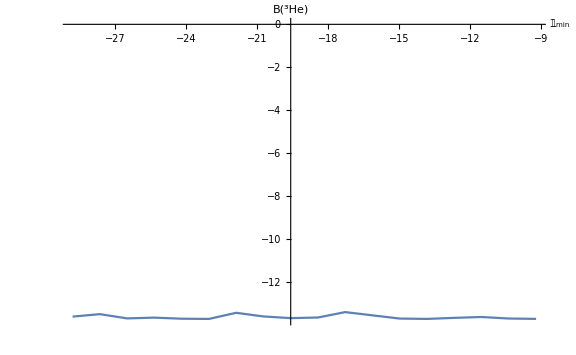

```mathematica
SetSharedVariable[evv]
NormHamMat=ReadList["./MATOUT",Number];
JbasisDim=NormHamMat[[1]];

thr=6^-6;

norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
evhamunnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];
renorm=DiagonalMatrix[1/Sqrt[Diagonal[norm]]];
renormid=DiagonalMatrix[Table[1,{n,JbasisDim}]];
ham=renorm.ham.renorm;norm=renorm.norm.renorm;
evhamnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];

evv = {};

thrange=Table[10^(-13+0.5 n),{n,18}];
ParallelDo[
decompose[thr,norm,ham];
evn=Eigenvalues[norm];
gs=Sort[λs,Re[#1]>Re[#2]&][[-1]];
(*Print["EV_(EV(𝟙) > threshold)(ℍ) = ",gs];*)
AppendTo[evv,gs];
,{thr,thrange}];
data=Transpose[{Log[thrange],evv}]
ListPlot[data,Axes->True,AxesLabel->{"𝟙_min","B(^3He)"},PlotRange->{Automatic,Automatic},ImageSize->Large,AxesOrigin->{Log[thrange][[Length[thrange]/2]],0},Joined->True]
```

```mathematica
NormHamMat=ReadList["./MATOUT",Number];
JbasisDim=NormHamMat[[1]];
thr=6^-22;

norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
evhamunnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];
renorm=DiagonalMatrix[1/Sqrt[Diagonal[norm]]];
renormid=DiagonalMatrix[Table[1,{n,JbasisDim}]];
ham=renorm.ham.renorm;norm=renorm.norm.renorm;

Print[ham//MatrixForm];
Print[norm//MatrixForm];
{ew,ev}=Eigensystem[{ham,norm}];
Print[Re[ew[[-1]]]];
Print[Re[ev[[-1]]]];
```

(2895.39 | 2541.56 | 1928.54 | 347.118 | 2573.44 | 2257.35 | 1712.36 | 307.683 | 1851.36 | 1617.94 | 1229.27 | 220.783 | 1757.81 | 1534.49 | 1166.34 | 209.579 | 1312.12 | 1133.61 | 863.469 | 156.072 | 1289.71 | 1113.28 | 848.05 | 153.368 | 1289.12 | 1112.75 | 847.646 | 153.297 | 1042.23 | 935.35 | 832.187 | 113.011 | 576.635 | 488.14 | 420.927 | 58.8401 | 489.085 | 407.168 | 346.81 | 48.5673 | 338.764 | 274.06 | 227.252 | 31.188 | 327.358 | 264.36 | 218.734 | 29.9023 | 142.356 | 115.036 | 93.4456 | 10.7317 | 70.413 | 58.0029 | 47.8295 | 4.72233 | 30.9848 | 27.5132 | 21.1805 | 2.0306 | 1631.11 | 1246.61 | 681.687 | 1840.1 | 1399.79 | 795.698 | 1844. | 1401.52 | 797.627 | 1824.67 | 1382.32 | 788.802 | 1773.83 | 1346.6 | 767.362 | 1375.72 | 1202.33 | 859.476 | 1245.72 | 1099.46 | 792.746 | 1194.5 | 1058.48 | 766.25 | 725.211 | 666.997 | 508.142 | 474.388 | 444.141 | 350.395 | 339.76 | 337.556 | 313.815 | 233.535 | 210.846 | 37.4923 | 133.336 | 114.289 | 19.6192 | 131.745 | 112.8 | 19.3484 | 93.3974 | 77.6377 | 13.0145 | 89.6533 | 74.3042 | 12.4208 | 79.7333 | 70.8059 | 10.0171 | 58.9991 | 52.3181 | 7.19899 | 40.5897 | 36.6524 | 4.89712 | 35.97 | 32.8104 | 4.34984 | 33.4922 | 30.758 | 4.06095 | 22.0328 | 21.7762 | 2.44324 | 21.617 | 21.4111 | 2.40204 | 12.3226 | 13.0186 | 1.47955 | 3.88111 | 4.59261 | 0.57809 | 2.39442 | 2.94738 | 0.393247 | 0.858331 | 1.30488 | 0.230657 | 0.467559 | 0.77768 | 0.149308 | -51.0023 | -28.8952 | -17.4579 | -9.11374 | -63.3848 | -32.0039 | -18.333 | -9.24654 | -63.4421 | -32.0002 | -18.3184 | -9.23483 | -63.8653 | -31.9404 | -18.1693 | -9.11925 | -63.339 | -31.2471 | -17.3766 | -8.56117 | -44.1212 | -31.6318 | -22.1433 | -6.70646 | -36.3244 | -26.4911 | -19.0217 | -6.02149 | -34.0747 | -24.9166 | -18.0002 | -5.79949 | -20.1474 | -14.6965 | -10.7579 | -3.91665 | -14.0691 | -10.2124 | -7.42675 | -2.74049 | -58.9715 | -29.8898 | -3.6074 | -0.00787981 | -59.2517 | -30.4713 | -3.74259 | -0.0119429 | -59.5961 | -36.3314 | -5.33391 | -0.0562672 | -25.4899 | -21.0762 | -9.89551 | -0.150627 | -10.9648 | -8.98481 | -4.60074 | -0.117775 | -9.43619 | -7.73583 | -3.90132 | -0.110797 | 7.23129 | 5.11507 | 3.26268 | 7.01551 | 5.05765 | 3.28585 | 3.76491 | 2.88932 | 2.02096 | 2.76183 | 2.14451 | 1.52108 | 1.49726 | 1.19018 | 0.861347 | 1.49094 | 0.775816 | -0.167885 | 2.06305 | 1.2936 | 0.140397 | 1.66821 | 1.21172 | 0.378258 | 1.60434 | 1.16704 | 0.366126 | 1.21237 | 0.886776 | 0.28566 | 409.812 | 304.789 | 429.533 | 328.896 | 291.443 | 241.222 | 62.8724 | 57.9611 | 1564.44 | 1340.44 | 372.191 | 1657.18 | 1450. | 420.48 | 1589.95 | 1513.97 | 536.023 | 1029.64 | 1080.92 | 475.85 | 160.866 | 194.59 | 127.129 | -103.042 | -97.8375 | -78.9371 | -15.8879 | -69.9277 | -65.3164 | -50.2589 | -10.1792 | -43.6914 | -40.4017 | -29.791 | -5.62703 | -35.1915 | -32.5107 | -23.7445 | -4.27152 | -24.9297 | -23.0662 | -16.788 | -2.7866 | -15.9575 | -14.8263 | -10.8862 | -1.65924 | 5.23384 | 2.69563 | 0.818507 | 0.377348 | 0.271412 | 0.111017 | -138.321 | -118.743 | -12.9275 | -137.54 | -118.141 | -12.7218 | -94.6077 | -84.8726 | -8.20511 | -94.4716 | -84.7639 | -8.19427
2541.56 | 2615.8 | 2318.21 | 529.926 | 2240.79 | 2303.77 | 2041.32 | 465.993 | 1584.16 | 1618.97 | 1436.05 | 327.725 | 1500.67 | 1531.09 | 1358.36 | 310.11 | 1109.03 | 1114.82 | 989.003 | 226.785 | 1089.65 | 1094.02 | 970.443 | 222.617 | 1089.14 | 1093.47 | 969.957 | 222.508 | 854.232 | 854.36 | 832.252 | 161.975 | 488.236 | 453.725 | 423.622 | 82.3824 | 421.348 | 383.932 | 352.993 | 68.0372 | 304.24 | 268.635 | 239.315 | 44.2469 | 295.074 | 260.069 | 231.118 | 42.4957 | 136.191 | 120.511 | 104.945 | 15.8666 | 68.6164 | 62.0355 | 54.8591 | 7.09799 | 28.8016 | 27.6149 | 23.9511 | 3.07061 | 1046.72 | 796.416 | 428.286 | 1224.69 | 933.887 | 527.375 | 1231.79 | 939.319 | 531.681 | 1254.14 | 961.699 | 551.947 | 1242.52 | 962.193 | 557.121 | 1033.84 | 932.599 | 702.468 | 951.664 | 872.83 | 672.147 | 917.702 | 847.181 | 658.38 | 578.451 | 565.36 | 482.619 | 383.286 | 384.592 | 346.725 | 261.843 | 268.536 | 275.973 | 195.902 | 213.575 | 57.3856 | 111.343 | 113.833 | 29.2501 | 110.02 | 112.32 | 28.831 | 78.2456 | 76.9042 | 19.1204 | 75.1525 | 73.576 | 18.2204 | 65.9136 | 65.7841 | 14.6739 | 49.0074 | 48.7067 | 10.4532 | 33.7962 | 34.2451 | 7.0578 | 29.9296 | 30.6864 | 6.25846 | 27.8453 | 28.7814 | 5.83782 | 18.12 | 19.9182 | 3.51661 | 17.7623 | 19.5813 | 3.45699 | 9.70271 | 11.7701 | 2.12677 | 2.39679 | 3.82442 | 0.831213 | 1.19031 | 2.29785 | 0.564876 | -0.144842 | 0.590972 | 0.329126 | -0.289419 | 0.229873 | 0.21191 | -38.1313 | -23.7027 | -15.1569 | -8.31853 | -47.2807 | -25.7237 | -15.493 | -8.1803 | -47.3328 | -25.7206 | -15.4787 | -8.16821 | -47.746 | -25.6782 | -15.3399 | -8.05239 | -47.8642 | -25.271 | -14.7047 | -7.55226 | -34.2056 | -25.8519 | -18.866 | -6.20298 | -28.1668 | -21.8084 | -16.4233 | -5.70747 | -26.3976 | -20.5389 | -15.5941 | -5.53929 | -15.3041 | -12.0512 | -9.42462 | -3.93516 | -10.4958 | -8.26338 | -6.47316 | -2.80814 | -48.7945 | -24.757 | -2.68779 | 0.0399601 | -49.1757 | -25.3441 | -2.82253 | 0.0356764 | -51.2133 | -31.6487 | -4.46771 | -0.0123878 | -25.6647 | -22.9026 | -11.7545 | -0.166011 | -11.5955 | -10.7612 | -6.63918 | -0.175383 | -10.0162 | -9.36907 | -5.78589 | -0.172811 | 5.81074 | 4.09414 | 2.59137 | 5.85334 | 4.22679 | 2.74497 | 3.46627 | 2.71064 | 1.933 | 2.57129 | 2.04642 | 1.48906 | 1.38914 | 1.14512 | 0.860503 | 1.02305 | 0.420306 | -0.320449 | 1.59716 | 0.938925 | -0.0109354 | 1.50093 | 1.08442 | 0.325894 | 1.44677 | 1.04712 | 0.31674 | 1.10637 | 0.806287 | 0.25215 | 348.446 | 263.436 | 412.452 | 326.996 | 347.655 | 314.193 | 89.5898 | 96.6542 | 1242.28 | 1087.08 | 312.751 | 1351.43 | 1215.37 | 371.354 | 1426.8 | 1439. | 588.269 | 999.257 | 1152.99 | 669.411 | 167.357 | 236.445 | 266.507 | -76.2253 | -72.8207 | -59.9626 | -12.8236 | -52.6162 | -49.4165 | -38.7233 | -8.28459 | -33.3244 | -30.979 | -23.2484 | -4.62824 | -26.9417 | -25.0215 | -18.5994 | -3.52674 | -19.1555 | -17.8177 | -13.2 | -2.31108 | -12.2879 | -11.4772 | -8.5788 | -1.38091 | 4.64375 | 2.41196 | 0.74237 | 0.344019 | 0.243014 | 0.0995828 | -96.952 | -83.9083 | -9.43441 | -96.8231 | -83.8935 | -9.29433 | -71.1807 | -65.7388 | -6.60252 | -71.0848 | -65.6643 | -6.59628
1928.54 | 2318.21 | 2476.41 | 838.84 | 1691.68 | 2031.57 | 2170.9 | 734.95 | 1182. | 1410.14 | 1509.55 | 511.798 | 1117.85 | 1331.04 | 1425.19 | 483.476 | 819.532 | 958.83 | 1025.98 | 349.826 | 804.912 | 940.364 | 1006.03 | 343.155 | 804.53 | 939.881 | 1005.5 | 342.981 | 613.583 | 679.878 | 730.935 | 247.996 | 360.15 | 364.738 | 371.133 | 122.122 | 316.29 | 312.881 | 312.103 | 100.148 | 239.451 | 228.983 | 219.684 | 64.8766 | 233.281 | 222.726 | 213.074 | 62.3465 | 116.582 | 113.288 | 106.29 | 24.2283 | 60.3435 | 60.417 | 57.7766 | 11.1506 | 24.0998 | 25.1854 | 25.0079 | 4.88282 | 632.044 | 479.344 | 254.475 | 755.378 | 576.675 | 323.822 | 761.434 | 581.66 | 327.649 | 789.065 | 609.866 | 351.197 | 791.327 | 621.196 | 363.758 | 690.841 | 638.575 | 502.091 | 643.405 | 608.324 | 495.431 | 622.951 | 594.196 | 490.891 | 403.23 | 415.048 | 394.749 | 269.505 | 287.262 | 295.501 | 177.015 | 186.209 | 208.857 | 141.911 | 183.88 | 89.0803 | 80.2282 | 96.6905 | 44.6417 | 79.2722 | 95.3819 | 43.9853 | 56.4095 | 64.9041 | 28.8455 | 54.192 | 62.0588 | 27.4513 | 46.9682 | 51.9513 | 22.1579 | 35.0149 | 38.4481 | 15.6411 | 24.1739 | 27.0608 | 10.4592 | 21.3916 | 24.2594 | 9.25003 | 19.8854 | 22.7587 | 8.61574 | 12.7943 | 15.4114 | 5.20365 | 12.53 | 15.1486 | 5.11409 | 6.50337 | 8.99916 | 3.12873 | 0.933844 | 2.5893 | 1.22071 | 0.0466156 | 1.34925 | 0.83076 | -0.956351 | -0.184297 | 0.482726 | -0.918833 | -0.377002 | 0.310804 | -25.3661 | -16.7539 | -11.1362 | -6.3416 | -31.3255 | -17.9247 | -11.1815 | -6.10561 | -31.3631 | -17.9218 | -11.1699 | -6.09547 | -31.6703 | -17.8891 | -11.0599 | -5.9999 | -31.9489 | -17.6577 | -10.6053 | -5.61424 | -23.1901 | -18.2195 | -13.7148 | -4.79654 | -19.0485 | -15.4439 | -12.0795 | -4.52836 | -17.8181 | -14.5512 | -11.5031 | -4.43278 | -10.0172 | -8.38803 | -6.96881 | -3.34882 | -6.68345 | -5.59326 | -4.69602 | -2.44433 | -34.2835 | -17.4234 | -1.73672 | 0.0752615 | -34.6158 | -17.8826 | -1.84084 | 0.0715402 | -36.8364 | -22.9872 | -3.14111 | 0.0294512 | -20.4504 | -19.387 | -10.7129 | -0.130025 | -9.43427 | -9.7499 | -7.22099 | -0.18958 | -8.13865 | -8.54275 | -6.4601 | -0.197406 | 4.00353 | 2.81234 | 1.7691 | 4.1335 | 2.98855 | 1.94018 | 2.61153 | 2.07292 | 1.50136 | 1.94814 | 1.5826 | 1.17654 | 1.03808 | 0.884992 | 0.688644 | 0.608207 | 0.182316 | -0.316513 | 1.05337 | 0.584579 | -0.0750796 | 1.09563 | 0.787642 | 0.228327 | 1.05741 | 0.761627 | 0.222462 | 0.813247 | 0.590246 | 0.178937 | 247.741 | 189.182 | 317.029 | 257.304 | 309.71 | 299.288 | 90.5288 | 111.731 | 846.11 | 749.815 | 220.222 | 935.243 | 855.336 | 269.762 | 1046.77 | 1096.1 | 494.164 | 768.912 | 947.042 | 676.77 | 132.917 | 210.673 | 382.245 | -49.9462 | -47.8962 | -39.9492 | -8.90992 | -34.8266 | -32.8194 | -26.0143 | -5.7805 | -22.2304 | -20.7343 | -15.7364 | -3.25012 | -18.006 | -16.7782 | -12.6143 | -2.48268 | -12.8191 | -11.9633 | -8.96554 | -1.63151 | -8.22251 | -7.70489 | -5.82609 | -0.97667 | 3.3661 | 1.74998 | 0.541904 | 0.24931 | 0.173917 | 0.070012 | -61.6928 | -53.6556 | -6.13809 | -61.7757 | -53.8113 | -6.04682 | -47.2505 | -44.5265 | -4.53642 | -47.1889 | -44.4799 | -4.53337
347.118 | 529.926 | 838.84 | 2387.9 | 302.925 | 462.189 | 732.455 | 2087.68 | 209.055 | 316.878 | 503.967 | 1445.01 | 197.345 | 298.505 | 474.95 | 1363.56 | 143.305 | 212.481 | 338.041 | 979.302 | 140.68 | 208.236 | 331.215 | 960.119 | 140.611 | 208.125 | 331.036 | 959.618 | 103.169 | 132.646 | 169.006 | 725.71 | 62.583 | 71.6059 | 84.5712 | 341.801 | 56.4436 | 62.6309 | 71.7991 | 274.64 | 46.4202 | 49.8012 | 53.949 | 168.466 | 45.6125 | 48.9294 | 52.8165 | 161.057 | 27.0228 | 31.8603 | 35.0681 | 59.0721 | 14.9335 | 19.1295 | 22.5647 | 29.9278 | 5.3662 | 6.81274 | 9.8465 | 15.0526 | 87.4959 | 66.1198 | 34.572 | 106.691 | 81.5213 | 45.4527 | 107.777 | 82.4535 | 46.1582 | 113.657 | 88.5589 | 51.1483 | 115.401 | 91.9169 | 54.4859 | 106.036 | 100.862 | 83.6415 | 100.017 | 98.0866 | 85.8439 | 97.262 | 96.526 | 86.3539 | 64.7194 | 71.1974 | 79.1807 | 43.5837 | 50.2786 | 63.1756 | 27.2462 | 29.5427 | 37.1488 | 23.9171 | 39.6942 | 190.564 | 13.4247 | 20.5595 | 94.264 | 13.2637 | 20.2749 | 92.8485 | 9.43125 | 13.6804 | 60.3034 | 9.06134 | 13.0689 | 57.3188 | 7.73343 | 9.8457 | 49.5582 | 5.77855 | 7.26991 | 34.6639 | 3.9926 | 5.11422 | 22.9278 | 3.52915 | 4.58556 | 20.2099 | 3.27691 | 4.30243 | 18.7884 | 2.07314 | 2.8221 | 12.6621 | 2.02736 | 2.77348 | 12.439 | 0.958488 | 1.62007 | 7.52893 | -0.106011 | 0.339937 | 2.90594 | -0.287012 | 0.0682594 | 1.97873 | -0.475287 | -0.31437 | 1.08821 | -0.436967 | -0.342022 | 0.70821 | -3.87035 | -2.72139 | -1.88705 | -1.12443 | -4.75316 | -2.86853 | -1.8597 | -1.05617 | -4.75926 | -2.86789 | -1.8575 | -1.05417 | -4.81023 | -2.86156 | -1.83706 | -1.03551 | -4.8819 | -2.8315 | -1.76049 | -0.964812 | -3.59743 | -2.9554 | -2.30686 | -0.867738 | -2.93663 | -2.51687 | -2.06462 | -0.85399 | -2.7363 | -2.37034 | -1.9736 | -0.848488 | -1.44666 | -1.29944 | -1.17633 | -0.72116 | -0.914909 | -0.801248 | -0.735384 | -0.543273 | -5.49291 | -2.79781 | -0.249086 | 0.0333928 | -5.55639 | -2.87893 | -0.267178 | 0.0324859 | -6.0416 | -3.81013 | -0.498225 | 0.0222589 | -3.72297 | -3.79987 | -2.31019 | -0.0169213 | -1.71361 | -2.04168 | -1.99691 | -0.0445914 | -1.46343 | -1.79191 | -1.85629 | -0.0517538 | 0.628667 | 0.44006 | 0.27474 | 0.665933 | 0.482149 | 0.312866 | 0.450452 | 0.364104 | 0.268793 | 0.337357 | 0.281361 | 0.215049 | 0.173933 | 0.155748 | 0.12751 | 0.0781574 | 0.00966221 | -0.0667855 | 0.15577 | 0.0798838 | -0.0242592 | 0.180409 | 0.128785 | 0.0354024 | 0.174276 | 0.124663 | 0.0345604 | 0.134407 | 0.0968997 | 0.0279057 | 40.0263 | 30.8638 | 55.4416 | 46.1228 | 63.3642 | 66.243 | 21.1475 | 31.1521 | 130.984 | 117.5 | 35.181 | 147.029 | 136.7 | 44.4518 | 174.213 | 189.623 | 94.8734 | 133.928 | 176.987 | 161.018 | 23.4075 | 42.2837 | 146.546 | -7.46666 | -7.18707 | -6.07269 | -1.41932 | -5.25717 | -4.97078 | -3.98593 | -0.923889 | -3.3798 | -3.16282 | -2.42827 | -0.522778 | -2.7411 | -2.56271 | -1.94943 | -0.400387 | -1.95169 | -1.82738 | -1.38586 | -0.263922 | -1.24928 | -1.17421 | -0.898275 | -0.15823 | 0.55106 | 0.283992 | 0.0884957 | 0.0393693 | 0.0272644 | 0.0101645 | -8.98196 | -7.84933 | -0.909234 | -9.01781 | -7.89633 | -0.895131 | -7.16025 | -6.89621 | -0.700143 | -7.15111 | -6.8895 | -0.699872
2573.44 | 2240.79 | 1691.68 | 302.925 | 2378.57 | 2069.73 | 1561.87 | 279.131 | 1820.34 | 1578.24 | 1192.46 | 212.875 | 1739.55 | 1506.53 | 1138.67 | 203.345 | 1333.06 | 1142.45 | 864.988 | 155.274 | 1311.74 | 1123.19 | 850.45 | 152.74 | 1311.18 | 1122.69 | 850.069 | 152.673 | 1074.32 | 957.594 | 848.04 | 113.701 | 598.944 | 503.207 | 431.65 | 59.4294 | 507.621 | 419.308 | 355.222 | 48.9681 | 350.613 | 281.286 | 231.91 | 31.2998 | 338.716 | 271.245 | 223.142 | 29.9972 | 146.633 | 117.425 | 94.8044 | 10.6961 | 72.4268 | 59.1138 | 48.4433 | 4.6975 | 32.0333 | 28.2211 | 21.4804 | 2.0184 | 1623.69 | 1302.38 | 749.875 | 1842.16 | 1452.84 | 854.486 | 1847.15 | 1454.1 | 855.194 | 1836.05 | 1430.98 | 836.962 | 1790.06 | 1392.44 | 809.538 | 1404.07 | 1236.29 | 890.9 | 1272.98 | 1130.26 | 819.683 | 1221.12 | 1088.01 | 791.59 | 742.854 | 684.728 | 521.567 | 486.085 | 455.569 | 358.686 | 347.578 | 345.722 | 321.732 | 271.327 | 244.253 | 43.2691 | 171.794 | 147.736 | 25.3682 | 169.998 | 146.049 | 25.0619 | 124.676 | 104.451 | 17.5778 | 120.045 | 100.324 | 16.8435 | 107.471 | 96.3265 | 13.741 | 80.6103 | 72.3767 | 10.0853 | 55.9508 | 51.3466 | 6.98207 | 49.6581 | 46.0886 | 6.22795 | 46.2679 | 43.2643 | 5.8273 | 30.4757 | 30.6929 | 3.54172 | 29.899 | 30.1819 | 3.48324 | 16.968 | 18.3707 | 2.16254 | 5.22074 | 6.43445 | 0.850909 | 3.17321 | 4.10788 | 0.579471 | 1.02104 | 1.74107 | 0.340062 | 0.521903 | 1.02218 | 0.22012 | -59.4611 | -32.1821 | -18.9285 | -9.67728 | -81.3107 | -40.607 | -22.9593 | -11.4357 | -81.441 | -40.6437 | -22.9679 | -11.4358 | -82.4935 | -40.9354 | -23.0196 | -11.422 | -83.5153 | -41.2595 | -22.7938 | -11.1423 | -60.385 | -43.7948 | -30.7751 | -9.3204 | -50.1163 | -37.0156 | -26.7061 | -8.47246 | -47.1164 | -34.9022 | -25.3406 | -8.1868 | -28.2243 | -20.8877 | -15.3838 | -5.63142 | -19.8136 | -14.6 | -10.6866 | -3.96832 | -75.4822 | -42.1604 | -6.70949 | -0.0977427 | -75.7053 | -42.8139 | -6.85786 | -0.101577 | -74.9952 | -49.3291 | -8.65024 | -0.144122 | -32.2615 | -27.8285 | -14.0162 | -0.229818 | -14.1575 | -12.0375 | -6.53472 | -0.17702 | -12.2182 | -10.3878 | -5.54752 | -0.166475 | 8.59721 | 6.22855 | 4.07695 | 8.15292 | 6.01147 | 3.99865 | 4.14579 | 3.2703 | 2.35004 | 2.99868 | 2.40137 | 1.75492 | 1.58346 | 1.30711 | 0.98035 | -1.34692 | -1.54702 | -1.2591 | -0.440429 | -0.750426 | -0.824675 | 0.898624 | 0.590237 | 0.0994427 | 0.878377 | 0.580936 | 0.103388 | 0.719382 | 0.49035 | 0.10849 | 387.655 | 300.214 | 402.665 | 318.755 | 275.872 | 232.84 | 60.6831 | 56.4644 | 1201.05 | 1100.31 | 358.352 | 1289.25 | 1200.39 | 403.63 | 1305.36 | 1301.35 | 514.695 | 889.863 | 965.042 | 459.931 | 147.849 | 182.056 | 123.965 | -108.085 | -103.26 | -84.5298 | -17.3282 | -76.5086 | -72.0567 | -56.5921 | -11.81 | -48.912 | -45.6626 | -34.4931 | -6.76441 | -39.6281 | -36.9733 | -27.6922 | -5.18377 | -28.2456 | -26.4044 | -19.7304 | -3.41658 | -18.1632 | -17.0556 | -12.8697 | -2.05081 | 3.28043 | 1.72933 | 0.443831 | 0.215542 | 0.122405 | 0.0544471 | -169.66 | -148.685 | -16.8036 | -169.277 | -148.438 | -16.6466 | -122.049 | -111.293 | -11.4691 | -121.884 | -111.159 | -11.4548
2257.35 | 2303.77 | 2031.57 | 462.189 | 2069.73 | 2109.59 | 1859.46 | 422.284 | 1556.44 | 1576.31 | 1389.97 | 315.256 | 1483.88 | 1500.24 | 1323.01 | 300.133 | 1125.19 | 1120.45 | 987.485 | 224.802 | 1106.7 | 1100.68 | 969.93 | 220.88 | 1106.21 | 1100.17 | 969.47 | 220.778 | 878.917 | 871.922 | 844.9 | 162.189 | 504.456 | 464.868 | 431.586 | 82.602 | 434.572 | 392.622 | 358.933 | 68.0619 | 312.299 | 273.351 | 242.115 | 44.0197 | 302.763 | 264.519 | 233.718 | 42.2577 | 138.796 | 121.71 | 105.371 | 15.6625 | 69.7832 | 62.5168 | 54.9612 | 6.99119 | 29.4416 | 27.9966 | 24.0181 | 3.02175 | 1049.83 | 839.324 | 476.76 | 1232.72 | 974.116 | 568.718 | 1240.42 | 979.156 | 572.162 | 1267.63 | 998.462 | 585.929 | 1259.2 | 996.925 | 587.056 | 1058.9 | 959.983 | 726.312 | 976.016 | 898.084 | 692.889 | 941.573 | 871.546 | 677.996 | 594.507 | 580.465 | 493.263 | 393.85 | 394.311 | 353.217 | 269.309 | 276.016 | 282.639 | 228.692 | 248.358 | 66.4578 | 144.481 | 148.096 | 38.0279 | 142.981 | 146.377 | 37.5512 | 105.27 | 104.319 | 26.0208 | 101.421 | 100.181 | 24.9026 | 89.522 | 90.2836 | 20.3047 | 67.4327 | 68.0194 | 14.8014 | 46.8489 | 48.4425 | 10.1938 | 41.5253 | 43.525 | 9.08347 | 38.6424 | 40.8769 | 8.49505 | 25.0964 | 28.3022 | 5.17981 | 24.595 | 27.8253 | 5.09422 | 13.267 | 16.7042 | 3.1655 | 3.028 | 5.32417 | 1.24957 | 1.37231 | 3.14859 | 0.850813 | -0.499014 | 0.659382 | 0.496395 | -0.632475 | 0.186113 | 0.319713 | -43.6258 | -25.6334 | -15.9081 | -8.53777 | -60.393 | -32.1796 | -19.0336 | -9.88941 | -60.5092 | -32.2138 | -19.0416 | -9.88901 | -61.4824 | -32.5011 | -19.0983 | -9.87538 | -63.1447 | -33.1343 | -19.0694 | -9.68388 | -47.1853 | -35.9762 | -26.3049 | -8.62425 | -39.2432 | -30.6931 | -23.1873 | -8.0621 | -36.8796 | -28.9953 | -22.0908 | -7.85752 | -21.7359 | -17.3251 | -13.6135 | -5.71557 | -15.0063 | -11.9682 | -9.42334 | -4.1156 | -62.6716 | -34.9843 | -5.18631 | -0.0269822 | -63.0578 | -35.6736 | -5.34212 | -0.0312235 | -64.8172 | -43.0884 | -7.2991 | -0.0801901 | -33.1394 | -30.7623 | -16.8585 | -0.25706 | -15.3894 | -14.7781 | -9.61771 | -0.268466 | -13.3441 | -12.909 | -8.39863 | -0.264614 | 7.01843 | 5.07096 | 3.29947 | 6.93192 | 5.1245 | 3.41117 | 3.94266 | 3.17923 | 2.33606 | 2.88568 | 2.38001 | 1.79192 | 1.50894 | 1.30424 | 1.02376 | -1.23484 | -1.46237 | -1.25344 | -0.397821 | -0.721886 | -0.840268 | 0.904348 | 0.590642 | 0.0865575 | 0.884832 | 0.582101 | 0.0913336 | 0.727814 | 0.494232 | 0.100666 | 331.752 | 261.214 | 389.352 | 318.612 | 334.067 | 306.618 | 88.5687 | 95.9077 | 973.919 | 910.413 | 306.898 | 1074.75 | 1026.93 | 362.952 | 1204.78 | 1266.84 | 574.314 | 895.859 | 1060.7 | 658.137 | 161.352 | 230.07 | 264.979 | -81.3011 | -78.1457 | -65.2725 | -14.2057 | -58.6042 | -55.505 | -44.4109 | -9.79689 | -37.9793 | -35.6538 | -27.4338 | -5.68243 | -30.8775 | -28.9704 | -22.1061 | -4.37337 | -22.0753 | -20.753 | -15.8042 | -2.89661 | -14.2125 | -13.4216 | -10.3247 | -1.74498 | 3.19273 | 1.68599 | 0.445101 | 0.213644 | 0.117176 | 0.0508158 | -119.621 | -105.645 | -12.1975 | -119.859 | -105.976 | -12.0995 | -92.543 | -86.7379 | -9.21851 | -92.4273 | -86.6469 | -9.21069
1712.36 | 2041.32 | 2170.9 | 732.455 | 1561.87 | 1859.46 | 1977.43 | 666.537 | 1160.37 | 1371.38 | 1459.88 | 492.321 | 1104.36 | 1302.54 | 1386.75 | 467.861 | 830.268 | 961.756 | 1022.67 | 346.493 | 816.289 | 944.174 | 1003.74 | 340.197 | 815.923 | 943.713 | 1003.25 | 340.032 | 630.129 | 692.066 | 740.064 | 247.99 | 370.536 | 372.009 | 376.459 | 122.15 | 324.614 | 318.361 | 315.848 | 99.9223 | 244.289 | 231.646 | 221.072 | 64.3649 | 237.872 | 225.205 | 214.317 | 61.8259 | 117.895 | 113.643 | 106.102 | 23.8569 | 60.8615 | 60.4546 | 57.5375 | 10.9567 | 24.414 | 25.3212 | 24.9149 | 4.79374 | 636.882 | 507.887 | 285.432 | 762.852 | 603.293 | 349.97 | 769.238 | 608.008 | 353.242 | 799.659 | 634.146 | 372.663 | 803.887 | 644.167 | 382.703 | 708.816 | 657.366 | 517.89 | 660.973 | 625.835 | 509.33 | 640.198 | 611.149 | 504.088 | 414.658 | 425.573 | 401.976 | 276.772 | 293.826 | 299.733 | 182.108 | 191.251 | 213.221 | 166.177 | 214.404 | 103.471 | 104.579 | 126.311 | 58.2527 | 103.494 | 124.819 | 57.5021 | 76.2866 | 88.5152 | 39.4464 | 73.5177 | 84.9669 | 37.7072 | 64.1205 | 71.722 | 30.8315 | 48.421 | 54.0515 | 22.3025 | 33.6542 | 38.559 | 15.2405 | 29.7956 | 34.6647 | 13.5524 | 27.6968 | 32.5653 | 12.6604 | 17.7429 | 22.0481 | 7.75482 | 17.3694 | 21.673 | 7.62534 | 8.8262 | 12.842 | 4.7228 | 0.947403 | 3.56837 | 1.86835 | -0.277683 | 1.78193 | 1.27568 | -1.69254 | -0.483544 | 0.743612 | -1.57057 | -0.719656 | 0.479478 | -28.7008 | -17.8313 | -11.4912 | -6.39446 | -39.9084 | -22.2367 | -13.586 | -7.28668 | -39.9921 | -22.2615 | -13.5914 | -7.28565 | -40.7057 | -22.4759 | -13.6314 | -7.27026 | -42.1676 | -23.0591 | -13.6638 | -7.13802 | -32.1609 | -25.4525 | -19.1812 | -6.68575 | -26.7158 | -21.8502 | -17.1351 | -6.43115 | -25.0684 | -20.6586 | -16.3796 | -6.32684 | -14.3593 | -12.156 | -10.1433 | -4.91459 | -9.65035 | -8.17272 | -6.89388 | -3.62444 | -44.1525 | -24.6571 | -3.45385 | 0.0325671 | -44.5121 | -25.208 | -3.57721 | 0.0289326 | -46.8182 | -31.3698 | -5.16412 | -0.0135709 | -26.7625 | -26.3484 | -15.5077 | -0.205299 | -12.7543 | -13.6201 | -10.6054 | -0.294442 | -11.0517 | -11.9827 | -9.51268 | -0.306706 | 4.88743 | 3.5234 | 2.28112 | 4.9581 | 3.67217 | 2.44543 | 3.03499 | 2.48999 | 1.86224 | 2.23348 | 1.88753 | 1.45671 | 1.14192 | 1.03054 | 0.843691 | -0.950041 | -1.1338 | -0.993256 | -0.323855 | -0.577664 | -0.678455 | 0.692328 | 0.447228 | 0.0530221 | 0.677864 | 0.441278 | 0.0573183 | 0.558432 | 0.37589 | 0.0676332 | 236.823 | 188.325 | 300.624 | 251.54 | 300.526 | 294.134 | 90.7667 | 112.091 | 671.122 | 634.908 | 218.213 | 752.952 | 730.862 | 266.061 | 898.128 | 977.838 | 486.344 | 704.242 | 886.27 | 670.848 | 131.458 | 209.367 | 383.699 | -53.7847 | -51.8923 | -43.8995 | -9.95997 | -39.1872 | -37.2442 | -30.1528 | -6.91284 | -25.5901 | -24.1075 | -18.7716 | -4.04098 | -20.8366 | -19.619 | -15.1533 | -3.11874 | -14.905 | -14.0624 | -10.8437 | -2.07201 | -9.58399 | -9.08268 | -7.07622 | -1.25049 | 2.4154 | 1.26736 | 0.336139 | 0.156495 | 0.0819134 | 0.0329962 | -76.3999 | -67.7895 | -7.89911 | -76.7539 | -68.2064 | -7.83588 | -61.7555 | -59.0068 | -6.32096 | -61.6814 | -58.9504 | -6.31743
307.683 | 465.993 | 734.95 | 2087.68 | 279.131 | 422.284 | 666.537 | 1895.24 | 204.684 | 307.312 | 486.433 | 1390.64 | 194.421 | 291.255 | 461.168 | 1320.01 | 144.667 | 212.301 | 335.942 | 969.941 | 142.154 | 208.254 | 329.458 | 951.792 | 142.088 | 208.148 | 329.288 | 951.316 | 105.516 | 134.373 | 170.315 | 725.488 | 63.9497 | 72.519 | 85.2122 | 341.693 | 57.4912 | 63.2458 | 72.1452 | 273.877 | 46.9333 | 49.9609 | 53.8796 | 167.059 | 46.0875 | 49.0596 | 52.7226 | 159.638 | 26.9972 | 31.6518 | 34.7366 | 58.1516 | 14.8495 | 18.9309 | 22.2816 | 29.4083 | 5.34525 | 6.749 | 9.71019 | 14.7814 | 88.4458 | 70.3282 | 39.0233 | 107.942 | 85.4017 | 49.1405 | 109.068 | 86.2907 | 49.7621 | 115.305 | 92.0694 | 54.1378 | 117.324 | 95.2272 | 57.1055 | 108.765 | 103.615 | 85.8644 | 102.691 | 100.662 | 87.7933 | 99.8847 | 99.0187 | 88.2003 | 66.3044 | 72.6036 | 80.0442 | 44.4488 | 50.992 | 63.4765 | 27.8201 | 30.0831 | 37.5178 | 28.0557 | 46.3553 | 221.901 | 17.5549 | 26.9311 | 123.352 | 17.3719 | 26.6056 | 121.727 | 12.8052 | 18.733 | 82.7635 | 12.3424 | 17.9689 | 79.0277 | 10.6002 | 13.6574 | 69.2436 | 8.02338 | 10.2795 | 49.6894 | 5.57804 | 7.33714 | 33.6417 | 4.93136 | 6.59906 | 29.8329 | 4.57757 | 6.20112 | 27.8255 | 2.8756 | 4.06583 | 19.054 | 2.81038 | 3.99596 | 18.7296 | 1.28103 | 2.32592 | 11.505 | -0.248191 | 0.450601 | 4.5228 | -0.505609 | 0.0512405 | 3.09493 | -0.777715 | -0.525241 | 1.71169 | -0.709394 | -0.559002 | 1.11739 | -4.32764 | -2.8519 | -1.91601 | -1.1139 | -6.03162 | -3.52576 | -2.23354 | -1.24366 | -6.04521 | -3.5298 | -2.23428 | -1.24327 | -6.16278 | -3.56534 | -2.23992 | -1.23897 | -6.43783 | -3.6789 | -2.25148 | -1.21531 | -5.01006 | -4.14101 | -3.2349 | -1.21379 | -4.1417 | -3.57679 | -2.94179 | -1.22171 | -3.8728 | -3.38162 | -2.82415 | -1.22115 | -2.09002 | -1.896 | -1.72419 | -1.07277 | -1.3307 | -1.17798 | -1.08625 | -0.817291 | -7.08555 | -3.96054 | -0.515872 | 0.0274037 | -7.15722 | -4.05953 | -0.537697 | 0.0265731 | -7.7031 | -5.20671 | -0.825212 | 0.016859 | -4.93368 | -5.22164 | -3.37353 | -0.0284486 | -2.3578 | -2.90111 | -2.97144 | -0.0704615 | -2.02336 | -2.5589 | -2.77115 | -0.0817019 | 0.774911 | 0.557123 | 0.358443 | 0.808346 | 0.599933 | 0.399648 | 0.534518 | 0.447788 | 0.342168 | 0.394603 | 0.34401 | 0.27401 | 0.191971 | 0.184773 | 0.160826 | -0.168086 | -0.201104 | -0.179413 | -0.0620031 | -0.106523 | -0.125047 | 0.117701 | 0.0746313 | 0.00549014 | 0.115282 | 0.0737035 | 0.00634057 | 0.0946696 | 0.0626603 | 0.008636 | 38.3557 | 30.7912 | 52.7266 | 45.1605 | 61.9712 | 65.4235 | 21.3486 | 31.3983 | 104.867 | 100.35 | 35.0968 | 119.543 | 117.83 | 44.1071 | 151.495 | 170.969 | 93.8152 | 124.959 | 168.013 | 160.317 | 23.498 | 42.5278 | 147.549 | -8.10187 | -7.84604 | -6.72345 | -1.59801 | -5.96376 | -5.6877 | -4.65991 | -1.11527 | -3.92079 | -3.70672 | -2.92196 | -0.657113 | -3.19491 | -3.01903 | -2.36152 | -0.508693 | -2.28283 | -2.1615 | -1.68868 | -0.339105 | -1.46188 | -1.39007 | -1.09714 | -0.204922 | 0.408113 | 0.208995 | 0.0552529 | 0.0232839 | 0.011278 | 0.00311581 | -11.1486 | -9.93724 | -1.16108 | -11.2294 | -10.0285 | -1.15098 | -9.39689 | -9.16921 | -0.969519 | -9.38596 | -9.1612 | -0.969275
1851.36 | 1584.16 | 1182. | 209.055 | 1820.34 | 1556.44 | 1160.37 | 204.684 | 1561.88 | 1330.67 | 992.441 | 174.575 | 1513.07 | 1287.67 | 960.574 | 168.983 | 1232.7 | 1037.94 | 774.925 | 136.792 | 1216.45 | 1023.33 | 764.011 | 134.917 | 1216.02 | 1022.95 | 763.723 | 134.868 | 1032.71 | 907.232 | 795.036 | 103.333 | 593.945 | 490.524 | 415.429 | 54.9457 | 503.522 | 408.403 | 341.323 | 45.0772 | 346.251 | 272.114 | 220.965 | 28.4162 | 334.319 | 262.205 | 212.423 | 27.198 | 143.221 | 111.983 | 88.8534 | 9.48629 | 70.4873 | 56.1201 | 45.1705 | 4.13718 | 31.5707 | 27.2652 | 20.1051 | 1.77274 | 1423.46 | 1269.25 | 830.945 | 1631.77 | 1399.37 | 905.806 | 1638.27 | 1399.78 | 903.609 | 1645.43 | 1373.83 | 865.609 | 1615.77 | 1335.89 | 827.466 | 1307.03 | 1175.84 | 871.955 | 1190.12 | 1076.19 | 798.651 | 1143.26 | 1036.29 | 770.024 | 701.278 | 652.611 | 500.814 | 459.814 | 433.848 | 342.344 | 326.726 | 326.466 | 306.271 | 304.756 | 272.899 | 47.808 | 236.548 | 204.769 | 35.0783 | 234.846 | 203.152 | 34.7855 | 186.587 | 158.554 | 26.7957 | 181.072 | 153.62 | 25.9204 | 165.256 | 150.617 | 21.7379 | 129.198 | 118.5 | 16.8253 | 92.8807 | 87.5083 | 12.2202 | 83.1331 | 79.3305 | 11.0344 | 77.8022 | 74.8648 | 10.393 | 52.2777 | 54.1607 | 6.52001 | 51.3225 | 53.3044 | 6.41997 | 29.5039 | 33.0631 | 4.09959 | 9.04828 | 11.7512 | 1.66617 | 5.43894 | 7.50436 | 1.14367 | 1.53229 | 3.03467 | 0.676782 | 0.710543 | 1.75591 | 0.439902 | -76.066 | -40.573 | -23.327 | -11.6486 | -117.45 | -60.6404 | -34.3651 | -17.0345 | -117.759 | -60.7843 | -34.4373 | -17.0676 | -120.389 | -62.0289 | -35.0518 | -17.3449 | -125.869 | -65.3885 | -36.5919 | -17.9594 | -96.9348 | -73.7708 | -53.2402 | -16.6888 | -81.6335 | -63.3652 | -47.0091 | -15.4827 | -77.0579 | -60.0132 | -44.8169 | -15.0423 | -47.2918 | -36.8848 | -27.9805 | -10.675 | -33.5302 | -26.069 | -19.6636 | -7.61648 | -103.505 | -69.1296 | -16.0507 | -0.444138 | -103.534 | -69.8551 | -16.215 | -0.446636 | -100.168 | -76.8105 | -18.2869 | -0.474368 | -43.9764 | -41.6111 | -24.6656 | -0.482767 | -20.2512 | -18.6022 | -11.5434 | -0.360266 | -17.6007 | -16.1384 | -9.82011 | -0.338318 | 12.1497 | 9.32349 | 6.49671 | 10.7142 | 8.34858 | 5.88905 | 4.20036 | 3.56645 | 2.75089 | 2.80169 | 2.45276 | 1.94682 | 1.26533 | 1.18884 | 0.996756 | -8.70191 | -7.62198 | -4.1583 | -7.38269 | -6.47325 | -3.57366 | -2.11445 | -1.87101 | -1.02439 | -1.99523 | -1.76588 | -0.967234 | -1.3621 | -1.20358 | -0.661367 | 352.125 | 288.912 | 350.966 | 292.528 | 232.633 | 202.797 | 51.9559 | 49.0594 | 667.227 | 669.72 | 291.553 | 725.275 | 736.187 | 325.769 | 782.464 | 835.935 | 412.592 | 576.009 | 659.068 | 373.452 | 107.315 | 136.543 | 103.267 | -100.217 | -97.1565 | -82.4542 | -17.7992 | -77.2558 | -74.2124 | -61.2666 | -13.8203 | -52.0698 | -49.7661 | -39.9123 | -8.62147 | -42.8068 | -40.9363 | -32.6534 | -6.77172 | -31.0018 | -29.7466 | -23.7605 | -4.58929 | -20.1869 | -19.4812 | -15.7649 | -2.81873 | -2.88808 | -1.509 | -1.15271 | -0.526907 | -0.550495 | -0.220926 | -210.883 | -193.525 | -24.861 | -212.073 | -194.764 | -24.9978 | -171.608 | -162.903 | -20.3468 | -171.413 | -162.739 | -20.3259
1617.94 | 1618.97 | 1410.14 | 316.878 | 1578.24 | 1576.31 | 1371.38 | 307.312 | 1330.67 | 1319.39 | 1146.56 | 255.98 | 1286. | 1272.76 | 1105.9 | 246.857 | 1035.74 | 1009.03 | 875.044 | 195.552 | 1021.53 | 993.93 | 861.759 | 192.62 | 1021.16 | 993.533 | 861.409 | 192.543 | 840.382 | 818.475 | 783.169 | 145.158 | 492.865 | 445.055 | 407.242 | 74.5619 | 423.338 | 374.456 | 337.195 | 61.0135 | 300.933 | 257.369 | 224.266 | 38.7275 | 291.433 | 248.745 | 216.199 | 37.1144 | 131.139 | 112.046 | 95.2801 | 13.379 | 65.5285 | 57.1542 | 49.3314 | 5.9197 | 28.0316 | 26.051 | 21.6181 | 2.54952 | 935.351 | 833.553 | 542.207 | 1104.78 | 948.726 | 609.541 | 1112.74 | 952.496 | 610.501 | 1146.99 | 964.684 | 606.974 | 1146.96 | 960.458 | 598.374 | 993.93 | 915.284 | 705.975 | 920.625 | 857.051 | 669.572 | 889.596 | 831.954 | 653.834 | 566.815 | 554.006 | 468.089 | 376.005 | 375.588 | 332.575 | 257.231 | 263.627 | 268.69 | 259.18 | 278.522 | 73.3659 | 201.828 | 207.355 | 52.7876 | 200.409 | 205.706 | 52.3295 | 160.137 | 160.585 | 39.9887 | 155.518 | 155.624 | 38.6538 | 139.955 | 143.497 | 32.45 | 109.831 | 113.382 | 25.037 | 78.8882 | 84.1281 | 18.1636 | 70.4549 | 76.3474 | 16.4035 | 65.8174 | 72.0835 | 15.4528 | 43.4136 | 50.8025 | 9.75885 | 42.5636 | 49.9854 | 9.61035 | 23.0069 | 30.4826 | 6.16413 | 4.83457 | 9.70157 | 2.52526 | 1.89667 | 5.65745 | 1.73522 | -1.52976 | 0.852538 | 1.02216 | -1.64396 | 0.0459878 | 0.661449 | -54.8231 | -30.8724 | -18.44 | -9.54793 | -87.3347 | -47.2444 | -27.6628 | -14.1471 | -87.6068 | -47.3775 | -27.7319 | -14.1794 | -89.9704 | -48.5559 | -28.337 | -14.4594 | -95.8935 | -52.2399 | -30.1759 | -15.2552 | -77.179 | -61.4641 | -45.9923 | -15.5131 | -65.3485 | -53.4798 | -41.4088 | -14.8804 | -61.7225 | -50.7998 | -39.6807 | -14.6026 | -37.5076 | -31.397 | -25.3292 | -11.0472 | -26.218 | -22.0059 | -17.7989 | -8.0807 | -86.8998 | -57.9625 | -12.9936 | -0.308254 | -87.2164 | -58.8003 | -13.1893 | -0.311904 | -87.8147 | -67.761 | -15.7566 | -0.356147 | -47.1717 | -47.5932 | -30.3392 | -0.556964 | -23.4375 | -24.0369 | -17.5918 | -0.564437 | -20.525 | -21.1624 | -15.4211 | -0.555928 | 10.0344 | 7.71746 | 5.38151 | 9.21374 | 7.22341 | 5.121 | 4.17122 | 3.64929 | 2.89649 | 2.83487 | 2.59029 | 2.1388 | 1.24724 | 1.27218 | 1.14109 | -7.29668 | -6.53463 | -3.77027 | -6.19468 | -5.56815 | -3.2691 | -1.69808 | -1.56906 | -0.953983 | -1.5991 | -1.47866 | -0.900788 | -1.08118 | -1.00009 | -0.616204 | 298.33 | 250.023 | 333.258 | 287.423 | 281.156 | 265.141 | 78.219 | 85.0587 | 557.933 | 572.99 | 260.892 | 624.806 | 651.916 | 305.351 | 756.534 | 850.063 | 478.508 | 621.031 | 769.551 | 556.849 | 130.689 | 189.62 | 232.235 | -78.5905 | -76.6388 | -66.3137 | -15.1625 | -62.0435 | -59.9413 | -50.434 | -12.0397 | -42.5176 | -40.878 | -33.4383 | -7.65995 | -35.0916 | -33.7626 | -27.4835 | -6.05456 | -25.4897 | -24.6121 | -20.0798 | -4.13225 | -16.6019 | -16.1263 | -13.3416 | -2.55102 | -1.91945 | -1.03935 | -0.969894 | -0.457172 | -0.506831 | -0.209844 | -150.909 | -139.501 | -17.8536 | -152.392 | -141.044 | -17.9961 | -132.737 | -129.083 | -16.4384 | -132.603 | -128.976 | -16.4284
1229.27 | 1436.05 | 1509.55 | 503.967 | 1192.46 | 1389.97 | 1459.88 | 486.433 | 992.441 | 1146.56 | 1203.38 | 400.213 | 957.308 | 1103.52 | 1158.04 | 385.159 | 763.521 | 863.565 | 903.844 | 301.237 | 752.67 | 849.998 | 889.366 | 296.474 | 752.385 | 849.641 | 888.985 | 296.349 | 601.359 | 646.912 | 682.696 | 221.508 | 358.711 | 352.361 | 351.418 | 109.61 | 312.594 | 299.795 | 293.026 | 88.9527 | 231.643 | 214.552 | 201.607 | 56.1383 | 225.236 | 208.271 | 195.145 | 53.8272 | 108.921 | 102.453 | 94.1564 | 20.1877 | 55.7539 | 54.038 | 50.6292 | 9.19037 | 22.6463 | 22.967 | 21.9489 | 4.00628 | 575.281 | 512.187 | 331.188 | 691.16 | 593.631 | 378.678 | 697.456 | 597.303 | 380.185 | 730.345 | 616.943 | 387.096 | 738.726 | 623.896 | 389.864 | 670.421 | 628.955 | 501.741 | 628.314 | 599.115 | 490.084 | 609.578 | 585.137 | 483.887 | 397.739 | 406.427 | 378.663 | 265.052 | 279.235 | 279.493 | 174.865 | 183.132 | 201.714 | 190.072 | 241.944 | 114.799 | 147.934 | 178.537 | 81.3666 | 146.903 | 177.095 | 80.636 | 117.689 | 137.905 | 61.1137 | 114.339 | 133.625 | 59.0198 | 101.696 | 115.596 | 49.7284 | 80.0075 | 91.499 | 38.1569 | 57.4386 | 68.0886 | 27.5445 | 51.2128 | 61.8432 | 24.8463 | 47.7721 | 58.4142 | 23.3925 | 30.9813 | 40.233 | 14.8836 | 30.3349 | 39.5785 | 14.6564 | 15.2671 | 23.7819 | 9.40301 | 0.95244 | 6.46194 | 3.88327 | -1.27218 | 3.06091 | 2.68119 | -3.92168 | -1.42186 | 1.58214 | -3.56713 | -1.7951 | 1.02658 | -35.7714 | -20.9461 | -12.8774 | -6.86254 | -57.9448 | -32.3955 | -19.4393 | -10.1897 | -58.1417 | -32.4946 | -19.4917 | -10.2145 | -59.8709 | -33.3828 | -19.957 | -10.4321 | -64.5764 | -36.364 | -21.5008 | -11.1198 | -53.4536 | -44.0665 | -33.9254 | -12.1428 | -45.3143 | -38.6778 | -31.0379 | -12.0363 | -42.7656 | -36.7977 | -29.8652 | -11.9357 | -25.3657 | -22.5167 | -19.2568 | -9.69984 | -17.2726 | -15.3954 | -13.3208 | -7.28315 | -61.9127 | -41.2774 | -8.98495 | -0.163586 | -62.2686 | -41.9787 | -9.14932 | -0.166734 | -64.2857 | -49.858 | -11.3587 | -0.205979 | -39.3564 | -41.8763 | -28.4726 | -0.463103 | -20.3598 | -23.0487 | -19.9507 | -0.637886 | -17.8577 | -20.4801 | -17.9864 | -0.663752 | 7.09532 | 5.46145 | 3.8062 | 6.70072 | 5.2735 | 3.74965 | 3.35171 | 2.998 | 2.43099 | 2.30064 | 2.17359 | 1.85084 | 0.965058 | 1.06377 | 1.01299 | -5.23258 | -4.753 | -2.84319 | -4.44564 | -4.06052 | -2.48077 | -1.18532 | -1.13072 | -0.740966 | -1.11506 | -1.06494 | -0.700219 | -0.752308 | -0.719724 | -0.482062 | 213.095 | 180.758 | 256.706 | 226.324 | 255.947 | 256.296 | 82.9192 | 102.1 | 393.162 | 408.999 | 190.506 | 448.199 | 475.169 | 229.518 | 582.375 | 675.733 | 414.667 | 511.589 | 669.643 | 581.634 | 114.331 | 183.511 | 346.857 | -53.4208 | -52.2855 | -45.8045 | -10.9051 | -42.7527 | -41.4533 | -35.3065 | -8.77044 | -29.5578 | -28.527 | -23.6414 | -5.64865 | -24.4294 | -23.5976 | -19.4718 | -4.48293 | -17.739 | -17.1995 | -14.2363 | -3.07303 | -11.5161 | -11.2344 | -9.43742 | -1.90186 | -1.16522 | -0.666197 | -0.705945 | -0.347517 | -0.395231 | -0.171114 | -97.6423 | -90.6572 | -11.4854 | -98.8556 | -91.9266 | -11.5842 | -90.108 | -89.1428 | -11.3216 | -90.024 | -89.0786 | -11.3183
220.783 | 327.725 | 511.798 | 1445.01 | 212.875 | 315.256 | 492.321 | 1390.64 | 174.575 | 255.98 | 400.213 | 1135.3 | 168.017 | 245.742 | 384.243 | 1091.15 | 132.373 | 189.381 | 295.574 | 845.999 | 130.404 | 186.228 | 290.564 | 832.124 | 130.352 | 186.145 | 290.432 | 831.759 | 100.054 | 124.489 | 155.71 | 649.758 | 60.9594 | 67.518 | 78.2305 | 307.188 | 54.3565 | 58.4018 | 65.6861 | 244.245 | 43.4484 | 45.1949 | 48.0658 | 145.93 | 42.5838 | 44.3003 | 46.953 | 139.193 | 24.0348 | 27.6822 | 30.0832 | 49.2605 | 12.9895 | 16.3118 | 19.062 | 24.711 | 4.68989 | 5.82234 | 8.25782 | 12.3829 | 80.8267 | 71.8636 | 46.1109 | 98.6559 | 84.7023 | 53.5193 | 99.7338 | 85.4067 | 53.8551 | 106.048 | 89.9505 | 56.163 | 108.494 | 92.4444 | 57.8788 | 103.287 | 99.0816 | 82.4961 | 97.9652 | 96.2183 | 83.6469 | 95.4199 | 94.6216 | 83.7893 | 63.2958 | 68.6383 | 74.1095 | 41.9074 | 47.4652 | 57.6853 | 26.2084 | 28.1721 | 34.4546 | 32.3205 | 52.5519 | 247.739 | 25.0916 | 38.3385 | 173.403 | 24.9171 | 38.0212 | 171.798 | 19.9948 | 29.4665 | 129.168 | 19.4319 | 28.5397 | 124.624 | 17.0252 | 22.2736 | 112.583 | 13.4289 | 17.641 | 85.8219 | 9.63752 | 13.1591 | 61.5106 | 8.57651 | 11.9632 | 55.3722 | 7.9863 | 11.3059 | 52.0729 | 5.05997 | 7.54209 | 37.1313 | 4.94474 | 7.41811 | 36.5564 | 2.18515 | 4.37342 | 23.3377 | -0.686181 | 0.777739 | 9.63744 | -1.18201 | -0.0114886 | 6.68469 | -1.72419 | -1.19369 | 3.75582 | -1.5758 | -1.25409 | 2.4729 | -5.33729 | -3.26318 | -2.07427 | -1.14527 | -8.77339 | -5.08519 | -3.13895 | -1.69535 | -8.80554 | -5.10183 | -3.14788 | -1.6996 | -9.0908 | -5.25259 | -3.22824 | -1.73741 | -9.92198 | -5.79148 | -3.5159 | -1.8679 | -8.4484 | -7.25572 | -5.78335 | -2.22965 | -7.14632 | -6.425 | -5.40182 | -2.32499 | -6.72632 | -6.1176 | -5.22433 | -2.34566 | -3.77128 | -3.58723 | -3.33979 | -2.1701 | -2.42546 | -2.26761 | -2.1454 | -1.68674 | -10.0316 | -6.68679 | -1.40141 | -0.00522714 | -10.1104 | -6.81766 | -1.43184 | -0.00582779 | -10.7039 | -8.35105 | -1.85121 | -0.0134397 | -7.49144 | -8.51984 | -6.3157 | -0.0711111 | -3.9523 | -5.11792 | -5.74741 | -0.158414 | -3.44215 | -4.57173 | -5.39559 | -0.182979 | 1.14292 | 0.880035 | 0.612372 | 1.11235 | 0.878885 | 0.626672 | 0.618891 | 0.568035 | 0.472286 | 0.427672 | 0.421098 | 0.372389 | 0.161402 | 0.20119 | 0.208815 | -0.857607 | -0.790178 | -0.490511 | -0.729615 | -0.677271 | -0.430981 | -0.190552 | -0.188263 | -0.133881 | -0.179239 | -0.177379 | -0.126785 | -0.122018 | -0.12098 | -0.0887814 | 34.5196 | 29.6065 | 44.9454 | 40.5226 | 53.5008 | 57.4845 | 19.9736 | 29.1078 | 62.6534 | 65.9532 | 31.2906 | 72.6584 | 78.1997 | 38.7889 | 101.131 | 121.232 | 81.3239 | 94.833 | 131.704 | 141.338 | 21.5244 | 38.96 | 135.534 | -8.23842 | -8.0929 | -7.17939 | -1.78876 | -6.67833 | -6.49886 | -5.60459 | -1.45585 | -4.65152 | -4.50702 | -3.78657 | -0.949485 | -3.8452 | -3.7296 | -3.12234 | -0.756882 | -2.78344 | -2.71048 | -2.27874 | -0.521312 | -1.79229 | -1.75607 | -1.49947 | -0.323192 | -0.161721 | -0.105199 | -0.120564 | -0.0651742 | -0.0732554 | -0.0349663 | -14.405 | -13.4317 | -1.66648 | -14.6213 | -13.6595 | -1.68026 | -13.9302 | -14.0444 | -1.73205 | -13.9181 | -14.0358 | -1.73216
1757.81 | 1500.67 | 1117.85 | 197.345 | 1739.55 | 1483.88 | 1104.36 | 194.421 | 1513.07 | 1286. | 957.308 | 168.017 | 1468.47 | 1246.7 | 928.236 | 162.92 | 1207.05 | 1013.87 | 755.402 | 133.003 | 1191.67 | 1000.05 | 745.09 | 131.235 | 1191.27 | 999.69 | 744.818 | 131.189 | 1017.64 | 892.278 | 780.771 | 101.002 | 589.243 | 485.516 | 410.42 | 53.9373 | 499.768 | 404.341 | 337.245 | 44.2289 | 343.638 | 269.257 | 218.128 | 27.8213 | 331.78 | 259.429 | 209.67 | 26.6226 | 141.951 | 110.582 | 87.4899 | 9.2478 | 69.8256 | 55.3779 | 44.4386 | 4.02762 | 31.331 | 26.9794 | 19.7921 | 1.72483 | 1382.31 | 1251.03 | 835.911 | 1586.39 | 1377.13 | 906.029 | 1592.97 | 1377.45 | 903.439 | 1602.24 | 1351.68 | 863.006 | 1575.03 | 1314.47 | 823.733 | 1280.41 | 1156.1 | 862.143 | 1166.81 | 1058.53 | 789.316 | 1121.18 | 1019.42 | 760.899 | 688.907 | 642.407 | 494.161 | 451.927 | 427.098 | 337.536 | 320.708 | 320.754 | 301.53 | 304.695 | 272.762 | 47.7087 | 242.706 | 210.363 | 36.0259 | 241.068 | 208.802 | 35.7435 | 193.721 | 164.971 | 27.8961 | 188.215 | 160.039 | 27.0217 | 172.283 | 157.398 | 22.7528 | 135.59 | 124.722 | 17.7519 | 98.0789 | 92.7148 | 12.9906 | 87.9263 | 84.1956 | 11.7532 | 82.3598 | 79.5307 | 11.082 | 55.5757 | 57.7652 | 6.98926 | 54.569 | 56.8617 | 6.88342 | 31.4893 | 35.4151 | 4.41741 | 9.69565 | 12.6479 | 1.80645 | 5.83153 | 8.08618 | 1.242 | 1.63303 | 3.26289 | 0.73634 | 0.753524 | 1.88782 | 0.47909 | -77.8275 | -41.7307 | -24.0147 | -11.99 | -121.672 | -63.4107 | -36.0557 | -17.9055 | -122.007 | -63.5711 | -36.138 | -17.944 | -124.865 | -64.965 | -36.8434 | -18.2692 | -131.052 | -68.8279 | -38.686 | -19.04 | -101.729 | -78.0922 | -56.6626 | -17.9075 | -85.8346 | -67.2162 | -50.1402 | -16.654 | -81.0667 | -63.6973 | -47.8308 | -16.1909 | -49.9122 | -39.2872 | -29.9715 | -11.5347 | -35.4352 | -27.8087 | -21.0955 | -8.24295 | -106.134 | -72.5258 | -17.5754 | -0.511042 | -106.134 | -73.253 | -17.741 | -0.513287 | -102.419 | -80.1769 | -19.8386 | -0.53796 | -45.1256 | -43.2684 | -26.2767 | -0.528392 | -20.9319 | -19.4375 | -12.3038 | -0.392655 | -18.212 | -16.8765 | -10.4699 | -0.368645 | 12.7713 | 9.87664 | 6.94011 | 11.1557 | 8.75957 | 6.22993 | 4.15937 | 3.57353 | 2.78726 | 2.71787 | 2.4173 | 1.9458 | 1.17247 | 1.13391 | 0.97225 | -9.70499 | -8.46595 | -4.57942 | -8.36525 | -7.2975 | -3.98646 | -2.64085 | -2.30806 | -1.23133 | -2.50061 | -2.18541 | -1.16569 | -1.74273 | -1.5185 | -0.809737 | 349.974 | 288.273 | 347.271 | 290.5 | 228.007 | 199.18 | 50.7815 | 47.9722 | 619.526 | 625.55 | 280.265 | 673.538 | 687.529 | 312.762 | 728.369 | 781.821 | 395.228 | 538.946 | 619.139 | 358.073 | 101.532 | 129.543 | 99.3919 | -97.4528 | -94.6841 | -80.8024 | -17.5937 | -75.9027 | -73.1334 | -60.8432 | -13.898 | -51.5184 | -49.4226 | -40.0147 | -8.77985 | -42.4403 | -40.7469 | -32.8315 | -6.92291 | -30.8072 | -29.686 | -23.9698 | -4.71309 | -20.0977 | -19.4832 | -15.9485 | -2.90603 | -3.81376 | -2.02085 | -1.44983 | -0.672266 | -0.682813 | -0.277836 | -213.296 | -196.974 | -25.8739 | -214.738 | -198.461 | -26.0694 | -176.756 | -168.776 | -21.7594 | -176.561 | -168.611 | -21.7378
1534.49 | 1531.09 | 1331.04 | 298.505 | 1506.53 | 1500.24 | 1302.54 | 291.255 | 1287.67 | 1272.76 | 1103.52 | 245.742 | 1246.7 | 1230. | 1066.27 | 237.388 | 1012.97 | 983.677 | 850.918 | 189.591 | 999.519 | 969.383 | 838.355 | 186.823 | 999.165 | 969.006 | 838.024 | 186.751 | 827.1 | 803.442 | 767.329 | 141.426 | 487.641 | 439.056 | 400.856 | 72.8495 | 418.81 | 369.303 | 331.766 | 59.5516 | 297.333 | 253.384 | 220.2 | 37.6742 | 287.903 | 244.846 | 212.233 | 36.0934 | 129.178 | 109.897 | 93.1567 | 12.9378 | 64.4821 | 55.9875 | 48.1647 | 5.71375 | 27.644 | 25.5959 | 21.1171 | 2.4589 | 910.037 | 823.489 | 547.344 | 1075.44 | 934.809 | 610.6 | 1083.31 | 938.378 | 611.185 | 1117.98 | 949.64 | 605.174 | 1119.05 | 945.269 | 595.272 | 974.552 | 899.956 | 697.047 | 903.539 | 843.041 | 660.683 | 873.378 | 818.47 | 645.008 | 557.673 | 545.443 | 460.9 | 370.14 | 369.785 | 327.127 | 253.179 | 259.533 | 264.504 | 259.342 | 278.316 | 73.1103 | 207.42 | 213.183 | 54.1807 | 206.057 | 211.594 | 53.7391 | 166.581 | 167.308 | 41.6316 | 161.969 | 162.354 | 40.2995 | 146.2 | 150.225 | 33.9754 | 115.496 | 119.576 | 26.4372 | 83.4574 | 89.3276 | 19.3347 | 74.6492 | 81.2077 | 17.4984 | 69.7927 | 76.745 | 16.5035 | 46.2134 | 54.2956 | 10.4824 | 45.3148 | 53.4311 | 10.3252 | 24.5649 | 32.7088 | 6.65851 | 5.15079 | 10.4461 | 2.74616 | 1.99943 | 6.09167 | 1.89036 | -1.68895 | 0.893763 | 1.11576 | -1.80517 | 0.0280403 | 0.722773 | -56.0448 | -31.6228 | -18.8621 | -9.74425 | -90.5339 | -49.3397 | -28.9416 | -14.8055 | -90.8279 | -49.4878 | -29.0202 | -14.8431 | -93.3894 | -50.8037 | -29.7128 | -15.1707 | -99.9647 | -54.9821 | -31.8649 | -16.1359 | -81.1917 | -65.1885 | -49.0214 | -16.6575 | -68.9057 | -56.8621 | -44.2513 | -16.0258 | -65.1252 | -54.0509 | -42.4355 | -15.7393 | -39.7363 | -33.5567 | -27.2122 | -11.9636 | -27.822 | -23.5667 | -19.1616 | -8.76843 | -89.2465 | -60.907 | -14.298 | -0.364676 | -89.5475 | -61.7567 | -14.4988 | -0.368222 | -89.9571 | -70.8304 | -17.1438 | -0.411373 | -48.6888 | -49.7008 | -32.4002 | -0.612106 | -24.4414 | -25.2866 | -18.8245 | -0.617495 | -21.4373 | -22.2891 | -16.5103 | -0.608055 | 10.5333 | 8.17157 | 5.75273 | 9.5666 | 7.56361 | 5.41122 | 4.12053 | 3.65463 | 2.9374 | 2.74459 | 2.55635 | 2.14529 | 1.14565 | 1.21631 | 1.12177 | -8.15072 | -7.25932 | -4.14171 | -7.04946 | -6.2924 | -3.64353 | -2.18685 | -1.97972 | -1.157 | -2.06912 | -1.87345 | -1.09578 | -1.43872 | -1.29914 | -0.763242 | 295.276 | 248.666 | 327.365 | 283.537 | 273.554 | 258.481 | 76.3195 | 82.9565 | 518.593 | 536.233 | 252.187 | 580.945 | 610.05 | 294.679 | 706.174 | 797.588 | 460.564 | 584.502 | 727.164 | 536.831 | 125.34 | 182.139 | 225.247 | -76.9047 | -75.1559 | -65.3827 | -15.0735 | -61.4235 | -59.5208 | -50.4666 | -12.2005 | -42.4302 | -40.9462 | -33.8159 | -7.87217 | -35.1005 | -33.9057 | -27.8829 | -6.2493 | -25.5612 | -24.7875 | -20.4466 | -4.28682 | -16.6812 | -16.2782 | -13.6267 | -2.65789 | -2.75217 | -1.50754 | -1.2531 | -0.598618 | -0.637867 | -0.267403 | -152.921 | -142.248 | -18.5428 | -154.594 | -143.984 | -18.7333 | -137.075 | -134.03 | -17.5972 | -136.943 | -133.923 | -17.5872
1166.34 | 1358.36 | 1425.19 | 474.95 | 1138.67 | 1323.01 | 1386.75 | 461.168 | 960.574 | 1105.9 | 1158.04 | 384.243 | 928.236 | 1066.27 | 1116.34 | 370.409 | 746.757 | 841.542 | 878.56 | 292.014 | 736.459 | 828.669 | 864.841 | 287.508 | 736.188 | 828.331 | 864.48 | 287.389 | 591.808 | 634.698 | 668.433 | 215.738 | 354.442 | 347.035 | 345.304 | 106.979 | 308.705 | 295.058 | 287.7 | 86.7078 | 228.261 | 210.621 | 197.391 | 54.5147 | 221.899 | 204.403 | 191.011 | 52.2518 | 106.866 | 100.091 | 91.7186 | 19.4797 | 54.6188 | 52.7061 | 49.2357 | 8.85073 | 22.2316 | 22.4595 | 21.3488 | 3.85503 | 560.992 | 507.282 | 335.418 | 674.074 | 585.988 | 380.046 | 680.272 | 589.485 | 381.274 | 713.052 | 608.123 | 386.255 | 721.891 | 614.689 | 387.938 | 658.31 | 618.938 | 495.262 | 617.596 | 589.8 | 483.367 | 599.397 | 576.119 | 477.123 | 391.928 | 400.394 | 372.51 | 261.227 | 274.985 | 274.562 | 172.386 | 180.495 | 198.536 | 190.491 | 241.987 | 114.452 | 152.348 | 183.818 | 83.5681 | 151.357 | 182.428 | 82.8623 | 122.705 | 143.937 | 63.6811 | 119.357 | 139.66 | 61.5896 | 106.486 | 121.276 | 52.1195 | 84.336 | 96.7249 | 40.343 | 60.9064 | 72.4794 | 29.3682 | 54.3848 | 65.9486 | 26.5507 | 50.7708 | 62.352 | 25.0279 | 33.0433 | 43.1093 | 16.0211 | 32.3577 | 42.4148 | 15.7803 | 16.316 | 25.5796 | 10.1831 | 0.966357 | 6.96225 | 4.23655 | -1.42999 | 3.28724 | 2.93092 | -4.29337 | -1.57848 | 1.73341 | -3.90517 | -1.97857 | 1.12608 | -36.5822 | -21.4157 | -13.1277 | -6.96987 | -60.1539 | -33.835 | -20.3172 | -10.641 | -60.3668 | -33.9455 | -20.3769 | -10.6699 | -62.2416 | -34.9382 | -20.9103 | -10.9255 | -67.4421 | -38.3088 | -22.7083 | -11.7546 | -56.3835 | -46.8465 | -36.2359 | -13.0619 | -47.9237 | -41.2333 | -33.2484 | -12.9915 | -45.2625 | -39.2607 | -32.0185 | -12.8947 | -26.9716 | -24.1509 | -20.7554 | -10.535 | -18.3979 | -16.5523 | -14.3937 | -7.92829 | -63.7186 | -43.4646 | -9.93168 | -0.204274 | -64.0683 | -44.1804 | -10.1018 | -0.20736 | -66.008 | -52.2218 | -12.3972 | -0.246062 | -40.825 | -43.9059 | -30.4949 | -0.511936 | -21.3881 | -24.3908 | -21.4322 | -0.700851 | -18.7962 | -21.7056 | -19.3355 | -0.729048 | 7.45604 | 5.79222 | 4.07841 | 6.96124 | 5.52727 | 3.96805 | 3.32307 | 3.01617 | 2.47822 | 2.238 | 2.15932 | 1.87065 | 0.884545 | 1.02482 | 1.00699 | -5.85204 | -5.28266 | -3.12109 | -5.07201 | -4.59583 | -2.76501 | -1.55403 | -1.44362 | -0.901454 | -1.46991 | -1.36597 | -0.854491 | -1.02379 | -0.948868 | -0.598971 | 210.745 | 179.723 | 251.608 | 222.826 | 248.828 | 249.602 | 81.2415 | 99.9078 | 366.234 | 383.747 | 184.912 | 417.693 | 445.829 | 222.36 | 545.435 | 636.21 | 400.579 | 484.208 | 636.124 | 563.015 | 110.9 | 178.075 | 338.384 | -52.5125 | -51.5058 | -45.3627 | -10.8873 | -42.5468 | -41.3778 | -35.5149 | -8.93567 | -29.6647 | -28.7378 | -24.0474 | -5.84157 | -24.5767 | -23.8355 | -19.8726 | -4.65741 | -17.8918 | -17.4237 | -14.5847 | -3.20983 | -11.6363 | -11.4055 | -9.69781 | -1.99559 | -1.77815 | -1.01494 | -0.923716 | -0.458205 | -0.49922 | -0.217698 | -99.1685 | -92.6504 | -11.9185 | -100.512 | -94.0533 | -12.0502 | -93.3214 | -92.7991 | -12.1368 | -93.2382 | -92.7357 | -12.1338
209.579 | 310.11 | 483.476 | 1363.56 | 203.345 | 300.133 | 467.861 | 1320.01 | 168.983 | 246.857 | 385.159 | 1091.15 | 162.92 | 237.388 | 370.409 | 1050.44 | 129.432 | 184.436 | 287.205 | 820.85 | 127.558 | 181.437 | 282.446 | 807.695 | 127.509 | 181.358 | 282.32 | 807.348 | 98.4187 | 122.021 | 152.299 | 633.367 | 60.1074 | 66.3284 | 76.6745 | 300.027 | 53.5363 | 57.3028 | 64.297 | 238.246 | 42.6483 | 44.1877 | 46.8782 | 141.795 | 41.7861 | 43.299 | 45.778 | 135.199 | 23.4251 | 26.8912 | 29.1684 | 47.5506 | 12.6149 | 15.7968 | 18.4348 | 23.809 | 4.55582 | 5.63835 | 7.97529 | 11.9226 | 79.0047 | 71.3592 | 46.8563 | 96.4041 | 83.7661 | 53.8093 | 97.4624 | 84.4386 | 54.0984 | 103.711 | 88.7783 | 56.0709 | 106.188 | 91.1701 | 57.5855 | 101.55 | 97.5576 | 81.3682 | 96.4143 | 94.7634 | 82.4149 | 93.9416 | 93.199 | 82.5244 | 62.3807 | 67.5643 | 72.7349 | 41.2304 | 46.6153 | 56.4424 | 25.771 | 27.6806 | 33.7586 | 32.4441 | 52.6145 | 247.27 | 25.8946 | 39.5282 | 178.293 | 25.7269 | 39.2216 | 176.739 | 20.8959 | 30.809 | 134.756 | 20.3327 | 29.8818 | 130.209 | 17.8707 | 23.4182 | 118.146 | 14.1909 | 18.6932 | 90.8667 | 10.2444 | 14.0446 | 65.6894 | 9.12965 | 12.7917 | 59.2706 | 8.50776 | 12.101 | 55.81 | 5.40768 | 8.10378 | 40.0484 | 5.28501 | 7.97186 | 39.4381 | 2.33565 | 4.71658 | 25.3326 | -0.758975 | 0.835668 | 10.5456 | -1.29749 | -0.0215884 | 7.33102 | -1.88922 | -1.31113 | 4.12989 | -1.72926 | -1.37783 | 2.72312 | -5.46005 | -3.32979 | -2.10709 | -1.15716 | -9.12117 | -5.31119 | -3.27681 | -1.76609 | -9.15599 | -5.32979 | -3.28705 | -1.77108 | -9.46557 | -5.4986 | -3.37946 | -1.81579 | -10.382 | -6.10704 | -3.71393 | -1.97307 | -8.93648 | -7.73258 | -6.19128 | -2.40375 | -7.58175 | -6.86888 | -5.8016 | -2.51639 | -7.14233 | -6.54631 | -5.61617 | -2.54137 | -4.02494 | -3.86255 | -3.61276 | -2.36509 | -2.59157 | -2.44803 | -2.3279 | -1.84312 | -10.347 | -7.05624 | -1.55699 | -0.0122342 | -10.4257 | -7.19056 | -1.58871 | -0.0128077 | -11.0176 | -8.76559 | -2.02747 | -0.0201428 | -7.81197 | -8.9708 | -6.78552 | -0.0796546 | -4.18595 | -5.45203 | -6.20051 | -0.175064 | -3.65469 | -4.87985 | -5.8264 | -0.202063 | 1.20301 | 0.935396 | 0.658135 | 1.15721 | 0.922808 | 0.664666 | 0.617252 | 0.575322 | 0.484931 | 0.419049 | 0.422116 | 0.380083 | 0.146724 | 0.195536 | 0.210371 | -0.959894 | -0.878429 | -0.538114 | -0.83397 | -0.767356 | -0.480333 | -0.253505 | -0.242337 | -0.162918 | -0.239876 | -0.229439 | -0.154727 | -0.168731 | -0.160838 | -0.110105 | 34.1275 | 29.4398 | 43.9893 | 39.8442 | 52.047 | 55.9964 | 19.661 | 28.5883 | 58.5032 | 62.0493 | 30.4855 | 67.8854 | 73.5752 | 37.71 | 95.0589 | 114.55 | 78.8078 | 90.2958 | 125.797 | 137.274 | 21.0926 | 38.1496 | 132.774 | -8.1334 | -8.00657 | -7.14039 | -1.79312 | -6.67887 | -6.51898 | -5.66572 | -1.49099 | -4.69296 | -4.56445 | -3.87265 | -0.98788 | -3.88889 | -3.7874 | -3.20437 | -0.791337 | -2.82188 | -2.76024 | -2.34754 | -0.548149 | -1.81947 | -1.79145 | -1.54909 | -0.341448 | -0.263562 | -0.164106 | -0.158641 | -0.0851213 | -0.0921968 | -0.0437855 | -14.6644 | -13.7588 | -1.72666 | -14.901 | -14.0078 | -1.74534 | -14.4713 | -14.6611 | -1.85835 | -14.4594 | -14.6527 | -1.85855
1312.12 | 1109.03 | 819.532 | 143.305 | 1333.06 | 1125.19 | 830.268 | 144.667 | 1232.7 | 1035.74 | 763.521 | 132.373 | 1207.05 | 1012.97 | 746.757 | 129.432 | 1039.48 | 862.797 | 635.912 | 110.373 | 1028.83 | 853.177 | 628.775 | 109.161 | 1028.55 | 852.922 | 628.586 | 109.129 | 909.15 | 789.995 | 686.08 | 86.4804 | 553.068 | 450.852 | 377.501 | 47.8476 | 471.726 | 377.186 | 311.323 | 39.2221 | 325.735 | 251.545 | 201.203 | 24.4256 | 314.502 | 242.307 | 193.318 | 23.344 | 134.048 | 102.441 | 79.7299 | 7.90504 | 65.7842 | 51.1069 | 40.298 | 3.41043 | 29.7751 | 25.2769 | 18.0183 | 1.45482 | 1137.01 | 1112.27 | 837.532 | 1310.51 | 1213.89 | 881.553 | 1316.94 | 1213.77 | 877.082 | 1333.96 | 1190.45 | 826.034 | 1318.56 | 1158.94 | 782.765 | 1102.01 | 1017.06 | 787.421 | 1009.2 | 934.056 | 720.101 | 971.397 | 900.484 | 693.871 | 603.653 | 571.063 | 448.489 | 397.42 | 380.245 | 305.375 | 279.496 | 281.371 | 268.774 | 288.711 | 258.985 | 45.009 | 260.587 | 228.029 | 39.0734 | 259.417 | 226.886 | 38.8669 | 221.11 | 190.905 | 32.4429 | 216.168 | 186.437 | 31.6517 | 201.013 | 186.297 | 27.2263 | 164.188 | 153.517 | 22.181 | 123.141 | 118.533 | 16.9296 | 111.477 | 108.743 | 15.4913 | 104.984 | 103.295 | 14.698 | 72.8002 | 76.9147 | 9.56285 | 71.5579 | 75.7939 | 9.4295 | 42.4155 | 48.4994 | 6.23648 | 13.5485 | 17.9504 | 2.65238 | 8.23856 | 11.5931 | 1.84361 | 2.34302 | 4.69383 | 1.1071 | 1.09756 | 2.73519 | 0.725382 | -83.2534 | -46.7979 | -27.4423 | -13.8632 | -137.803 | -76.4674 | -44.72 | -22.6476 | -138.262 | -76.7171 | -44.8594 | -22.717 | -142.245 | -78.9224 | -46.0816 | -23.3226 | -152.199 | -85.6524 | -49.7207 | -25.0482 | -123.059 | -99.4744 | -74.6816 | -24.9704 | -104.87 | -86.5538 | -66.8379 | -23.5097 | -99.3203 | -82.2717 | -63.9607 | -22.9328 | -62.1904 | -51.6997 | -40.8606 | -16.6675 | -44.4623 | -36.8895 | -29.0007 | -12.0115 | -113.187 | -86.7104 | -25.8466 | -0.939734 | -113.045 | -87.4174 | -26.0175 | -0.940516 | -107.832 | -93.8896 | -28.2182 | -0.946581 | -48.5035 | -50.0007 | -34.731 | -0.814453 | -23.4186 | -23.0806 | -16.3268 | -0.593331 | -20.4993 | -20.1292 | -13.916 | -0.556361 | 16.716 | 13.4155 | 9.81522 | 14.1545 | 11.5322 | 8.53661 | 4.15108 | 3.77703 | 3.11273 | 2.36066 | 2.28813 | 1.98455 | 0.658063 | 0.809589 | 0.81196 | -14.1218 | -12.2906 | -6.63871 | -12.759 | -11.0826 | -6.01895 | -5.38948 | -4.64317 | -2.40109 | -5.15578 | -4.44073 | -2.29429 | -3.81781 | -3.27556 | -1.68522 | 347.044 | 288.093 | 345.512 | 290.769 | 218.255 | 190.427 | 47.1182 | 44.1487 | 443.998 | 453.579 | 221.058 | 482.411 | 497.311 | 245.156 | 520.589 | 561.518 | 304.331 | 387.073 | 445.874 | 274.781 | 74.9006 | 95.6732 | 77.3485 | -78.4668 | -77.1684 | -67.9321 | -15.5675 | -63.6117 | -62.3732 | -54.2567 | -13.3475 | -44.399 | -43.5673 | -37.3449 | -9.00505 | -36.8775 | -36.2838 | -31.0898 | -7.25454 | -27.0179 | -26.7449 | -23.0959 | -5.06889 | -17.7569 | -17.7249 | -15.6015 | -3.19828 | -8.02125 | -4.49871 | -3.11453 | -1.53509 | -1.47746 | -0.639452 | -212.136 | -202.213 | -30.385 | -214.813 | -204.961 | -30.9307 | -193.862 | -190.922 | -29.5845 | -193.683 | -190.768 | -29.5611
1133.61 | 1114.82 | 958.83 | 212.481 | 1142.45 | 1120.45 | 961.756 | 212.301 | 1037.94 | 1009.03 | 863.565 | 189.381 | 1013.87 | 983.677 | 841.542 | 184.436 | 862.797 | 823.543 | 702.218 | 153.666 | 853.46 | 813.586 | 693.516 | 151.764 | 853.213 | 813.322 | 693.286 | 151.714 | 731.032 | 700.676 | 662.277 | 118.085 | 449.332 | 398.758 | 359.688 | 62.5162 | 386.807 | 335.837 | 297.817 | 50.9056 | 273.747 | 228.986 | 195.984 | 31.6067 | 264.903 | 221.069 | 188.68 | 30.2188 | 117.162 | 97.2794 | 80.8818 | 10.4143 | 58.1405 | 49.1766 | 41.4399 | 4.53363 | 25.2143 | 22.8785 | 18.2231 | 1.93914 | 753.288 | 738.504 | 557.247 | 891.142 | 826.417 | 597.554 | 898.12 | 828.886 | 596.209 | 932.068 | 835.608 | 577.886 | 937.703 | 831.238 | 561.989 | 839.838 | 789.116 | 629.502 | 783.413 | 741.796 | 595.431 | 758.939 | 721.096 | 580.893 | 492.23 | 484.726 | 412.482 | 328.348 | 329.322 | 291.536 | 224.108 | 230.346 | 235.682 | 245.862 | 262.515 | 67.8681 | 223.788 | 230.918 | 58.126 | 222.839 | 229.779 | 57.8079 | 191.378 | 194.088 | 48.0681 | 187.267 | 189.663 | 46.8839 | 171.799 | 178.745 | 40.4288 | 140.875 | 148.162 | 32.9416 | 105.495 | 115.068 | 25.2022 | 95.26 | 105.694 | 23.0872 | 89.5275 | 100.453 | 21.921 | 60.8371 | 72.8356 | 14.396 | 59.7135 | 71.7522 | 14.1987 | 33.1615 | 45.0804 | 9.45795 | 7.12201 | 14.8602 | 4.06738 | 2.74206 | 8.72961 | 2.83214 | -2.47735 | 1.22753 | 1.69396 | -2.64846 | -0.00998284 | 1.10519 | -59.7821 | -34.9082 | -21.0054 | -10.871 | -102.767 | -59.1879 | -35.4762 | -18.3794 | -103.165 | -59.4155 | -35.6076 | -18.4466 | -106.678 | -61.4613 | -36.7843 | -19.0457 | -116.596 | -68.3663 | -40.7368 | -21.0124 | -99.1415 | -83.6403 | -64.9577 | -23.2654 | -85.1513 | -73.8984 | -59.4166 | -22.7073 | -80.7549 | -70.5038 | -57.1923 | -22.3886 | -50.3297 | -44.8216 | -37.5678 | -17.4233 | -35.5487 | -31.8194 | -26.7505 | -12.9027 | -95.7275 | -73.265 | -21.4648 | -0.735129 | -95.9367 | -74.1371 | -21.69 | -0.7382 | -95.4079 | -83.3602 | -24.7012 | -0.77556 | -53.8497 | -58.5205 | -43.1761 | -0.961932 | -28.6201 | -31.0069 | -25.3525 | -0.947055 | -25.3235 | -27.513 | -22.2977 | -0.931212 | 13.5411 | 10.9582 | 8.08189 | 11.7579 | 9.69476 | 7.26011 | 3.73136 | 3.58104 | 3.08957 | 2.07499 | 2.20673 | 2.05347 | 0.40046 | 0.732063 | 0.871215 | -12.0263 | -10.6273 | -5.98087 | -11.0329 | -9.74191 | -5.53221 | -4.96718 | -4.36065 | -2.38916 | -4.76231 | -4.1792 | -2.28782 | -3.57827 | -3.12399 | -1.70221 | 284.344 | 242.213 | 308.729 | 269.567 | 241.931 | 228.074 | 66.5267 | 71.4946 | 367.374 | 385.721 | 202.62 | 411.008 | 437.359 | 234.662 | 499.451 | 568.645 | 359.01 | 419.985 | 525.396 | 418.885 | 96.4103 | 140.15 | 181.367 | -64.0667 | -63.351 | -56.7985 | -13.7545 | -53.8682 | -53.0973 | -47.0352 | -12.2456 | -38.6422 | -38.1234 | -33.3082 | -8.53337 | -32.3337 | -31.9905 | -27.9578 | -6.94728 | -23.8516 | -23.7497 | -20.9427 | -4.91373 | -15.7245 | -15.7954 | -14.2175 | -3.13052 | -6.93667 | -4.0238 | -2.9874 | -1.52119 | -1.49391 | -0.667236 | -153.083 | -146.974 | -21.4197 | -155.653 | -149.652 | -21.8967 | -151.889 | -152.88 | -24.0089 | -151.773 | -152.787 | -24.0006
863.469 | 989.003 | 1025.98 | 338.041 | 864.988 | 987.485 | 1022.67 | 335.942 | 774.925 | 875.044 | 903.844 | 295.574 | 755.402 | 850.918 | 878.56 | 287.205 | 635.912 | 702.218 | 722.078 | 235.958 | 628.665 | 693.135 | 712.458 | 232.827 | 628.474 | 692.895 | 712.204 | 232.744 | 522.784 | 551.54 | 574.082 | 179.394 | 324.108 | 312.004 | 306.433 | 91.044 | 282.135 | 264.895 | 254.779 | 73.3805 | 206.684 | 186.797 | 172.364 | 45.1047 | 200.697 | 181.027 | 166.529 | 43.1305 | 94.4456 | 86.2058 | 77.5377 | 15.39 | 47.8207 | 44.9062 | 41.1404 | 6.88397 | 19.7014 | 19.448 | 17.8566 | 2.97806 | 470.33 | 461.396 | 347.941 | 564.544 | 523.435 | 376.26 | 569.923 | 525.94 | 375.991 | 600.071 | 539.159 | 370.84 | 610.312 | 543.886 | 367.024 | 572.113 | 545.427 | 446.653 | 540.374 | 521.624 | 434.641 | 525.765 | 510.224 | 428.613 | 349.873 | 357.905 | 331.994 | 234.193 | 246.044 | 243.257 | 154.679 | 161.968 | 177.388 | 182.183 | 229.191 | 106.207 | 166.273 | 200.554 | 89.7338 | 165.587 | 199.556 | 89.2198 | 142.774 | 168.528 | 73.6941 | 139.78 | 164.705 | 71.8285 | 126.796 | 145.969 | 62.2048 | 104.259 | 121.369 | 50.4894 | 78.0119 | 94.6364 | 38.5144 | 70.31 | 87.0197 | 35.2637 | 65.9719 | 82.7491 | 33.4749 | 44.0169 | 58.6387 | 22.1921 | 43.1436 | 57.755 | 21.8886 | 22.2193 | 35.7253 | 14.6189 | 1.19377 | 9.98425 | 6.36169 | -2.22244 | 4.71002 | 4.45615 | -6.36987 | -2.43374 | 2.67372 | -5.83306 | -3.02267 | 1.75039 | -39.2587 | -23.5612 | -14.4628 | -7.63441 | -68.9563 | -40.7604 | -24.8848 | -13.1266 | -69.246 | -40.9311 | -24.9854 | -13.1788 | -71.8258 | -42.4811 | -25.8967 | -13.6507 | -79.5595 | -47.9994 | -29.155 | -15.314 | -69.8902 | -60.9242 | -48.6101 | -18.4355 | -60.2122 | -54.398 | -45.2571 | -18.6314 | -57.0917 | -52.0131 | -43.766 | -18.5722 | -34.8594 | -32.9055 | -29.1779 | -15.5716 | -23.9956 | -22.8508 | -20.5185 | -11.8584 | -69.2 | -52.938 | -15.2556 | -0.478513 | -69.5009 | -53.6965 | -15.4546 | -0.481463 | -70.9585 | -62.1994 | -18.1791 | -0.518911 | -46.4083 | -52.818 | -41.2521 | -0.831081 | -26.091 | -30.8808 | -29.4426 | -1.09996 | -23.1867 | -27.7169 | -26.6613 | -1.1417 | 9.60267 | 7.8069 | 5.78205 | 8.51551 | 7.07187 | 5.33221 | 2.96236 | 2.94142 | 2.61313 | 1.65449 | 1.86809 | 1.81686 | 0.224453 | 0.611119 | 0.814415 | -8.75206 | -7.8151 | -4.52603 | -8.09665 | -7.23107 | -4.23712 | -3.76667 | -3.35339 | -1.92094 | -3.616 | -3.21769 | -1.84203 | -2.7432 | -2.42565 | -1.38257 | 201.744 | 174.431 | 232.908 | 208.21 | 215.034 | 215.172 | 71.3178 | 86.5106 | 260.915 | 278.167 | 151.655 | 297.172 | 322.029 | 180.485 | 389.022 | 458.139 | 317.824 | 354.38 | 468.525 | 448.764 | 90.3412 | 144.609 | 282.665 | -44.9289 | -44.5818 | -40.4477 | -10.1862 | -38.5335 | -38.114 | -34.1721 | -9.26487 | -28.0276 | -27.7558 | -24.5732 | -6.58269 | -23.5186 | -23.3618 | -20.7049 | -5.39379 | -17.3648 | -17.3662 | -15.5501 | -3.84279 | -11.412 | -11.519 | -10.5449 | -2.46046 | -5.04855 | -3.00725 | -2.33157 | -1.22098 | -1.2137 | -0.557979 | -100.561 | -96.9651 | -13.6833 | -102.512 | -99.0151 | -14.0127 | -105.078 | -107.413 | -16.7148 | -105.007 | -107.362 | -16.7147
156.072 | 226.785 | 349.826 | 979.302 | 155.274 | 224.802 | 346.493 | 969.941 | 136.792 | 195.552 | 301.237 | 845.999 | 133.003 | 189.591 | 292.014 | 820.85 | 110.373 | 153.666 | 235.958 | 668.094 | 109.025 | 151.507 | 232.556 | 658.812 | 108.99 | 151.45 | 232.467 | 658.566 | 86.9766 | 105.696 | 130.264 | 530.325 | 54.4296 | 58.8498 | 67.1082 | 256.96 | 48.2596 | 50.5735 | 55.9523 | 202.878 | 37.7621 | 38.2242 | 39.9335 | 117.959 | 36.9297 | 37.3802 | 38.9147 | 112.195 | 19.8443 | 22.2913 | 23.8675 | 37.6802 | 10.4212 | 12.8029 | 14.7975 | 18.5818 | 3.76247 | 4.56125 | 6.33258 | 9.25024 | 67.3534 | 66.082 | 49.7202 | 81.9225 | 75.8834 | 54.0642 | 82.8332 | 76.374 | 54.0948 | 88.4239 | 79.5719 | 54.2319 | 90.8945 | 81.4131 | 54.6608 | 89.2107 | 86.5548 | 73.2962 | 85.2901 | 84.3398 | 73.9009 | 83.316 | 83.0477 | 73.8869 | 56.0916 | 60.4617 | 64.1848 | 36.8382 | 41.3014 | 49.0188 | 22.9175 | 24.5375 | 29.5155 | 31.4204 | 50.233 | 231.183 | 28.6936 | 43.5777 | 192.855 | 28.5774 | 43.3553 | 191.699 | 24.7181 | 36.5177 | 157.145 | 24.2108 | 35.6831 | 153.033 | 21.6469 | 28.6082 | 142.135 | 17.8524 | 23.838 | 114.696 | 13.351 | 18.6597 | 86.9618 | 12.0074 | 17.18 | 79.4891 | 11.245 | 16.3487 | 75.3877 | 7.31807 | 11.2268 | 56.0844 | 7.15808 | 11.0557 | 55.3087 | 3.21277 | 6.70599 | 36.8228 | -1.16008 | 1.20119 | 16.081 | -1.96367 | -0.066658 | 11.3323 | -2.87145 | -2.01408 | 6.48858 | -2.6598 | -2.13149 | 4.31659 | -5.91462 | -3.66003 | -2.30032 | -1.24474 | -10.5982 | -6.44499 | -4.0196 | -2.16749 | -10.6461 | -6.47411 | -4.03712 | -2.17674 | -11.0762 | -6.74072 | -4.19733 | -2.26112 | -12.4349 | -7.73796 | -4.80376 | -2.5781 | -11.2927 | -10.2355 | -8.44391 | -3.44659 | -9.72895 | -9.23962 | -8.04061 | -3.67309 | -9.20648 | -8.84823 | -7.82028 | -3.72708 | -5.32894 | -5.3992 | -5.2017 | -3.56708 | -3.45015 | -3.47347 | -3.41273 | -2.81869 | -11.4232 | -8.73568 | -2.46133 | -0.0605721 | -11.4977 | -8.88254 | -2.49994 | -0.0610785 | -12.0537 | -10.6089 | -3.04134 | -0.0676698 | -9.17253 | -11.0791 | -9.36279 | -0.139039 | -5.36618 | -7.18335 | -8.73749 | -0.284866 | -4.75381 | -6.50271 | -8.2521 | -0.327186 | 1.56278 | 1.2758 | 0.948212 | 1.42077 | 1.18821 | 0.901781 | 0.557225 | 0.572861 | 0.524641 | 0.315226 | 0.378847 | 0.385851 | 0.0172585 | 0.120539 | 0.184447 | -1.45766 | -1.3161 | -0.786189 | -1.35908 | -1.22864 | -0.744843 | -0.65178 | -0.589619 | -0.356039 | -0.626626 | -0.566517 | -0.342028 | -0.481277 | -0.43166 | -0.259857 | 32.6785 | 28.6419 | 40.2901 | 36.8739 | 44.6306 | 47.8653 | 17.7471 | 25.342 | 42.1693 | 45.5852 | 25.585 | 48.8716 | 53.8597 | 31.2723 | 68.8454 | 83.8483 | 63.7718 | 67.8863 | 95.1476 | 111.9 | 18.3785 | 32.9521 | 114.852 | -7.16137 | -7.13105 | -6.54892 | -1.72402 | -6.25406 | -6.20808 | -5.63619 | -1.60006 | -4.60136 | -4.57515 | -4.10873 | -1.15924 | -3.86539 | -3.85635 | -3.47076 | -0.956323 | -2.84547 | -2.85957 | -2.60511 | -0.686506 | -1.85095 | -1.87849 | -1.75321 | -0.441306 | -0.839047 | -0.520178 | -0.417983 | -0.22943 | -0.228634 | -0.110886 | -15.1231 | -14.6433 | -1.9674 | -15.4556 | -14.9959 | -2.01619 | -16.6346 | -17.299 | -2.58549 | -16.6249 | -17.2929 | -2.58649
1289.71 | 1089.65 | 804.912 | 140.68 | 1311.74 | 1106.7 | 816.289 | 142.154 | 1216.45 | 1021.53 | 752.67 | 130.404 | 1191.67 | 999.519 | 736.459 | 127.558 | 1028.83 | 853.46 | 628.665 | 109.025 | 1018.45 | 844.066 | 621.697 | 107.843 | 1018.17 | 843.817 | 621.512 | 107.812 | 901.81 | 783.281 | 679.984 | 85.586 | 550.54 | 448.572 | 375.405 | 47.4819 | 469.812 | 375.451 | 309.721 | 38.9279 | 324.594 | 250.488 | 200.219 | 24.2328 | 313.407 | 241.291 | 192.371 | 23.1581 | 133.584 | 101.984 | 79.2995 | 7.82968 | 65.5506 | 50.8694 | 40.0694 | 3.37572 | 29.6813 | 25.1802 | 17.9204 | 1.43962 | 1122.42 | 1102.7 | 836.388 | 1293.89 | 1202.83 | 878.925 | 1300.28 | 1202.68 | 874.36 | 1317.55 | 1179.55 | 822.845 | 1302.73 | 1148.43 | 779.458 | 1090.5 | 1007.78 | 782.193 | 998.959 | 925.738 | 715.325 | 961.639 | 892.534 | 689.269 | 598.022 | 566.301 | 445.475 | 393.808 | 377.128 | 303.288 | 276.783 | 278.765 | 266.6 | 287.138 | 257.665 | 44.7715 | 260.826 | 228.405 | 39.1459 | 259.686 | 227.289 | 38.9444 | 222.048 | 191.894 | 32.6256 | 217.161 | 187.472 | 31.8425 | 202.113 | 187.488 | 27.4229 | 165.441 | 154.844 | 22.3958 | 124.35 | 119.826 | 17.1355 | 112.639 | 109.997 | 15.6902 | 106.115 | 104.522 | 14.8923 | 73.7128 | 77.95 | 9.70755 | 72.4599 | 76.8194 | 9.57289 | 43.0283 | 49.2423 | 6.34323 | 13.7827 | 18.271 | 2.70463 | 8.38916 | 11.8093 | 1.88131 | 2.39279 | 4.78542 | 1.13072 | 1.12382 | 2.79067 | 0.741222 | -83.3363 | -47.0042 | -27.6091 | -13.9649 | -138.338 | -77.076 | -45.1682 | -22.9104 | -138.803 | -77.3306 | -45.3108 | -22.9817 | -142.842 | -79.5808 | -46.5631 | -23.6042 | -152.998 | -86.4765 | -50.311 | -25.3894 | -123.985 | -100.539 | -75.6451 | -25.3892 | -105.718 | -87.5336 | -67.7437 | -23.9204 | -100.139 | -83.2174 | -64.8391 | -23.3377 | -62.762 | -52.3496 | -41.4676 | -16.981 | -44.8886 | -37.3704 | -29.4457 | -12.2434 | -113.222 | -87.2666 | -26.2967 | -0.967171 | -113.073 | -87.9711 | -26.4678 | -0.967869 | -107.798 | -94.4063 | -28.6731 | -0.972818 | -48.5465 | -50.2561 | -35.1833 | -0.832665 | -23.4936 | -23.2357 | -16.5449 | -0.60604 | -20.5722 | -20.2698 | -14.1033 | -0.568245 | 16.967 | 13.6426 | 10.0021 | 14.3591 | 11.7206 | 8.69379 | 4.17551 | 3.80827 | 3.14612 | 2.35773 | 2.29387 | 1.99624 | 0.6365 | 0.796255 | 0.806067 | -14.3083 | -12.4593 | -6.74011 | -12.9456 | -11.25 | -6.11842 | -5.52434 | -4.7612 | -2.46462 | -5.28689 | -4.55543 | -2.35594 | -3.92434 | -3.36838 | -1.73475 | 347.078 | 288.128 | 346.171 | 291.299 | 218.57 | 190.609 | 47.0978 | 44.0903 | 437.03 | 446.517 | 217.939 | 474.862 | 489.531 | 241.63 | 512.314 | 552.372 | 299.6 | 380.75 | 438.325 | 270.322 | 73.6735 | 94.0472 | 76.1095 | -77.2526 | -76.0278 | -67.0497 | -15.4133 | -62.7055 | -61.5506 | -53.6869 | -13.2678 | -43.7997 | -43.0423 | -37.0294 | -8.98249 | -36.3868 | -35.8591 | -30.8486 | -7.24509 | -26.6637 | -26.4423 | -22.9364 | -5.06991 | -17.5262 | -17.5301 | -15.5057 | -3.20335 | -8.19643 | -4.61138 | -3.20302 | -1.58393 | -1.52312 | -0.66145 | -211.412 | -201.862 | -30.5876 | -214.148 | -204.673 | -31.1537 | -194.27 | -191.65 | -30.0274 | -194.093 | -191.498 | -30.004
1113.28 | 1094.02 | 940.364 | 208.236 | 1123.19 | 1100.68 | 944.174 | 208.254 | 1023.33 | 993.93 | 849.998 | 186.228 | 1000.05 | 969.383 | 828.669 | 181.437 | 853.177 | 813.586 | 693.135 | 151.507 | 844.066 | 803.864 | 684.642 | 149.652 | 843.825 | 803.607 | 684.418 | 149.603 | 724.492 | 693.913 | 655.498 | 116.639 | 446.704 | 396.14 | 357.088 | 61.8933 | 384.668 | 333.721 | 295.728 | 50.3943 | 272.26 | 227.523 | 194.562 | 31.2574 | 263.459 | 219.648 | 187.3 | 29.881 | 116.444 | 96.5505 | 80.1804 | 10.2698 | 57.765 | 48.7847 | 41.0562 | 4.46587 | 25.0666 | 22.7194 | 18.0577 | 1.90925 | 743.695 | 732.324 | 556.888 | 879.767 | 818.814 | 595.869 | 886.675 | 821.221 | 594.421 | 920.436 | 827.702 | 575.472 | 926.246 | 823.361 | 559.296 | 830.919 | 781.585 | 624.772 | 775.391 | 734.908 | 590.934 | 751.277 | 714.47 | 576.5 | 487.79 | 480.626 | 409.316 | 325.517 | 326.615 | 289.259 | 222.13 | 228.367 | 233.769 | 244.467 | 260.993 | 67.412 | 223.998 | 231.218 | 58.1702 | 223.075 | 230.109 | 57.8602 | 192.213 | 195.064 | 48.2972 | 188.15 | 190.69 | 47.1271 | 172.765 | 179.892 | 40.6896 | 141.974 | 149.458 | 33.241 | 106.548 | 116.342 | 25.4981 | 96.2682 | 106.931 | 23.3751 | 90.5049 | 101.664 | 22.2031 | 61.6061 | 73.8293 | 14.6108 | 60.4724 | 72.736 | 14.4116 | 33.6423 | 45.7777 | 9.61908 | 7.24689 | 15.1266 | 4.14776 | 2.79525 | 8.89295 | 2.89029 | -2.51516 | 1.25353 | 1.73029 | -2.69215 | -0.00771615 | 1.12944 | -59.8298 | -35.0373 | -21.1091 | -10.9333 | -103.164 | -59.6406 | -35.8111 | -18.5763 | -103.567 | -59.8724 | -35.9454 | -18.6452 | -107.125 | -61.9575 | -37.1495 | -19.2601 | -117.214 | -69.0146 | -41.2071 | -21.2872 | -99.9158 | -84.5517 | -65.8029 | -23.654 | -85.8731 | -74.7568 | -60.2336 | -23.1041 | -81.4548 | -71.3374 | -57.9908 | -22.7847 | -50.8261 | -45.4124 | -38.1441 | -17.7543 | -35.9169 | -32.2588 | -27.1784 | -13.1555 | -95.7692 | -73.7459 | -21.8572 | -0.759241 | -95.9731 | -74.6171 | -22.0836 | -0.762292 | -95.3982 | -83.8262 | -25.1124 | -0.799367 | -53.9748 | -58.8664 | -43.7452 | -0.984354 | -28.7816 | -31.264 | -25.7029 | -0.96785 | -25.4797 | -27.7519 | -22.6094 | -0.951571 | 13.7246 | 11.1308 | 8.22893 | 11.8986 | 9.83199 | 7.38046 | 3.71335 | 3.57917 | 3.09995 | 2.0361 | 2.18461 | 2.04596 | 0.353108 | 0.698727 | 0.851649 | -12.1959 | -10.78 | -6.07236 | -11.2112 | -9.90128 | -5.62694 | -5.11914 | -4.4937 | -2.46181 | -4.91059 | -4.30898 | -2.35858 | -3.70134 | -3.23125 | -1.7603 | 283.836 | 241.809 | 308.247 | 269.117 | 240.753 | 226.792 | 66.0472 | 70.8947 | 361.086 | 379.186 | 199.797 | 403.941 | 429.857 | 231.283 | 490.583 | 558.355 | 353.289 | 412.393 | 515.658 | 412.009 | 94.8407 | 137.805 | 178.645 | -63.1964 | -62.5328 | -56.1633 | -13.6418 | -53.2524 | -52.5442 | -46.6675 | -12.2051 | -38.2644 | -37.8031 | -33.1443 | -8.54226 | -32.0342 | -31.7427 | -27.8479 | -6.96506 | -23.6446 | -23.5843 | -20.8862 | -4.93567 | -15.5952 | -15.6959 | -14.195 | -3.15001 | -7.13894 | -4.15609 | -3.08988 | -1.57935 | -1.54797 | -0.694034 | -152.579 | -146.737 | -21.5347 | -155.19 | -149.46 | -22.0284 | -152.258 | -153.498 | -24.3689 | -152.143 | -153.406 | -24.3608
848.05 | 970.443 | 1006.03 | 331.215 | 850.45 | 969.93 | 1003.74 | 329.458 | 764.011 | 861.759 | 889.366 | 290.564 | 745.09 | 838.355 | 864.841 | 282.446 | 628.775 | 693.516 | 712.458 | 232.556 | 621.697 | 684.642 | 703.062 | 229.5 | 621.51 | 684.408 | 702.814 | 229.419 | 518.065 | 546.058 | 567.979 | 177.12 | 322.052 | 309.748 | 303.99 | 90.0763 | 280.385 | 263.004 | 252.761 | 72.5865 | 205.337 | 185.369 | 170.889 | 44.5582 | 199.379 | 179.63 | 165.089 | 42.6014 | 93.7042 | 85.3955 | 76.7168 | 15.1531 | 47.4178 | 44.4521 | 40.6718 | 6.76964 | 19.5492 | 19.2708 | 17.6541 | 2.92698 | 464.67 | 457.895 | 348.096 | 557.667 | 518.918 | 375.462 | 562.986 | 521.366 | 375.109 | 592.887 | 534.278 | 369.413 | 603.148 | 538.908 | 365.312 | 566.298 | 540.366 | 443.245 | 535.116 | 516.928 | 431.288 | 520.737 | 505.686 | 425.297 | 346.986 | 355.034 | 329.376 | 232.364 | 244.133 | 241.293 | 153.475 | 160.72 | 176.014 | 181.235 | 227.896 | 105.467 | 166.534 | 200.884 | 89.7883 | 165.868 | 199.912 | 89.2871 | 143.498 | 169.454 | 74.0403 | 140.539 | 165.675 | 72.1969 | 127.603 | 146.995 | 62.6047 | 105.151 | 122.514 | 50.9511 | 78.8495 | 95.754 | 38.9726 | 71.1066 | 88.1035 | 35.7099 | 66.7412 | 83.8093 | 33.9126 | 44.6044 | 59.4839 | 22.5296 | 43.7223 | 58.5914 | 22.2234 | 22.5556 | 36.3047 | 14.8739 | 1.21676 | 10.1697 | 6.49106 | -2.26071 | 4.80104 | 4.55041 | -6.48626 | -2.48002 | 2.73286 | -5.94366 | -3.08218 | 1.79002 | -39.3085 | -23.65 | -14.5302 | -7.6731 | -69.2647 | -41.0876 | -25.1234 | -13.2656 | -69.5581 | -41.2616 | -25.2263 | -13.3192 | -72.1717 | -42.8416 | -26.159 | -13.8037 | -80.0346 | -48.4796 | -29.5024 | -15.5171 | -70.4954 | -61.6354 | -49.2774 | -18.7547 | -60.7788 | -55.0765 | -45.9148 | -18.9695 | -57.6415 | -52.6741 | -44.4124 | -18.9134 | -35.2429 | -33.3768 | -29.6559 | -15.8796 | -24.272 | -23.1958 | -20.8717 | -12.101 | -69.2798 | -53.324 | -15.5535 | -0.49675 | -69.5773 | -54.083 | -15.754 | -0.499706 | -71.0061 | -62.5904 | -18.5002 | -0.537208 | -46.5886 | -53.1929 | -41.8288 | -0.852066 | -26.3003 | -31.1924 | -29.88 | -1.12556 | -23.3882 | -28.0107 | -27.0632 | -1.16809 | 9.73225 | 7.93088 | 5.88929 | 8.6123 | 7.16908 | 5.41957 | 2.9373 | 2.93256 | 2.61736 | 1.61352 | 1.84374 | 1.8074 | 0.177806 | 0.578491 | 0.795698 | -8.88413 | -7.93401 | -4.59753 | -8.23832 | -7.35786 | -4.31313 | -3.89503 | -3.46629 | -1.98401 | -3.74145 | -3.32798 | -1.90355 | -2.84831 | -2.51762 | -1.43351 | 201.311 | 174.091 | 232.248 | 207.602 | 213.481 | 213.446 | 70.7436 | 85.7087 | 256.458 | 273.481 | 149.687 | 292.058 | 316.519 | 178.039 | 382.091 | 449.854 | 312.991 | 348.072 | 460.022 | 441.84 | 89.1118 | 142.57 | 279.053 | -44.3895 | -44.0759 | -40.0578 | -10.118 | -38.1707 | -37.7932 | -33.9725 | -9.25283 | -27.8216 | -27.5894 | -24.511 | -6.60591 | -23.3611 | -23.2405 | -20.676 | -5.42192 | -17.2614 | -17.2924 | -15.5504 | -3.871 | -11.3504 | -11.479 | -10.5584 | -2.48335 | -5.21907 | -3.11988 | -2.41966 | -1.27185 | -1.2612 | -0.581962 | -100.304 | -96.8791 | -13.7499 | -102.281 | -98.9594 | -14.091 | -105.427 | -107.936 | -16.9751 | -105.357 | -107.886 | -16.9753
153.368 | 222.617 | 343.155 | 960.119 | 152.74 | 220.88 | 340.197 | 951.792 | 134.917 | 192.62 | 296.474 | 832.124 | 131.235 | 186.823 | 287.508 | 807.695 | 109.161 | 151.764 | 232.827 | 658.812 | 107.843 | 149.652 | 229.5 | 649.739 | 107.808 | 149.596 | 229.412 | 649.499 | 86.2087 | 104.639 | 128.861 | 523.874 | 54.0606 | 58.3833 | 66.5213 | 254.355 | 47.9259 | 50.1637 | 55.4515 | 200.781 | 37.4662 | 37.8721 | 39.5277 | 116.581 | 36.6364 | 37.0313 | 38.5141 | 110.866 | 19.6346 | 22.0238 | 23.5599 | 37.1082 | 10.2928 | 12.6286 | 14.5861 | 18.2773 | 3.7156 | 4.49812 | 6.23675 | 9.09426 | 66.6222 | 65.6636 | 49.8204 | 81.0111 | 75.307 | 54.0106 | 81.9116 | 75.7869 | 54.0265 | 87.4509 | 78.9188 | 54.0604 | 89.9117 | 80.7286 | 54.4291 | 88.3784 | 85.8035 | 72.7454 | 84.5335 | 83.6298 | 73.3321 | 82.5918 | 82.3575 | 73.3142 | 55.6741 | 60.0021 | 63.6562 | 36.5594 | 40.9733 | 48.5767 | 22.7362 | 24.3408 | 29.2594 | 31.2864 | 49.9798 | 229.687 | 28.7701 | 43.6828 | 193.065 | 28.6574 | 43.466 | 191.936 | 24.8724 | 36.7504 | 157.962 | 24.3709 | 35.9253 | 153.895 | 21.811 | 28.8395 | 143.121 | 18.0274 | 24.0899 | 115.807 | 13.511 | 18.9025 | 88.047 | 12.1583 | 17.415 | 80.5425 | 11.39 | 16.5783 | 76.4191 | 7.42446 | 11.4029 | 56.9742 | 7.2626 | 11.2299 | 56.1911 | 3.2648 | 6.82314 | 37.4919 | -1.18217 | 1.22471 | 16.4221 | -2.00241 | -0.0682764 | 11.5827 | -2.93056 | -2.05658 | 6.63885 | -2.71687 | -2.17789 | 4.41909 | -5.92756 | -3.67549 | -2.31113 | -1.2505 | -10.657 | -6.50195 | -4.06027 | -2.19084 | -10.7056 | -6.53164 | -4.0782 | -2.20034 | -11.1417 | -6.80365 | -4.24232 | -2.28707 | -12.5235 | -7.82295 | -4.86484 | -2.61377 | -11.4057 | -10.368 | -8.57004 | -3.51021 | -9.83465 | -9.36752 | -8.16778 | -3.74419 | -9.30882 | -8.97312 | -7.94602 | -3.80012 | -5.39628 | -5.48599 | -5.29548 | -3.64226 | -3.49473 | -3.53247 | -3.4781 | -2.8804 | -11.4501 | -8.80992 | -2.51387 | -0.0638615 | -11.5242 | -8.95717 | -2.55285 | -0.0643691 | -12.0769 | -10.6881 | -3.09982 | -0.0709702 | -9.22734 | -11.1767 | -9.50613 | -0.143172 | -5.42619 | -7.27403 | -8.88153 | -0.292187 | -4.8112 | -6.58925 | -8.39059 | -0.335484 | 1.58478 | 1.29705 | 0.96676 | 1.4371 | 1.20491 | 0.917026 | 0.551931 | 0.571048 | 0.52569 | 0.306881 | 0.374135 | 0.384413 | 0.00745003 | 0.113947 | 0.181053 | -1.48163 | -1.33774 | -0.799329 | -1.38512 | -1.25205 | -0.759108 | -0.67629 | -0.611339 | -0.368593 | -0.650607 | -0.587758 | -0.35429 | -0.501539 | -0.449502 | -0.270083 | 32.616 | 28.5954 | 40.1522 | 36.7453 | 44.2584 | 47.4279 | 17.6308 | 25.1406 | 41.4768 | 44.8502 | 25.2893 | 48.0616 | 52.9754 | 30.8898 | 67.6645 | 82.3936 | 62.8788 | 66.7559 | 93.5374 | 110.334 | 18.2074 | 32.6209 | 113.693 | -7.0892 | -7.06382 | -6.49823 | -1.71567 | -6.20951 | -6.16999 | -5.61609 | -1.60172 | -4.57963 | -4.55973 | -4.10912 | -1.16657 | -3.85007 | -3.84685 | -3.47546 | -0.964137 | -2.83655 | -2.85552 | -2.61268 | -0.693717 | -1.84613 | -1.87731 | -1.76069 | -0.446891 | -0.871252 | -0.541691 | -0.435138 | -0.239565 | -0.238163 | -0.115829 | -15.1025 | -14.648 | -1.97617 | -15.4394 | -15.0055 | -2.02676 | -16.7134 | -17.4065 | -2.62805 | -16.7039 | -17.4006 | -2.62912
1289.12 | 1089.14 | 804.53 | 140.611 | 1311.18 | 1106.21 | 815.923 | 142.088 | 1216.02 | 1021.16 | 752.385 | 130.352 | 1191.27 | 999.165 | 736.188 | 127.509 | 1028.55 | 853.213 | 628.474 | 108.99 | 1018.17 | 843.825 | 621.51 | 107.808 | 1017.9 | 843.577 | 621.325 | 107.777 | 901.615 | 783.103 | 679.823 | 85.5624 | 550.473 | 448.511 | 375.35 | 47.4722 | 469.761 | 375.405 | 309.679 | 38.9202 | 324.563 | 250.461 | 200.193 | 24.2277 | 313.378 | 241.264 | 192.346 | 23.1532 | 133.572 | 101.972 | 79.2882 | 7.8277 | 65.5444 | 50.8632 | 40.0634 | 3.37481 | 29.6789 | 25.1777 | 17.9178 | 1.43922 | 1122.04 | 1102.44 | 836.356 | 1293.45 | 1202.53 | 878.854 | 1299.84 | 1202.39 | 874.287 | 1317.12 | 1179.26 | 822.76 | 1302.31 | 1148.15 | 779.369 | 1090.19 | 1007.53 | 782.054 | 998.688 | 925.518 | 715.198 | 961.38 | 892.323 | 689.147 | 597.873 | 566.175 | 445.395 | 393.712 | 377.046 | 303.232 | 276.711 | 278.696 | 266.542 | 287.095 | 257.629 | 44.7651 | 260.831 | 228.414 | 39.1477 | 259.692 | 227.299 | 38.9463 | 222.072 | 191.92 | 32.6303 | 217.186 | 187.499 | 31.8474 | 202.141 | 187.519 | 27.428 | 165.473 | 154.879 | 22.4014 | 124.381 | 119.86 | 17.1409 | 112.67 | 110.029 | 15.6954 | 106.144 | 104.554 | 14.8973 | 73.7367 | 77.9771 | 9.71135 | 72.4835 | 76.8463 | 9.57666 | 43.0444 | 49.2619 | 6.34604 | 13.7888 | 18.2795 | 2.70602 | 8.39315 | 11.815 | 1.88231 | 2.39411 | 4.78784 | 1.13135 | 1.12452 | 2.79214 | 0.741642 | -83.3381 | -47.0095 | -27.6135 | -13.9675 | -138.352 | -77.0918 | -45.1799 | -22.9173 | -138.817 | -77.3466 | -45.3226 | -22.9887 | -142.857 | -79.5979 | -46.5757 | -23.6116 | -153.018 | -86.498 | -50.3264 | -25.3984 | -124.008 | -100.567 | -75.6704 | -25.4003 | -105.739 | -87.5592 | -67.7674 | -23.9312 | -100.16 | -83.2421 | -64.8621 | -23.3484 | -62.7768 | -52.3666 | -41.4836 | -16.9893 | -44.8997 | -37.383 | -29.4574 | -12.2495 | -113.222 | -87.2808 | -26.3085 | -0.967897 | -113.073 | -87.9852 | -26.4796 | -0.968593 | -107.797 | -94.4195 | -28.685 | -0.973513 | -48.5474 | -50.2627 | -35.1952 | -0.833148 | -23.4954 | -23.2397 | -16.5506 | -0.606377 | -20.574 | -20.2734 | -14.1082 | -0.568559 | 16.9737 | 13.6486 | 10.0071 | 14.3646 | 11.7256 | 8.69797 | 4.17621 | 3.80914 | 3.14703 | 2.3577 | 2.29405 | 1.99657 | 0.635956 | 0.795922 | 0.805924 | -14.3131 | -12.4637 | -6.74275 | -12.9504 | -11.2543 | -6.12101 | -5.52784 | -4.76427 | -2.46628 | -5.2903 | -4.55842 | -2.35755 | -3.92711 | -3.3708 | -1.73604 | 347.079 | 288.129 | 346.189 | 291.314 | 218.58 | 190.614 | 47.0976 | 44.089 | 436.85 | 446.334 | 217.858 | 474.666 | 489.329 | 241.538 | 512.1 | 552.136 | 299.476 | 380.587 | 438.13 | 270.205 | 73.6416 | 94.0049 | 76.077 | -77.2205 | -75.9976 | -67.0262 | -15.4091 | -62.6813 | -61.5287 | -53.6716 | -13.2656 | -43.7836 | -43.0283 | -37.0209 | -8.98184 | -36.3737 | -35.8476 | -30.8421 | -7.24479 | -26.6541 | -26.4342 | -22.932 | -5.06991 | -17.52 | -17.5249 | -15.503 | -3.20346 | -8.20092 | -4.61429 | -3.20533 | -1.58521 | -1.52432 | -0.662029 | -211.392 | -201.852 | -30.5928 | -214.129 | -204.664 | -31.1595 | -194.28 | -191.669 | -30.039 | -194.103 | -191.516 | -30.0157
1112.75 | 1093.47 | 939.881 | 208.125 | 1122.69 | 1100.17 | 943.713 | 208.148 | 1022.95 | 993.533 | 849.641 | 186.145 | 999.69 | 969.006 | 828.331 | 181.358 | 852.922 | 813.322 | 692.895 | 151.45 | 843.817 | 803.607 | 684.408 | 149.596 | 843.577 | 803.35 | 684.183 | 149.547 | 724.318 | 693.734 | 655.318 | 116.601 | 446.634 | 396.07 | 357.019 | 61.8768 | 384.612 | 333.665 | 295.673 | 50.3808 | 272.221 | 227.484 | 194.524 | 31.2483 | 263.421 | 219.611 | 187.264 | 29.8722 | 116.425 | 96.5313 | 80.162 | 10.266 | 57.7551 | 48.7744 | 41.0461 | 4.46409 | 25.0627 | 22.7152 | 18.0534 | 1.90847 | 743.442 | 732.16 | 556.878 | 879.466 | 818.612 | 595.823 | 886.372 | 821.017 | 594.373 | 920.129 | 827.492 | 575.408 | 925.943 | 823.151 | 559.224 | 830.682 | 781.385 | 624.646 | 775.179 | 734.725 | 590.815 | 751.073 | 714.294 | 576.383 | 487.672 | 480.517 | 409.233 | 325.441 | 326.544 | 289.198 | 222.078 | 228.315 | 233.719 | 244.429 | 260.952 | 67.3998 | 224.002 | 231.225 | 58.1711 | 223.08 | 230.117 | 57.8613 | 192.234 | 195.088 | 48.303 | 188.173 | 190.716 | 47.1333 | 172.789 | 179.921 | 40.6963 | 142.002 | 149.492 | 33.2488 | 106.575 | 116.375 | 25.5058 | 96.2944 | 106.964 | 23.3826 | 90.5303 | 101.696 | 22.2105 | 61.6262 | 73.8553 | 14.6164 | 60.4922 | 72.7618 | 14.4172 | 33.6549 | 45.796 | 9.62332 | 7.2502 | 15.1336 | 4.14989 | 2.79667 | 8.89727 | 2.89183 | -2.51614 | 1.25423 | 1.73125 | -2.69329 | -0.00764811 | 1.13008 | -59.8308 | -35.0406 | -21.1118 | -10.9349 | -103.174 | -59.6523 | -35.8198 | -18.5815 | -103.577 | -59.8842 | -35.9543 | -18.6504 | -107.137 | -61.9704 | -37.159 | -19.2658 | -117.229 | -69.0314 | -41.2194 | -21.2944 | -99.9358 | -84.5754 | -65.8251 | -23.6642 | -85.8918 | -74.7792 | -60.255 | -23.1146 | -81.4729 | -71.3591 | -58.0118 | -22.7951 | -50.839 | -45.4279 | -38.1592 | -17.7631 | -35.9265 | -32.2703 | -27.1896 | -13.1622 | -95.7698 | -73.7582 | -21.8675 | -0.75988 | -95.9735 | -74.6294 | -22.0939 | -0.762931 | -95.3974 | -83.8381 | -25.1232 | -0.799999 | -53.9778 | -58.8753 | -43.7601 | -0.984948 | -28.7858 | -31.2707 | -25.7121 | -0.9684 | -25.4837 | -27.7581 | -22.6176 | -0.95211 | 13.7295 | 11.1354 | 8.23282 | 11.9024 | 9.83563 | 7.38365 | 3.71289 | 3.57914 | 3.10023 | 2.03508 | 2.18403 | 2.04577 | 0.351861 | 0.697846 | 0.85113 | -12.2002 | -10.7839 | -6.07475 | -11.2158 | -9.90541 | -5.62941 | -5.12311 | -4.49719 | -2.46372 | -4.91447 | -4.31238 | -2.36044 | -3.70457 | -3.23407 | -1.76183 | 283.823 | 241.798 | 308.235 | 269.106 | 240.723 | 226.759 | 66.0348 | 70.8791 | 360.923 | 379.016 | 199.723 | 403.758 | 429.662 | 231.194 | 490.353 | 558.087 | 353.139 | 412.196 | 515.404 | 411.828 | 94.7995 | 137.743 | 178.573 | -63.1734 | -62.5111 | -56.1464 | -13.6388 | -53.236 | -52.5294 | -46.6576 | -12.204 | -38.2542 | -37.7945 | -33.1397 | -8.54245 | -32.0261 | -31.736 | -27.8449 | -6.96549 | -23.639 | -23.5798 | -20.8846 | -4.93622 | -15.5917 | -15.6931 | -14.1943 | -3.15051 | -7.14419 | -4.15955 | -3.09258 | -1.58088 | -1.5494 | -0.694745 | -152.565 | -146.73 | -21.5377 | -155.177 | -149.454 | -22.0317 | -152.267 | -153.514 | -24.3784 | -152.152 | -153.422 | -24.3703
847.646 | 969.957 | 1005.5 | 331.036 | 850.069 | 969.47 | 1003.25 | 329.288 | 763.723 | 861.409 | 888.985 | 290.432 | 744.818 | 838.024 | 864.48 | 282.32 | 628.586 | 693.286 | 712.204 | 232.467 | 621.512 | 684.418 | 702.814 | 229.412 | 621.325 | 684.183 | 702.566 | 229.331 | 517.939 | 545.913 | 567.817 | 177.06 | 321.998 | 309.689 | 303.925 | 90.0508 | 280.339 | 262.954 | 252.708 | 72.5656 | 205.301 | 185.331 | 170.85 | 44.5438 | 199.344 | 179.593 | 165.051 | 42.5874 | 93.6846 | 85.3741 | 76.6951 | 15.1469 | 47.4072 | 44.4401 | 40.6595 | 6.76663 | 19.5452 | 19.2661 | 17.6488 | 2.92564 | 464.521 | 457.802 | 348.099 | 557.485 | 518.797 | 375.44 | 562.803 | 521.244 | 375.085 | 592.697 | 534.148 | 369.375 | 602.958 | 538.776 | 365.266 | 566.144 | 540.231 | 443.155 | 534.977 | 516.803 | 431.199 | 520.603 | 505.566 | 425.209 | 346.909 | 354.957 | 329.307 | 232.316 | 244.082 | 241.241 | 153.443 | 160.687 | 175.978 | 181.21 | 227.861 | 105.447 | 166.54 | 200.892 | 89.7893 | 165.875 | 199.921 | 89.2884 | 143.516 | 169.477 | 74.049 | 140.558 | 165.7 | 72.2063 | 127.623 | 147.021 | 62.6149 | 105.174 | 122.543 | 50.963 | 78.8713 | 95.7831 | 38.9845 | 71.1274 | 88.1318 | 35.7216 | 66.7612 | 83.837 | 33.924 | 44.6198 | 59.5061 | 22.5384 | 43.7375 | 58.6134 | 22.2322 | 22.5644 | 36.3199 | 14.8806 | 1.21738 | 10.1746 | 6.49447 | -2.2617 | 4.80346 | 4.5529 | -6.48932 | -2.48123 | 2.73443 | -5.94657 | -3.08375 | 1.79107 | -39.3097 | -23.6523 | -14.5319 | -7.67412 | -69.2725 | -41.0961 | -25.1296 | -13.2692 | -69.566 | -41.2702 | -25.2326 | -13.3229 | -72.1805 | -42.8509 | -26.1659 | -13.8077 | -80.0468 | -48.4921 | -29.5115 | -15.5225 | -70.5111 | -61.6539 | -49.2949 | -18.7631 | -60.7935 | -55.0943 | -45.932 | -18.9784 | -57.6557 | -52.6914 | -44.4293 | -18.9224 | -35.2529 | -33.3892 | -29.6685 | -15.8877 | -24.2792 | -23.2049 | -20.881 | -12.1074 | -69.2816 | -53.3339 | -15.5613 | -0.497234 | -69.579 | -54.0929 | -15.7619 | -0.50019 | -71.007 | -62.6004 | -18.5087 | -0.537694 | -46.5931 | -53.2025 | -41.8439 | -0.852623 | -26.3057 | -31.2005 | -29.8915 | -1.12623 | -23.3934 | -28.0184 | -27.0737 | -1.16879 | 9.73566 | 7.93416 | 5.89213 | 8.61487 | 7.17166 | 5.42189 | 2.93665 | 2.93233 | 2.61747 | 1.61244 | 1.84309 | 1.80715 | 0.176568 | 0.577621 | 0.795195 | -8.88756 | -7.9371 | -4.59939 | -8.242 | -7.36116 | -4.31512 | -3.89841 | -3.46927 | -1.98567 | -3.74475 | -3.33088 | -1.90518 | -2.85108 | -2.52005 | -1.43486 | 201.3 | 174.082 | 232.232 | 207.586 | 213.441 | 213.401 | 70.7285 | 85.6876 | 256.342 | 273.359 | 149.635 | 291.926 | 316.376 | 177.975 | 381.911 | 449.638 | 312.864 | 347.907 | 459.8 | 441.657 | 89.0794 | 142.516 | 278.957 | -44.3752 | -44.0625 | -40.0474 | -10.1162 | -38.161 | -37.7845 | -33.9671 | -9.25247 | -27.8161 | -27.5849 | -24.5092 | -6.60649 | -23.3568 | -23.2371 | -20.6751 | -5.42264 | -17.2586 | -17.2904 | -15.5503 | -3.87173 | -11.3487 | -11.4779 | -10.5587 | -2.48394 | -5.22352 | -3.12284 | -2.42198 | -1.2732 | -1.26246 | -0.5826 | -100.296 | -96.8764 | -13.7516 | -102.274 | -98.9574 | -14.093 | -105.435 | -107.95 | -16.9819 | -105.366 | -107.899 | -16.9822
153.297 | 222.508 | 342.981 | 959.618 | 152.673 | 220.778 | 340.032 | 951.316 | 134.868 | 192.543 | 296.349 | 831.759 | 131.189 | 186.751 | 287.389 | 807.348 | 109.129 | 151.714 | 232.744 | 658.566 | 107.812 | 149.603 | 229.419 | 649.499 | 107.777 | 149.547 | 229.331 | 649.26 | 86.1883 | 104.611 | 128.823 | 523.703 | 54.0508 | 58.371 | 66.5058 | 254.286 | 47.9171 | 50.1528 | 55.4383 | 200.726 | 37.4584 | 37.8628 | 39.517 | 116.545 | 36.6286 | 37.0221 | 38.5035 | 110.831 | 19.6291 | 22.0167 | 23.5518 | 37.0931 | 10.2894 | 12.624 | 14.5805 | 18.2693 | 3.71437 | 4.49645 | 6.23422 | 9.09015 | 66.6028 | 65.6524 | 49.8229 | 80.987 | 75.2916 | 54.0091 | 81.8872 | 75.7712 | 54.0246 | 87.4251 | 78.9014 | 54.0558 | 89.8857 | 80.7104 | 54.4229 | 88.3563 | 85.7835 | 72.7307 | 84.5134 | 83.6109 | 73.317 | 82.5726 | 82.3391 | 73.299 | 55.663 | 59.9899 | 63.6422 | 36.552 | 40.9646 | 48.565 | 22.7314 | 24.3355 | 29.2527 | 31.2828 | 49.9729 | 229.647 | 28.772 | 43.6853 | 193.07 | 28.6594 | 43.4688 | 191.942 | 24.8764 | 36.7564 | 157.982 | 24.3751 | 35.9315 | 153.917 | 21.8153 | 28.8455 | 143.147 | 18.0319 | 24.0964 | 115.836 | 13.5152 | 18.9089 | 88.0753 | 12.1623 | 17.4212 | 80.57 | 11.3938 | 16.5843 | 76.4461 | 7.42726 | 11.4075 | 56.9976 | 7.26535 | 11.2344 | 56.2143 | 3.26617 | 6.82623 | 37.5095 | -1.18275 | 1.22533 | 16.4311 | -2.00343 | -0.068317 | 11.5894 | -2.93212 | -2.0577 | 6.64283 | -2.71838 | -2.17911 | 4.42181 | -5.92788 | -3.67589 | -2.31141 | -1.25065 | -10.6585 | -6.50344 | -4.06133 | -2.19145 | -10.7071 | -6.53314 | -4.07928 | -2.20096 | -11.1433 | -6.80529 | -4.2435 | -2.28775 | -12.5257 | -7.82517 | -4.86644 | -2.61471 | -11.4087 | -10.3715 | -8.57336 | -3.51189 | -9.8374 | -9.37087 | -8.17112 | -3.74607 | -9.31149 | -8.97639 | -7.94933 | -3.80205 | -5.39804 | -5.48827 | -5.29795 | -3.64425 | -3.49589 | -3.53403 | -3.47983 | -2.88203 | -11.4507 | -8.81184 | -2.51525 | -0.063949 | -11.5248 | -8.9591 | -2.55425 | -0.0644566 | -12.0775 | -10.6901 | -3.10136 | -0.071058 | -9.22875 | -11.1793 | -9.50989 | -0.143282 | -5.42776 | -7.2764 | -8.88532 | -0.292382 | -4.81271 | -6.59152 | -8.39424 | -0.335704 | 1.58536 | 1.29761 | 0.967251 | 1.43753 | 1.20535 | 0.91743 | 0.55179 | 0.570998 | 0.525717 | 0.306658 | 0.374008 | 0.384373 | 0.0071884 | 0.11377 | 0.180961 | -1.48226 | -1.33831 | -0.799673 | -1.3858 | -1.25266 | -0.759482 | -0.676936 | -0.611913 | -0.368925 | -0.65124 | -0.588319 | -0.354615 | -0.502076 | -0.449975 | -0.270355 | 32.6144 | 28.5942 | 40.1486 | 36.742 | 44.2487 | 47.4164 | 17.6278 | 25.1353 | 41.4589 | 44.8311 | 25.2815 | 48.0405 | 52.9523 | 30.8797 | 67.6338 | 82.3557 | 62.8552 | 66.7263 | 93.4953 | 110.293 | 18.2029 | 32.6121 | 113.662 | -7.08728 | -7.06203 | -6.49688 | -1.71544 | -6.20831 | -6.16896 | -5.61554 | -1.60176 | -4.57904 | -4.5593 | -4.1091 | -1.16676 | -3.84964 | -3.84658 | -3.47556 | -0.96434 | -2.8363 | -2.8554 | -2.61287 | -0.693906 | -1.846 | -1.87727 | -1.76088 | -0.447038 | -0.872098 | -0.542259 | -0.435593 | -0.239834 | -0.238416 | -0.115961 | -15.1019 | -14.648 | -1.97639 | -15.4389 | -15.0057 | -2.02703 | -16.7154 | -17.4093 | -2.62918 | -16.7059 | -17.4033 | -2.63024
1042.23 | 854.232 | 613.583 | 103.169 | 1074.32 | 878.917 | 630.129 | 105.516 | 1032.71 | 840.382 | 601.359 | 100.054 | 1017.64 | 827.1 | 591.808 | 98.4187 | 909.15 | 731.032 | 522.784 | 86.9766 | 901.81 | 724.492 | 518.065 | 86.2087 | 901.615 | 724.318 | 517.939 | 86.1883 | 825.902 | 701.176 | 597.437 | 70.3475 | 532.361 | 424.749 | 349.068 | 41.203 | 458.259 | 358.597 | 290.433 | 34.0047 | 319.864 | 241.453 | 189.283 | 21.215 | 308.988 | 232.666 | 181.903 | 20.2658 | 132.009 | 98.2699 | 74.7329 | 6.74333 | 64.7284 | 48.9193 | 37.6476 | 2.88437 | 29.6518 | 24.7156 | 16.9507 | 1.22609 | 1009.23 | 1046.74 | 876.894 | 1156.31 | 1126.07 | 898.107 | 1161.54 | 1124.71 | 891.424 | 1174.01 | 1094.94 | 825.237 | 1159.39 | 1061.53 | 773.709 | 972.671 | 913.034 | 732.114 | 890.212 | 836.606 | 665.242 | 856.69 | 805.879 | 639.518 | 531.631 | 507.915 | 405.899 | 349.795 | 337.289 | 274.16 | 244.439 | 247.015 | 238.203 | 266.547 | 233.126 | 38.1768 | 260.891 | 223.938 | 36.4346 | 260.123 | 223.186 | 36.3081 | 231.173 | 196.32 | 31.814 | 227.052 | 192.659 | 31.2029 | 214.333 | 196.686 | 27.2619 | 180.402 | 167.041 | 22.9578 | 139.795 | 133.082 | 18.1182 | 127.79 | 123.184 | 16.7326 | 121.023 | 117.605 | 15.9574 | 86.5809 | 90.2042 | 10.6528 | 85.221 | 88.9921 | 10.5153 | 52.6021 | 58.7794 | 7.1438 | 18.4333 | 23.0861 | 3.1581 | 11.7462 | 15.2821 | 2.22203 | 4.29794 | 6.8182 | 1.35602 | 2.4175 | 4.16298 | 0.897025 | -87.4537 | -51.4608 | -30.9009 | -15.9048 | -148.783 | -87.0622 | -52.3625 | -27.1165 | -149.319 | -87.3765 | -52.546 | -27.2113 | -153.999 | -90.167 | -54.1662 | -28.0439 | -166.235 | -98.9201 | -59.1514 | -30.5171 | -136.903 | -114.878 | -88.5221 | -31.0117 | -117.286 | -100.442 | -79.5594 | -29.2737 | -111.257 | -95.611 | -76.2276 | -28.5734 | -70.4588 | -60.7044 | -49.1155 | -20.8419 | -50.6727 | -43.5554 | -35.022 | -15.0471 | -111.818 | -93.205 | -32.3177 | -1.38693 | -111.484 | -93.7854 | -32.465 | -1.38538 | -104.311 | -98.5378 | -34.3527 | -1.36079 | -44.6446 | -48.6249 | -37.5974 | -1.01525 | -21.6293 | -22.1599 | -16.9387 | -0.690095 | -18.9607 | -19.3113 | -14.3655 | -0.641184 | 21.2873 | 17.4654 | 13.1013 | 18.089 | 15.0359 | 11.3899 | 5.36746 | 4.87779 | 4.04294 | 3.06974 | 2.92674 | 2.52781 | 0.881304 | 1.00634 | 0.981158 | -16.151 | -14.1829 | -7.86823 | -14.6316 | -12.8172 | -7.13725 | -6.5433 | -5.68957 | -3.00892 | -6.27872 | -5.4589 | -2.8847 | -4.74054 | -4.10972 | -2.16542 | 357.603 | 294.619 | 365.643 | 304.597 | 228.437 | 195.27 | 46.9093 | 42.4492 | 371.814 | 378.245 | 179.551 | 402.248 | 411.857 | 196.678 | 422.985 | 447.98 | 229.079 | 303.936 | 339.948 | 192.444 | 55.9417 | 68.5119 | 49.166 | -61.2327 | -60.7682 | -54.6923 | -12.956 | -48.8315 | -48.6524 | -43.971 | -11.449 | -33.2943 | -33.4757 | -30.368 | -7.94628 | -27.3832 | -27.7028 | -25.3087 | -6.46947 | -19.7922 | -20.2438 | -18.8291 | -4.58367 | -12.8313 | -13.3014 | -12.7397 | -2.93169 | -9.2422 | -5.35178 | -3.91592 | -1.9981 | -1.92222 | -0.862971 | -208.394 | -202.858 | -35.0444 | -211.717 | -206.297 | -35.869 | -201.439 | -202.141 | -36.7213 | -201.274 | -201.997 | -36.6952
935.35 | 854.36 | 679.878 | 132.646 | 957.594 | 871.922 | 692.066 | 134.373 | 907.232 | 818.475 | 646.912 | 124.489 | 892.278 | 803.442 | 634.698 | 122.021 | 789.995 | 700.676 | 551.54 | 105.696 | 783.281 | 693.913 | 546.058 | 104.639 | 783.103 | 693.734 | 545.913 | 104.611 | 701.176 | 638.699 | 576.517 | 84.099 | 453.996 | 385.27 | 333.075 | 47.4901 | 392.472 | 326.053 | 277.289 | 38.9012 | 276.836 | 221.267 | 181.56 | 23.983 | 267.665 | 213.374 | 174.572 | 22.8909 | 115.872 | 91.1757 | 72.3396 | 7.51966 | 56.9984 | 45.5228 | 36.5212 | 3.20139 | 25.3539 | 22.0601 | 16.23 | 1.35667 | 733.461 | 763.99 | 646.503 | 859.208 | 838.138 | 669.789 | 865.267 | 839.204 | 666.098 | 893.249 | 835.554 | 629.55 | 895.958 | 824.68 | 601.775 | 799.126 | 758.82 | 619.618 | 743.914 | 709.45 | 578.157 | 720.231 | 688.346 | 561.215 | 466.156 | 456.838 | 382.996 | 311.206 | 309.077 | 266.047 | 213.888 | 219.104 | 220.572 | 240.224 | 238.772 | 50.559 | 237.989 | 230.895 | 48.1378 | 237.359 | 230.17 | 47.9725 | 212.702 | 203.899 | 42.1363 | 209.101 | 200.278 | 41.3449 | 195.323 | 196.179 | 36.2425 | 164.995 | 167.685 | 30.653 | 127.679 | 134.359 | 24.3408 | 116.464 | 124.503 | 22.5252 | 110.108 | 118.918 | 21.5075 | 77.5311 | 89.3088 | 14.4932 | 76.2306 | 88.0854 | 14.3102 | 44.9198 | 57.339 | 9.79601 | 12.6312 | 20.8378 | 4.36632 | 6.75347 | 13.0592 | 3.0727 | -0.203919 | 3.78847 | 1.86623 | -1.04925 | 1.77648 | 1.22899 | -68.1977 | -41.2779 | -25.2316 | -13.1937 | -120.353 | -72.5677 | -44.464 | -23.4052 | -120.848 | -72.8707 | -44.6462 | -23.5015 | -125.228 | -75.5999 | -46.2826 | -24.3628 | -137.854 | -84.8748 | -51.8173 | -27.2197 | -118.995 | -103.386 | -81.8541 | -30.2665 | -102.839 | -91.6886 | -74.9569 | -29.3896 | -97.741 | -87.5981 | -72.1856 | -28.9246 | -62.1427 | -56.5278 | -47.79 | -22.2258 | -44.4955 | -40.6238 | -34.3263 | -16.3925 | -101.711 | -84.7254 | -29.2444 | -1.23552 | -101.725 | -85.5258 | -29.4682 | -1.23741 | -98.9186 | -93.5187 | -32.4349 | -1.25774 | -52.6559 | -59.1762 | -47.4508 | -1.25609 | -28.1561 | -30.6001 | -25.5861 | -1.06893 | -24.9808 | -27.103 | -22.2482 | -1.02759 | 18.1289 | 15.0409 | 11.4123 | 15.4938 | 13.0693 | 10.0481 | 4.18679 | 4.07863 | 3.58658 | 2.04349 | 2.24674 | 2.15509 | 0.0541035 | 0.453432 | 0.677235 | -14.9833 | -13.2917 | -7.58077 | -13.9027 | -12.3102 | -7.0621 | -7.05655 | -6.2005 | -3.39368 | -6.80101 | -5.97448 | -3.26704 | -5.27479 | -4.6157 | -2.51357 | 307.664 | 259.432 | 331.986 | 285.015 | 235.868 | 213.005 | 56.5376 | 56.1907 | 323.729 | 337.13 | 174.37 | 358.694 | 377.215 | 197.739 | 415.452 | 460.103 | 272.929 | 330.109 | 395.382 | 282.785 | 70.5621 | 96.2085 | 102.103 | -55.8725 | -55.6891 | -50.8854 | -12.6259 | -47.0506 | -47.0295 | -43.0753 | -11.7546 | -33.6891 | -33.9366 | -31.1399 | -8.55203 | -28.1648 | -28.5325 | -26.3492 | -7.07587 | -20.7557 | -21.2442 | -19.9596 | -5.11314 | -13.6744 | -14.1772 | -13.7099 | -3.32749 | -9.61645 | -5.81247 | -4.41444 | -2.34583 | -2.25641 | -1.05316 | -163.889 | -160.591 | -26.69 | -167.12 | -163.983 | -27.4681 | -170.847 | -174.507 | -32.2355 | -170.734 | -174.415 | -32.2248
832.187 | 832.252 | 730.935 | 169.006 | 848.04 | 844.9 | 740.064 | 170.315 | 795.036 | 783.169 | 682.696 | 155.71 | 780.771 | 767.329 | 668.433 | 152.299 | 686.08 | 662.277 | 574.082 | 130.264 | 679.984 | 655.498 | 567.979 | 128.861 | 679.823 | 655.318 | 567.817 | 128.823 | 597.437 | 576.517 | 548.901 | 102.534 | 387.841 | 345.955 | 313.531 | 56.193 | 336.82 | 293.652 | 261.33 | 45.7438 | 240.826 | 201.718 | 172.724 | 28.011 | 233.151 | 194.779 | 166.269 | 26.7315 | 103.179 | 85.3428 | 70.6052 | 8.83559 | 51.0855 | 42.9714 | 35.9671 | 3.77917 | 22.1534 | 20.0539 | 15.8129 | 1.60319 | 568.524 | 593.258 | 504.208 | 673.466 | 657.057 | 524.487 | 679.101 | 658.738 | 522.065 | 709.023 | 663.908 | 498.837 | 717.313 | 662.023 | 482.331 | 663.286 | 635.022 | 525.756 | 623.978 | 601.588 | 500.076 | 606.39 | 586.505 | 488.934 | 402.828 | 403.145 | 353.309 | 271.082 | 276.103 | 251.234 | 183.449 | 189.955 | 198.427 | 211.863 | 232.873 | 64.5808 | 210.971 | 225.294 | 61.0769 | 210.443 | 224.6 | 60.8613 | 189.395 | 199.459 | 53.35 | 186.282 | 195.991 | 52.3407 | 172.714 | 185.323 | 45.9724 | 146.228 | 158.963 | 38.8825 | 113.072 | 127.836 | 30.9138 | 102.992 | 118.558 | 28.6259 | 97.2565 | 113.284 | 27.3438 | 67.6491 | 83.7936 | 18.5424 | 66.4556 | 82.6323 | 18.311 | 37.5295 | 53.2124 | 12.5937 | 7.63508 | 17.8398 | 5.66522 | 2.43221 | 10.3701 | 3.99701 | -3.9133 | 0.845611 | 2.42663 | -4.0092 | -0.601508 | 1.59614 | -54.968 | -33.8527 | -20.9332 | -11.0636 | -98.9022 | -60.7198 | -37.6434 | -20.0277 | -99.3365 | -60.9922 | -37.81 | -20.1168 | -103.208 | -63.4649 | -39.3188 | -20.9218 | -114.884 | -72.2091 | -44.6644 | -23.7379 | -101.93 | -90.618 | -73.0824 | -28.0754 | -88.4678 | -81.0793 | -67.7934 | -27.8737 | -84.1384 | -77.628 | -65.5154 | -27.6177 | -53.224 | -50.371 | -44.0819 | -22.1783 | -37.729 | -36.0092 | -31.6772 | -16.6512 | -89.0124 | -74.1236 | -25.4414 | -1.05223 | -89.1829 | -74.9623 | -25.6825 | -1.05533 | -88.6297 | -83.8928 | -28.9371 | -1.09261 | -53.501 | -61.724 | -51.097 | -1.3092 | -30.2707 | -34.5889 | -31.4256 | -1.33224 | -27.0303 | -30.9518 | -27.8546 | -1.31968 | 15.4085 | 12.8604 | 9.81711 | 13.2661 | 11.2817 | 8.7448 | 3.51326 | 3.58243 | 3.26762 | 1.55835 | 1.91407 | 1.96741 | -0.288439 | 0.235415 | 0.575754 | -13.2414 | -11.8226 | -6.86415 | -12.4306 | -11.0836 | -6.48396 | -6.68642 | -5.91909 | -3.32167 | -6.45747 | -5.71448 | -3.2039 | -5.0735 | -4.4689 | -2.49365 | 261.755 | 223.568 | 292.657 | 255.815 | 228.939 | 215.134 | 62.5773 | 67.2154 | 276.727 | 291.883 | 157.721 | 310.815 | 331.759 | 182.543 | 381.042 | 433.378 | 280.128 | 322.363 | 403.064 | 334.491 | 76.3721 | 111.837 | 157.39 | -48.4815 | -48.447 | -44.6671 | -11.4081 | -41.8664 | -41.9423 | -38.7481 | -10.8978 | -30.6184 | -30.9063 | -28.6062 | -8.11774 | -25.7609 | -26.1499 | -24.3644 | -6.77092 | -19.108 | -19.5985 | -18.5878 | -4.94047 | -12.6356 | -13.1304 | -12.829 | -3.24134 | -8.91308 | -5.51212 | -4.28612 | -2.32969 | -2.24781 | -1.07233 | -132.537 | -130.334 | -20.9664 | -135.43 | -133.392 | -21.6371 | -144.28 | -149.001 | -27.5306 | -144.197 | -148.938 | -27.5287
113.011 | 161.975 | 247.996 | 725.71 | 113.701 | 162.189 | 247.99 | 725.488 | 103.333 | 145.158 | 221.508 | 649.758 | 101.002 | 141.426 | 215.738 | 633.367 | 86.4804 | 118.085 | 179.394 | 530.325 | 85.586 | 116.639 | 177.12 | 523.874 | 85.5624 | 116.601 | 177.06 | 523.703 | 70.3475 | 84.099 | 102.534 | 433.147 | 45.7365 | 48.6985 | 54.9196 | 218.337 | 40.564 | 41.8405 | 45.764 | 172.331 | 31.4104 | 31.1972 | 32.1611 | 98.384 | 30.6753 | 30.456 | 31.2805 | 93.3383 | 15.86 | 17.444 | 18.4388 | 29.4744 | 8.08265 | 9.74581 | 11.1687 | 14.1897 | 2.90012 | 3.44279 | 4.69941 | 7.03773 | 52.926 | 55.3717 | 47.3392 | 64.0671 | 62.3939 | 49.3103 | 64.7728 | 62.7114 | 49.144 | 69.2192 | 64.8238 | 47.9159 | 71.321 | 66.1291 | 47.5376 | 71.4865 | 70.0783 | 60.5651 | 68.8372 | 68.6044 | 60.9721 | 67.4395 | 67.6873 | 60.9436 | 46.4933 | 50.0992 | 52.8883 | 30.595 | 34.1838 | 40.063 | 18.9197 | 20.2481 | 24.1934 | 27.1052 | 42.9692 | 202.045 | 27.1702 | 41.2261 | 186.785 | 27.1087 | 41.0965 | 186.043 | 24.5956 | 36.4974 | 161.147 | 24.2167 | 35.8716 | 157.893 | 21.9451 | 29.2649 | 149.816 | 18.6869 | 25.2641 | 125.715 | 14.4338 | 20.4953 | 99.2394 | 13.0977 | 19.0563 | 91.7404 | 12.3272 | 18.2333 | 87.5567 | 8.23214 | 12.8352 | 67.6175 | 8.06054 | 12.6532 | 66.7692 | 3.7194 | 7.88541 | 45.9558 | -1.37958 | 1.46825 | 21.0248 | -2.37612 | -0.0792465 | 15.0207 | -3.53076 | -2.49927 | 8.72123 | -3.31844 | -2.67732 | 5.8561 | -5.57886 | -3.58932 | -2.29029 | -1.24868 | -10.4479 | -6.70417 | -4.28607 | -2.34907 | -10.5002 | -6.73881 | -4.30805 | -2.36118 | -10.9725 | -7.05789 | -4.51059 | -2.47273 | -12.5251 | -8.28189 | -5.29897 | -2.9067 | -11.8438 | -11.2243 | -9.55395 | -4.13085 | -10.327 | -10.2621 | -9.21183 | -4.45678 | -9.80723 | -9.86561 | -8.9931 | -4.53736 | -5.79731 | -6.19064 | -6.15251 | -4.43643 | -3.76488 | -4.03337 | -4.10187 | -3.54852 | -10.744 | -8.94149 | -2.99874 | -0.106796 | -10.8073 | -9.08125 | -3.03984 | -0.107349 | -11.2786 | -10.7257 | -3.61878 | -0.114351 | -9.10706 | -11.4613 | -10.6491 | -0.195433 | -5.75016 | -7.86146 | -10.127 | -0.379732 | -5.1615 | -7.18935 | -9.60895 | -0.434144 | 1.77243 | 1.49782 | 1.15758 | 1.5686 | 1.35783 | 1.07119 | 0.449716 | 0.509388 | 0.503616 | 0.172246 | 0.279053 | 0.331253 | -0.135192 | 0.00364065 | 0.108732 | -1.63354 | -1.48242 | -0.901121 | -1.56899 | -1.42413 | -0.876796 | -0.940746 | -0.850176 | -0.513538 | -0.912307 | -0.823975 | -0.497373 | -0.737474 | -0.661263 | -0.397087 | 29.7864 | 26.1263 | 36.5023 | 33.2531 | 37.7187 | 39.7418 | 15.1123 | 21.0673 | 31.6513 | 34.2682 | 20.0042 | 36.6349 | 40.3431 | 24.2264 | 51.0942 | 61.7513 | 47.9868 | 50.135 | 69.597 | 83.7295 | 14.8205 | 26.2423 | 91.4809 | -5.63715 | -5.6669 | -5.33549 | -1.46885 | -5.10228 | -5.14091 | -4.8513 | -1.4778 | -3.8688 | -3.92912 | -3.72318 | -1.15679 | -3.28178 | -3.35327 | -3.20424 | -0.981787 | -2.44176 | -2.52347 | -2.46291 | -0.731244 | -1.59862 | -1.67657 | -1.69381 | -0.486917 | -1.19143 | -0.78239 | -0.640237 | -0.372007 | -0.36051 | -0.184549 | -13.5003 | -13.3773 | -1.91011 | -13.8582 | -13.7618 | -1.97982 | -16.2011 | -17.2059 | -2.9976 | -16.1948 | -17.203 | -2.99954
576.635 | 488.236 | 360.15 | 62.583 | 598.944 | 504.456 | 370.536 | 63.9497 | 593.945 | 492.865 | 358.711 | 60.9594 | 589.243 | 487.641 | 354.442 | 60.1074 | 553.068 | 449.332 | 324.108 | 54.4296 | 550.54 | 446.704 | 322.052 | 54.0606 | 550.473 | 446.634 | 321.998 | 54.0508 | 532.361 | 453.996 | 387.841 | 45.7365 | 408.945 | 327.275 | 268.342 | 30.5924 | 368.552 | 289.41 | 233.623 | 26.1192 | 278.552 | 211.041 | 164.43 | 17.0809 | 270.597 | 204.491 | 158.846 | 16.3524 | 123.884 | 92.1715 | 69.1082 | 5.38488 | 61.5901 | 46.3979 | 35.0725 | 2.24812 | 28.1056 | 23.6633 | 15.9483 | 0.943449 | 568.783 | 656.377 | 703.958 | 650.145 | 693.106 | 689.08 | 653.303 | 691.643 | 681.64 | 663.534 | 671.762 | 618.843 | 658.423 | 652.601 | 576.116 | 570.112 | 559.07 | 497.004 | 524.29 | 515.1 | 453.928 | 505.332 | 497.097 | 437.159 | 315.772 | 316.184 | 279.962 | 207.603 | 209.939 | 188.931 | 140.019 | 144.417 | 148.644 | 183.621 | 170.319 | 30.2173 | 204.611 | 186.694 | 33.0199 | 204.564 | 186.582 | 32.9985 | 196.253 | 177.381 | 31.3082 | 194.472 | 175.644 | 30.9904 | 187.229 | 180.534 | 27.8691 | 167.502 | 162.993 | 24.985 | 139.02 | 139.012 | 21.132 | 129.715 | 131.296 | 19.9178 | 124.3 | 126.802 | 19.2169 | 94.8857 | 102.634 | 13.6656 | 93.6533 | 101.523 | 13.5245 | 62.3795 | 72.0598 | 9.856 | 25.0331 | 31.9146 | 4.8712 | 16.7982 | 22.034 | 3.55581 | 6.9392 | 10.3988 | 2.27546 | 4.22469 | 6.62946 | 1.54872 | -67.873 | -45.4113 | -29.6386 | -16.4923 | -123.339 | -82.9206 | -54.4996 | -30.6452 | -123.882 | -83.2985 | -54.7465 | -30.7857 | -128.708 | -86.7156 | -56.973 | -32.0491 | -143.01 | -98.5203 | -64.633 | -36.321 | -126.037 | -117.58 | -98.4074 | -41.0012 | -109.811 | -104.981 | -90.5611 | -39.8161 | -104.652 | -100.522 | -87.3526 | -39.1801 | -68.1098 | -66.161 | -58.6789 | -30.085 | -49.5082 | -48.192 | -42.599 | -22.221 | -83.5836 | -80.8628 | -36.7055 | -2.22121 | -83.2284 | -81.2931 | -36.8515 | -2.21765 | -76.8023 | -84.5663 | -38.7224 | -2.16319 | -32.9322 | -42.1585 | -42.5513 | -1.57809 | -16.7831 | -20.2138 | -20.0453 | -1.10313 | -14.8379 | -17.7647 | -17.1333 | -1.03114 | 27.405 | 23.539 | 18.64 | 24.9523 | 21.6272 | 17.2293 | 12.4338 | 11.1982 | 9.3319 | 9.36761 | 8.49007 | 7.13063 | 5.49742 | 5.0556 | 4.29052 | -13.9519 | -12.8766 | -8.29801 | -11.9637 | -11.0604 | -7.22338 | -2.55917 | -2.52309 | -1.82423 | -2.33079 | -2.31254 | -1.69181 | -1.15652 | -1.21678 | -0.990644 | 310.524 | 258.315 | 371.481 | 315.087 | 297.945 | 265.648 | 73.6355 | 71.4585 | 245.68 | 259.333 | 130.819 | 271.397 | 288.56 | 146.62 | 305.903 | 337.543 | 184.924 | 231.241 | 270.677 | 166.798 | 44.254 | 57.247 | 46.7932 | -26.5403 | -26.9705 | -25.7063 | -6.6851 | -16.0122 | -17.0304 | -17.6945 | -5.54453 | -4.90224 | -6.35459 | -8.65073 | -3.32505 | -1.54825 | -3.04371 | -5.72783 | -2.48204 | 1.66953 | 0.276911 | -2.56581 | -1.50582 | 3.16885 | 2.0659 | -0.429583 | -0.773414 | -1.90703 | -0.338574 | -1.17858 | -0.271128 | -0.665587 | -0.143287 | -143.137 | -144.84 | -35.8907 | -146.575 | -148.503 | -37.0532 | -161.538 | -169.389 | -45.2573 | -161.457 | -169.324 | -45.2434
488.14 | 453.725 | 364.738 | 71.6059 | 503.207 | 464.868 | 372.009 | 72.519 | 490.524 | 445.055 | 352.361 | 67.518 | 485.516 | 439.056 | 347.035 | 66.3284 | 450.852 | 398.758 | 312.004 | 58.8498 | 448.572 | 396.14 | 309.748 | 58.3833 | 448.511 | 396.07 | 309.689 | 58.371 | 424.749 | 385.27 | 345.955 | 48.6985 | 327.275 | 277.466 | 238.192 | 31.6817 | 295.714 | 245.911 | 207.663 | 26.8709 | 224.401 | 179.954 | 146.41 | 17.2317 | 218.027 | 174.388 | 141.428 | 16.4588 | 99.4633 | 78.1511 | 60.9033 | 5.07101 | 49.2383 | 39.11 | 30.6522 | 2.0333 | 21.7502 | 19.0951 | 13.7176 | 0.834499 | 398.586 | 463.738 | 513.041 | 463.749 | 495.201 | 500.892 | 466.994 | 494.992 | 495.673 | 483.264 | 489.008 | 453.915 | 486.574 | 482.292 | 427.639 | 448.246 | 442.225 | 396.378 | 420.456 | 416.699 | 371.975 | 408.238 | 405.516 | 361.922 | 270.223 | 275.531 | 251.618 | 181.917 | 187.984 | 175.685 | 121.822 | 127.021 | 134.981 | 158.447 | 164.361 | 36.0968 | 179.721 | 183.207 | 40.0094 | 179.75 | 183.171 | 39.9981 | 174.291 | 176.23 | 38.3766 | 172.907 | 174.754 | 38.0403 | 164.895 | 173.243 | 34.4133 | 148.206 | 157.795 | 31.1769 | 122.957 | 135.647 | 26.6985 | 114.518 | 128.333 | 25.2593 | 109.572 | 124.036 | 24.4231 | 82.4565 | 98.5052 | 17.6108 | 81.3052 | 97.4202 | 17.4375 | 51.9336 | 68.2957 | 12.8656 | 17.2945 | 28.2423 | 6.45013 | 10.1278 | 18.6002 | 4.71691 | 1.07679 | 6.17229 | 3.01036 | -0.344515 | 3.28266 | 2.04203 | -51.1197 | -35.1977 | -23.4145 | -13.2671 | -96.4117 | -66.9505 | -44.96 | -25.8009 | -96.8854 | -67.2947 | -45.1919 | -25.9364 | -101.141 | -70.4406 | -47.3091 | -27.1717 | -114.626 | -81.9295 | -55.065 | -31.655 | -106.164 | -102.57 | -88.2828 | -39.0424 | -93.4606 | -93.0047 | -82.8309 | -38.9589 | -89.2904 | -89.4223 | -80.3282 | -38.6431 | -58.578 | -60.085 | -55.6346 | -31.2237 | -42.4662 | -43.9607 | -40.7958 | -23.5712 | -73.638 | -71.1989 | -32.6735 | -2.03589 | -73.5682 | -71.797 | -32.8898 | -2.03674 | -70.7883 | -77.6681 | -35.7661 | -2.0406 | -39.6157 | -50.7395 | -51.8912 | -1.93032 | -23.0517 | -28.1896 | -29.2675 | -1.66627 | -20.7296 | -25.2616 | -25.6537 | -1.60784 | 21.8645 | 19.093 | 15.4002 | 19.6544 | 17.3766 | 14.1468 | 7.96233 | 7.56693 | 6.65367 | 5.19179 | 5.0813 | 4.59605 | 2.07307 | 2.21222 | 2.14253 | -13.1803 | -12.2285 | -8.02129 | -11.9582 | -11.0904 | -7.33504 | -5.37548 | -5.03146 | -3.27502 | -5.16922 | -4.84105 | -3.15309 | -3.97973 | -3.73114 | -2.44402 | 249.789 | 211.373 | 308.667 | 267.23 | 262.225 | 241.047 | 67.872 | 68.8929 | 197.53 | 210.738 | 108.978 | 222.335 | 239.284 | 124.736 | 269.576 | 303.798 | 174.475 | 218.649 | 264.757 | 178.981 | 45.7957 | 62.735 | 62.3002 | -25.7244 | -26.1908 | -25.2539 | -6.91517 | -19.1798 | -20.0941 | -20.5213 | -6.65022 | -10.595 | -11.8736 | -13.5381 | -4.95455 | -7.53752 | -8.87341 | -10.8932 | -4.13414 | -4.03953 | -5.32595 | -7.59299 | -3.02358 | -1.50073 | -2.56691 | -4.69806 | -1.99511 | -5.86809 | -3.82109 | -3.63904 | -2.08866 | -2.17155 | -1.10304 | -108.679 | -110.714 | -25.4275 | -111.702 | -113.982 | -26.4696 | -132.606 | -141.417 | -38.4592 | -132.562 | -141.39 | -38.4638
420.927 | 423.622 | 371.133 | 84.5712 | 431.65 | 431.586 | 376.459 | 85.2122 | 415.429 | 407.242 | 351.418 | 78.2305 | 410.42 | 400.856 | 345.304 | 76.6745 | 377.501 | 359.688 | 306.433 | 67.1082 | 375.405 | 357.088 | 303.99 | 66.5213 | 375.35 | 357.019 | 303.925 | 66.5058 | 349.068 | 333.075 | 313.531 | 54.9196 | 268.342 | 238.192 | 213.54 | 34.7974 | 242.918 | 211.366 | 186.234 | 29.3374 | 185.33 | 155.447 | 131.757 | 18.5733 | 180.149 | 150.71 | 127.319 | 17.7175 | 82.5651 | 67.8616 | 54.9635 | 5.25112 | 40.8309 | 33.912 | 27.586 | 2.04527 | 17.6173 | 15.9654 | 12.1628 | 0.823842 | 303.815 | 354.828 | 398.885 | 356.51 | 380.621 | 387.719 | 359.386 | 380.758 | 383.636 | 375.491 | 379.372 | 352.265 | 380.995 | 377.232 | 333.879 | 363.582 | 360.216 | 324.689 | 345.224 | 344.369 | 310.575 | 336.756 | 336.994 | 304.447 | 231.917 | 240.101 | 225.958 | 158.974 | 167.387 | 162.62 | 105.831 | 111.297 | 121.606 | 136.745 | 155.017 | 43.0348 | 156.437 | 173.936 | 47.8145 | 156.493 | 173.933 | 47.8054 | 152.619 | 168.287 | 46.0176 | 151.504 | 166.996 | 45.6354 | 143.512 | 160.482 | 41.4309 | 129.359 | 146.916 | 37.6842 | 107.292 | 126.934 | 32.4471 | 99.7993 | 120.232 | 30.754 | 95.3845 | 116.273 | 29.768 | 70.9623 | 91.0607 | 21.6668 | 69.9133 | 90.0455 | 21.4597 | 42.9361 | 62.5061 | 15.9624 | 10.94 | 24.0095 | 8.10862 | 4.55534 | 14.8061 | 5.9493 | -3.68589 | 2.1927 | 3.79741 | -4.21592 | 0.0252545 | 2.57276 | -40.5245 | -28.3624 | -19.0752 | -10.9208 | -77.9724 | -55.1548 | -37.4959 | -21.765 | -78.3777 | -55.4566 | -37.7028 | -21.8876 | -82.0398 | -58.2313 | -39.604 | -23.0138 | -94.0386 | -68.6717 | -46.8091 | -27.2609 | -89.6942 | -88.644 | -77.7152 | -35.752 | -79.3979 | -81.1729 | -73.902 | -36.4452 | -75.9386 | -78.2446 | -71.9382 | -36.3843 | -49.7229 | -53.0833 | -50.8113 | -30.6974 | -35.7184 | -38.742 | -37.3904 | -23.6102 | -63.4939 | -61.3751 | -28.2611 | -1.78228 | -63.551 | -62.0002 | -28.4926 | -1.78525 | -62.5907 | -68.6089 | -31.6273 | -1.81797 | -40.6061 | -52.6386 | -54.9276 | -2.03195 | -25.4739 | -32.0761 | -35.2994 | -2.06655 | -23.1311 | -29.1063 | -31.5432 | -2.04943 | 17.9948 | 15.8602 | 12.9236 | 16.1006 | 14.4011 | 11.872 | 5.64889 | 5.62972 | 5.17359 | 3.13629 | 3.36447 | 3.28766 | 0.426806 | 0.826495 | 1.0831 | -11.7051 | -10.9016 | -7.23618 | -10.8888 | -10.1325 | -6.77475 | -6.10609 | -5.69102 | -3.68524 | -5.93387 | -5.53143 | -3.58129 | -4.88534 | -4.54851 | -2.94734 | 205.608 | 175.808 | 259.414 | 227.533 | 230.226 | 216.471 | 62.5041 | 66.0981 | 162.714 | 174.912 | 93.1573 | 185.165 | 201.037 | 108.12 | 234.723 | 268.827 | 163.196 | 199.34 | 248.117 | 186.584 | 44.6973 | 64.4409 | 81.0954 | -22.822 | -23.2759 | -22.6166 | -6.38729 | -18.3391 | -19.1627 | -19.5749 | -6.52054 | -11.5294 | -12.6711 | -14.0938 | -5.23337 | -8.88705 | -10.0892 | -11.8301 | -4.51137 | -5.63749 | -6.8154 | -8.81605 | -3.45876 | -2.97556 | -3.97445 | -5.91744 | -2.40091 | -6.95577 | -5.02873 | -4.4552 | -2.81139 | -2.73128 | -1.51851 | -86.4863 | -88.4258 | -19.0023 | -89.0761 | -91.2455 | -19.8825 | -110.437 | -118.984 | -32.2994 | -110.412 | -118.976 | -32.3128
58.8401 | 82.3824 | 122.122 | 341.801 | 59.4294 | 82.602 | 122.15 | 341.693 | 54.9457 | 74.5619 | 109.61 | 307.188 | 53.9373 | 72.8495 | 106.979 | 300.027 | 47.8476 | 62.5162 | 91.044 | 256.96 | 47.4819 | 61.8933 | 90.0763 | 254.355 | 47.4722 | 61.8768 | 90.0508 | 254.286 | 41.203 | 47.4901 | 56.193 | 218.337 | 30.5924 | 31.6817 | 34.7974 | 128.074 | 27.7895 | 27.9889 | 29.9046 | 104.904 | 21.9031 | 21.2291 | 21.4248 | 61.7733 | 21.3835 | 20.7005 | 20.8066 | 58.5227 | 10.5236 | 10.9804 | 11.1704 | 15.6138 | 4.95035 | 5.61352 | 6.18512 | 6.54293 | 1.69562 | 1.89388 | 2.39619 | 3.01743 | 30.2324 | 35.545 | 41.2419 | 36.0272 | 38.3283 | 39.2964 | 36.3902 | 38.3888 | 38.8227 | 38.7285 | 38.8309 | 35.4962 | 39.8979 | 39.239 | 33.9057 | 40.8819 | 40.9514 | 37.3775 | 39.806 | 40.4589 | 37.6494 | 39.2057 | 40.1038 | 37.6915 | 29.1838 | 31.8623 | 34.1723 | 20.2438 | 22.8497 | 26.7848 | 12.5583 | 13.5593 | 16.4197 | 18.4531 | 29.1662 | 126.352 | 21.4219 | 32.8813 | 138.297 | 21.4381 | 32.8876 | 138.235 | 21.1551 | 32.059 | 132.194 | 21.0304 | 31.8476 | 131.009 | 19.5112 | 26.7724 | 128.686 | 17.7148 | 24.771 | 116.654 | 14.6911 | 21.6731 | 100.24 | 13.6166 | 20.6004 | 94.9952 | 12.9727 | 19.9589 | 91.9514 | 9.27864 | 14.9295 | 76.5086 | 9.11282 | 14.7589 | 75.7868 | 4.63293 | 9.92523 | 56.7161 | -1.52135 | 2.22562 | 29.5529 | -2.94712 | 0.106125 | 22.0161 | -4.72904 | -3.38191 | 13.4903 | -4.65302 | -3.79366 | 9.34393 | -4.39004 | -3.19114 | -2.20249 | -1.29212 | -8.81171 | -6.50346 | -4.54873 | -2.70936 | -8.86307 | -6.54389 | -4.57752 | -2.72696 | -9.33254 | -6.92025 | -4.8459 | -2.89119 | -10.9781 | -8.43213 | -5.94252 | -3.56579 | -11.2226 | -11.8002 | -10.9006 | -5.6315 | -10.0206 | -11.0796 | -10.7927 | -6.2188 | -9.58359 | -10.7396 | -10.6227 | -6.37208 | -5.90465 | -7.16768 | -7.75484 | -6.51451 | -3.83892 | -4.81157 | -5.39001 | -5.37659 | -8.21883 | -7.94112 | -3.6539 | -0.234117 | -8.26009 | -8.05475 | -3.69725 | -0.235202 | -8.56821 | -9.39522 | -4.30895 | -0.248369 | -7.77588 | -10.6919 | -12.2088 | -0.386542 | -5.7653 | -8.29467 | -12.1385 | -0.686762 | -5.33004 | -7.76529 | -11.6385 | -0.773958 | 2.14424 | 1.92864 | 1.60617 | 1.91578 | 1.75977 | 1.49212 | 0.459015 | 0.553772 | 0.591188 | 0.0647853 | 0.200828 | 0.300338 | -0.370715 | -0.212298 | -0.0598974 | -1.59568 | -1.50213 | -1.02889 | -1.55367 | -1.46149 | -1.01022 | -1.21241 | -1.13682 | -0.761764 | -1.19448 | -1.11983 | -0.750057 | -1.07153 | -1.00121 | -0.669707 | 24.194 | 21.1777 | 32.2418 | 29.1884 | 33.0708 | 33.5058 | 11.7282 | 15.157 | 19.1876 | 21.0086 | 12.0498 | 22.3906 | 24.8473 | 14.467 | 31.5668 | 37.7871 | 26.9475 | 30.1794 | 40.7799 | 43.6386 | 8.75265 | 14.9956 | 48.4471 | -3.02395 | -3.09872 | -3.06894 | -0.937192 | -2.73002 | -2.85221 | -2.94667 | -1.06327 | -2.01339 | -2.18161 | -2.40439 | -0.965825 | -1.67602 | -1.85602 | -2.12669 | -0.876407 | -1.20173 | -1.38399 | -1.70295 | -0.721248 | -0.740141 | -0.900981 | -1.2253 | -0.537311 | -1.41963 | -1.18265 | -0.99235 | -0.718906 | -0.651448 | -0.414122 | -9.43076 | -9.71701 | -1.60707 | -9.75775 | -10.0786 | -1.70416 | -13.3718 | -14.7789 | -3.7109 | -13.3719 | -14.7822 | -3.71565
489.085 | 421.348 | 316.29 | 56.4436 | 507.621 | 434.572 | 324.614 | 57.4912 | 503.522 | 423.338 | 312.594 | 54.3565 | 499.768 | 418.81 | 308.705 | 53.5363 | 471.726 | 386.807 | 282.135 | 48.2596 | 469.812 | 384.668 | 280.385 | 47.9259 | 469.761 | 384.612 | 280.339 | 47.9171 | 458.259 | 392.472 | 336.82 | 40.564 | 368.552 | 295.714 | 242.918 | 27.7895 | 337.502 | 265.797 | 214.895 | 23.9927 | 263.724 | 200.586 | 156.452 | 16.0485 | 256.883 | 194.9 | 151.552 | 15.3888 | 122.305 | 91.3879 | 68.4722 | 5.1151 | 61.4133 | 46.4364 | 35.0328 | 2.11744 | 27.9901 | 23.7218 | 15.9977 | 0.883358 | 478.268 | 563.278 | 639.777 | 545.893 | 591.78 | 619.442 | 548.525 | 590.344 | 612.213 | 557.183 | 572.551 | 552.896 | 553.058 | 556.138 | 513.719 | 480.125 | 474.956 | 432.347 | 441.282 | 437.587 | 395.224 | 425.181 | 422.241 | 380.725 | 264.132 | 267.46 | 243.654 | 172.795 | 176.819 | 163.94 | 115.284 | 119.447 | 124.96 | 161.192 | 153.013 | 28.4805 | 183.587 | 171.322 | 31.76 | 183.634 | 171.3 | 31.7538 | 178.684 | 165.112 | 30.5277 | 177.365 | 163.766 | 30.2659 | 171.295 | 167.83 | 27.3636 | 155.174 | 153.382 | 24.817 | 130.732 | 132.731 | 21.2804 | 122.556 | 125.932 | 20.1434 | 117.76 | 121.941 | 19.4827 | 91.316 | 99.8887 | 14.0561 | 90.1921 | 98.873 | 13.9195 | 61.2766 | 71.5003 | 10.3193 | 25.5612 | 32.7856 | 5.26036 | 17.4233 | 22.9364 | 3.88359 | 7.4417 | 11.0158 | 2.52376 | 4.63058 | 7.12252 | 1.73464 | -60.5191 | -41.6744 | -27.7798 | -15.7984 | -111.345 | -77.1793 | -51.8456 | -29.8059 | -111.853 | -77.546 | -52.0912 | -29.949 | -116.384 | -80.8728 | -54.3155 | -31.2421 | -130.108 | -92.5829 | -62.1349 | -35.723 | -116.461 | -111.316 | -95.063 | -41.4977 | -101.875 | -99.9411 | -88.077 | -40.6732 | -97.1946 | -95.8479 | -85.1239 | -40.1348 | -63.6496 | -63.7036 | -57.9074 | -31.4038 | -46.3644 | -46.5883 | -42.2724 | -23.4051 | -73.8837 | -73.5628 | -35.2484 | -2.33135 | -73.5516 | -73.948 | -35.3901 | -2.32812 | -67.6699 | -76.8496 | -37.2036 | -2.27604 | -28.7959 | -38.4857 | -41.3707 | -1.67119 | -14.769 | -18.6873 | -19.8706 | -1.18357 | -13.075 | -16.4591 | -17.0415 | -1.10957 | 27.2147 | 23.6068 | 18.9206 | 25.2467 | 22.0819 | 17.7916 | 14.4486 | 13.0439 | 10.9212 | 11.581 | 10.4917 | 8.82887 | 7.61347 | 6.96883 | 5.90102 | -12.455 | -11.6647 | -7.86011 | -10.3783 | -9.7659 | -6.71971 | -0.289159 | -0.55808 | -0.831208 | -0.056523 | -0.340008 | -0.688199 | 1.06938 | 0.731952 | 0.0414706 | 284.271 | 237.418 | 352.977 | 301.46 | 304.205 | 275.888 | 80.3535 | 80.4728 | 215.303 | 229.873 | 121.483 | 239.126 | 257.361 | 137.353 | 275.033 | 308.416 | 180.254 | 211.579 | 253.056 | 170.368 | 41.0651 | 54.7957 | 51.2786 | -20.4741 | -20.9292 | -20.2041 | -5.32738 | -10.1348 | -11.1734 | -12.3584 | -4.08257 | 0.668601 | -0.803431 | -3.64351 | -1.93101 | 3.79845 | 2.2922 | -0.914191 | -1.16449 | 6.49415 | 5.11232 | 1.83264 | -0.346056 | 7.10617 | 6.0381 | 3.25663 | 0.159571 | 1.50795 | 2.59673 | 0.728201 | 1.18626 | 0.448083 | 0.612116 | -124.622 | -127. | -34.9539 | -127.809 | -130.415 | -36.1065 | -145.296 | -153.665 | -45.2464 | -145.234 | -153.618 | -45.2364
407.168 | 383.932 | 312.881 | 62.6309 | 419.308 | 392.622 | 318.361 | 63.2458 | 408.403 | 374.456 | 299.795 | 58.4018 | 404.341 | 369.303 | 295.058 | 57.3028 | 377.186 | 335.837 | 264.895 | 50.5735 | 375.451 | 333.721 | 263.004 | 50.1637 | 375.405 | 333.665 | 262.954 | 50.1528 | 358.597 | 326.053 | 293.652 | 41.8405 | 289.41 | 245.911 | 211.366 | 27.9889 | 265.797 | 221.773 | 187.556 | 24.0655 | 208.545 | 168.3 | 137.254 | 15.866 | 203.158 | 163.568 | 132.979 | 15.1835 | 96.1147 | 76.2484 | 59.5672 | 4.70154 | 47.9613 | 38.4666 | 30.1934 | 1.84934 | 21.0559 | 18.7058 | 13.544 | 0.748813 | 330.829 | 393.143 | 463.324 | 383.999 | 416.915 | 446.022 | 386.638 | 416.53 | 440.818 | 399.917 | 410.355 | 400.335 | 402.655 | 404.363 | 375.674 | 371.793 | 369.571 | 338.4 | 348.723 | 348.41 | 317.951 | 338.565 | 339.113 | 309.515 | 223.623 | 230.391 | 215.935 | 150.168 | 156.926 | 150.756 | 99.6094 | 104.332 | 112.618 | 137.122 | 145.068 | 33.045 | 159.132 | 165.471 | 37.497 | 159.238 | 165.522 | 37.5057 | 156.679 | 161.614 | 36.5273 | 155.708 | 160.543 | 36.2721 | 148.996 | 158.886 | 33.0069 | 135.642 | 146.578 | 30.2911 | 114.278 | 127.931 | 26.3383 | 106.951 | 121.606 | 25.0362 | 102.621 | 117.857 | 24.2736 | 78.5038 | 94.8058 | 17.7809 | 77.4643 | 93.8262 | 17.6177 | 50.559 | 67.0891 | 13.2459 | 17.6904 | 28.8406 | 6.87032 | 10.6416 | 19.304 | 5.08732 | 1.52953 | 6.66914 | 3.30293 | 0.00731477 | 3.67549 | 2.26521 | -45.033 | -31.9545 | -21.7493 | -12.6301 | -85.9853 | -61.6606 | -42.4131 | -24.9687 | -86.4215 | -61.9895 | -42.6408 | -25.1055 | -90.3515 | -65.0044 | -44.7266 | -26.3569 | -103.021 | -76.1779 | -52.4941 | -30.983 | -96.9352 | -95.9915 | -84.3699 | -39.2699 | -85.6973 | -87.5331 | -79.69 | -39.5239 | -81.9699 | -84.2989 | -77.4337 | -39.3043 | -54.1388 | -57.2267 | -54.3195 | -32.3177 | -39.3371 | -42.0507 | -40.0619 | -24.6046 | -64.3336 | -64.0102 | -31.1141 | -2.14371 | -64.2602 | -64.5414 | -31.3186 | -2.14436 | -61.7062 | -69.7475 | -34.0378 | -2.14472 | -34.7989 | -46.0757 | -49.8961 | -2.02087 | -20.5988 | -26.0768 | -28.7091 | -1.77287 | -18.5759 | -23.4387 | -25.2496 | -1.71652 | 21.3602 | 18.8604 | 15.4277 | 19.5226 | 17.4337 | 14.379 | 9.19073 | 8.69009 | 7.63518 | 6.58109 | 6.32475 | 5.6529 | 3.41282 | 3.40264 | 3.13489 | -11.8153 | -11.1121 | -7.61921 | -10.5504 | -9.93311 | -6.89168 | -3.73001 | -3.62349 | -2.60159 | -3.53142 | -3.43754 | -2.47762 | -2.43658 | -2.39974 | -1.77918 | 224.874 | 190.776 | 287.938 | 250.618 | 261.284 | 243.806 | 71.4874 | 74.6678 | 169.77 | 182.722 | 96.5103 | 191.987 | 208.546 | 111.16 | 236.777 | 269.94 | 159.487 | 194.724 | 239.266 | 168.048 | 41.1306 | 57.4885 | 60.596 | -20.2233 | -20.6901 | -20.1816 | -5.63124 | -13.8851 | -14.7977 | -15.6466 | -5.29754 | -5.81975 | -7.09571 | -9.19482 | -3.75488 | -3.06919 | -4.39597 | -6.82848 | -3.04173 | -0.14571 | -1.4088 | -4.01705 | -2.11232 | 1.57433 | 0.54489 | -1.81022 | -1.30102 | -3.41986 | -1.88021 | -2.35075 | -1.17682 | -1.46672 | -0.658238 | -93.4276 | -95.8564 | -24.3046 | -96.1728 | -98.8405 | -25.325 | -117.801 | -126.703 | -38.0166 | -117.77 | -126.689 | -38.025
346.81 | 352.993 | 312.103 | 71.7991 | 355.222 | 358.933 | 315.848 | 72.1452 | 341.323 | 337.195 | 293.026 | 65.6861 | 337.245 | 331.766 | 287.7 | 64.297 | 311.323 | 297.817 | 254.779 | 55.9523 | 309.721 | 295.728 | 252.761 | 55.4515 | 309.679 | 295.673 | 252.708 | 55.4383 | 290.433 | 277.289 | 261.33 | 45.764 | 233.623 | 207.663 | 186.234 | 29.9046 | 214.895 | 187.556 | 165.427 | 25.6062 | 169.292 | 143.034 | 121.6 | 16.7237 | 164.969 | 139.068 | 117.857 | 15.9864 | 78.0488 | 64.9048 | 52.7843 | 4.72379 | 38.8051 | 32.6094 | 26.6059 | 1.77883 | 16.6025 | 15.2432 | 11.7325 | 0.699063 | 249.778 | 298.087 | 358.139 | 292.241 | 317.191 | 342.591 | 294.545 | 317.108 | 338.473 | 307.469 | 314.792 | 307.564 | 311.896 | 312.566 | 289.925 | 298.139 | 297.338 | 273.215 | 283.137 | 284.459 | 261.662 | 276.217 | 278.457 | 256.659 | 190.47 | 199.091 | 191.82 | 130.656 | 139.032 | 138.496 | 86.3459 | 91.2106 | 101.154 | 117.107 | 134.991 | 38.345 | 137.16 | 155.199 | 43.7388 | 137.28 | 155.28 | 43.7556 | 135.897 | 152.573 | 42.8213 | 135.147 | 151.682 | 42.5493 | 128.473 | 145.679 | 38.8732 | 117.315 | 135.128 | 35.8599 | 98.8317 | 118.581 | 31.3914 | 92.3819 | 112.863 | 29.9051 | 88.5494 | 109.454 | 29.0317 | 66.9932 | 86.8684 | 21.4873 | 66.0528 | 85.9606 | 21.2971 | 41.5018 | 60.8944 | 16.1626 | 11.2949 | 24.3889 | 8.50873 | 5.02902 | 15.3384 | 6.32424 | -3.23346 | 2.60592 | 4.10896 | -3.88201 | 0.341087 | 2.8153 | -35.3744 | -25.5281 | -17.5807 | -10.3296 | -68.9083 | -50.3717 | -35.1115 | -20.9419 | -69.2775 | -50.6571 | -35.3127 | -21.0647 | -72.6219 | -53.2878 | -37.1674 | -22.1965 | -83.749 | -63.3161 | -44.297 | -26.532 | -81.1707 | -82.2323 | -73.6418 | -35.7249 | -72.1709 | -75.7372 | -70.4961 | -36.713 | -69.1123 | -73.1281 | -68.758 | -36.7401 | -45.5789 | -50.1548 | -49.21 | -31.5137 | -32.8156 | -36.7788 | -36.4392 | -24.4392 | -54.9759 | -54.6845 | -26.7231 | -1.87813 | -55.016 | -55.2351 | -26.9393 | -1.8808 | -54.0968 | -61.0561 | -29.8692 | -1.90916 | -35.5814 | -47.4881 | -52.326 | -2.11838 | -22.8128 | -29.5547 | -34.2701 | -2.18686 | -20.7889 | -26.9118 | -30.7218 | -2.175 | 17.3793 | 15.4999 | 12.8229 | 15.7849 | 14.2699 | 11.9301 | 6.44876 | 6.35263 | 5.81008 | 4.06638 | 4.17934 | 3.9746 | 1.32086 | 1.59513 | 1.70735 | -10.4629 | -9.87309 | -6.84824 | -9.62319 | -9.08109 | -6.35776 | -4.82514 | -4.60361 | -3.18526 | -4.66728 | -4.45558 | -3.08502 | -3.7416 | -3.57641 | -2.49144 | 182.971 | 156.755 | 238.852 | 210.431 | 224.985 | 214.192 | 63.5649 | 68.6788 | 138.077 | 149.56 | 80.5642 | 157.801 | 172.683 | 93.9445 | 203.055 | 234.678 | 144.065 | 174.324 | 219.246 | 166.526 | 38.999 | 56.8954 | 71.9562 | -17.9812 | -18.4221 | -18.1013 | -5.21893 | -13.6798 | -14.4884 | -15.2362 | -5.29489 | -7.4226 | -8.54927 | -10.3201 | -4.1861 | -5.09622 | -6.27925 | -8.35136 | -3.58114 | -2.40111 | -3.55149 | -5.82849 | -2.71572 | -0.473534 | -1.43869 | -3.56931 | -1.86563 | -5.08633 | -3.69413 | -3.52827 | -2.23652 | -2.26613 | -1.27011 | -73.6565 | -75.8471 | -17.8575 | -75.9777 | -78.3892 | -18.7116 | -97.2212 | -105.634 | -31.6295 | -97.2063 | -105.635 | -31.6461
48.5673 | 68.0372 | 100.148 | 274.64 | 48.9681 | 68.0619 | 99.9223 | 273.877 | 45.0772 | 61.0135 | 88.9527 | 244.245 | 44.2289 | 59.5516 | 86.7078 | 238.246 | 39.2221 | 50.9056 | 73.3805 | 202.878 | 38.9279 | 50.3943 | 72.5865 | 200.781 | 38.9202 | 50.3808 | 72.5656 | 200.726 | 34.0047 | 38.9012 | 45.7438 | 172.331 | 26.1192 | 26.8709 | 29.3374 | 104.904 | 23.9927 | 24.0655 | 25.6062 | 87.5771 | 19.2521 | 18.6736 | 18.8515 | 53.6354 | 18.8155 | 18.2318 | 18.3356 | 50.9483 | 9.35628 | 9.71503 | 9.84047 | 13.4017 | 4.35729 | 4.89165 | 5.34175 | 5.27128 | 1.45777 | 1.61489 | 2.00659 | 2.32094 | 25.1038 | 30.1851 | 37.7045 | 29.7883 | 32.1998 | 35.1865 | 30.0787 | 32.2204 | 34.6861 | 31.9444 | 32.3868 | 31.1799 | 32.8711 | 32.6198 | 29.4652 | 33.5959 | 33.7678 | 31.1435 | 32.699 | 33.3569 | 31.3473 | 32.2086 | 33.072 | 31.3879 | 24.2982 | 26.6791 | 28.9168 | 17.2529 | 19.606 | 23.2187 | 10.8213 | 11.731 | 14.3571 | 15.9165 | 25.3242 | 106.85 | 18.9476 | 29.3519 | 120.568 | 18.9723 | 29.3751 | 120.593 | 19.0185 | 29.1339 | 117.547 | 18.9418 | 29.0011 | 116.758 | 17.6448 | 24.4658 | 115.47 | 16.2359 | 22.9593 | 106.379 | 13.6816 | 20.4234 | 93.1488 | 12.745 | 19.5117 | 88.7847 | 12.1783 | 18.9599 | 86.2264 | 8.86522 | 14.3905 | 73.0537 | 8.7139 | 14.2364 | 72.4226 | 4.55481 | 9.77843 | 55.4215 | -1.41282 | 2.33006 | 30.0262 | -2.86471 | 0.195023 | 22.6806 | -4.72321 | -3.38477 | 14.1638 | -4.71726 | -3.85975 | 9.92338 | -3.87254 | -2.90416 | -2.05469 | -1.23947 | -7.87076 | -6.00963 | -4.31639 | -2.64778 | -7.9179 | -6.04819 | -4.34467 | -2.66563 | -8.34973 | -6.40788 | -4.60897 | -2.83263 | -9.88196 | -7.86728 | -5.70026 | -3.52631 | -10.273 | -11.072 | -10.4493 | -5.70371 | -9.21968 | -10.4614 | -10.4153 | -6.3384 | -8.83076 | -10.1601 | -10.2726 | -6.50645 | -5.4842 | -6.8779 | -7.6232 | -6.74016 | -3.55741 | -4.6458 | -5.35352 | -5.61625 | -7.19435 | -7.15309 | -3.50909 | -0.25922 | -7.22951 | -7.25438 | -3.55002 | -0.260427 | -7.49249 | -8.45073 | -4.12793 | -0.275028 | -6.9685 | -9.79102 | -11.7359 | -0.429234 | -5.35025 | -7.82191 | -11.851 | -0.759088 | -4.97923 | -7.36437 | -11.398 | -0.853513 | 2.08254 | 1.89866 | 1.6092 | 1.8802 | 1.74855 | 1.5072 | 0.508034 | 0.595664 | 0.630352 | 0.115279 | 0.238229 | 0.329721 | -0.339964 | -0.199113 | -0.0586134 | -1.45541 | -1.3867 | -0.990987 | -1.41086 | -1.34342 | -0.968669 | -1.11078 | -1.05648 | -0.738482 | -1.0971 | -1.04348 | -0.729209 | -1.00389 | -0.952876 | -0.666312 | 21.6534 | 18.9725 | 29.7203 | 26.9734 | 31.6225 | 32.1274 | 10.8911 | 13.9412 | 16.3465 | 17.998 | 10.3215 | 19.14 | 21.3563 | 12.4121 | 27.2692 | 32.7813 | 23.0661 | 26.1509 | 35.3932 | 36.7055 | 7.29009 | 12.4493 | 38.6417 | -2.45019 | -2.5211 | -2.52369 | -0.789237 | -2.16414 | -2.2834 | -2.41422 | -0.908617 | -1.52087 | -1.68801 | -1.95455 | -0.845007 | -1.22884 | -1.40824 | -1.72344 | -0.777303 | -0.831881 | -1.01405 | -1.3754 | -0.655513 | -0.465609 | -0.627015 | -0.987738 | -0.505016 | -1.27844 | -1.15694 | -0.954362 | -0.74474 | -0.657925 | -0.4501 | -8.11503 | -8.42146 | -1.45971 | -8.40921 | -8.74863 | -1.55461 | -11.907 | -13.2672 | -3.6545 | -11.9081 | -13.2712 | -3.65976
338.764 | 304.24 | 239.451 | 46.4202 | 350.613 | 312.299 | 244.289 | 46.9333 | 346.251 | 300.933 | 231.643 | 43.4484 | 343.638 | 297.333 | 228.261 | 42.6483 | 325.735 | 273.747 | 206.684 | 37.7621 | 324.594 | 272.26 | 205.337 | 37.4662 | 324.563 | 272.221 | 205.301 | 37.4584 | 319.864 | 276.836 | 240.826 | 31.4104 | 278.552 | 224.401 | 185.33 | 21.9031 | 263.724 | 208.545 | 169.292 | 19.2521 | 223.443 | 170.913 | 133.591 | 13.4944 | 219.265 | 167.329 | 130.368 | 12.9916 | 118.931 | 89.3902 | 66.7575 | 4.46155 | 62.3798 | 47.3315 | 35.4421 | 1.79444 | 28.7475 | 24.6105 | 16.5017 | 0.729795 | 323.42 | 393.316 | 493.177 | 368.027 | 409.304 | 467.945 | 369.748 | 408.043 | 461.682 | 375.382 | 394.373 | 412.437 | 372.544 | 382.671 | 381.476 | 323.14 | 323.919 | 306.317 | 295.927 | 297.69 | 279.959 | 284.626 | 286.87 | 269.597 | 172.305 | 177.662 | 170.188 | 110.347 | 115.07 | 112.55 | 71.8213 | 74.8841 | 80.3421 | 117.269 | 117.203 | 25.077 | 138.007 | 135.38 | 28.8298 | 138.145 | 135.458 | 28.8441 | 137.41 | 133.33 | 28.3007 | 136.763 | 132.583 | 28.1275 | 132.631 | 134.378 | 25.6618 | 122.612 | 125.225 | 23.7036 | 105.926 | 110.995 | 20.7823 | 100.103 | 106.116 | 19.81 | 96.6416 | 103.215 | 19.2387 | 77.0511 | 86.2273 | 14.2361 | 76.1976 | 85.4509 | 14.1125 | 53.6996 | 63.9491 | 10.7796 | 24.1696 | 31.4036 | 5.81858 | 17.0127 | 22.5865 | 4.39201 | 7.7531 | 11.2606 | 2.94392 | 5.03804 | 7.50955 | 2.06593 | -44.841 | -32.4113 | -22.429 | -13.2802 | -84.1221 | -61.3557 | -42.8069 | -25.595 | -84.5279 | -61.6663 | -43.024 | -25.7264 | -88.1664 | -64.5019 | -45.0026 | -26.9226 | -99.5649 | -74.7925 | -52.2091 | -31.2371 | -91.5645 | -91.2627 | -80.7727 | -38.3555 | -80.6681 | -82.814 | -75.8628 | -38.3724 | -77.1121 | -79.667 | -73.6168 | -38.1073 | -51.0247 | -53.9686 | -51.4384 | -31.2339 | -37.2688 | -39.7693 | -38.0047 | -23.8473 | -53.9485 | -56.2343 | -29.448 | -2.35152 | -53.6841 | -56.5241 | -29.5717 | -2.35213 | -49.1339 | -58.681 | -31.1503 | -2.34226 | -20.4141 | -29.6228 | -35.5584 | -1.79305 | -10.5003 | -14.7143 | -17.8237 | -1.26409 | -9.30837 | -13.0135 | -15.407 | -1.18501 | 24.035 | 21.1929 | 17.3292 | 23.0252 | 20.4515 | 16.7964 | 16.6064 | 15.1238 | 12.8228 | 14.6691 | 13.3894 | 11.3947 | 11.4079 | 10.526 | 9.01941 | -9.09526 | -8.75814 | -6.40375 | -7.06907 | -6.90343 | -5.27188 | 3.9462 | 3.24674 | 1.32215 | 4.21671 | 3.50672 | 1.5034 | 5.4857 | 4.74986 | 2.42939 | 219.664 | 184.771 | 290.261 | 250.954 | 284.218 | 266.079 | 85.0506 | 90.6334 | 155.839 | 169.665 | 99.037 | 174.634 | 191.942 | 113.704 | 207.839 | 239.928 | 160.912 | 164.534 | 204.916 | 167.072 | 32.0304 | 45.4275 | 57.6142 | -11.5836 | -11.9754 | -11.8163 | -3.13345 | -2.35675 | -3.23802 | -4.70755 | -1.7547 | 7.58673 | 6.33792 | 3.377 | 0.371525 | 10.4689 | 9.2057 | 5.93795 | 1.09683 | 12.7212 | 11.6034 | 8.36859 | 1.79748 | 12.5037 | 11.702 | 9.10372 | 2.0595 | 7.61943 | 8.9352 | 4.76812 | 4.85093 | 3.11457 | 2.74104 | -88.9048 | -91.601 | -31.2677 | -91.3988 | -94.2976 | -32.2865 | -109.414 | -117.305 | -41.5275 | -109.381 | -117.285 | -41.5239
274.06 | 268.635 | 228.983 | 49.8012 | 281.286 | 273.351 | 231.646 | 49.9609 | 272.114 | 257.369 | 214.552 | 45.1949 | 269.257 | 253.384 | 210.621 | 44.1877 | 251.545 | 228.986 | 186.797 | 38.2242 | 250.488 | 227.523 | 185.369 | 37.8721 | 250.461 | 227.484 | 185.331 | 37.8628 | 241.453 | 221.267 | 201.718 | 31.1972 | 211.041 | 179.954 | 155.447 | 21.2291 | 200.586 | 168.3 | 143.034 | 18.6736 | 170.913 | 139.751 | 114.777 | 13.1317 | 167.742 | 136.938 | 112.146 | 12.6405 | 90.0056 | 73.2316 | 57.8156 | 4.14434 | 46.6883 | 38.4714 | 30.4813 | 1.56669 | 20.368 | 18.6473 | 13.859 | 0.608714 | 218.459 | 268.421 | 353.1 | 252.405 | 281.063 | 331.277 | 254.065 | 280.527 | 326.619 | 262.367 | 274.742 | 291.71 | 263.963 | 270.072 | 271.42 | 243.229 | 244.451 | 231.425 | 227.454 | 230.036 | 217.506 | 220.517 | 223.694 | 211.756 | 142.741 | 149.603 | 146.992 | 94.1984 | 100.309 | 101.521 | 61.0288 | 64.3539 | 71.2912 | 97.2326 | 107.791 | 27.9804 | 116.77 | 127.129 | 32.7815 | 116.937 | 127.265 | 32.8128 | 117.708 | 127.057 | 32.6446 | 117.304 | 126.559 | 32.5007 | 112.762 | 124.119 | 29.8544 | 104.823 | 116.871 | 27.9319 | 90.6341 | 104.608 | 24.8685 | 85.535 | 100.24 | 23.8174 | 82.4786 | 97.6109 | 23.1939 | 64.9733 | 80.2249 | 17.4595 | 64.1985 | 79.4956 | 17.319 | 43.6245 | 58.9812 | 13.4598 | 16.8255 | 27.4157 | 7.45355 | 10.6745 | 18.9929 | 5.66532 | 2.28528 | 7.11007 | 3.81882 | 0.729217 | 4.20157 | 2.68685 | -32.6396 | -24.3831 | -17.3051 | -10.542 | -63.538 | -48.1131 | -34.5557 | -21.3562 | -63.8767 | -48.3848 | -34.753 | -21.4808 | -66.9427 | -50.8874 | -36.5701 | -22.6283 | -77.0987 | -60.3933 | -43.5274 | -27.0038 | -74.5529 | -77.0574 | -70.3284 | -36.0807 | -66.4005 | -71.0213 | -67.315 | -37.0077 | -63.6426 | -68.6099 | -65.6688 | -37.0188 | -42.499 | -47.4889 | -47.2967 | -31.7619 | -30.9639 | -35.1645 | -35.2983 | -24.7228 | -45.9768 | -47.8802 | -25.5851 | -2.16618 | -45.9103 | -48.2725 | -25.7538 | -2.16772 | -43.9359 | -52.1145 | -27.995 | -2.17649 | -24.992 | -35.1922 | -42.1359 | -2.05058 | -15.2006 | -20.6304 | -25.4315 | -1.84407 | -13.7706 | -18.651 | -22.5579 | -1.79816 | 18.3535 | 16.513 | 13.8397 | 17.2792 | 15.6972 | 13.2435 | 10.5551 | 9.96637 | 8.79647 | 8.71107 | 8.2709 | 7.35054 | 6.13486 | 5.90498 | 5.29706 | -8.7241 | -8.41983 | -6.28393 | -7.49867 | -7.27757 | -5.55923 | -0.283361 | -0.545214 | -0.906981 | -0.0735434 | -0.343613 | -0.763368 | 1.02484 | 0.728004 | 0.0297548 | 168.893 | 144.002 | 229.818 | 202.133 | 235.827 | 227.107 | 72.3907 | 80.8119 | 118.938 | 130.051 | 72.6805 | 135.593 | 149.803 | 84.7835 | 172.413 | 201.131 | 129.177 | 145.518 | 184.61 | 147.019 | 31.0703 | 45.6249 | 60.4955 | -11.9767 | -12.3586 | -12.2883 | -3.50982 | -6.40381 | -7.15751 | -8.24135 | -3.02172 | 0.637321 | -0.420155 | -2.6104 | -1.61824 | 2.97244 | 1.88343 | -0.576219 | -1.01302 | 5.22422 | 4.21676 | 1.68969 | -0.281387 | 5.99814 | 5.21957 | 3.06765 | 0.250102 | 1.45365 | 2.91777 | 0.772 | 1.54882 | 0.529549 | 0.897697 | -65.1176 | -67.5522 | -21.1871 | -67.193 | -69.8292 | -22.07 | -86.6891 | -94.5304 | -34.2237 | -86.6779 | -94.5327 | -34.2363
227.252 | 239.315 | 219.684 | 53.949 | 231.91 | 242.115 | 221.072 | 53.8796 | 220.965 | 224.266 | 201.607 | 48.0658 | 218.128 | 220.2 | 197.391 | 46.8782 | 201.203 | 195.984 | 172.364 | 39.9335 | 200.219 | 194.562 | 170.889 | 39.5277 | 200.193 | 194.524 | 170.85 | 39.517 | 189.283 | 181.56 | 172.724 | 32.1611 | 164.43 | 146.41 | 131.757 | 21.4248 | 156.452 | 137.254 | 121.6 | 18.8515 | 133.591 | 114.777 | 98.5414 | 13.3234 | 131.114 | 112.525 | 96.361 | 12.8286 | 69.6251 | 60.0598 | 49.8135 | 4.06802 | 35.7175 | 31.2628 | 26.0338 | 1.44218 | 15.0068 | 14.3462 | 11.5563 | 0.529381 | 161.227 | 199.078 | 268.649 | 187.597 | 208.766 | 249.62 | 189.002 | 208.461 | 245.91 | 196.829 | 205.377 | 218.858 | 199.411 | 203.208 | 203.933 | 189.894 | 191.146 | 180.802 | 179.813 | 182.55 | 173.181 | 175.195 | 178.566 | 169.911 | 118.973 | 126.399 | 127.232 | 80.6383 | 87.4315 | 91.5649 | 52.1994 | 55.5353 | 63.2472 | 81.053 | 97.4289 | 30.7798 | 98.3342 | 116.043 | 36.3947 | 98.4983 | 116.195 | 36.4378 | 99.8002 | 116.863 | 36.5096 | 99.5308 | 116.51 | 36.3815 | 95.078 | 111.098 | 33.5711 | 88.6816 | 105.248 | 31.6293 | 76.7061 | 94.787 | 28.4096 | 72.3138 | 90.9667 | 27.2859 | 69.6641 | 88.6489 | 26.6157 | 54.3211 | 71.9615 | 20.278 | 53.6329 | 71.3015 | 20.1232 | 35.1769 | 52.4819 | 15.8257 | 10.8822 | 22.888 | 8.93646 | 5.45567 | 15.0094 | 6.83041 | -2.06903 | 3.2233 | 4.62073 | -2.85907 | 0.993924 | 3.25421 | -25.0822 | -19.0828 | -13.7344 | -8.50015 | -49.8127 | -38.5165 | -28.11 | -17.6893 | -50.0924 | -38.7468 | -28.2808 | -17.7997 | -52.637 | -40.8793 | -29.863 | -18.822 | -61.3116 | -49.1876 | -36.0946 | -22.845 | -61.0852 | -64.6145 | -60.1365 | -32.3626 | -54.7306 | -60.1553 | -58.3267 | -33.8528 | -52.5231 | -58.2668 | -57.1128 | -34.064 | -35.0372 | -40.7712 | -41.9747 | -30.404 | -25.2866 | -30.138 | -31.4629 | -24.0769 | -38.4443 | -40.0222 | -21.571 | -1.88446 | -38.4621 | -40.4202 | -21.744 | -1.88668 | -37.7205 | -44.6328 | -24.0896 | -1.90808 | -25.3271 | -35.6623 | -43.2519 | -2.08147 | -16.8292 | -23.0925 | -29.6781 | -2.22877 | -15.4265 | -21.1649 | -26.8227 | -2.23636 | 14.5649 | 13.2557 | 11.2641 | 13.5988 | 12.521 | 10.7315 | 7.31665 | 7.12696 | 6.50286 | 5.57994 | 5.51328 | 5.10825 | 3.32886 | 3.38752 | 3.21575 | -7.65199 | -7.40404 | -5.59846 | -6.84434 | -6.64262 | -5.10758 | -1.9399 | -2.03183 | -1.7832 | -1.78668 | -1.88464 | -1.67664 | -0.944377 | -1.06349 | -1.06843 | 133.986 | 115.259 | 185.58 | 165.039 | 196.365 | 192.549 | 61.1942 | 70.3527 | 94.1372 | 103.407 | 57.8501 | 108.398 | 120.402 | 68.1777 | 143.44 | 169.033 | 109.489 | 125.978 | 162.616 | 133.569 | 28.2769 | 42.8705 | 62.2667 | -10.6608 | -11.0079 | -11.0178 | -3.27129 | -6.9303 | -7.58064 | -8.49122 | -3.1828 | -1.68101 | -2.59603 | -4.40411 | -2.24889 | 0.194735 | -0.760321 | -2.81325 | -1.77916 | 2.17738 | 1.26691 | -0.901041 | -1.14855 | 3.18525 | 2.44816 | 0.517025 | -0.596974 | -1.11717 | -0.0541058 | -1.04211 | -0.216045 | -0.733314 | -0.156516 | -50.1966 | -52.2652 | -15.0842 | -51.9039 | -54.1523 | -15.8078 | -69.9795 | -77.0821 | -27.854 | -69.9779 | -77.0935 | -27.8733
31.188 | 44.2469 | 64.8766 | 168.466 | 31.2998 | 44.0197 | 64.3649 | 167.059 | 28.4162 | 38.7275 | 56.1383 | 145.93 | 27.8213 | 37.6742 | 54.5147 | 141.795 | 24.4256 | 31.6067 | 45.1047 | 117.959 | 24.2328 | 31.2574 | 44.5582 | 116.581 | 24.2277 | 31.2483 | 44.5438 | 116.545 | 21.215 | 23.983 | 28.011 | 98.384 | 17.0809 | 17.2317 | 18.5733 | 61.7733 | 16.0485 | 15.866 | 16.7237 | 53.6354 | 13.4944 | 13.1317 | 13.3234 | 36.9753 | 13.2351 | 12.8867 | 13.0432 | 35.5208 | 6.96252 | 7.33614 | 7.51895 | 10.5297 | 3.31355 | 3.75192 | 4.097 | 3.69466 | 1.05878 | 1.19098 | 1.47744 | 1.40107 | 16.089 | 20.0436 | 28.5142 | 18.9441 | 20.972 | 25.627 | 19.1165 | 20.9483 | 25.1573 | 20.2106 | 20.7963 | 21.8663 | 20.7349 | 20.7967 | 20.2011 | 20.8948 | 21.061 | 19.6093 | 20.2132 | 20.6918 | 19.623 | 19.8643 | 20.476 | 19.6186 | 14.9384 | 16.5686 | 18.3408 | 11.0561 | 12.7501 | 15.5427 | 7.20773 | 7.87588 | 9.87743 | 10.8887 | 17.7276 | 71.0898 | 13.461 | 21.4087 | 84.0858 | 13.4898 | 21.4451 | 84.1912 | 13.8583 | 21.8404 | 84.5969 | 13.8435 | 21.8106 | 84.3377 | 12.9699 | 18.4145 | 84.2848 | 12.199 | 17.6799 | 79.7523 | 10.5634 | 16.1702 | 72.1152 | 9.92749 | 15.585 | 69.4331 | 9.53594 | 15.2226 | 67.8303 | 7.16787 | 11.8495 | 59.3344 | 7.05625 | 11.7385 | 58.9094 | 3.88908 | 8.39708 | 47.0448 | -1.05235 | 2.26827 | 27.6412 | -2.37733 | 0.358 | 21.5402 | -4.16317 | -2.99475 | 14.0754 | -4.29579 | -3.54683 | 10.1474 | -2.72989 | -2.16307 | -1.60579 | -1.02837 | -5.6575 | -4.58309 | -3.46363 | -2.26202 | -5.69284 | -4.61396 | -3.48758 | -2.27817 | -6.01774 | -4.90299 | -3.71221 | -2.42995 | -7.19344 | -6.09577 | -4.65663 | -3.07276 | -7.69454 | -8.6609 | -8.50303 | -5.19702 | -6.9655 | -8.27703 | -8.58467 | -5.85437 | -6.68822 | -8.0668 | -8.50089 | -6.03412 | -4.20201 | -5.59682 | -6.50593 | -6.44385 | -2.70325 | -3.81346 | -4.65176 | -5.48453 | -5.00406 | -5.20693 | -2.83903 | -0.277393 | -5.02755 | -5.27978 | -2.87145 | -0.278608 | -5.20371 | -6.14236 | -3.32961 | -0.293184 | -5.03923 | -7.36585 | -9.62402 | -0.458176 | -4.1004 | -6.20325 | -10.0915 | -0.829006 | -3.85849 | -5.89987 | -9.77429 | -0.933288 | 1.7241 | 1.60938 | 1.40846 | 1.59026 | 1.51084 | 1.34185 | 0.570594 | 0.635481 | 0.658286 | 0.248835 | 0.334568 | 0.396378 | -0.163571 | -0.0706515 | 0.0245006 | -1.0782 | -1.05179 | -0.820465 | -1.03134 | -1.00637 | -0.793189 | -0.75717 | -0.74423 | -0.575163 | -0.748367 | -0.73587 | -0.568863 | -0.695142 | -0.684081 | -0.531627 | 15.6596 | 13.7583 | 22.6834 | 20.7321 | 26.36 | 27.2694 | 8.89775 | 11.5308 | 10.9717 | 12.2135 | 7.09879 | 12.9281 | 14.5883 | 8.58812 | 18.8272 | 22.9074 | 16.1886 | 18.2921 | 25.056 | 25.5881 | 4.72552 | 8.12032 | 23.5437 | -1.49397 | -1.54784 | -1.5769 | -0.512846 | -1.23645 | -1.33079 | -1.47058 | -0.59691 | -0.724652 | -0.86067 | -1.12459 | -0.565379 | -0.505503 | -0.652273 | -0.959885 | -0.527548 | -0.228335 | -0.37794 | -0.725081 | -0.459634 | -0.00890563 | -0.141896 | -0.484811 | -0.375181 | -0.832513 | -0.89391 | -0.701129 | -0.635211 | -0.532881 | -0.422428 | -5.49451 | -5.76587 | -1.13136 | -5.7075 | -6.00495 | -1.21077 | -8.52823 | -9.62908 | -3.16616 | -8.53021 | -9.63342 | -3.17154
327.358 | 295.074 | 233.281 | 45.6125 | 338.716 | 302.763 | 237.872 | 46.0875 | 334.319 | 291.433 | 225.236 | 42.5838 | 331.78 | 287.903 | 221.899 | 41.7861 | 314.502 | 264.903 | 200.697 | 36.9297 | 313.407 | 263.459 | 199.379 | 36.6364 | 313.378 | 263.421 | 199.344 | 36.6286 | 308.988 | 267.665 | 233.151 | 30.6753 | 270.597 | 218.027 | 180.149 | 21.3835 | 256.883 | 203.158 | 164.969 | 18.8155 | 219.265 | 167.742 | 131.114 | 13.2351 | 215.325 | 164.347 | 128.044 | 12.7463 | 118.602 | 89.1406 | 66.5256 | 4.39212 | 62.599 | 47.4802 | 35.5102 | 1.76014 | 28.9264 | 24.7717 | 16.5838 | 0.713178 | 311.86 | 380.087 | 480.014 | 354.786 | 395.25 | 454.748 | 356.44 | 394.011 | 448.599 | 361.845 | 380.696 | 400.385 | 359.093 | 369.356 | 370.176 | 311.362 | 312.38 | 296.159 | 285.02 | 286.987 | 270.635 | 274.08 | 276.508 | 260.594 | 165.418 | 170.763 | 164.162 | 105.657 | 110.309 | 108.301 | 68.6082 | 71.5557 | 76.884 | 113.674 | 114.11 | 24.7617 | 134.066 | 132.077 | 28.531 | 134.206 | 132.159 | 28.5466 | 133.691 | 130.265 | 28.0506 | 133.086 | 129.558 | 27.8841 | 129.096 | 131.16 | 25.458 | 119.512 | 122.39 | 23.5469 | 103.433 | 108.664 | 20.6786 | 97.8031 | 103.945 | 19.7212 | 94.454 | 101.136 | 19.1583 | 75.4615 | 84.6045 | 14.2044 | 74.6326 | 83.8501 | 14.082 | 52.7434 | 62.914 | 10.7802 | 23.8835 | 31.0647 | 5.84388 | 16.8559 | 22.3945 | 4.41859 | 7.72168 | 11.2008 | 2.96876 | 5.03556 | 7.48995 | 2.08683 | -43.5069 | -31.5556 | -21.897 | -13.0046 | -81.7277 | -59.824 | -41.8523 | -25.0944 | -82.1235 | -60.1283 | -42.0654 | -25.2238 | -85.6731 | -62.906 | -44.0095 | -26.402 | -96.8184 | -73.0087 | -51.1077 | -30.6635 | -89.2148 | -89.1918 | -79.1479 | -37.8155 | -78.6396 | -81.0022 | -74.4189 | -37.8996 | -75.1838 | -77.9431 | -72.2398 | -37.6592 | -49.7844 | -52.8806 | -50.5903 | -31.0014 | -36.367 | -38.9901 | -37.4167 | -23.7269 | -52.289 | -54.6769 | -28.8123 | -2.34051 | -52.0312 | -54.9585 | -28.934 | -2.34169 | -47.6028 | -57.0528 | -30.4848 | -2.33854 | -19.7314 | -28.8166 | -34.8706 | -1.80288 | -10.1458 | -14.338 | -17.5402 | -1.26625 | -8.99438 | -12.6847 | -15.1722 | -1.18601 | 23.6066 | 20.8392 | 17.0635 | 22.667 | 20.1555 | 16.5757 | 16.617 | 15.1461 | 12.8561 | 14.7768 | 13.4994 | 11.5015 | 11.623 | 10.7366 | 9.21315 | -8.80831 | -8.49991 | -6.25209 | -6.80327 | -6.66443 | -5.13129 | 4.21638 | 3.49757 | 1.47811 | 4.49023 | 3.76117 | 1.66261 | 5.77889 | 5.02554 | 2.60924 | 213.737 | 179.877 | 283.672 | 245.471 | 280.377 | 263.103 | 84.6921 | 90.6856 | 150.979 | 164.601 | 96.8297 | 169.294 | 186.35 | 111.289 | 201.967 | 233.639 | 158.37 | 160.189 | 200.104 | 165.6 | 31.1302 | 44.3551 | 57.642 | -11.0071 | -11.3896 | -11.2562 | -2.98194 | -1.9299 | -2.79035 | -4.2501 | -1.60364 | 7.89421 | 6.67495 | 3.75059 | 0.515635 | 10.7522 | 9.52035 | 6.29622 | 1.24026 | 12.9856 | 11.8997 | 8.71528 | 1.94009 | 12.7481 | 11.976 | 9.43134 | 2.1961 | 7.99717 | 9.39967 | 5.05238 | 5.14867 | 3.3205 | 2.92809 | -86.0359 | -88.7109 | -30.8224 | -88.464 | -91.3379 | -31.8237 | -106.29 | -114.062 | -40.9689 | -106.259 | -114.044 | -40.9656
264.36 | 260.069 | 222.726 | 48.9294 | 271.245 | 264.519 | 225.205 | 49.0596 | 262.205 | 248.745 | 208.271 | 44.3003 | 259.429 | 244.846 | 204.403 | 43.299 | 242.307 | 221.069 | 181.027 | 37.3802 | 241.291 | 219.648 | 179.63 | 37.0313 | 241.264 | 219.611 | 179.593 | 37.0221 | 232.666 | 213.374 | 194.779 | 30.456 | 204.491 | 174.388 | 150.71 | 20.7005 | 194.9 | 163.568 | 139.068 | 18.2318 | 167.329 | 136.938 | 112.525 | 12.8867 | 164.347 | 134.292 | 110.038 | 12.4114 | 89.5135 | 72.9822 | 57.6695 | 4.10086 | 46.7026 | 38.5697 | 30.583 | 1.54512 | 20.3904 | 18.7149 | 13.9388 | 0.597381 | 210.331 | 259.023 | 343.478 | 242.929 | 270.964 | 321.618 | 244.521 | 270.426 | 317.035 | 252.471 | 264.72 | 282.764 | 253.984 | 260.161 | 262.901 | 233.921 | 235.256 | 223.199 | 218.662 | 221.314 | 209.747 | 211.954 | 215.18 | 204.19 | 136.83 | 143.569 | 141.539 | 90.0816 | 96.0411 | 97.5691 | 58.2266 | 61.4208 | 68.1504 | 94.0984 | 104.748 | 27.5961 | 113.261 | 123.807 | 32.3963 | 113.429 | 123.945 | 32.4288 | 114.353 | 123.926 | 32.3069 | 113.982 | 123.462 | 32.17 | 109.598 | 120.957 | 29.5712 | 102.03 | 114.053 | 27.7024 | 88.3829 | 102.268 | 24.7037 | 83.461 | 98.0542 | 23.6719 | 80.5077 | 95.5152 | 23.0592 | 63.5592 | 78.6209 | 17.3935 | 62.8076 | 77.9135 | 17.2549 | 42.8115 | 57.9712 | 13.4423 | 16.6406 | 27.117 | 7.48147 | 10.6025 | 18.8405 | 5.69862 | 2.32807 | 7.09925 | 3.85327 | 0.782018 | 4.21894 | 2.71716 | -31.6248 | -23.7125 | -16.8821 | -10.3228 | -61.6436 | -46.8605 | -33.764 | -20.9442 | -61.9733 | -47.1261 | -33.9575 | -21.067 | -64.9589 | -49.5738 | -35.741 | -22.1974 | -74.8668 | -58.8873 | -42.583 | -26.5176 | -72.5388 | -75.2101 | -68.8354 | -35.5787 | -64.642 | -69.3763 | -65.9565 | -36.5527 | -61.9663 | -67.037 | -64.3644 | -36.5828 | -41.4108 | -46.4703 | -46.4588 | -31.5132 | -30.1742 | -34.4296 | -34.7072 | -24.5832 | -44.5027 | -46.4906 | -25.0092 | -2.15585 | -44.4373 | -46.8713 | -25.1742 | -2.15762 | -42.5159 | -50.5996 | -27.3668 | -2.16897 | -24.1933 | -34.228 | -41.2841 | -2.04658 | -14.7419 | -20.1203 | -25.0229 | -1.8404 | -13.3592 | -18.1983 | -22.2128 | -1.79508 | 17.9959 | 16.213 | 13.612 | 16.9793 | 15.4438 | 13.0512 | 10.5668 | 9.97982 | 8.81386 | 8.80332 | 8.35737 | 7.42913 | 6.31355 | 6.07412 | 5.44818 | -8.45988 | -8.18105 | -6.14519 | -7.24731 | -7.0508 | -5.42714 | -0.034626 | -0.316251 | -0.768741 | 0.176735 | -0.112792 | -0.623148 | 1.28325 | 0.968957 | 0.182707 | 164.044 | 139.919 | 224.191 | 197.338 | 232.182 | 224.153 | 71.9112 | 80.7209 | 114.992 | 125.88 | 70.691 | 131.17 | 145.095 | 82.5419 | 167.159 | 195.343 | 126.38 | 141.346 | 179.772 | 144.811 | 30.1725 | 44.4877 | 60.3023 | -11.4313 | -11.8033 | -11.7521 | -3.36007 | -5.95185 | -6.68674 | -7.76415 | -2.86372 | 0.983029 | -0.0480449 | -2.21022 | -1.46999 | 3.285 | 2.22431 | -0.200096 | -0.869954 | 5.49717 | 4.51902 | 2.03545 | -0.14639 | 6.22797 | 5.47693 | 3.37361 | 0.373179 | 1.79506 | 3.31367 | 1.0183 | 1.79723 | 0.702315 | 1.05187 | -62.9231 | -65.3245 | -20.8631 | -64.9394 | -67.5379 | -21.7297 | -84.0898 | -91.7834 | -33.7273 | -84.0797 | -91.7865 | -33.7401
218.734 | 231.118 | 213.074 | 52.8165 | 223.142 | 233.718 | 214.317 | 52.7226 | 212.423 | 216.199 | 195.145 | 46.953 | 209.67 | 212.233 | 191.011 | 45.778 | 193.318 | 188.68 | 166.529 | 38.9147 | 192.371 | 187.3 | 165.089 | 38.5141 | 192.346 | 187.264 | 165.051 | 38.5035 | 181.903 | 174.572 | 166.269 | 31.2805 | 158.846 | 141.428 | 127.319 | 20.8066 | 151.552 | 132.979 | 117.857 | 18.3356 | 130.368 | 112.146 | 96.361 | 13.0432 | 128.044 | 110.038 | 94.3137 | 12.5678 | 68.9504 | 59.6829 | 49.6 | 4.03021 | 35.5478 | 31.2391 | 26.0723 | 1.42378 | 14.9249 | 14.3237 | 11.5927 | 0.519005 | 154.932 | 191.75 | 260.966 | 180.196 | 200.862 | 241.946 | 181.541 | 200.55 | 238.296 | 189.019 | 197.461 | 211.724 | 191.474 | 195.315 | 197.09 | 182.217 | 183.518 | 173.895 | 172.472 | 175.208 | 166.538 | 168.011 | 171.358 | 163.384 | 113.816 | 121.051 | 122.234 | 76.9847 | 83.575 | 87.8555 | 49.7248 | 52.9244 | 60.3791 | 78.2827 | 94.4584 | 30.2473 | 95.1937 | 112.761 | 35.842 | 95.3576 | 112.914 | 35.8863 | 96.77 | 113.738 | 36.0094 | 96.5275 | 113.416 | 35.8894 | 92.2359 | 108.051 | 33.1407 | 86.1582 | 102.51 | 31.2661 | 74.6642 | 92.4901 | 28.1309 | 70.4325 | 88.8153 | 27.0331 | 67.8768 | 86.583 | 26.3776 | 53.0468 | 70.3968 | 20.1393 | 52.3803 | 69.7579 | 19.9874 | 34.4691 | 51.4976 | 15.7595 | 10.7716 | 22.6151 | 8.94783 | 5.44825 | 14.8827 | 6.85509 | -1.96684 | 3.25133 | 4.65367 | -2.76017 | 1.04152 | 3.2857 | -24.2574 | -18.5259 | -13.3783 | -8.31413 | -48.238 | -37.4497 | -27.426 | -17.3317 | -48.5098 | -37.6745 | -27.5934 | -17.4403 | -50.9825 | -39.7561 | -29.1436 | -18.4464 | -59.4263 | -47.8791 | -35.2604 | -22.4135 | -59.3254 | -62.9514 | -58.7579 | -31.8786 | -53.1837 | -58.6557 | -57.0495 | -33.3978 | -51.0465 | -56.8281 | -55.88 | -33.6226 | -34.0784 | -39.8255 | -41.1579 | -30.1215 | -24.5961 | -29.4553 | -30.8808 | -23.9021 | -37.1433 | -38.789 | -21.0515 | -1.87333 | -37.1599 | -39.1745 | -21.2204 | -1.87559 | -36.4366 | -43.2554 | -23.5093 | -1.89722 | -24.4976 | -34.635 | -42.3035 | -2.06714 | -16.3189 | -22.4964 | -29.15 | -2.21809 | -14.9648 | -20.629 | -26.3655 | -2.22725 | 14.2523 | 12.9902 | 11.0601 | 13.3341 | 12.2937 | 10.556 | 7.31911 | 7.12675 | 6.5038 | 5.65095 | 5.57507 | 5.16085 | 3.47162 | 3.51805 | 3.32852 | -7.41381 | -7.18746 | -5.47122 | -6.61508 | -6.43452 | -4.98477 | -1.71956 | -1.82934 | -1.66156 | -1.56591 | -1.68146 | -1.554 | -0.722689 | -0.857736 | -0.939624 | 129.871 | 111.754 | 180.65 | 160.772 | 192.857 | 189.572 | 60.5889 | 70.0465 | 90.8149 | 99.8609 | 56.0614 | 104.629 | 116.345 | 66.1256 | 138.739 | 163.744 | 106.629 | 122.06 | 157.902 | 130.8 | 27.3953 | 41.6807 | 61.5949 | -10.1757 | -10.513 | -10.5361 | -3.13343 | -6.51146 | -7.14436 | -8.0473 | -3.03318 | -1.35604 | -2.24686 | -4.02878 | -2.10927 | 0.485469 | -0.443621 | -2.46392 | -1.6466 | 2.42361 | 1.53996 | -0.587923 | -1.02767 | 3.38358 | 2.67143 | 0.784429 | -0.491415 | -0.822984 | 0.265843 | -0.833599 | -0.0178563 | -0.590958 | -0.0359481 | -48.4132 | -50.4461 | -14.8213 | -50.0682 | -52.2765 | -15.5303 | -67.7541 | -74.7018 | -27.4004 | -67.7531 | -74.7135 | -27.4197
29.9023 | 42.4957 | 62.3465 | 161.057 | 29.9972 | 42.2577 | 61.8259 | 159.638 | 27.198 | 37.1144 | 53.8272 | 139.193 | 26.6226 | 36.0934 | 52.2518 | 135.199 | 23.344 | 30.2188 | 43.1305 | 112.195 | 23.1581 | 29.881 | 42.6014 | 110.866 | 23.1532 | 29.8722 | 42.5874 | 110.831 | 20.2658 | 22.8909 | 26.7315 | 93.3383 | 16.3524 | 16.4588 | 17.7175 | 58.5227 | 15.3888 | 15.1835 | 15.9864 | 50.9483 | 12.9916 | 12.6405 | 12.8286 | 35.5208 | 12.7463 | 12.4114 | 12.5678 | 34.1672 | 6.74867 | 7.13102 | 7.32673 | 10.3597 | 3.22783 | 3.66572 | 4.00965 | 3.62073 | 1.02921 | 1.16192 | 1.44598 | 1.3533 | 15.4144 | 19.2497 | 27.6479 | 18.1393 | 20.1124 | 24.7777 | 18.3035 | 20.0869 | 24.3156 | 19.3439 | 19.9215 | 21.0772 | 19.8405 | 19.9099 | 19.4346 | 19.9618 | 20.1208 | 18.7345 | 19.2953 | 19.7529 | 18.7324 | 18.9558 | 19.5409 | 18.723 | 14.218 | 15.7791 | 17.4906 | 10.5454 | 12.1746 | 14.8791 | 6.9015 | 7.54555 | 9.48168 | 10.4817 | 17.106 | 68.3528 | 12.9902 | 20.7132 | 81.1057 | 13.0187 | 20.7496 | 81.2132 | 13.3966 | 21.1694 | 81.7751 | 13.385 | 21.1451 | 81.5452 | 12.5448 | 17.8475 | 81.5487 | 11.8173 | 17.1626 | 77.309 | 10.2529 | 15.7281 | 70.0681 | 9.64188 | 15.1686 | 67.512 | 9.26518 | 14.8215 | 65.9823 | 6.98116 | 11.5583 | 57.8521 | 6.87325 | 11.4512 | 57.4443 | 3.80383 | 8.21763 | 46.028 | -1.01656 | 2.24275 | 27.227 | -2.31918 | 0.367556 | 21.276 | -4.08264 | -2.93766 | 13.9614 | -4.22452 | -3.49103 | 10.0928 | -2.63249 | -2.09432 | -1.5606 | -1.00443 | -5.46285 | -4.44451 | -3.37218 | -2.2138 | -5.49707 | -4.47455 | -3.39558 | -2.22967 | -5.81176 | -4.75584 | -3.61513 | -2.37884 | -6.95208 | -5.91809 | -4.53943 | -3.01152 | -7.45168 | -8.41433 | -8.28574 | -5.11124 | -6.74983 | -8.04833 | -8.37375 | -5.7645 | -6.48228 | -7.84597 | -8.29465 | -5.94365 | -4.0755 | -5.45332 | -6.36331 | -6.36496 | -2.61954 | -3.71743 | -4.55561 | -5.42764 | -4.82084 | -5.03199 | -2.7642 | -0.276259 | -4.84341 | -5.10234 | -2.79573 | -0.277456 | -5.01269 | -5.93558 | -3.24129 | -0.291785 | -4.86804 | -7.13698 | -9.38489 | -0.455494 | -3.97736 | -6.03436 | -9.87494 | -0.827266 | -3.74561 | -5.74356 | -9.57062 | -0.931845 | 1.68159 | 1.57242 | 1.37947 | 1.55365 | 1.47836 | 1.31598 | 0.570186 | 0.632977 | 0.654747 | 0.257874 | 0.340346 | 0.399432 | -0.145399 | -0.0565303 | 0.034326 | -1.04314 | -1.01946 | -0.800907 | -0.996563 | -0.974336 | -0.773577 | -0.72345 | -0.713231 | -0.556361 | -0.714826 | -0.70504 | -0.550166 | -0.663357 | -0.654977 | -0.514056 | 15.1284 | 13.2947 | 22.0014 | 20.121 | 25.7563 | 26.6956 | 8.69744 | 11.3028 | 10.5471 | 11.7506 | 6.84101 | 12.4336 | 14.0425 | 8.28097 | 18.138 | 22.0921 | 15.64 | 17.644 | 24.1992 | 24.7491 | 4.53409 | 7.80122 | 22.559 | -1.42565 | -1.47778 | -1.50738 | -0.491551 | -1.17244 | -1.26397 | -1.40162 | -0.572113 | -0.672548 | -0.804737 | -1.064 | -0.541716 | -0.459127 | -0.601795 | -0.903843 | -0.505544 | -0.190505 | -0.335913 | -0.67655 | -0.440957 | 0.0193571 | -0.109848 | -0.446118 | -0.361148 | -0.791034 | -0.860618 | -0.672552 | -0.61612 | -0.515159 | -0.412886 | -5.28363 | -5.54876 | -1.10249 | -5.48936 | -5.77984 | -1.18004 | -8.23337 | -9.30478 | -3.10301 | -8.23537 | -9.30908 | -3.10833
142.356 | 136.191 | 116.582 | 27.0228 | 146.633 | 138.796 | 117.895 | 26.9972 | 143.221 | 131.139 | 108.921 | 24.0348 | 141.951 | 129.178 | 106.866 | 23.4251 | 134.048 | 117.162 | 94.4456 | 19.8443 | 133.584 | 116.444 | 93.7042 | 19.6346 | 133.572 | 116.425 | 93.6846 | 19.6291 | 132.009 | 115.872 | 103.179 | 15.86 | 123.884 | 99.4633 | 82.5651 | 10.5236 | 122.305 | 96.1147 | 78.0488 | 9.35628 | 118.931 | 90.0056 | 69.6251 | 6.96252 | 118.602 | 89.5135 | 68.9504 | 6.74867 | 103.432 | 76.0167 | 54.8352 | 2.5816 | 74.6157 | 54.8847 | 39.198 | 0.977143 | 42.2105 | 35.7142 | 22.4164 | 0.344774 | 131.064 | 164.269 | 228.608 | 148.57 | 169.059 | 211.694 | 149.229 | 168.394 | 208.383 | 151.275 | 161.91 | 183.267 | 149.97 | 156.732 | 168.178 | 128.827 | 130.533 | 127.527 | 116.898 | 118.998 | 115.925 | 111.931 | 114.207 | 111.313 | 62.9832 | 65.8191 | 65.9868 | 37.3775 | 39.34 | 40.1777 | 22.9379 | 23.874 | 25.7223 | 51.3069 | 55.2437 | 15.8818 | 62.1657 | 65.6175 | 19.0576 | 62.2698 | 65.6979 | 19.0855 | 63.2128 | 65.9256 | 19.2668 | 63.0754 | 65.7131 | 19.2152 | 61.3299 | 65.0772 | 17.7912 | 57.8332 | 61.7848 | 16.8584 | 51.2556 | 56.0811 | 15.2419 | 48.8478 | 54.0357 | 14.6691 | 47.3962 | 52.8023 | 14.3261 | 38.9569 | 44.9285 | 11.0203 | 38.5793 | 44.5818 | 10.94 | 28.375 | 34.7016 | 8.69743 | 14.0847 | 18.612 | 5.04608 | 10.3719 | 13.9293 | 3.90889 | 5.16428 | 7.37045 | 2.70156 | 3.58141 | 5.1773 | 1.93645 | -19.7902 | -15.0279 | -10.8275 | -6.70337 | -37.8141 | -29.0244 | -21.0496 | -13.0614 | -38.0062 | -29.1802 | -21.1627 | -13.1315 | -39.7374 | -30.6105 | -22.201 | -13.7739 | -45.3348 | -35.9619 | -26.1188 | -16.1808 | -42.9243 | -44.7328 | -41.1632 | -21.27 | -38.1155 | -41.1294 | -39.3669 | -21.9658 | -36.5124 | -39.7203 | -38.415 | -22.0456 | -24.3879 | -27.5629 | -27.9031 | -19.6983 | -17.8003 | -20.4826 | -20.9897 | -15.8419 | -23.4574 | -25.5536 | -14.6417 | -1.71589 | -23.3327 | -25.6847 | -14.7085 | -1.73031 | -21.233 | -26.6526 | -15.5547 | -1.8894 | -8.4361 | -13.5471 | -18.2858 | -1.92423 | -4.26848 | -6.8949 | -9.66971 | -1.22883 | -3.77597 | -6.12551 | -8.45088 | -1.10382 | 12.5929 | 11.2833 | 9.39819 | 12.4709 | 11.2518 | 9.41435 | 11.3449 | 10.4824 | 9.05585 | 11.0102 | 10.2122 | 8.87231 | 10.0639 | 9.48957 | 8.35591 | -3.86377 | -3.84333 | -3.0485 | -2.6796 | -2.75826 | -2.38733 | 5.06617 | 4.47026 | 2.40164 | 5.30614 | 4.70572 | 2.57552 | 6.54462 | 5.94194 | 3.55815 | 100.796 | 85.3657 | 141.751 | 124.038 | 159.185 | 154.234 | 54.6746 | 62.6712 | 67.4383 | 74.8501 | 48.9695 | 76.2316 | 85.5534 | 57.0372 | 93.8158 | 111.586 | 87.3007 | 76.0561 | 98.9441 | 100.317 | 13.657 | 20.7185 | 38.1459 | -3.6787 | -3.85997 | -3.89948 | -0.982174 | 1.29976 | 0.888724 | 0.0602101 | -0.0463226 | 7.12487 | 6.54695 | 4.96295 | 1.42336 | 8.9745 | 8.40583 | 6.68479 | 1.98087 | 10.5532 | 10.0953 | 8.47 | 2.58584 | 10.5162 | 10.2652 | 9.12161 | 2.88323 | 8.62685 | 11.3535 | 6.12486 | 6.95641 | 4.409 | 4.33749 | -37.8458 | -39.3929 | -18.0724 | -38.997 | -40.6482 | -18.6214 | -49.2023 | -53.447 | -23.926 | -49.1942 | -53.4458 | -23.9261
115.036 | 120.511 | 113.288 | 31.8603 | 117.425 | 121.71 | 113.643 | 31.6518 | 111.983 | 112.046 | 102.453 | 27.6822 | 110.582 | 109.897 | 100.091 | 26.8912 | 102.441 | 97.2794 | 86.2058 | 22.2913 | 101.984 | 96.5505 | 85.3955 | 22.0238 | 101.972 | 96.5313 | 85.3741 | 22.0167 | 98.2699 | 91.1757 | 85.3428 | 17.444 | 92.1715 | 78.1511 | 67.8616 | 10.9804 | 91.3879 | 76.2484 | 64.9048 | 9.71503 | 89.3902 | 73.2316 | 60.0598 | 7.33614 | 89.1406 | 72.9822 | 59.6829 | 7.13102 | 76.0167 | 63.1039 | 49.7586 | 2.93232 | 53.7515 | 45.2511 | 35.692 | 1.11847 | 27.763 | 26.2056 | 19.6515 | 0.382798 | 88.6695 | 112.43 | 166.298 | 101.896 | 116.037 | 151.338 | 102.525 | 115.674 | 148.747 | 105.59 | 112.387 | 129.834 | 106.038 | 110.022 | 119.206 | 96.5207 | 97.771 | 94.9304 | 89.4339 | 91.2675 | 88.7213 | 86.327 | 88.4049 | 86.1459 | 52.1217 | 55.2904 | 56.6252 | 31.9695 | 34.3628 | 36.2781 | 19.5324 | 20.5775 | 22.9275 | 42.5468 | 50.7227 | 18.8758 | 52.6693 | 61.5585 | 22.8563 | 52.7819 | 61.6651 | 22.8955 | 54.2628 | 62.8038 | 23.2992 | 54.2191 | 62.713 | 23.2612 | 52.2796 | 60.1695 | 21.6691 | 49.6071 | 57.7766 | 20.7067 | 44.0499 | 53.0367 | 18.9288 | 41.9417 | 51.2477 | 18.2837 | 40.6579 | 50.1524 | 17.8947 | 33.0892 | 42.0891 | 13.9929 | 32.7444 | 41.7655 | 13.8989 | 23.3377 | 32.3642 | 11.239 | 10.2045 | 16.6805 | 6.75679 | 6.94966 | 12.1495 | 5.31438 | 2.11172 | 5.08649 | 3.75434 | 1.1278 | 3.31579 | 2.73681 | -14.4571 | -11.3925 | -8.47466 | -5.46833 | -28.6596 | -22.9474 | -17.2751 | -11.2709 | -28.8196 | -23.084 | -17.3793 | -11.34 | -30.2745 | -24.3484 | -18.3443 | -11.9804 | -35.2206 | -29.2733 | -22.1472 | -14.5012 | -35.0673 | -37.948 | -36.118 | -20.6942 | -31.487 | -35.4338 | -35.1794 | -21.8546 | -30.2454 | -34.3626 | -34.5044 | -22.0733 | -20.3959 | -24.3554 | -25.7963 | -20.4974 | -14.8462 | -18.1761 | -19.5785 | -16.7406 | -20.0738 | -21.8395 | -12.846 | -1.60284 | -20.0388 | -22.0176 | -12.9327 | -1.61303 | -19.1088 | -23.7636 | -14.0821 | -1.72684 | -10.8864 | -16.4777 | -21.977 | -1.91107 | -6.78589 | -10.088 | -14.2668 | -1.58206 | -6.17249 | -9.18664 | -12.8355 | -1.51092 | 9.61657 | 8.81957 | 7.57653 | 9.3436 | 8.64105 | 7.46413 | 7.44686 | 7.08321 | 6.33244 | 6.99125 | 6.67329 | 5.99327 | 6.25071 | 6.0648 | 5.51392 | -3.88633 | -3.86581 | -3.17032 | -3.153 | -3.18264 | -2.73342 | 2.04741 | 1.72775 | 0.715025 | 2.23047 | 1.90834 | 0.852438 | 3.24415 | 2.92573 | 1.67558 | 77.3806 | 66.3157 | 112.046 | 99.6554 | 131.809 | 131.806 | 46.1037 | 56.1969 | 51.1983 | 56.9024 | 34.2829 | 58.8449 | 66.1727 | 40.5399 | 77.2246 | 92.4338 | 66.5276 | 66.8251 | 88.0957 | 84.2132 | 13.6917 | 21.3808 | 40.8415 | -4.23037 | -4.40755 | -4.46787 | -1.27417 | -1.17089 | -1.5251 | -2.15345 | -0.859678 | 2.89064 | 2.39878 | 1.21492 | 0.106413 | 4.30817 | 3.81494 | 2.51784 | 0.544266 | 5.69577 | 5.27524 | 4.02273 | 1.10581 | 6.0767 | 5.8103 | 4.89089 | 1.53752 | 4.21446 | 6.79052 | 3.09182 | 4.31665 | 2.34956 | 2.81795 | -27.7785 | -29.1142 | -12.5084 | -28.73 | -30.1672 | -12.9869 | -39.0647 | -43.1718 | -19.948 | -39.065 | -43.1792 | -19.9575
93.4456 | 104.945 | 106.29 | 35.0681 | 94.8044 | 105.371 | 106.102 | 34.7366 | 88.8534 | 95.2801 | 94.1564 | 30.0832 | 87.4899 | 93.1567 | 91.7186 | 29.1684 | 79.7299 | 80.8818 | 77.5377 | 23.8675 | 79.2995 | 80.1804 | 76.7168 | 23.5599 | 79.2882 | 80.162 | 76.6951 | 23.5518 | 74.7329 | 72.3396 | 70.6052 | 18.4388 | 69.1082 | 60.9033 | 54.9635 | 11.1704 | 68.4722 | 59.5672 | 52.7843 | 9.84047 | 66.7575 | 57.8156 | 49.8135 | 7.51895 | 66.5256 | 57.6695 | 49.6 | 7.32673 | 54.8352 | 49.7586 | 42.2758 | 3.22237 | 37.766 | 35.1318 | 30.1129 | 1.24069 | 18.2015 | 18.5086 | 15.9442 | 0.412196 | 64.3056 | 81.9945 | 125.34 | 74.3504 | 84.5787 | 112.543 | 74.8697 | 84.3323 | 110.465 | 77.6949 | 82.2622 | 95.5793 | 78.5227 | 80.9487 | 87.5073 | 73.64 | 74.5374 | 71.8159 | 69.0434 | 70.5616 | 68.3243 | 66.9617 | 68.7392 | 66.842 | 42.4364 | 45.5911 | 47.6449 | 26.7874 | 29.3476 | 32.0834 | 16.3303 | 17.3784 | 19.9783 | 34.8077 | 44.8278 | 20.7799 | 43.5658 | 55.0077 | 25.3074 | 43.6698 | 55.1177 | 25.3548 | 45.2116 | 56.5917 | 25.9284 | 45.2107 | 56.5663 | 25.9028 | 43.3339 | 52.8574 | 24.241 | 41.2728 | 51.0969 | 23.2845 | 36.6834 | 47.2343 | 21.433 | 34.8986 | 45.7239 | 20.7506 | 33.8035 | 44.7891 | 20.3372 | 27.2639 | 37.1799 | 16.0924 | 26.9615 | 36.8933 | 15.9904 | 18.6126 | 28.4255 | 13.0772 | 6.7686 | 13.8974 | 8.0492 | 3.88776 | 9.68474 | 6.39244 | -0.452904 | 2.70184 | 4.57374 | -1.02897 | 1.30719 | 3.36727 | -10.9277 | -8.78797 | -6.65405 | -4.39663 | -22.0996 | -18.113 | -13.9195 | -9.34243 | -22.2293 | -18.2269 | -14.0087 | -9.40383 | -23.4135 | -19.2859 | -14.8391 | -9.97573 | -27.5468 | -23.5063 | -18.1948 | -12.2914 | -28.2623 | -31.3176 | -30.4395 | -18.5573 | -25.5329 | -29.5372 | -30.0321 | -19.9502 | -24.5583 | -28.7202 | -29.5625 | -20.2565 | -16.5439 | -20.5773 | -22.535 | -19.462 | -11.9184 | -15.321 | -17.1634 | -16.1157 | -16.5126 | -17.9569 | -10.6892 | -1.3685 | -16.5162 | -18.1346 | -10.7755 | -1.37497 | -16.1548 | -20.0193 | -11.9441 | -1.44755 | -11.0333 | -16.5323 | -22.2527 | -1.69725 | -7.59443 | -11.2368 | -16.466 | -1.72416 | -7.00034 | -10.381 | -15.0971 | -1.71948 | 7.49197 | 6.96387 | 6.08855 | 7.20826 | 6.76656 | 5.95701 | 5.1691 | 5.03507 | 4.6272 | 4.64538 | 4.54779 | 4.20426 | 3.92748 | 3.90965 | 3.65813 | -3.40591 | -3.39433 | -2.83963 | -2.92122 | -2.9381 | -2.53996 | 0.617293 | 0.425087 | -0.08297 | 0.7479 | 0.554195 | 0.0171636 | 1.49235 | 1.30305 | 0.630004 | 60.2194 | 52.0325 | 88.6902 | 79.7185 | 107.262 | 109.275 | 37.6968 | 47.5654 | 39.6794 | 44.2394 | 26.1907 | 46.0459 | 51.974 | 31.2534 | 62.7817 | 75.7079 | 53.5926 | 56.4823 | 75.4493 | 71.9236 | 12.3283 | 19.7758 | 39.8981 | -3.821 | -3.97886 | -4.05626 | -1.21963 | -1.78006 | -2.08126 | -2.59911 | -1.05314 | 1.1676 | 0.745896 | -0.219012 | -0.42111 | 2.25417 | 1.82315 | 0.753096 | -0.101212 | 3.39223 | 3.00631 | 1.93807 | 0.342388 | 3.85545 | 3.58371 | 2.74195 | 0.737816 | 1.96389 | 3.85599 | 1.41509 | 2.47658 | 1.11156 | 1.65692 | -21.0483 | -22.1425 | -8.80253 | -21.8145 | -22.9968 | -9.18907 | -31.0031 | -34.6102 | -16.0083 | -31.0067 | -34.6204 | -16.0212
10.7317 | 15.8666 | 24.2283 | 59.0721 | 10.6961 | 15.6625 | 23.8569 | 58.1516 | 9.48629 | 13.379 | 20.1877 | 49.2605 | 9.2478 | 12.9378 | 19.4797 | 47.5506 | 7.90504 | 10.4143 | 15.39 | 37.6802 | 7.82968 | 10.2698 | 15.1531 | 37.1082 | 7.8277 | 10.266 | 15.1469 | 37.0931 | 6.74333 | 7.51966 | 8.83559 | 29.4744 | 5.38488 | 5.07101 | 5.25112 | 15.6138 | 5.1151 | 4.70154 | 4.72379 | 13.4017 | 4.46155 | 4.14434 | 4.06802 | 10.5297 | 4.39212 | 4.10086 | 4.03021 | 10.3597 | 2.5816 | 2.93232 | 3.22237 | 6.73335 | 1.47762 | 1.86549 | 2.21952 | 3.41017 | 0.542476 | 0.676273 | 0.96711 | 1.27849 | 5.43412 | 7.00008 | 11.4704 | 6.34369 | 7.168 | 9.8642 | 6.39648 | 7.14488 | 9.6327 | 6.72246 | 6.98256 | 8.0011 | 6.86562 | 6.91231 | 7.14373 | 6.69948 | 6.72763 | 6.17216 | 6.36095 | 6.48555 | 6.03978 | 6.19775 | 6.36337 | 5.98421 | 4.16011 | 4.61405 | 5.09438 | 2.9267 | 3.3983 | 4.24358 | 1.97642 | 2.16715 | 2.7684 | 3.94297 | 6.74006 | 27.2278 | 5.04029 | 8.42993 | 33.6286 | 5.05492 | 8.45099 | 33.7036 | 5.31268 | 8.81305 | 34.8571 | 5.32201 | 8.82677 | 34.8733 | 5.00758 | 7.36994 | 35.0981 | 4.81348 | 7.23358 | 34.1086 | 4.28778 | 6.80524 | 31.8924 | 4.06824 | 6.62027 | 31.0416 | 3.93028 | 6.50232 | 30.5207 | 3.06392 | 5.19523 | 27.5503 | 3.02159 | 5.15473 | 27.4008 | 1.77561 | 3.87624 | 23.0579 | -0.378212 | 1.24166 | 15.1875 | -1.03289 | 0.321022 | 12.4476 | -1.9855 | -1.43391 | 8.84185 | -2.15214 | -1.80886 | 6.75372 | -1.0089 | -0.848245 | -0.667597 | -0.464705 | -2.12929 | -1.83706 | -1.47567 | -1.05089 | -2.14313 | -1.85001 | -1.48639 | -1.05882 | -2.27074 | -1.97167 | -1.58738 | -1.1336 | -2.74151 | -2.48282 | -2.02036 | -1.45715 | -3.02166 | -3.56547 | -3.66383 | -2.60541 | -2.76012 | -3.45288 | -3.75955 | -2.99752 | -2.65685 | -3.37879 | -3.74194 | -3.11056 | -1.68221 | -2.40547 | -2.97455 | -3.50999 | -1.0621 | -1.64354 | -2.1635 | -3.09995 | -1.82367 | -1.98204 | -1.20279 | -0.171838 | -1.83193 | -2.00958 | -1.21633 | -0.1723 | -1.89397 | -2.33688 | -1.40784 | -0.177469 | -1.90933 | -2.92163 | -4.20156 | -0.256618 | -1.6463 | -2.61328 | -4.70184 | -0.510458 | -1.56584 | -2.51345 | -4.60972 | -0.586757 | 0.749168 | 0.717419 | 0.651452 | 0.708682 | 0.689042 | 0.633412 | 0.356418 | 0.382596 | 0.390179 | 0.238427 | 0.269543 | 0.28853 | 0.0739562 | 0.105221 | 0.13298 | -0.416556 | -0.418097 | -0.365302 | -0.389885 | -0.39239 | -0.348354 | -0.205869 | -0.215829 | -0.202716 | -0.199674 | -0.209798 | -0.197889 | -0.164972 | -0.175458 | -0.170467 | 5.93847 | 5.23592 | 9.11746 | 8.41308 | 11.9042 | 12.7396 | 4.11936 | 5.72792 | 3.88944 | 4.38319 | 2.62818 | 4.61435 | 5.27529 | 3.20976 | 6.89416 | 8.53218 | 6.2905 | 6.82906 | 9.57169 | 10.3572 | 1.64364 | 2.91482 | 8.9937 | -0.473913 | -0.494499 | -0.512627 | -0.172529 | -0.347068 | -0.38426 | -0.449496 | -0.197991 | -0.109605 | -0.164105 | -0.284504 | -0.179188 | -0.00921437 | -0.0678547 | -0.207106 | -0.162492 | 0.112491 | 0.0536204 | -0.100874 | -0.135222 | 0.19395 | 0.14325 | -0.0050222 | -0.106084 | -0.181769 | -0.209897 | -0.183665 | -0.173342 | -0.158233 | -0.131719 | -1.95228 | -2.07004 | -0.532658 | -2.03265 | -2.16106 | -0.568428 | -3.20521 | -3.66676 | -1.5272 | -3.20643 | -3.66898 | -1.5301
70.413 | 68.6164 | 60.3435 | 14.9335 | 72.4268 | 69.7832 | 60.8615 | 14.8495 | 70.4873 | 65.5285 | 55.7539 | 12.9895 | 69.8256 | 64.4821 | 54.6188 | 12.6149 | 65.7842 | 58.1405 | 47.8207 | 10.4212 | 65.5506 | 57.765 | 47.4178 | 10.2928 | 65.5444 | 57.7551 | 47.4072 | 10.2894 | 64.7284 | 56.9984 | 51.0855 | 8.08265 | 61.5901 | 49.2383 | 40.8309 | 4.95035 | 61.4133 | 47.9613 | 38.8051 | 4.35729 | 62.3798 | 46.6883 | 35.7175 | 3.31355 | 62.599 | 46.7026 | 35.5478 | 3.22783 | 74.6157 | 53.7515 | 37.766 | 1.47762 | 78.994 | 57.0647 | 39.7819 | 0.680939 | 64.2614 | 53.9667 | 33.0362 | 0.305064 | 64.1744 | 80.9722 | 115.512 | 72.6742 | 83.0998 | 106.279 | 72.9911 | 82.7535 | 104.549 | 73.956 | 79.4488 | 91.519 | 73.2895 | 76.8473 | 83.7623 | 62.713 | 63.6674 | 62.564 | 56.7149 | 57.8573 | 56.7182 | 54.2136 | 55.4379 | 54.3846 | 29.5521 | 30.9159 | 31.2001 | 16.7828 | 17.6032 | 17.9826 | 9.91548 | 10.2646 | 10.9063 | 25.585 | 28.146 | 9.04345 | 31.195 | 33.6419 | 11.0453 | 31.2519 | 33.688 | 11.066 | 31.8675 | 33.9523 | 11.3053 | 31.8161 | 33.8611 | 11.2915 | 30.9464 | 33.27 | 10.5236 | 29.3135 | 31.719 | 10.083 | 26.1343 | 28.9475 | 9.24147 | 24.9565 | 27.9422 | 8.9329 | 24.2439 | 27.3339 | 8.74629 | 20.0758 | 23.3465 | 6.85579 | 19.8882 | 23.1737 | 6.81042 | 14.788 | 18.2163 | 5.51944 | 7.54168 | 10.0093 | 3.31431 | 5.62979 | 7.58164 | 2.59606 | 2.88292 | 4.09602 | 1.8083 | 2.04756 | 2.93424 | 1.30032 | -9.87467 | -7.58481 | -5.51757 | -3.45165 | -18.9451 | -14.7123 | -10.7631 | -6.72177 | -19.0424 | -14.7923 | -10.8216 | -6.75798 | -19.9207 | -15.5275 | -11.3595 | -7.09009 | -22.7804 | -18.2978 | -13.4057 | -8.34444 | -21.7218 | -22.8806 | -21.2544 | -11.1636 | -19.3256 | -21.1111 | -20.4298 | -11.6441 | -18.5222 | -20.4092 | -19.9675 | -11.7271 | -12.3926 | -14.2534 | -14.6712 | -10.8086 | -9.03286 | -10.611 | -11.0955 | -8.87348 | -11.664 | -12.8332 | -7.51094 | -1.04674 | -11.6008 | -12.899 | -7.54611 | -1.05985 | -10.542 | -13.3846 | -7.99032 | -1.21041 | -4.12849 | -6.81076 | -9.45034 | -1.44656 | -2.06916 | -3.4846 | -5.05887 | -0.938241 | -1.82661 | -3.09809 | -4.43319 | -0.832896 | 6.53211 | 5.87351 | 4.91011 | 6.51924 | 5.90302 | 4.95851 | 6.25737 | 5.80541 | 5.04169 | 6.20598 | 5.78383 | 5.05567 | 5.89334 | 5.59377 | 4.96661 | -1.9034 | -1.90878 | -1.53781 | -1.2732 | -1.3312 | -1.18747 | 3.06288 | 2.7297 | 1.51838 | 3.20643 | 2.87121 | 1.62444 | 3.97116 | 3.63772 | 2.24303 | 50.7201 | 43.0153 | 72.355 | 63.4766 | 83.9615 | 82.008 | 29.7654 | 34.7417 | 33.5074 | 37.3502 | 25.0844 | 37.9502 | 42.7899 | 29.3028 | 47.0539 | 56.3488 | 45.6355 | 38.3063 | 50.3457 | 53.6459 | 6.55426 | 10.0958 | 20.3853 | -1.68009 | -1.77051 | -1.79907 | -0.439254 | 0.923158 | 0.71751 | 0.289756 | 0.0767052 | 4.04499 | 3.75748 | 2.94568 | 0.903604 | 5.06743 | 4.78783 | 3.91062 | 1.23124 | 5.97732 | 5.76174 | 4.94976 | 1.60729 | 6.02001 | 5.92063 | 5.38725 | 1.82619 | 5.17612 | 7.13914 | 3.77938 | 4.49679 | 2.79112 | 2.87556 | -18.732 | -19.5415 | -9.75391 | -19.3117 | -20.1749 | -10.0432 | -24.6661 | -26.8734 | -12.8464 | -24.6629 | -26.8737 | -12.8467
58.0029 | 62.0355 | 60.417 | 19.1295 | 59.1138 | 62.5168 | 60.4546 | 18.9309 | 56.1201 | 57.1542 | 54.038 | 16.3118 | 55.3779 | 55.9875 | 52.7061 | 15.7968 | 51.1069 | 49.1766 | 44.9062 | 12.8029 | 50.8694 | 48.7847 | 44.4521 | 12.6286 | 50.8632 | 48.7744 | 44.4401 | 12.624 | 48.9193 | 45.5228 | 42.9714 | 9.74581 | 46.3979 | 39.11 | 33.912 | 5.61352 | 46.4364 | 38.4666 | 32.6094 | 4.89165 | 47.3315 | 38.4714 | 31.2628 | 3.75192 | 47.4802 | 38.5697 | 31.2391 | 3.66572 | 54.8847 | 45.2511 | 35.1318 | 1.86549 | 57.0647 | 47.8231 | 37.2498 | 0.90616 | 42.2359 | 39.9413 | 29.7156 | 0.411312 | 44.2684 | 56.5238 | 85.9865 | 50.8031 | 58.1271 | 77.6297 | 51.1111 | 57.9269 | 76.2349 | 52.5978 | 56.157 | 66.0988 | 52.7902 | 54.9062 | 60.4316 | 47.8247 | 48.4986 | 47.2522 | 44.1582 | 45.1212 | 44.027 | 42.5507 | 43.6332 | 42.6856 | 24.8907 | 26.4121 | 27.1668 | 14.6222 | 15.6529 | 16.4857 | 8.61257 | 9.02608 | 9.91202 | 21.6276 | 26.3528 | 11.5267 | 26.9475 | 32.1785 | 14.1526 | 27.0093 | 32.2389 | 14.1814 | 27.8961 | 32.9771 | 14.5695 | 27.8899 | 32.9473 | 14.5628 | 26.9043 | 31.3635 | 13.6611 | 25.6486 | 30.2486 | 13.1728 | 22.9176 | 27.9284 | 12.179 | 21.867 | 27.0392 | 11.8072 | 21.2248 | 26.4924 | 11.581 | 17.4128 | 22.3333 | 9.22843 | 17.2379 | 22.1693 | 9.17191 | 12.4377 | 17.3706 | 7.54759 | 5.62997 | 9.21425 | 4.69904 | 3.91372 | 6.81404 | 3.74549 | 1.2933 | 2.95406 | 2.68004 | 0.756018 | 1.98898 | 1.97129 | -7.35888 | -5.87215 | -4.41888 | -2.89269 | -14.6471 | -11.881 | -9.04457 | -5.97252 | -14.7298 | -11.9526 | -9.09976 | -6.00944 | -15.4817 | -12.6156 | -9.61144 | -6.35169 | -18.053 | -15.2132 | -11.6416 | -7.7088 | -18.1016 | -19.8068 | -19.0471 | -11.1938 | -16.2857 | -18.5582 | -18.6424 | -11.9298 | -15.6517 | -18.0157 | -18.3128 | -12.0875 | -10.5735 | -12.8489 | -13.8427 | -11.5497 | -7.68574 | -9.60388 | -10.5583 | -9.61971 | -10.1837 | -11.189 | -6.73174 | -1.00578 | -10.1653 | -11.2802 | -6.77759 | -1.01613 | -9.68521 | -12.175 | -7.38485 | -1.1363 | -5.51235 | -8.49908 | -11.6311 | -1.44288 | -3.45264 | -5.26318 | -7.70983 | -1.16597 | -3.14244 | -4.80186 | -6.96658 | -1.09605 | 5.08579 | 4.68477 | 4.04647 | 4.97842 | 4.6233 | 4.015 | 4.21976 | 4.02512 | 3.6135 | 4.07645 | 3.90351 | 3.52156 | 3.83774 | 3.74395 | 3.42801 | -1.97695 | -1.9814 | -1.65984 | -1.57694 | -1.60882 | -1.42223 | 1.41601 | 1.22712 | 0.578969 | 1.5281 | 1.3384 | 0.665074 | 2.16517 | 1.98206 | 1.19682 | 39.6805 | 34.0429 | 58.2892 | 51.9734 | 70.8766 | 71.5338 | 25.5148 | 31.8241 | 25.9028 | 28.8959 | 17.7285 | 29.8267 | 33.6773 | 21.026 | 39.4265 | 47.4792 | 35.1208 | 34.2865 | 45.6262 | 45.6417 | 6.81256 | 10.7875 | 22.6343 | -2.03458 | -2.12499 | -2.16367 | -0.612122 | -0.396794 | -0.577949 | -0.910439 | -0.369657 | 1.81766 | 1.5679 | 0.949188 | 0.187489 | 2.60814 | 2.36061 | 1.68856 | 0.448718 | 3.39991 | 3.19689 | 2.56528 | 0.798958 | 3.63753 | 3.52383 | 3.09735 | 1.09401 | 2.78328 | 4.69778 | 2.11266 | 3.0743 | 1.65103 | 2.06294 | -14.0207 | -14.7282 | -6.95347 | -14.5085 | -15.269 | -7.21079 | -19.97 | -22.1366 | -10.9655 | -19.9708 | -22.1412 | -10.9708
47.8295 | 54.8591 | 57.7766 | 22.5647 | 48.4433 | 54.9612 | 57.5375 | 22.2816 | 45.1705 | 49.3314 | 50.6292 | 19.062 | 44.4386 | 48.1647 | 49.2357 | 18.4348 | 40.298 | 41.4399 | 41.1404 | 14.7975 | 40.0694 | 41.0562 | 40.6718 | 14.5861 | 40.0634 | 41.0461 | 40.6595 | 14.5805 | 37.6476 | 36.5212 | 35.9671 | 11.1687 | 35.0725 | 30.6522 | 27.586 | 6.18512 | 35.0328 | 30.1934 | 26.6059 | 5.34175 | 35.4421 | 30.4813 | 26.0338 | 4.097 | 35.5102 | 30.583 | 26.0723 | 4.00965 | 39.198 | 35.692 | 30.1129 | 2.21952 | 39.7819 | 37.2498 | 31.824 | 1.1339 | 27.4421 | 28.1795 | 24.4217 | 0.520632 | 32.6073 | 41.8741 | 65.9582 | 37.6415 | 43.0171 | 58.6971 | 37.8994 | 42.8755 | 57.5559 | 39.2907 | 41.7104 | 49.396 | 39.6796 | 40.9778 | 44.9755 | 37.0004 | 37.468 | 36.1435 | 34.5572 | 35.3367 | 34.2599 | 33.4529 | 34.3615 | 33.4602 | 20.5092 | 22.0293 | 23.0761 | 12.3819 | 13.5107 | 14.7257 | 7.26196 | 7.69013 | 8.72167 | 17.966 | 23.6378 | 13.4339 | 22.6367 | 29.1865 | 16.5403 | 22.6943 | 29.2491 | 16.5754 | 23.6071 | 30.1645 | 17.079 | 23.6207 | 30.1678 | 17.0781 | 22.652 | 27.9763 | 16.1065 | 21.6777 | 27.167 | 15.584 | 19.3905 | 25.2646 | 14.4781 | 18.4873 | 24.5066 | 14.0597 | 17.9308 | 24.035 | 13.8043 | 14.5833 | 20.0499 | 11.1334 | 14.4273 | 19.9026 | 11.0684 | 10.0925 | 15.5162 | 9.19036 | 3.83525 | 7.83386 | 5.84494 | 2.2832 | 5.56032 | 4.7066 | -0.117924 | 1.66361 | 3.4183 | -0.446779 | 0.882733 | 2.54972 | -5.65079 | -4.60433 | -3.5307 | -2.37299 | -11.474 | -9.53352 | -7.41904 | -5.05795 | -11.542 | -9.59412 | -7.46712 | -5.0915 | -12.1634 | -10.1582 | -7.91525 | -5.40434 | -14.3438 | -12.4185 | -9.73729 | -6.67954 | -14.8206 | -16.6085 | -16.3173 | -10.2574 | -13.4163 | -15.7178 | -16.1752 | -11.1221 | -12.911 | -15.2986 | -15.9462 | -11.3263 | -8.71255 | -11.0279 | -12.2855 | -11.1761 | -6.26597 | -8.22081 | -9.39898 | -9.42637 | -8.51054 | -9.34612 | -5.69487 | -0.871726 | -8.5119 | -9.43855 | -5.74103 | -0.878896 | -8.32045 | -10.4198 | -6.36585 | -0.962591 | -5.70126 | -8.67858 | -11.9788 | -1.26247 | -3.95524 | -5.97487 | -9.0687 | -1.22169 | -3.64981 | -5.53117 | -8.3535 | -1.19939 | 4.02398 | 3.75877 | 3.30805 | 3.89947 | 3.67729 | 3.2578 | 2.98949 | 2.91642 | 2.68853 | 2.7828 | 2.72723 | 2.5275 | 2.51665 | 2.51211 | 2.36064 | -1.76753 | -1.77463 | -1.52103 | -1.49773 | -1.52078 | -1.35438 | 0.585156 | 0.465672 | 0.102722 | 0.666913 | 0.547066 | 0.166981 | 1.1443 | 1.03109 | 0.572714 | 31.3544 | 27.1175 | 46.8436 | 42.2089 | 58.5383 | 60.219 | 21.1164 | 27.3298 | 20.375 | 22.7946 | 13.6882 | 23.6864 | 26.836 | 16.3804 | 32.5206 | 39.4361 | 28.5582 | 29.4059 | 39.6226 | 39.3273 | 6.26999 | 10.1945 | 22.5801 | -1.88341 | -1.96529 | -2.01195 | -0.60351 | -0.769941 | -0.926629 | -1.20522 | -0.495986 | 0.860621 | 0.642507 | 0.129593 | -0.123233 | 1.47263 | 1.25186 | 0.687854 | 0.0704623 | 2.12358 | 1.93184 | 1.38272 | 0.349991 | 2.39534 | 2.27107 | 1.86747 | 0.61914 | 1.48015 | 2.96193 | 1.12528 | 1.97008 | 0.910645 | 1.3586 | -10.7908 | -11.3776 | -4.99821 | -11.1894 | -11.8228 | -5.20959 | -16.0984 | -18.0263 | -8.95396 | -16.1008 | -18.0323 | -8.96128
4.72233 | 7.09799 | 11.1506 | 29.9278 | 4.6975 | 6.99119 | 10.9567 | 29.4083 | 4.13718 | 5.9197 | 9.19037 | 24.711 | 4.02762 | 5.71375 | 8.85073 | 23.809 | 3.41043 | 4.53363 | 6.88397 | 18.5818 | 3.37572 | 4.46587 | 6.76964 | 18.2773 | 3.37481 | 4.46409 | 6.76663 | 18.2693 | 2.88437 | 3.20139 | 3.77917 | 14.1897 | 2.24812 | 2.0333 | 2.04527 | 6.54293 | 2.11744 | 1.84934 | 1.77883 | 5.27128 | 1.79444 | 1.56669 | 1.44218 | 3.69466 | 1.76014 | 1.54512 | 1.42378 | 3.62073 | 0.977143 | 1.11847 | 1.24069 | 3.41017 | 0.680939 | 0.90616 | 1.1339 | 2.96594 | 0.33495 | 0.433525 | 0.664487 | 1.66226 | 2.37468 | 3.08179 | 5.226 | 2.76635 | 3.13894 | 4.44284 | 2.78882 | 3.12712 | 4.33233 | 2.92631 | 3.04332 | 3.55175 | 2.98476 | 3.00401 | 3.13743 | 2.88079 | 2.88595 | 2.62034 | 2.7153 | 2.76029 | 2.53705 | 2.6361 | 2.69788 | 2.50167 | 1.64812 | 1.81483 | 1.96053 | 1.05177 | 1.20708 | 1.47233 | 0.667184 | 0.72626 | 0.910927 | 1.75229 | 3.04672 | 13.9739 | 2.25602 | 3.83807 | 17.4096 | 2.26294 | 3.8483 | 17.4519 | 2.39027 | 4.03331 | 18.1566 | 2.39597 | 4.04212 | 18.1783 | 2.25607 | 3.35645 | 18.3564 | 2.17944 | 3.31064 | 17.9405 | 1.95443 | 3.135 | 16.8983 | 1.85864 | 3.05655 | 16.4877 | 1.79813 | 3.00609 | 16.2345 | 1.41459 | 2.41613 | 14.8023 | 1.39568 | 2.39826 | 14.7281 | 0.833969 | 1.82733 | 12.5546 | -0.163219 | 0.61432 | 8.53185 | -0.476756 | 0.176673 | 7.1012 | -0.943569 | -0.68176 | 5.17804 | -1.03809 | -0.878119 | 4.0427 | -0.449816 | -0.383614 | -0.306515 | -0.218455 | -0.953173 | -0.834811 | -0.681139 | -0.496958 | -0.959419 | -0.840754 | -0.686142 | -0.500749 | -1.01709 | -0.896642 | -0.733312 | -0.536568 | -1.23077 | -1.13246 | -0.936518 | -0.692373 | -1.36628 | -1.63078 | -1.69515 | -1.25676 | -1.25069 | -1.58467 | -1.74717 | -1.45557 | -1.20458 | -1.55228 | -1.74145 | -1.51388 | -0.763302 | -1.11174 | -1.39853 | -1.74288 | -0.478628 | -0.758648 | -1.02037 | -1.56068 | -0.810412 | -0.889435 | -0.553462 | -0.0891333 | -0.814053 | -0.901787 | -0.55968 | -0.0893138 | -0.841415 | -1.04867 | -0.647614 | -0.0912024 | -0.856098 | -1.32531 | -1.95164 | -0.125169 | -0.74793 | -1.20366 | -2.23092 | -0.255478 | -0.712995 | -1.16083 | -2.19629 | -0.296409 | 0.346715 | 0.33408 | 0.306174 | 0.330027 | 0.322688 | 0.299213 | 0.179996 | 0.192163 | 0.195643 | 0.130066 | 0.144156 | 0.152237 | 0.0605321 | 0.0748401 | 0.0864733 | -0.187514 | -0.189585 | -0.170694 | -0.174403 | -0.176963 | -0.162258 | -0.0774932 | -0.0837136 | -0.0854659 | -0.0739535 | -0.0802294 | -0.0826202 | -0.0535711 | -0.0598094 | -0.0656503 | 2.66303 | 2.34993 | 4.14544 | 3.83435 | 5.57752 | 6.02723 | 1.94305 | 2.77233 | 1.71884 | 1.9427 | 1.17538 | 2.04247 | 2.34237 | 1.439 | 3.07053 | 3.81692 | 2.85407 | 3.05584 | 4.31136 | 4.77882 | 0.721402 | 1.29359 | 4.22442 | -0.203716 | -0.212921 | -0.221604 | -0.0750126 | -0.143226 | -0.159949 | -0.190146 | -0.0853386 | -0.030298 | -0.054812 | -0.110288 | -0.0748808 | 0.0177957 | -0.00848835 | -0.0724185 | -0.0661621 | 0.0762289 | 0.0501244 | -0.0201032 | -0.0517578 | 0.114724 | 0.0927492 | 0.0267487 | -0.0359263 | -0.055815 | -0.0473699 | -0.0621304 | -0.0453086 | -0.0554159 | -0.0367169 | -0.86269 | -0.91682 | -0.261793 | -0.898671 | -0.957648 | -0.278653 | -1.43482 | -1.64639 | -0.735892 | -1.43542 | -1.64745 | -0.737308
30.9848 | 28.8016 | 24.0998 | 5.3662 | 32.0333 | 29.4416 | 24.414 | 5.34525 | 31.5707 | 28.0316 | 22.6463 | 4.68989 | 31.331 | 27.644 | 22.2316 | 4.55582 | 29.7751 | 25.2143 | 19.7014 | 3.76247 | 29.6813 | 25.0666 | 19.5492 | 3.7156 | 29.6789 | 25.0627 | 19.5452 | 3.71437 | 29.6518 | 25.3539 | 22.1534 | 2.90012 | 28.1056 | 21.7502 | 17.6173 | 1.69562 | 27.9901 | 21.0559 | 16.6025 | 1.45777 | 28.7475 | 20.368 | 15.0068 | 1.05878 | 28.9264 | 20.3904 | 14.9249 | 1.02921 | 42.2105 | 27.763 | 18.2015 | 0.542476 | 64.2614 | 42.2359 | 27.4421 | 0.33495 | 96.2957 | 75.0585 | 40.978 | 0.275615 | 31.6118 | 39.5856 | 54.2733 | 35.3535 | 40.4052 | 50.303 | 35.4544 | 40.1998 | 49.508 | 35.4501 | 38.2167 | 43.3764 | 34.7665 | 36.6243 | 39.5867 | 28.452 | 28.9231 | 28.5584 | 25.3288 | 25.8438 | 25.4267 | 24.0644 | 24.601 | 24.2064 | 12.3574 | 12.8647 | 12.9348 | 6.68953 | 6.95662 | 7.05237 | 3.81828 | 3.9188 | 4.08568 | 10.9962 | 11.5166 | 3.28636 | 13.2119 | 13.5779 | 4.03325 | 13.232 | 13.5922 | 4.04109 | 13.3901 | 13.5764 | 4.13645 | 13.3582 | 13.5258 | 4.1322 | 13.0562 | 13.4605 | 3.84949 | 12.334 | 12.752 | 3.69284 | 11.0001 | 11.5711 | 3.38855 | 10.5144 | 11.1542 | 3.27637 | 10.2219 | 10.904 | 3.20843 | 8.51681 | 9.3839 | 2.51493 | 8.44059 | 9.31459 | 2.49837 | 6.36933 | 7.3414 | 2.02542 | 3.38564 | 4.09322 | 1.21063 | 2.57519 | 3.12566 | 0.943672 | 1.46199 | 1.82959 | 0.648718 | 1.06475 | 1.33109 | 0.46077 | -4.61546 | -3.45875 | -2.46201 | -1.49681 | -8.62367 | -6.509 | -4.636 | -2.78542 | -8.66498 | -6.54182 | -4.6591 | -2.79879 | -9.03548 | -6.84182 | -4.87009 | -2.92051 | -10.1989 | -7.94398 | -5.65158 | -3.36488 | -9.42106 | -9.71639 | -8.84768 | -4.31303 | -8.32103 | -8.89153 | -8.43309 | -4.47004 | -7.95969 | -8.57685 | -8.22382 | -4.49615 | -5.26872 | -5.91621 | -5.96933 | -4.13613 | -3.82392 | -4.38357 | -4.49516 | -3.40399 | -4.80676 | -5.31989 | -3.06432 | -0.438517 | -4.76713 | -5.33553 | -3.07454 | -0.445376 | -4.17026 | -5.379 | -3.19655 | -0.524676 | -1.12068 | -2.11968 | -3.10357 | -0.654324 | -0.39946 | -0.902284 | -1.40528 | -0.388639 | -0.331551 | -0.780025 | -1.20012 | -0.333889 | 3.02996 | 2.6825 | 2.19444 | 3.07764 | 2.74442 | 2.25808 | 3.19173 | 2.92455 | 2.50278 | 3.1977 | 2.94541 | 2.54095 | 3.0339 | 2.84417 | 2.49269 | -0.628911 | -0.637465 | -0.502494 | -0.301804 | -0.340666 | -0.328308 | 1.82524 | 1.63785 | 0.94764 | 1.88971 | 1.70117 | 0.994424 | 2.21739 | 2.02795 | 1.2563 | 23.0276 | 19.4368 | 32.3152 | 28.1016 | 36.6718 | 35.0614 | 12.9658 | 14.4756 | 15.3439 | 17.2079 | 13.0119 | 17.1842 | 19.4905 | 15.0318 | 20.416 | 24.5514 | 22.2315 | 15.8541 | 20.8631 | 24.1986 | 2.29658 | 3.54596 | 7.46192 | -0.372552 | -0.407256 | -0.425035 | -0.0722841 | 0.992003 | 0.902139 | 0.68691 | 0.228707 | 2.52544 | 2.39533 | 1.98523 | 0.637003 | 3.00466 | 2.87795 | 2.43277 | 0.7822 | 3.39949 | 3.30277 | 2.88535 | 0.929939 | 3.34113 | 3.29887 | 3.01408 | 0.984044 | 2.92371 | 3.66708 | 2.08447 | 2.26914 | 1.49843 | 1.4182 | -8.69846 | -9.03409 | -4.69478 | -8.94475 | -9.30007 | -4.81187 | -10.9023 | -11.7437 | -5.53962 | -10.8998 | -11.7426 | -5.53826
27.5132 | 27.6149 | 25.1854 | 6.81274 | 28.2211 | 27.9966 | 25.3212 | 6.749 | 27.2652 | 26.051 | 22.967 | 5.82234 | 26.9794 | 25.5959 | 22.4595 | 5.63835 | 25.2769 | 22.8785 | 19.448 | 4.56125 | 25.1802 | 22.7194 | 19.2708 | 4.49812 | 25.1777 | 22.7152 | 19.2661 | 4.49645 | 24.7156 | 22.0601 | 20.0539 | 3.44279 | 23.6633 | 19.0951 | 15.9654 | 1.89388 | 23.7218 | 18.7058 | 15.2432 | 1.61489 | 24.6105 | 18.6473 | 14.3462 | 1.19098 | 24.7717 | 18.7149 | 14.3237 | 1.16192 | 35.7142 | 26.2056 | 18.5086 | 0.676273 | 53.9667 | 39.9413 | 28.1795 | 0.433525 | 75.0585 | 64.6323 | 41.0032 | 0.362219 | 23.9197 | 30.3628 | 44.5148 | 27.1765 | 31.1509 | 40.6682 | 27.3068 | 31.025 | 39.9802 | 27.7777 | 29.8489 | 34.8604 | 27.6153 | 28.9446 | 31.8695 | 23.9367 | 24.3123 | 23.903 | 21.7246 | 22.1865 | 21.7793 | 20.7905 | 21.2887 | 20.9213 | 11.3374 | 11.8921 | 12.061 | 6.32427 | 6.63656 | 6.78762 | 3.64281 | 3.76486 | 3.9759 | 10.1087 | 11.4882 | 4.18494 | 12.4278 | 13.8438 | 5.16499 | 12.4527 | 13.8654 | 5.17594 | 12.7631 | 14.0523 | 5.32864 | 12.75 | 14.024 | 5.32727 | 12.3797 | 13.6361 | 4.99023 | 11.7673 | 13.0604 | 4.81766 | 10.5239 | 11.9805 | 4.45865 | 10.0567 | 11.5817 | 4.3235 | 9.77308 | 11.3392 | 4.24117 | 8.10466 | 9.67365 | 3.37464 | 8.02906 | 9.60361 | 3.35407 | 5.9659 | 7.58015 | 2.76133 | 3.02414 | 4.19053 | 1.71383 | 2.2515 | 3.18264 | 1.36051 | 1.10905 | 1.67672 | 0.961774 | 0.787684 | 1.20651 | 0.698384 | -3.78467 | -2.95015 | -2.1739 | -1.38185 | -7.34268 | -5.79512 | -4.29926 | -2.73033 | -7.38152 | -5.82764 | -4.32347 | -2.7456 | -7.73293 | -6.12738 | -4.54656 | -2.88608 | -8.89524 | -7.2712 | -5.40709 | -3.42494 | -8.61334 | -9.19879 | -8.65285 | -4.7055 | -7.69123 | -8.53128 | -8.37011 | -4.95298 | -7.37844 | -8.25952 | -8.1959 | -5.00255 | -4.95593 | -5.8152 | -6.0929 | -4.71341 | -3.61095 | -4.33872 | -4.62937 | -3.92107 | -4.6522 | -5.13732 | -3.05733 | -0.476384 | -4.63116 | -5.16759 | -3.07337 | -0.483116 | -4.25831 | -5.41569 | -3.2787 | -0.561703 | -1.84061 | -2.99441 | -4.17102 | -0.737531 | -0.984032 | -1.6175 | -2.37103 | -0.512466 | -0.876418 | -1.44885 | -2.09699 | -0.460041 | 2.56935 | 2.32778 | 1.96501 | 2.55975 | 2.33568 | 1.98133 | 2.45001 | 2.29057 | 2.00792 | 2.44484 | 2.29636 | 2.02599 | 2.36662 | 2.26647 | 2.0333 | -0.798272 | -0.802594 | -0.657054 | -0.55841 | -0.581899 | -0.521911 | 1.16969 | 1.04381 | 0.578666 | 1.23063 | 1.10413 | 0.624526 | 1.56564 | 1.44133 | 0.900081 | 19.7396 | 16.7919 | 28.5401 | 25.1596 | 33.9828 | 33.5863 | 12.2577 | 14.6733 | 12.9251 | 14.4259 | 9.5022 | 14.7117 | 16.6136 | 11.1566 | 18.5907 | 22.3379 | 17.8216 | 15.4131 | 20.3862 | 21.7281 | 2.68299 | 4.17703 | 8.81001 | -0.724124 | -0.761382 | -0.774574 | -0.195991 | 0.255391 | 0.173711 | 0.00829634 | -0.00645167 | 1.47637 | 1.36343 | 1.05196 | 0.322941 | 1.89032 | 1.78094 | 1.44563 | 0.461754 | 2.2771 | 2.19397 | 1.88771 | 0.632204 | 2.33361 | 2.29812 | 2.10708 | 0.750907 | 2.02214 | 2.98293 | 1.5113 | 1.92002 | 1.14436 | 1.25636 | -7.16337 | -7.49331 | -3.85655 | -7.39363 | -7.74607 | -3.97605 | -9.66953 | -10.5937 | -5.27756 | -9.6688 | -10.5945 | -5.27826
21.1805 | 23.9511 | 25.0079 | 9.8465 | 21.4804 | 24.0181 | 24.9149 | 9.71019 | 20.1051 | 21.6181 | 21.9489 | 8.25782 | 19.7921 | 21.1171 | 21.3488 | 7.97529 | 18.0183 | 18.2231 | 17.8566 | 6.33258 | 17.9204 | 18.0577 | 17.6541 | 6.23675 | 17.9178 | 18.0534 | 17.6488 | 6.23422 | 16.9507 | 16.23 | 15.8129 | 4.69941 | 15.9483 | 13.7176 | 12.1628 | 2.39619 | 15.9977 | 13.544 | 11.7325 | 2.00659 | 16.5017 | 13.859 | 11.5563 | 1.47744 | 16.5838 | 13.9388 | 11.5927 | 1.44598 | 22.4164 | 19.6515 | 15.9442 | 0.96711 | 33.0362 | 29.7156 | 24.4217 | 0.664487 | 40.978 | 41.0032 | 33.7076 | 0.5635 | 14.9125 | 19.1734 | 30.2496 | 17.1743 | 19.6737 | 26.9491 | 17.2871 | 19.6054 | 26.4278 | 17.8754 | 19.0343 | 22.687 | 18.0135 | 18.6619 | 20.6432 | 16.6123 | 16.8345 | 16.3056 | 15.4346 | 15.7832 | 15.3454 | 14.9074 | 15.3079 | 14.9396 | 8.85297 | 9.4639 | 9.84752 | 5.15805 | 5.57036 | 5.96135 | 2.95276 | 3.10354 | 3.43815 | 7.96899 | 10.3156 | 5.91922 | 10.0337 | 12.726 | 7.33349 | 10.0591 | 12.753 | 7.35006 | 10.4607 | 13.1427 | 7.60386 | 10.4667 | 13.143 | 7.60714 | 10.0589 | 12.2547 | 7.19373 | 9.63347 | 11.8965 | 6.98654 | 8.63704 | 11.0653 | 6.52109 | 8.24441 | 10.7357 | 6.34212 | 8.0027 | 10.531 | 6.23246 | 6.55134 | 8.8335 | 5.06781 | 6.48387 | 8.77002 | 5.03953 | 4.61235 | 6.88398 | 4.21681 | 1.9144 | 3.59121 | 2.72606 | 1.23866 | 2.61247 | 2.20963 | 0.182035 | 0.942481 | 1.61313 | 0.0142748 | 0.583649 | 1.20737 | -2.5719 | -2.09339 | -1.60423 | -1.07673 | -5.19877 | -4.31157 | -3.34945 | -2.27427 | -5.22923 | -4.33865 | -3.37085 | -2.28908 | -5.50744 | -4.59047 | -3.57014 | -2.42697 | -6.47809 | -5.5947 | -4.37633 | -2.98579 | -6.64983 | -7.43 | -7.28242 | -4.53491 | -6.01341 | -7.01919 | -7.20375 | -4.90775 | -5.78604 | -6.82924 | -7.09805 | -4.99609 | -3.91154 | -4.92065 | -5.4611 | -4.93834 | -2.82348 | -3.67555 | -4.18401 | -4.18615 | -3.76846 | -4.15584 | -2.54739 | -0.428328 | -3.76666 | -4.19467 | -2.56704 | -0.433089 | -3.65174 | -4.59818 | -2.83122 | -0.489362 | -2.36569 | -3.6357 | -5.0522 | -0.683704 | -1.59493 | -2.43315 | -3.69907 | -0.615825 | -1.46597 | -2.24382 | -3.39281 | -0.591445 | 1.84259 | 1.71703 | 1.50617 | 1.79651 | 1.68906 | 1.49068 | 1.46426 | 1.41883 | 1.29822 | 1.40124 | 1.36349 | 1.25379 | 1.32202 | 1.31166 | 1.22469 | -0.769309 | -0.774334 | -0.665278 | -0.637035 | -0.650299 | -0.58467 | 0.400556 | 0.338816 | 0.133119 | 0.441881 | 0.380045 | 0.165709 | 0.684072 | 0.626159 | 0.373125 | 14.1837 | 12.2399 | 21.2039 | 19.061 | 26.6339 | 27.3439 | 9.70927 | 12.5542 | 9.17703 | 10.271 | 6.23563 | 10.6445 | 12.0642 | 7.44924 | 14.4822 | 17.5608 | 12.8972 | 12.9596 | 17.4514 | 17.6203 | 2.66716 | 4.32016 | 9.74821 | -0.794995 | -0.830422 | -0.850048 | -0.249875 | -0.255617 | -0.324339 | -0.44898 | -0.184459 | 0.519344 | 0.424403 | 0.195478 | 0.00456737 | 0.808263 | 0.713352 | 0.463847 | 0.100936 | 1.11274 | 1.03323 | 0.796677 | 0.239776 | 1.23227 | 1.18567 | 1.0242 | 0.373824 | 0.877034 | 1.68628 | 0.679858 | 1.13107 | 0.551002 | 0.783064 | -4.89059 | -5.15539 | -2.43225 | -5.06903 | -5.35444 | -2.52911 | -7.22847 | -8.07852 | -4.14628 | -7.22939 | -8.081 | -4.14922
2.0306 | 3.07061 | 4.88282 | 15.0526 | 2.0184 | 3.02175 | 4.79374 | 14.7814 | 1.77274 | 2.54952 | 4.00628 | 12.3829 | 1.72483 | 2.4589 | 3.85503 | 11.9226 | 1.45482 | 1.93914 | 2.97806 | 9.25024 | 1.43962 | 1.90925 | 2.92698 | 9.09426 | 1.43922 | 1.90847 | 2.92564 | 9.09015 | 1.22609 | 1.35667 | 1.60319 | 7.03773 | 0.943449 | 0.834499 | 0.823842 | 3.01743 | 0.883358 | 0.748813 | 0.699063 | 2.32094 | 0.729795 | 0.608714 | 0.529381 | 1.40107 | 0.713178 | 0.597381 | 0.519005 | 1.3533 | 0.344774 | 0.382798 | 0.412196 | 1.27849 | 0.305064 | 0.411312 | 0.520632 | 1.66226 | 0.275615 | 0.362219 | 0.5635 | 1.68395 | 1.01949 | 1.32706 | 2.28243 | 1.18656 | 1.3487 | 1.93129 | 1.19609 | 1.34332 | 1.88213 | 1.25415 | 1.305 | 1.53455 | 1.27844 | 1.28651 | 1.34929 | 1.22776 | 1.22858 | 1.11002 | 1.15333 | 1.17072 | 1.06906 | 1.11779 | 1.14213 | 1.05156 | 0.673025 | 0.737427 | 0.784331 | 0.399952 | 0.453816 | 0.538747 | 0.235145 | 0.253742 | 0.310232 | 0.756563 | 1.32346 | 6.86118 | 0.976805 | 1.67192 | 8.57323 | 0.979867 | 1.67649 | 8.59465 | 1.03706 | 1.76055 | 8.95972 | 1.03979 | 1.76483 | 8.97272 | 0.979457 | 1.46261 | 9.13084 | 0.948104 | 1.44548 | 8.94141 | 0.852591 | 1.3724 | 8.44338 | 0.811601 | 1.33926 | 8.24516 | 0.785654 | 1.31787 | 8.1227 | 0.62061 | 1.06208 | 7.51924 | 0.612443 | 1.05441 | 7.48266 | 0.369058 | 0.808091 | 6.40773 | -0.0671212 | 0.278777 | 4.40489 | -0.205877 | 0.0855817 | 3.68789 | -0.414531 | -0.298175 | 2.70058 | -0.458644 | -0.387823 | 2.12779 | -0.194641 | -0.166958 | -0.134245 | -0.0966496 | -0.413057 | -0.363967 | -0.298894 | -0.220325 | -0.415772 | -0.366568 | -0.301098 | -0.222013 | -0.440849 | -0.39103 | -0.321885 | -0.237965 | -0.533912 | -0.49441 | -0.411592 | -0.30749 | -0.594275 | -0.712536 | -0.744081 | -0.561282 | -0.544469 | -0.693312 | -0.768235 | -0.651779 | -0.524527 | -0.679422 | -0.76615 | -0.678497 | -0.332673 | -0.487959 | -0.617977 | -0.787778 | -0.208275 | -0.333115 | -0.451769 | -0.709993 | -0.349915 | -0.385591 | -0.242456 | -0.0414678 | -0.351475 | -0.390937 | -0.245174 | -0.041548 | -0.36316 | -0.454508 | -0.283606 | -0.0423675 | -0.370242 | -0.575904 | -0.85624 | -0.0569709 | -0.324858 | -0.52569 | -0.985874 | -0.115887 | -0.309916 | -0.507448 | -0.972014 | -0.134695 | 0.152315 | 0.147126 | 0.135341 | 0.145375 | 0.142455 | 0.13255 | 0.0821904 | 0.0875225 | 0.0890106 | 0.0613585 | 0.0674788 | 0.0708576 | 0.0325815 | 0.038893 | 0.043775 | -0.0813615 | -0.0825137 | -0.0752396 | -0.0754353 | -0.0768122 | -0.0714095 | -0.0302169 | -0.033238 | -0.0355604 | -0.0284989 | -0.0315383 | -0.0341592 | -0.0184515 | -0.0214125 | -0.0255929 | 1.15474 | 1.01923 | 1.8076 | 1.67342 | 2.4624 | 2.67152 | 0.859568 | 1.24012 | 0.740883 | 0.83835 | 0.509115 | 0.880882 | 1.01149 | 0.623878 | 1.32713 | 1.65261 | 1.24298 | 1.3227 | 1.87097 | 2.09478 | 0.309117 | 0.556643 | 1.86363 | -0.0867034 | -0.0906837 | -0.0945293 | -0.0320416 | -0.0597273 | -0.0669746 | -0.0802051 | -0.0362522 | -0.00943637 | -0.0200519 | -0.0443033 | -0.0312058 | 0.0120594 | 0.000702984 | -0.0271822 | -0.0270981 | 0.038228 | 0.0270224 | -0.00342211 | -0.0202253 | 0.0554053 | 0.0461041 | 0.0178752 | -0.0124154 | -0.0182603 | -0.00753688 | -0.0219696 | -0.0102349 | -0.0198955 | -0.00900852 | -0.371914 | -0.395608 | -0.11921 | -0.387501 | -0.413307 | -0.126697 | -0.621594 | -0.714059 | -0.329993 | -0.62186 | -0.714529 | -0.330627
1631.11 | 1046.72 | 632.044 | 87.4959 | 1623.69 | 1049.83 | 636.882 | 88.4458 | 1423.46 | 935.351 | 575.281 | 80.8267 | 1382.31 | 910.037 | 560.992 | 79.0047 | 1137.01 | 753.288 | 470.33 | 67.3534 | 1122.42 | 743.695 | 464.67 | 66.6222 | 1122.04 | 743.442 | 464.521 | 66.6028 | 1009.23 | 733.461 | 568.524 | 52.926 | 568.783 | 398.586 | 303.815 | 30.2324 | 478.268 | 330.829 | 249.778 | 25.1038 | 323.42 | 218.459 | 161.227 | 16.089 | 311.86 | 210.331 | 154.932 | 15.4144 | 131.064 | 88.6695 | 64.3056 | 5.43412 | 64.1744 | 44.2684 | 32.6073 | 2.37468 | 31.6118 | 23.9197 | 14.9125 | 1.01949 | 5109.55 | 4413.09 | 2842.61 | 3745.76 | 3079.3 | 1963.65 | 3634.39 | 2972.68 | 1889.52 | 2906.57 | 2294.43 | 1412.43 | 2519.34 | 1950.15 | 1170.36 | 1453.1 | 1232.08 | 851.339 | 1237.47 | 1048.21 | 717.452 | 1162.75 | 985.11 | 672.621 | 621.435 | 531.992 | 364.843 | 389.731 | 336.185 | 234.432 | 295.144 | 280.061 | 230.696 | 151.677 | 88.1018 | 9.03804 | 103.584 | 58.9424 | 6.03372 | 102.609 | 58.3513 | 5.97235 | 77.1931 | 43.0795 | 4.37994 | 74.5242 | 41.4985 | 4.21436 | 71.1078 | 45.7332 | 3.46862 | 54.5047 | 34.9149 | 2.5996 | 39.0839 | 25.2393 | 1.83172 | 35.1138 | 22.7997 | 1.64124 | 32.9662 | 21.4859 | 1.53946 | 22.7419 | 16.6129 | 0.943715 | 22.3679 | 16.359 | 0.928625 | 13.7929 | 10.42 | 0.585229 | 5.27728 | 4.10001 | 0.237544 | 3.56923 | 2.76484 | 0.163975 | 2.19394 | 1.76862 | 0.0984995 | 1.42774 | 1.14309 | 0.064691 | -127.065 | -56.0555 | -28.9228 | -13.1942 | -111.867 | -47.7067 | -24.3287 | -11.0558 | -111.512 | -47.5348 | -24.2336 | -11.0107 | -108.126 | -45.9305 | -23.3455 | -10.5893 | -93.2846 | -39.5597 | -19.8446 | -8.91173 | -49.9654 | -32.2333 | -20.7131 | -5.28035 | -39.3138 | -25.5957 | -16.7775 | -4.43184 | -36.4723 | -23.7508 | -15.6346 | -4.19045 | -20.4792 | -13.0904 | -8.61605 | -2.54509 | -14.1131 | -8.9145 | -5.79152 | -1.71044 | -25.761 | -18.3449 | -4.74587 | -0.151779 | -25.13 | -18.0739 | -4.67301 | -0.148752 | -18.1231 | -14.7545 | -3.88919 | -0.116296 | -2.04647 | -1.95249 | -1.1667 | -0.0246734 | -0.564342 | -0.502691 | -0.290394 | -0.00912547 | -0.461811 | -0.40831 | -0.228559 | -0.00783888 | 2.56258 | 1.94616 | 1.34388 | 1.85204 | 1.41809 | 0.984135 | 0.398431 | 0.316033 | 0.228577 | 0.243654 | 0.1944 | 0.141613 | 0.105895 | 0.0857207 | 0.0630663 | -2.925 | -2.28359 | -0.935103 | -2.33631 | -1.81397 | -0.739472 | -0.559092 | -0.427849 | -0.162034 | -0.525307 | -0.40195 | -0.15208 | -0.349289 | -0.266569 | -0.100521 | 379.577 | 250.608 | 250.682 | 164.246 | 82.8677 | 53.4542 | 10.7417 | 7.03441 | 314.275 | 244.888 | 60.4118 | 279.66 | 216.938 | 52.5995 | 154.537 | 118.216 | 27.1045 | 67.1377 | 51.5638 | 11.2698 | 7.15113 | 5.61428 | 1.2528 | 38.0405 | 34.8066 | 25.2547 | 4.02642 | 25.5648 | 22.9623 | 15.8207 | 2.53411 | 15.6973 | 13.9371 | 9.17064 | 1.36648 | 12.567 | 11.1419 | 7.25321 | 1.02798 | 8.84012 | 7.84538 | 5.0821 | 0.663272 | 5.6265 | 5.01189 | 3.27109 | 0.391186 | -1.68044 | -0.783272 | -0.249148 | -0.102349 | -0.0855387 | -0.0309317 | -254.744 | -213.993 | -21.3896 | -247.582 | -207.694 | -20.6799 | -120.278 | -99.5908 | -8.47117 | -120.037 | -99.3928 | -8.45049
1246.61 | 796.416 | 479.344 | 66.1198 | 1302.38 | 839.324 | 507.887 | 70.3282 | 1269.25 | 833.553 | 512.187 | 71.8636 | 1251.03 | 823.489 | 507.282 | 71.3592 | 1112.27 | 738.504 | 461.396 | 66.082 | 1102.7 | 732.324 | 457.895 | 65.6636 | 1102.44 | 732.16 | 457.802 | 65.6524 | 1046.74 | 763.99 | 593.258 | 55.3717 | 656.377 | 463.738 | 354.828 | 35.545 | 563.278 | 393.143 | 298.087 | 30.1851 | 393.316 | 268.421 | 199.078 | 20.0436 | 380.087 | 259.023 | 191.75 | 19.2497 | 164.269 | 112.43 | 81.9945 | 7.00008 | 80.9722 | 56.5238 | 41.8741 | 3.08179 | 39.5856 | 30.3628 | 19.1734 | 1.32706 | 4413.09 | 4257.27 | 3216.09 | 3288.05 | 2974.73 | 2182.34 | 3197.21 | 2875.03 | 2099.28 | 2601.17 | 2243.96 | 1572.13 | 2279.57 | 1923.38 | 1307.69 | 1377.17 | 1223.13 | 918.006 | 1180.71 | 1047.37 | 777.97 | 1111.91 | 986.476 | 730.757 | 602.852 | 540.35 | 401.48 | 379.91 | 343.132 | 259.14 | 277.854 | 269.707 | 236.782 | 145.661 | 84.5014 | 8.6452 | 120.176 | 68.8725 | 7.08271 | 119.444 | 68.4228 | 7.03652 | 97.9048 | 55.2952 | 5.67192 | 95.3669 | 53.7708 | 5.51171 | 93.2019 | 60.7008 | 4.6713 | 75.2447 | 48.946 | 3.71164 | 56.6801 | 37.2732 | 2.76555 | 51.5913 | 34.1391 | 2.51508 | 48.7838 | 32.417 | 2.37846 | 34.8724 | 25.94 | 1.51844 | 34.346 | 25.5805 | 1.49652 | 21.9077 | 16.8855 | 0.980632 | 8.75505 | 6.95723 | 0.418703 | 5.99313 | 4.75193 | 0.293127 | 3.68324 | 3.04407 | 0.179022 | 2.41482 | 1.9831 | 0.118648 | -167.35 | -83.9815 | -46.3931 | -22.3452 | -151.002 | -73.5715 | -40.2397 | -19.3292 | -150.536 | -73.3175 | -40.0894 | -19.2542 | -146.058 | -70.9282 | -38.6758 | -18.547 | -125.928 | -61.1968 | -32.9664 | -15.6625 | -66.1547 | -46.9133 | -32.1993 | -9.21418 | -51.7065 | -37.0451 | -25.9529 | -7.7033 | -47.8745 | -34.3172 | -24.1486 | -7.27487 | -26.5367 | -18.704 | -13.1745 | -4.38151 | -18.1819 | -12.6727 | -8.81447 | -2.93297 | -41.2112 | -34.895 | -11.4538 | -0.443963 | -40.2275 | -34.4188 | -11.294 | -0.435742 | -29.2785 | -28.5233 | -9.57038 | -0.346915 | -3.65422 | -4.27911 | -3.27172 | -0.0833292 | -1.08252 | -1.1915 | -0.878424 | -0.0330585 | -0.89466 | -0.978023 | -0.698348 | -0.0286623 | 3.72109 | 3.14518 | 2.40017 | 2.35493 | 2.06503 | 1.61953 | 0.0826452 | 0.162626 | 0.186552 | -0.039779 | 0.0368178 | 0.0752421 | -0.0803181 | -0.0281737 | 0.0050747 | -4.72929 | -3.73432 | -1.58898 | -3.99754 | -3.1363 | -1.32365 | -1.22082 | -0.944716 | -0.369476 | -1.15446 | -0.893347 | -0.349106 | -0.796139 | -0.614835 | -0.239721 | 881.308 | 601.639 | 715.128 | 491.787 | 307.583 | 213.051 | 46.8915 | 33.511 | 548.093 | 452.4 | 125.479 | 521.731 | 431.018 | 118.172 | 357.839 | 298.589 | 80.589 | 181.549 | 155.592 | 41.953 | 22.4454 | 20.1842 | 5.8893 | 63.683 | 59.3421 | 45.4093 | 8.09274 | 43.9317 | 40.0711 | 28.898 | 5.11186 | 27.8744 | 25.0805 | 17.174 | 2.79663 | 22.5821 | 20.2776 | 13.7137 | 2.11709 | 16.1209 | 14.4806 | 9.72625 | 1.37742 | 10.3975 | 9.36918 | 6.33054 | 0.818851 | -3.37113 | -1.63881 | -0.574946 | -0.247104 | -0.207753 | -0.0786899 | -276.994 | -240.899 | -28.2982 | -271.712 | -236.062 | -27.6225 | -151.559 | -130.908 | -13.266 | -151.29 | -130.68 | -13.2376
681.687 | 428.286 | 254.475 | 34.572 | 749.875 | 476.76 | 285.432 | 39.0233 | 830.945 | 542.207 | 331.188 | 46.1109 | 835.911 | 547.344 | 335.418 | 46.8563 | 837.532 | 557.247 | 347.941 | 49.7202 | 836.388 | 556.888 | 348.096 | 49.8204 | 836.356 | 556.878 | 348.099 | 49.8229 | 876.894 | 646.503 | 504.208 | 47.3392 | 703.958 | 513.041 | 398.885 | 41.2419 | 639.777 | 463.324 | 358.139 | 37.7045 | 493.177 | 353.1 | 268.649 | 28.5142 | 480.014 | 343.478 | 260.966 | 27.6479 | 228.608 | 166.298 | 125.34 | 11.4704 | 115.512 | 85.9865 | 65.9582 | 5.226 | 54.2733 | 44.5148 | 30.2496 | 2.28243 | 2842.61 | 3216.09 | 3368.37 | 2135.52 | 2211.66 | 2180.54 | 2081.34 | 2138.5 | 2092.23 | 1732.42 | 1688.82 | 1552.07 | 1546.04 | 1467.93 | 1293.74 | 1016.78 | 965.261 | 837.812 | 887.046 | 842.71 | 724.092 | 840.434 | 799.196 | 685.101 | 474.978 | 459.763 | 397.889 | 303.865 | 297.436 | 262.721 | 210.079 | 211.906 | 208.321 | 97.8238 | 55.557 | 5.54296 | 101.898 | 58.6073 | 6.01841 | 101.714 | 58.5031 | 6.01052 | 93.2988 | 53.5815 | 5.55821 | 91.9825 | 52.8095 | 5.4816 | 92.8396 | 61.6916 | 4.85669 | 80.6105 | 53.9128 | 4.22967 | 65.2978 | 44.5149 | 3.45838 | 60.6328 | 41.693 | 3.22741 | 57.9723 | 40.0854 | 3.0964 | 43.8647 | 33.9382 | 2.1293 | 43.2998 | 33.5517 | 2.10484 | 29.2392 | 23.6027 | 1.48904 | 12.6413 | 10.6289 | 0.70902 | 8.85488 | 7.45307 | 0.51291 | 5.39745 | 4.75338 | 0.326063 | 3.58966 | 3.14847 | 0.221086 | -170.142 | -105.69 | -66.8563 | -36.4058 | -157.25 | -95.2802 | -59.7332 | -32.4408 | -156.773 | -94.9661 | -59.5216 | -32.3219 | -152.146 | -91.9843 | -57.5148 | -31.1915 | -130.621 | -79.4201 | -49.1604 | -26.4499 | -64.9258 | -53.8168 | -41.7014 | -15.285 | -49.5367 | -41.6599 | -33.0485 | -12.6309 | -45.5143 | -38.3443 | -30.5807 | -11.8814 | -23.838 | -19.9058 | -15.9854 | -6.93255 | -15.8566 | -13.1401 | -10.4487 | -4.55796 | -51.9638 | -51.75 | -22.1761 | -1.16177 | -50.9095 | -51.2148 | -21.9244 | -1.14243 | -38.9863 | -44.432 | -19.2553 | -0.933136 | -7.70395 | -10.0516 | -9.24067 | -0.291512 | -2.95521 | -3.56628 | -3.11253 | -0.141723 | -2.52292 | -3.02007 | -2.55168 | -0.126517 | 6.19435 | 5.84866 | 4.96276 | 3.75901 | 3.79443 | 3.37007 | -0.227754 | 0.122995 | 0.332329 | -0.367333 | -0.0856688 | 0.102786 | -0.313736 | -0.148194 | -0.0256429 | -6.00526 | -4.95705 | -2.49688 | -5.38029 | -4.38998 | -2.14998 | -2.16828 | -1.73541 | -0.756835 | -2.06576 | -1.65365 | -0.720588 | -1.48526 | -1.18826 | -0.517165 | 1339.12 | 957.389 | 1453.41 | 1085.16 | 972.384 | 786.446 | 204.304 | 182.868 | 628.764 | 553.432 | 175.646 | 648.675 | 578.542 | 184.957 | 587.73 | 561.488 | 202.873 | 370.749 | 387.501 | 167.788 | 56.9879 | 68.0514 | 41.9927 | 65.2166 | 61.9693 | 50.4031 | 10.3913 | 47.1899 | 43.6849 | 33.0559 | 6.62151 | 31.7467 | 28.892 | 20.5428 | 3.70813 | 26.2934 | 23.859 | 16.7037 | 2.83809 | 19.3088 | 17.5104 | 12.1352 | 1.87543 | 12.7854 | 11.6236 | 8.08306 | 1.13273 | -5.19449 | -2.6933 | -1.11856 | -0.514628 | -0.45368 | -0.184284 | -219.314 | -197.634 | -27.9631 | -217.545 | -195.968 | -27.6131 | -146.254 | -133.288 | -17.048 | -146.047 | -133.11 | -17.0212
1840.1 | 1224.69 | 755.378 | 106.691 | 1842.16 | 1232.72 | 762.852 | 107.942 | 1631.77 | 1104.78 | 691.16 | 98.6559 | 1586.39 | 1075.44 | 674.074 | 96.4041 | 1310.51 | 891.142 | 564.544 | 81.9225 | 1293.89 | 879.767 | 557.667 | 81.0111 | 1293.45 | 879.466 | 557.485 | 80.987 | 1156.31 | 859.208 | 673.466 | 64.0671 | 650.145 | 463.749 | 356.51 | 36.0272 | 545.893 | 383.999 | 292.241 | 29.7883 | 368.027 | 252.405 | 187.597 | 18.9441 | 354.786 | 242.929 | 180.196 | 18.1393 | 148.57 | 101.896 | 74.3504 | 6.34369 | 72.6742 | 50.8031 | 37.6415 | 2.76635 | 35.3535 | 27.1765 | 17.1743 | 1.18656 | 3745.76 | 3288.05 | 2135.52 | 3409.44 | 2862.23 | 1844.36 | 3353.41 | 2801.59 | 1799.4 | 2907.04 | 2345.68 | 1457.75 | 2615.04 | 2068.94 | 1252.08 | 1634.25 | 1401.74 | 976.045 | 1409.18 | 1207.05 | 831.817 | 1329.29 | 1138.7 | 782.554 | 726.665 | 628.363 | 432.756 | 458.803 | 399.612 | 279.596 | 343.969 | 329.187 | 275.073 | 247.122 | 155.587 | 17.0946 | 178.045 | 109.917 | 12.0544 | 176.508 | 108.904 | 11.9417 | 135.284 | 81.9883 | 8.93497 | 130.838 | 79.1283 | 8.61397 | 123.791 | 85.635 | 7.13188 | 95.7487 | 66.0231 | 5.40166 | 69.1779 | 48.1295 | 3.84133 | 62.264 | 43.5676 | 3.44985 | 58.5122 | 41.1026 | 3.23993 | 40.5804 | 31.5878 | 1.99884 | 39.9194 | 31.1109 | 1.96732 | 24.706 | 19.9025 | 1.24632 | 9.4892 | 7.86903 | 0.508987 | 6.42362 | 5.31274 | 0.351899 | 3.79937 | 3.279 | 0.211707 | 2.47332 | 2.12046 | 0.139171 | -126.803 | -57.765 | -30.2208 | -13.9213 | -149.498 | -66.3244 | -34.4049 | -15.8235 | -149.42 | -66.2673 | -34.366 | -15.8034 | -148.392 | -65.6317 | -33.9456 | -15.5875 | -139.039 | -61.5678 | -31.4668 | -14.318 | -85.9412 | -57.3557 | -37.6258 | -9.89554 | -69.4403 | -46.8089 | -31.3383 | -8.54674 | -64.8699 | -43.747 | -29.4171 | -8.14204 | -37.8418 | -25.0805 | -16.8758 | -5.15373 | -26.4522 | -17.3328 | -11.515 | -3.5175 | -55.3494 | -37.9213 | -9.46612 | -0.297731 | -54.3777 | -37.607 | -9.37737 | -0.293487 | -42.5522 | -33.0968 | -8.36271 | -0.245094 | -6.84113 | -6.01062 | -3.33454 | -0.0680492 | -2.14354 | -1.72767 | -0.913782 | -0.0275343 | -1.78059 | -1.4213 | -0.727181 | -0.0238963 | 9.99252 | 7.43333 | 5.03056 | 8.1751 | 6.11109 | 4.14333 | 2.75869 | 2.10274 | 1.46391 | 1.8796

(1. | 0.9242 | 0.723748 | 0.134495 | 0.980077 | 0.90903 | 0.713615 | 0.13277 | 0.850638 | 0.792811 | 0.626884 | 0.117291 | 0.827359 | 0.771102 | 0.610418 | 0.114356 | 0.696109 | 0.64537 | 0.513795 | 0.0972108 | 0.688563 | 0.637981 | 0.508042 | 0.0961942 | 0.688364 | 0.637786 | 0.507891 | 0.0961674 | 0.591134 | 0.566923 | 0.523524 | 0.0774648 | 0.381941 | 0.346172 | 0.310345 | 0.0475386 | 0.334186 | 0.297806 | 0.263721 | 0.040488 | 0.243705 | 0.210859 | 0.181728 | 0.0273431 | 0.236364 | 0.204125 | 0.175537 | 0.0263081 | 0.107985 | 0.0931881 | 0.078626 | 0.0098908 | 0.0540906 | 0.0475639 | 0.0407302 | 0.00440336 | 0.0228235 | 0.0215993 | 0.017914 | 0.00190186 | 0.387206 | 0.335378 | 0.214019 | 0.573595 | 0.501721 | 0.337876 | 0.586546 | 0.513092 | 0.346368 | 0.662776 | 0.580702 | 0.39577 | 0.692365 | 0.608607 | 0.415149 | 0.666679 | 0.632101 | 0.515911 | 0.629299 | 0.601989 | 0.494807 | 0.612022 | 0.587599 | 0.484615 | 0.40875 | 0.406246 | 0.350866 | 0.27687 | 0.279836 | 0.249786 | 0.188703 | 0.195275 | 0.201911 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.132221 | 0.107465 | 0.162498 | 0.137011 | 0.133376 | 0.120328 | 0.0337363 | 0.0334272 | 0.3866 | 0.385322 | 0.165042 | 0.429415 | 0.434904 | 0.193495 | 0.486652 | 0.524979 | 0.273998 | 0.36853 | 0.429465 | 0.265828 | 0.0717139 | 0.094069 | 0.0812882 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.9242 | 1. | 0.91245 | 0.214729 | 0.902731 | 0.979785 | 0.896065 | 0.211126 | 0.777708 | 0.846063 | 0.778512 | 0.184353 | 0.755738 | 0.82166 | 0.7567 | 0.17938 | 0.634013 | 0.682497 | 0.630496 | 0.150644 | 0.627131 | 0.674435 | 0.623078 | 0.148956 | 0.62695 | 0.674222 | 0.622883 | 0.148912 | 0.524787 | 0.560498 | 0.565523 | 0.11893 | 0.353435 | 0.350942 | 0.339793 | 0.0717611 | 0.31521 | 0.306579 | 0.292239 | 0.0611878 | 0.240472 | 0.225975 | 0.208488 | 0.041847 | 0.234154 | 0.219577 | 0.202068 | 0.0403299 | 0.114178 | 0.106993 | 0.0962785 | 0.0157559 | 0.0583781 | 0.0558118 | 0.0509637 | 0.00712926 | 0.0236806 | 0.0239755 | 0.0221472 | 0.00309776 | 0.255296 | 0.222356 | 0.142702 | 0.398188 | 0.352847 | 0.240983 | 0.409224 | 0.362984 | 0.24877 | 0.480473 | 0.430306 | 0.300689 | 0.514732 | 0.465463 | 0.328264 | 0.543988 | 0.532411 | 0.458751 | 0.525571 | 0.521667 | 0.457293 | 0.515364 | 0.514398 | 0.454207 | 0.365223 | 0.383301 | 0.366321 | 0.253201 | 0.272121 | 0.273012 | 0.166255 | 0.177129 | 0.200173 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.121236 | 0.100871 | 0.167672 | 0.146936 | 0.172399 | 0.168351 | 0.0542947 | 0.0615551 | 0.323576 | 0.330844 | 0.151012 | 0.370001 | 0.386246 | 0.185627 | 0.468885 | 0.53319 | 0.322489 | 0.39555 | 0.4999 | 0.397567 | 0.0888361 | 0.132707 | 0.18305 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.723748 | 0.91245 | 1. | 0.346938 | 0.70539 | 0.891906 | 0.979791 | 0.340412 | 0.604353 | 0.764961 | 0.845264 | 0.295265 | 0.586811 | 0.742039 | 0.820533 | 0.286936 | 0.490551 | 0.612207 | 0.678117 | 0.238895 | 0.485164 | 0.604735 | 0.669784 | 0.236079 | 0.485023 | 0.604538 | 0.669564 | 0.236004 | 0.396098 | 0.467672 | 0.518997 | 0.18745 | 0.275384 | 0.297101 | 0.31236 | 0.109754 | 0.250135 | 0.263169 | 0.271162 | 0.0929532 | 0.200442 | 0.202817 | 0.20067 | 0.0633183 | 0.196092 | 0.197996 | 0.195305 | 0.0610558 | 0.10408 | 0.105955 | 0.102069 | 0.0247761 | 0.0548192 | 0.0573205 | 0.0561886 | 0.0115241 | 0.0213773 | 0.0233053 | 0.0242726 | 0.00506736 | 0.156633 | 0.136865 | 0.0881284 | 0.251924 | 0.225034 | 0.15505 | 0.259705 | 0.232355 | 0.160769 | 0.31236 | 0.28376 | 0.201619 | 0.340167 | 0.313508 | 0.226274 | 0.383562 | 0.38441 | 0.345645 | 0.37704 | 0.385032 | 0.355776 | 0.372028 | 0.382734 | 0.357661 | 0.276261 | 0.303581 | 0.318843 | 0.195247 | 0.221392 | 0.249061 | 0.124336 | 0.135657 | 0.165771 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0901652 | 0.0761474 | 0.134681 | 0.121147 | 0.162439 | 0.168511 | 0.0608522 | 0.0775458 | 0.227398 | 0.236163 | 0.11216 | 0.264686 | 0.281545 | 0.142113 | 0.359978 | 0.423775 | 0.283738 | 0.32631 | 0.436371 | 0.419533 | 0.0811086 | 0.133695 | 0.279259 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.134495 | 0.214729 | 0.346938 | 1. | 0.130799 | 0.209439 | 0.339269 | 0.979879 | 0.111393 | 0.178405 | 0.290802 | 0.845973 | 0.108055 | 0.172843 | 0.28194 | 0.821336 | 0.0898815 | 0.141447 | 0.230965 | 0.679066 | 0.0888734 | 0.139647 | 0.227985 | 0.67071 | 0.0888469 | 0.1396 | 0.227907 | 0.670489 | 0.0700506 | 0.0957059 | 0.125291 | 0.556852 | 0.0506041 | 0.0614727 | 0.0746537 | 0.311437 | 0.0472434 | 0.0555278 | 0.0654479 | 0.258364 | 0.0412485 | 0.0464518 | 0.0516332 | 0.166634 | 0.0407179 | 0.0458024 | 0.050713 | 0.159852 | 0.0260402 | 0.0315488 | 0.0352347 | 0.061253 | 0.0148029 | 0.0193681 | 0.023071 | 0.0313413 | 0.00529401 | 0.00688591 | 0.010146 | 0.0158184 | 0.0220162 | 0.0192966 | 0.0124645 | 0.0364753 | 0.0328412 | 0.0228279 | 0.0377161 | 0.0340345 | 0.0237759 | 0.0464744 | 0.0428438 | 0.0309802 | 0.051476 | 0.0484044 | 0.0358266 | 0.0622964 | 0.0641786 | 0.0607853 | 0.062474 | 0.0660039 | 0.0652097 | 0.0620969 | 0.0662614 | 0.0666183 | 0.0488253 | 0.0569903 | 0.068754 | 0.035371 | 0.0431409 | 0.0580505 | 0.0216629 | 0.0243591 | 0.0331375 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015222 | 0.0130516 | 0.02462 | 0.0227704 | 0.0354424 | 0.0394994 | 0.0164348 | 0.024528 | 0.0362878 | 0.038269 | 0.0189095 | 0.0429827 | 0.0465815 | 0.024711 | 0.0627745 | 0.0766094 | 0.0572604 | 0.0613693 | 0.087292 | 0.104934 | 0.0170664 | 0.0315846 | 0.117826 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.980077 | 0.902731 | 0.70539 | 0.130799 | 1. | 0.924733 | 0.724458 | 0.134505 | 0.93206 | 0.867167 | 0.684635 | 0.127872 | 0.914231 | 0.850753 | 0.672514 | 0.125778 | 0.799658 | 0.741235 | 0.589666 | 0.111434 | 0.792494 | 0.734204 | 0.584248 | 0.110496 | 0.792304 | 0.734018 | 0.584104 | 0.110472 | 0.695615 | 0.668084 | 0.617101 | 0.0912432 | 0.465029 | 0.423037 | 0.379848 | 0.058301 | 0.409059 | 0.366011 | 0.324707 | 0.049981 | 0.300646 | 0.2613 | 0.225689 | 0.0340791 | 0.291738 | 0.25309 | 0.218121 | 0.0328094 | 0.134139 | 0.116303 | 0.0983645 | 0.0124285 | 0.0672927 | 0.0594512 | 0.0510337 | 0.00554253 | 0.028309 | 0.0269207 | 0.0224431 | 0.00239549 | 0.412062 | 0.376984 | 0.254888 | 0.621644 | 0.56973 | 0.404047 | 0.636793 | 0.583227 | 0.414374 | 0.72916 | 0.665211 | 0.475028 | 0.768292 | 0.700788 | 0.499415 | 0.764325 | 0.735779 | 0.61608 | 0.726209 | 0.70437 | 0.592796 | 0.707896 | 0.688796 | 0.581259 | 0.48055 | 0.482542 | 0.424468 | 0.327548 | 0.334114 | 0.303238 | 0.2224 | 0.231082 | 0.241818 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.117547 | 0.101084 | 0.149063 | 0.131898 | 0.129612 | 0.121063 | 0.0345861 | 0.0350997 | 0.293428 | 0.316577 | 0.166103 | 0.33216 | 0.362325 | 0.195622 | 0.404702 | 0.461881 | 0.282305 | 0.328424 | 0.398872 | 0.279682 | 0.0699758 | 0.0940975 | 0.0883819 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.90903 | 0.979785 | 0.891906 | 0.209439 | 0.924733 | 1. | 0.912431 | 0.214507 | 0.856512 | 0.929222 | 0.853251 | 0.201612 | 0.839525 | 0.910405 | 0.836735 | 0.197926 | 0.732976 | 0.787998 | 0.726835 | 0.173328 | 0.726442 | 0.780284 | 0.719781 | 0.171747 | 0.72627 | 0.78008 | 0.719594 | 0.171705 | 0.622102 | 0.664883 | 0.67062 | 0.1407 | 0.433716 | 0.43224 | 0.419078 | 0.0885687 | 0.388845 | 0.379776 | 0.362641 | 0.0760507 | 0.298932 | 0.28222 | 0.260968 | 0.0525477 | 0.291226 | 0.274373 | 0.253071 | 0.050676 | 0.14295 | 0.134555 | 0.12138 | 0.0199546 | 0.0732132 | 0.0702966 | 0.0643472 | 0.00904465 | 0.029633 | 0.0301214 | 0.0279594 | 0.00393266 | 0.274054 | 0.252391 | 0.171898 | 0.434965 | 0.40408 | 0.291097 | 0.447798 | 0.41607 | 0.300593 | 0.532941 | 0.496853 | 0.364216 | 0.576204 | 0.540213 | 0.398331 | 0.631224 | 0.626051 | 0.552334 | 0.614786 | 0.617291 | 0.552602 | 0.604592 | 0.610081 | 0.549621 | 0.437759 | 0.462601 | 0.448148 | 0.306153 | 0.330839 | 0.33564 | 0.201159 | 0.214763 | 0.244323 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.111614 | 0.0982913 | 0.159455 | 0.146499 | 0.175127 | 0.176268 | 0.0591361 | 0.0681245 | 0.254587 | 0.281504 | 0.157835 | 0.296975 | 0.333363 | 0.194751 | 0.407434 | 0.487961 | 0.344145 | 0.3727 | 0.487238 | 0.43342 | 0.0938698 | 0.142266 | 0.207782 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.713615 | 0.896065 | 0.979791 | 0.339269 | 0.724458 | 0.912431 | 1. | 0.346731 | 0.667666 | 0.842303 | 0.928586 | 0.323666 | 0.653966 | 0.824341 | 0.909469 | 0.317342 | 0.569288 | 0.709002 | 0.783766 | 0.27551 | 0.564162 | 0.701805 | 0.775763 | 0.272835 | 0.564026 | 0.701615 | 0.775551 | 0.272764 | 0.471661 | 0.556933 | 0.617569 | 0.222305 | 0.339586 | 0.367702 | 0.387036 | 0.135907 | 0.310054 | 0.3276 | 0.338108 | 0.115952 | 0.250367 | 0.254517 | 0.25241 | 0.0798509 | 0.245062 | 0.248595 | 0.245796 | 0.077052 | 0.13105 | 0.133907 | 0.129294 | 0.031531 | 0.0691804 | 0.0725697 | 0.0712877 | 0.0146918 | 0.0269574 | 0.029461 | 0.0307959 | 0.00646463 | 0.169045 | 0.156284 | 0.106899 | 0.276543 | 0.259066 | 0.188472 | 0.285578 | 0.267724 | 0.19547 | 0.348236 | 0.329261 | 0.245619 | 0.382881 | 0.365642 | 0.27607 | 0.448625 | 0.455016 | 0.418305 | 0.445111 | 0.459058 | 0.43231 | 0.440683 | 0.457542 | 0.435273 | 0.335901 | 0.370794 | 0.393266 | 0.240053 | 0.273019 | 0.309245 | 0.153449 | 0.167581 | 0.205442 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0845907 | 0.0756317 | 0.130618 | 0.123097 | 0.169341 | 0.18049 | 0.0690141 | 0.0888627 | 0.182438 | 0.204781 | 0.119677 | 0.216762 | 0.247688 | 0.152147 | 0.320628 | 0.396395 | 0.308602 | 0.317818 | 0.437552 | 0.466308 | 0.0902791 | 0.150063 | 0.32569 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.13277 | 0.211126 | 0.340412 | 0.979879 | 0.134505 | 0.214507 | 0.346731 | 1. | 0.123263 | 0.19668 | 0.31985 | 0.928937 | 0.120627 | 0.192249 | 0.312868 | 0.909898 | 0.104542 | 0.164054 | 0.267264 | 0.78432 | 0.103579 | 0.162306 | 0.264372 | 0.776293 | 0.103554 | 0.16226 | 0.264295 | 0.77608 | 0.0836602 | 0.114228 | 0.149347 | 0.661303 | 0.0626136 | 0.0763356 | 0.0927803 | 0.386158 | 0.0587552 | 0.069359 | 0.0818741 | 0.32275 | 0.0517063 | 0.058486 | 0.0651671 | 0.210538 | 0.0510717 | 0.0576976 | 0.0640396 | 0.202121 | 0.0330253 | 0.0400688 | 0.0448064 | 0.0781914 | 0.0188626 | 0.0246912 | 0.0294254 | 0.0400919 | 0.00676189 | 0.008796 | 0.0129634 | 0.020249 | 0.0238527 | 0.022133 | 0.0152009 | 0.0401772 | 0.0379508 | 0.0278827 | 0.0416157 | 0.0393615 | 0.0290456 | 0.0519998 | 0.0498855 | 0.0379043 | 0.0581731 | 0.0566474 | 0.0438876 | 0.0733699 | 0.0763816 | 0.0738394 | 0.0743794 | 0.0792197 | 0.0795759 | 0.0742283 | 0.0797841 | 0.0814421 | 0.0602887 | 0.0705242 | 0.0855388 | 0.04432 | 0.0541001 | 0.0729568 | 0.0273355 | 0.0307421 | 0.041842 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0145061 | 0.0131709 | 0.024273 | 0.0235038 | 0.0378405 | 0.0431746 | 0.0194753 | 0.0292016 | 0.0295903 | 0.0337084 | 0.0205326 | 0.0357992 | 0.0416366 | 0.0269106 | 0.0571372 | 0.0730181 | 0.0632696 | 0.0616558 | 0.0898529 | 0.118545 | 0.0200466 | 0.0372235 | 0.141446 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.850638 | 0.777708 | 0.604353 | 0.111393 | 0.93206 | 0.856512 | 0.667666 | 0.123263 | 1. | 0.927649 | 0.729915 | 0.135728 | 0.998764 | 0.927222 | 0.730701 | 0.136088 | 0.953946 | 0.885199 | 0.703303 | 0.132552 | 0.949687 | 0.880965 | 0.700231 | 0.132089 | 0.949573 | 0.880851 | 0.700148 | 0.132077 | 0.880027 | 0.849432 | 0.785687 | 0.116075 | 0.645142 | 0.593159 | 0.535138 | 0.0826826 | 0.576378 | 0.52174 | 0.465376 | 0.0722327 | 0.433639 | 0.381761 | 0.331844 | 0.0506652 | 0.421445 | 0.370366 | 0.321255 | 0.0488685 | 0.197624 | 0.173672 | 0.147927 | 0.0189436 | 0.0996055 | 0.0891962 | 0.0771184 | 0.00849271 | 0.0415562 | 0.0400642 | 0.0339062 | 0.00367825 | 0.411167 | 0.424924 | 0.332517 | 0.644973 | 0.657993 | 0.533012 | 0.663224 | 0.675217 | 0.547256 | 0.782133 | 0.784852 | 0.633033 | 0.840389 | 0.837497 | 0.669701 | 0.903615 | 0.903768 | 0.809599 | 0.872665 | 0.876824 | 0.785938 | 0.855592 | 0.861532 | 0.773106 | 0.605679 | 0.625026 | 0.578236 | 0.419723 | 0.438869 | 0.417172 | 0.282143 | 0.296333 | 0.32032 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0685074 | 0.0673174 | 0.0934715 | 0.0929863 | 0.0935455 | 0.0954735 | 0.0286535 | 0.0310084 | 0.121877 | 0.154888 | 0.131101 | 0.143328 | 0.182666 | 0.156232 | 0.203231 | 0.262847 | 0.237 | 0.192479 | 0.257621 | 0.248416 | 0.051026 | 0.0731029 | 0.0859868 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.792811 | 0.846063 | 0.764961 | 0.178405 | 0.867167 | 0.929222 | 0.842303 | 0.19668 | 0.927649 | 1. | 0.91312 | 0.214381 | 0.92633 | 0.998676 | 0.912929 | 0.214593 | 0.885715 | 0.949934 | 0.872787 | 0.207001 | 0.881943 | 0.945271 | 0.868669 | 0.20616 | 0.881842 | 0.945145 | 0.868558 | 0.206137 | 0.799358 | 0.856726 | 0.863749 | 0.180109 | 0.611948 | 0.61634 | 0.600066 | 0.127165 | 0.557094 | 0.550622 | 0.528516 | 0.111425 | 0.438192 | 0.419254 | 0.390269 | 0.0793604 | 0.427552 | 0.408242 | 0.379088 | 0.0766854 | 0.214127 | 0.204197 | 0.185555 | 0.0309331 | 0.110233 | 0.107185 | 0.0988294 | 0.014096 | 0.0443373 | 0.0455909 | 0.0429279 | 0.00614188 | 0.278606 | 0.290639 | 0.230268 | 0.459022 | 0.475328 | 0.392937 | 0.474365 | 0.490517 | 0.406086 | 0.581832 | 0.596313 | 0.495367 | 0.64235 | 0.656662 | 0.544471 | 0.766917 | 0.786678 | 0.738894 | 0.76226 | 0.788438 | 0.746718 | 0.755169 | 0.783911 | 0.74548 | 0.57854 | 0.622922 | 0.62675 | 0.414365 | 0.454644 | 0.476037 | 0.272763 | 0.292897 | 0.339471 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0725813 | 0.0731015 | 0.111858 | 0.115269 | 0.144405 | 0.157107 | 0.0585539 | 0.0704805 | 0.118229 | 0.153697 | 0.140032 | 0.143566 | 0.187686 | 0.174501 | 0.232788 | 0.313017 | 0.322526 | 0.255796 | 0.362591 | 0.430243 | 0.0857003 | 0.134962 | 0.23081 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.626884 | 0.778512 | 0.845264 | 0.290802 | 0.684635 | 0.853251 | 0.928586 | 0.31985 | 0.729915 | 0.91312 | 1. | 0.346192 | 0.728572 | 0.911092 | 0.998644 | 0.346091 | 0.695755 | 0.862346 | 0.948007 | 0.331033 | 0.692799 | 0.857881 | 0.943116 | 0.329499 | 0.69272 | 0.857762 | 0.942984 | 0.329458 | 0.6141 | 0.725891 | 0.803446 | 0.286439 | 0.485996 | 0.531781 | 0.561738 | 0.196963 | 0.450486 | 0.481805 | 0.499729 | 0.17166 | 0.372141 | 0.383434 | 0.382886 | 0.122101 | 0.364829 | 0.375092 | 0.373464 | 0.118073 | 0.199534 | 0.206131 | 0.200414 | 0.0495742 | 0.106047 | 0.112314 | 0.111036 | 0.0232262 | 0.0412332 | 0.0453934 | 0.0479725 | 0.0102414 | 0.174495 | 0.183032 | 0.146078 | 0.296041 | 0.309396 | 0.259055 | 0.306873 | 0.320403 | 0.268846 | 0.385817 | 0.400887 | 0.339661 | 0.43355 | 0.450863 | 0.383372 | 0.557161 | 0.582557 | 0.568046 | 0.565994 | 0.598916 | 0.593613 | 0.565279 | 0.601173 | 0.600238 | 0.46203 | 0.516481 | 0.563156 | 0.340639 | 0.39076 | 0.451421 | 0.220114 | 0.24104 | 0.298263 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0584123 | 0.0597638 | 0.09747 | 0.102868 | 0.150951 | 0.172548 | 0.0770039 | 0.10207 | 0.0900774 | 0.118736 | 0.11328 | 0.111553 | 0.148159 | 0.14528 | 0.197026 | 0.271861 | 0.307219 | 0.239582 | 0.353865 | 0.492181 | 0.095656 | 0.162698 | 0.393281 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.117291 | 0.184353 | 0.295265 | 0.845973 | 0.127872 | 0.201612 | 0.323666 | 0.928937 | 0.135728 | 0.214381 | 0.346192 | 1. | 0.13539 | 0.213664 | 0.345283 | 0.998648 | 0.128913 | 0.200824 | 0.324959 | 0.947957 | 0.128351 | 0.199696 | 0.32309 | 0.943041 | 0.128336 | 0.199666 | 0.32304 | 0.942908 | 0.110121 | 0.150202 | 0.195709 | 0.856859 | 0.0907025 | 0.111731 | 0.136153 | 0.562773 | 0.0863901 | 0.10326 | 0.122447 | 0.480661 | 0.0778227 | 0.0891617 | 0.100061 | 0.324328 | 0.0770043 | 0.088095 | 0.0984873 | 0.312077 | 0.0514665 | 0.0627144 | 0.0703975 | 0.124306 | 0.0298223 | 0.0390925 | 0.046655 | 0.0641527 | 0.0107693 | 0.0140129 | 0.020667 | 0.0324722 | 0.0249472 | 0.0263043 | 0.0211414 | 0.043539 | 0.0459203 | 0.0389455 | 0.0452683 | 0.0477208 | 0.0405895 | 0.0583453 | 0.0614884 | 0.0531934 | 0.0667736 | 0.07071 | 0.0617998 | 0.0930592 | 0.0995151 | 0.101595 | 0.0969965 | 0.105524 | 0.110867 | 0.0978217 | 0.107187 | 0.114037 | 0.0868198 | 0.102193 | 0.12588 | 0.0665943 | 0.0814868 | 0.110607 | 0.0419463 | 0.0471931 | 0.0643317 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0105425 | 0.01096 | 0.019099 | 0.020676 | 0.0362549 | 0.0439739 | 0.0247713 | 0.0376451 | 0.0153953 | 0.0205722 | 0.0205523 | 0.0194385 | 0.0262265 | 0.027144 | 0.0374454 | 0.053086 | 0.0663168 | 0.0507572 | 0.0784978 | 0.131905 | 0.0248652 | 0.0466097 | 0.186789 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.827359 | 0.755738 | 0.586811 | 0.108055 | 0.914231 | 0.839525 | 0.653966 | 0.120627 | 0.998764 | 0.92633 | 0.728572 | 0.13539 | 1. | 0.928278 | 0.731264 | 0.13611 | 0.96724 | 0.897919 | 0.713361 | 0.134402 | 0.963572 | 0.894257 | 0.710762 | 0.134032 | 0.963473 | 0.894158 | 0.710691 | 0.134022 | 0.900294 | 0.869864 | 0.804859 | 0.118918 | 0.670204 | 0.617353 | 0.557451 | 0.0862437 | 0.600421 | 0.544603 | 0.486246 | 0.075593 | 0.453648 | 0.400269 | 0.348329 | 0.0532919 | 0.441017 | 0.388437 | 0.337319 | 0.0514195 | 0.207559 | 0.182833 | 0.155927 | 0.0200176 | 0.104705 | 0.0939848 | 0.0813629 | 0.00898311 | 0.0436226 | 0.0421562 | 0.0357715 | 0.00389219 | 0.406001 | 0.426903 | 0.341831 | 0.640293 | 0.663473 | 0.548964 | 0.658764 | 0.681091 | 0.563741 | 0.780118 | 0.793973 | 0.653092 | 0.84059 | 0.84891 | 0.691654 | 0.9144 | 0.920039 | 0.833292 | 0.885316 | 0.894515 | 0.810142 | 0.868781 | 0.879587 | 0.797344 | 0.619137 | 0.641774 | 0.598801 | 0.430206 | 0.451679 | 0.432742 | 0.288717 | 0.303771 | 0.330135 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0613414 | 0.0614826 | 0.0846005 | 0.0856715 | 0.0865018 | 0.0895321 | 0.0270857 | 0.0296242 | 0.104156 | 0.135299 | 0.122959 | 0.123102 | 0.160226 | 0.146807 | 0.178167 | 0.234542 | 0.224519 | 0.172486 | 0.234205 | 0.237541 | 0.0472598 | 0.0683891 | 0.0835029 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.771102 | 0.82166 | 0.742039 | 0.172843 | 0.850753 | 0.910405 | 0.824341 | 0.192249 | 0.927222 | 0.998676 | 0.911092 | 0.213664 | 0.928278 | 1. | 0.913355 | 0.214457 | 0.899265 | 0.964266 | 0.885434 | 0.209806 | 0.896063 | 0.960243 | 0.881924 | 0.209115 | 0.895977 | 0.960134 | 0.881829 | 0.209096 | 0.81923 | 0.878567 | 0.885779 | 0.184525 | 0.636999 | 0.642761 | 0.626269 | 0.132796 | 0.581474 | 0.575914 | 0.553313 | 0.116774 | 0.459268 | 0.440445 | 0.410484 | 0.0836245 | 0.448242 | 0.429 | 0.398845 | 0.080835 | 0.22532 | 0.215369 | 0.195964 | 0.0327525 | 0.116105 | 0.113149 | 0.104465 | 0.0149401 | 0.0466485 | 0.0480652 | 0.0453738 | 0.00651225 | 0.275725 | 0.292777 | 0.237575 | 0.456616 | 0.480359 | 0.405926 | 0.472129 | 0.495874 | 0.419568 | 0.581564 | 0.604474 | 0.512397 | 0.643993 | 0.666962 | 0.563665 | 0.778886 | 0.8032 | 0.762168 | 0.77662 | 0.807109 | 0.77154 | 0.770294 | 0.803252 | 0.770749 | 0.595556 | 0.64325 | 0.6514 | 0.428255 | 0.471102 | 0.495971 | 0.281994 | 0.303107 | 0.352424 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0663686 | 0.0681917 | 0.103431 | 0.10846 | 0.136872 | 0.150768 | 0.0571702 | 0.0693253 | 0.103211 | 0.137111 | 0.134283 | 0.125992 | 0.168143 | 0.167604 | 0.208976 | 0.285658 | 0.312051 | 0.235759 | 0.338269 | 0.420254 | 0.0825633 | 0.130841 | 0.229813 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.610418 | 0.7567 | 0.820533 | 0.28194 | 0.672514 | 0.836735 | 0.909469 | 0.312868 | 0.730701 | 0.912929 | 0.998644 | 0.345283 | 0.731264 | 0.913355 | 1. | 0.346121 | 0.707722 | 0.876597 | 0.962778 | 0.335782 | 0.705222 | 0.872717 | 0.958549 | 0.334486 | 0.705154 | 0.872613 | 0.958434 | 0.33445 | 0.630743 | 0.745796 | 0.825269 | 0.293725 | 0.507084 | 0.555877 | 0.587579 | 0.205983 | 0.471293 | 0.505131 | 0.524392 | 0.180196 | 0.390933 | 0.403748 | 0.403669 | 0.128922 | 0.383361 | 0.395076 | 0.393855 | 0.124717 | 0.21053 | 0.217918 | 0.212141 | 0.052613 | 0.112029 | 0.118855 | 0.11764 | 0.0246753 | 0.0435422 | 0.0479987 | 0.0508271 | 0.0108847 | 0.173123 | 0.184886 | 0.151213 | 0.295188 | 0.313452 | 0.268426 | 0.30615 | 0.324707 | 0.278601 | 0.386577 | 0.407341 | 0.352309 | 0.435772 | 0.459021 | 0.397932 | 0.567876 | 0.596623 | 0.587397 | 0.579028 | 0.615243 | 0.614981 | 0.579104 | 0.618272 | 0.622293 | 0.478801 | 0.536374 | 0.587648 | 0.354892 | 0.407718 | 0.472646 | 0.229755 | 0.251718 | 0.311986 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.054023 | 0.0563919 | 0.0911813 | 0.0979007 | 0.14512 | 0.167751 | 0.0768095 | 0.10232 | 0.0795469 | 0.107135 | 0.109954 | 0.0990494 | 0.134259 | 0.141214 | 0.179213 | 0.251183 | 0.300656 | 0.224464 | 0.335083 | 0.486356 | 0.0945849 | 0.161499 | 0.397679 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.114356 | 0.17938 | 0.286936 | 0.821336 | 0.125778 | 0.197926 | 0.317342 | 0.909898 | 0.136088 | 0.214593 | 0.346091 | 0.998648 | 0.13611 | 0.214457 | 0.346121 | 1. | 0.131377 | 0.204428 | 0.330392 | 0.962708 | 0.130901 | 0.203437 | 0.328747 | 0.958454 | 0.130888 | 0.20341 | 0.328702 | 0.958339 | 0.113357 | 0.154605 | 0.201334 | 0.879667 | 0.0948676 | 0.117074 | 0.142733 | 0.589237 | 0.0905958 | 0.108523 | 0.128794 | 0.505193 | 0.0819544 | 0.0941084 | 0.105748 | 0.342968 | 0.0811186 | 0.0930086 | 0.104116 | 0.330152 | 0.0545414 | 0.0665142 | 0.0747154 | 0.132219 | 0.0316883 | 0.0415495 | 0.0496005 | 0.0683203 | 0.0114587 | 0.0149109 | 0.0219943 | 0.034596 | 0.0248145 | 0.0266455 | 0.0219579 | 0.0435195 | 0.0466419 | 0.040479 | 0.0452718 | 0.0484851 | 0.0421913 | 0.0586064 | 0.0626315 | 0.0553322 | 0.0672933 | 0.0721653 | 0.064322 | 0.095212 | 0.102253 | 0.105327 | 0.0996797 | 0.108817 | 0.115183 | 0.100698 | 0.110686 | 0.118578 | 0.0907124 | 0.10689 | 0.132024 | 0.0701041 | 0.0858188 | 0.116624 | 0.0443254 | 0.0498734 | 0.0680046 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00984724 | 0.0104454 | 0.0180495 | 0.0198739 | 0.0353189 | 0.0432622 | 0.0253012 | 0.0385411 | 0.013733 | 0.0187471 | 0.0201628 | 0.0174371 | 0.0240042 | 0.0266626 | 0.0344628 | 0.0495879 | 0.0655499 | 0.0482953 | 0.0753722 | 0.131676 | 0.025286 | 0.0474765 | 0.192049 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.696109 | 0.634013 | 0.490551 | 0.0898815 | 0.799658 | 0.732976 | 0.569288 | 0.104542 | 0.953946 | 0.885715 | 0.695755 | 0.128913 | 0.96724 | 0.899265 | 0.707722 | 0.131377 | 1. | 0.932418 | 0.741344 | 0.139529 | 0.999894 | 0.932212 | 0.741585 | 0.139714 | 0.999889 | 0.932204 | 0.741589 | 0.139719 | 0.978089 | 0.951895 | 0.883303 | 0.130824 | 0.79926 | 0.745101 | 0.676777 | 0.105728 | 0.728958 | 0.669762 | 0.601904 | 0.0946485 | 0.566575 | 0.507037 | 0.444559 | 0.0689889 | 0.55187 | 0.493043 | 0.431402 | 0.0667164 | 0.266342 | 0.238161 | 0.204798 | 0.0267381 | 0.135183 | 0.123191 | 0.107547 | 0.0120822 | 0.0558463 | 0.0547757 | 0.0472835 | 0.00524944 | 0.362783 | 0.417864 | 0.381908 | 0.588125 | 0.662608 | 0.620316 | 0.606777 | 0.681596 | 0.637756 | 0.734465 | 0.807529 | 0.745753 | 0.803386 | 0.873145 | 0.794973 | 0.931645 | 0.969989 | 0.937899 | 0.915043 | 0.954857 | 0.920181 | 0.902608 | 0.943145 | 0.908647 | 0.668721 | 0.7119 | 0.699907 | 0.472161 | 0.508151 | 0.511253 | 0.313797 | 0.333641 | 0.374631 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.028234 | 0.03154 | 0.0412823 | 0.0461586 | 0.0475827 | 0.0534117 | 0.0169386 | 0.0197467 | 0.0376978 | 0.0546883 | 0.0734099 | 0.0456754 | 0.0661608 | 0.0886308 | 0.0733621 | 0.105976 | 0.142236 | 0.0797383 | 0.117099 | 0.159208 | 0.0262363 | 0.0402291 | 0.0615852 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.64537 | 0.682497 | 0.612207 | 0.141447 | 0.741235 | 0.787998 | 0.709002 | 0.164054 | 0.885199 | 0.949934 | 0.862346 | 0.200824 | 0.897919 | 0.964266 | 0.876597 | 0.204428 | 0.932418 | 1. | 0.915538 | 0.215736 | 0.932682 | 0.999883 | 0.915732 | 0.215946 | 0.932686 | 0.999877 | 0.915734 | 0.21595 | 0.894987 | 0.964444 | 0.973047 | 0.201674 | 0.764914 | 0.781068 | 0.765001 | 0.162988 | 0.710632 | 0.713227 | 0.689538 | 0.146633 | 0.576979 | 0.561626 | 0.52753 | 0.108842 | 0.564194 | 0.548108 | 0.513627 | 0.105466 | 0.290825 | 0.282168 | 0.258985 | 0.0440505 | 0.150832 | 0.149156 | 0.138911 | 0.0202348 | 0.0601877 | 0.062835 | 0.0603237 | 0.00884463 | 0.248388 | 0.289629 | 0.269882 | 0.422358 | 0.483659 | 0.464771 | 0.437916 | 0.500215 | 0.480797 | 0.551646 | 0.619162 | 0.591315 | 0.620772 | 0.690824 | 0.653898 | 0.806404 | 0.857301 | 0.864624 | 0.818811 | 0.874784 | 0.884354 | 0.817637 | 0.875599 | 0.886902 | 0.667353 | 0.734646 | 0.774528 | 0.491698 | 0.549629 | 0.598968 | 0.324392 | 0.350798 | 0.416067 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0357041 | 0.0409171 | 0.0591167 | 0.0683164 | 0.0898839 | 0.106407 | 0.0447439 | 0.0567735 | 0.0437182 | 0.0647818 | 0.0943598 | 0.0547849 | 0.0811991 | 0.118886 | 0.101995 | 0.152053 | 0.231168 | 0.132378 | 0.203076 | 0.32976 | 0.0596256 | 0.0980968 | 0.203146 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.513795 | 0.630496 | 0.678117 | 0.230965 | 0.589666 | 0.726835 | 0.783766 | 0.267264 | 0.703303 | 0.872787 | 0.948007 | 0.324959 | 0.713361 | 0.885434 | 0.962778 | 0.330392 | 0.741344 | 0.915538 | 1. | 0.345961 | 0.741649 | 0.915303 | 0.999876 | 0.346118 | 0.741655 | 0.915294 | 0.999869 | 0.346121 | 0.697471 | 0.827035 | 0.914176 | 0.321954 | 0.616967 | 0.684365 | 0.726659 | 0.254548 | 0.583465 | 0.633887 | 0.662002 | 0.228133 | 0.497357 | 0.521501 | 0.525649 | 0.169623 | 0.488657 | 0.511281 | 0.513911 | 0.164519 | 0.275827 | 0.289222 | 0.283923 | 0.0716895 | 0.147996 | 0.158828 | 0.158437 | 0.0338643 | 0.0573779 | 0.0638055 | 0.0684718 | 0.0149797 | 0.15814 | 0.185725 | 0.175072 | 0.276677 | 0.320039 | 0.312663 | 0.287743 | 0.332114 | 0.324732 | 0.37169 | 0.422817 | 0.412991 | 0.426091 | 0.481776 | 0.468537 | 0.599828 | 0.647945 | 0.675712 | 0.624856 | 0.680204 | 0.715583 | 0.630037 | 0.688238 | 0.727325 | 0.558131 | 0.633585 | 0.715383 | 0.427708 | 0.496056 | 0.588012 | 0.280229 | 0.307953 | 0.385723 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0314732 | 0.0366613 | 0.0565192 | 0.0667913 | 0.104896 | 0.129445 | 0.0692426 | 0.0951502 | 0.0365189 | 0.0548209 | 0.0840468 | 0.0467195 | 0.0702411 | 0.108846 | 0.095607 | 0.145561 | 0.241284 | 0.140299 | 0.222196 | 0.413838 | 0.0807993 | 0.141269 | 0.390726 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0972108 | 0.150644 | 0.238895 | 0.679066 | 0.111434 | 0.173328 | 0.27551 | 0.78432 | 0.132552 | 0.207001 | 0.331033 | 0.947957 | 0.134402 | 0.209806 | 0.335782 | 0.962708 | 0.139529 | 0.215736 | 0.345961 | 1. | 0.139588 | 0.215608 | 0.345729 | 0.999875 | 0.139589 | 0.215604 | 0.345722 | 0.999868 | 0.127355 | 0.173766 | 0.225562 | 0.971877 | 0.117415 | 0.146599 | 0.179329 | 0.734236 | 0.114061 | 0.138546 | 0.165328 | 0.645281 | 0.106078 | 0.123607 | 0.140078 | 0.456163 | 0.105219 | 0.122394 | 0.138189 | 0.440362 | 0.0736181 | 0.0902622 | 0.101876 | 0.18301 | 0.0435536 | 0.0572102 | 0.0684216 | 0.0953742 | 0.0158985 | 0.020696 | 0.0305562 | 0.0484352 | 0.0230746 | 0.0272857 | 0.0260084 | 0.041498 | 0.0484828 | 0.0481612 | 0.0432874 | 0.0504824 | 0.0502239 | 0.0573455 | 0.0661424 | 0.0661604 | 0.0670117 | 0.0770572 | 0.077187 | 0.103129 | 0.113532 | 0.123376 | 0.110772 | 0.123409 | 0.136679 | 0.113027 | 0.126583 | 0.141449 | 0.111527 | 0.132325 | 0.166309 | 0.0904716 | 0.11107 | 0.152117 | 0.0586688 | 0.0660455 | 0.090226 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00615579 | 0.00729017 | 0.0120233 | 0.0145513 | 0.0279281 | 0.0362429 | 0.0266986 | 0.0412895 | 0.00677027 | 0.0102939 | 0.0166125 | 0.00883978 | 0.0134806 | 0.0221293 | 0.0199199 | 0.0310076 | 0.0564682 | 0.0334018 | 0.0548531 | 0.120426 | 0.0259483 | 0.0492315 | 0.211473 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.688563 | 0.627131 | 0.485164 | 0.0888734 | 0.792494 | 0.726442 | 0.564162 | 0.103579 | 0.949687 | 0.881943 | 0.692799 | 0.128351 | 0.963572 | 0.896063 | 0.705222 | 0.130901 | 0.999894 | 0.932682 | 0.741649 | 0.139588 | 1. | 0.932682 | 0.742059 | 0.139806 | 1. | 0.932679 | 0.742067 | 0.139812 | 0.980796 | 0.955033 | 0.886423 | 0.131324 | 0.806196 | 0.752163 | 0.683471 | 0.106851 | 0.736164 | 0.676956 | 0.608641 | 0.0957876 | 0.573289 | 0.513522 | 0.450472 | 0.069977 | 0.558485 | 0.499418 | 0.437203 | 0.0676826 | 0.270014 | 0.241683 | 0.207942 | 0.0271806 | 0.137107 | 0.125069 | 0.109248 | 0.0122881 | 0.0566113 | 0.0555794 | 0.048032 | 0.00534 | 0.359694 | 0.416406 | 0.383607 | 0.583989 | 0.661061 | 0.623522 | 0.602602 | 0.680084 | 0.641099 | 0.730294 | 0.806502 | 0.750107 | 0.799496 | 0.872612 | 0.799949 | 0.930556 | 0.970831 | 0.942511 | 0.91475 | 0.956405 | 0.92524 | 0.902596 | 0.944933 | 0.913835 | 0.670287 | 0.714747 | 0.705051 | 0.473734 | 0.510635 | 0.515371 | 0.314653 | 0.334768 | 0.376668 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.026717 | 0.0300313 | 0.0391941 | 0.0440774 | 0.0454931 | 0.0513162 | 0.0163213 | 0.019103 | 0.0352092 | 0.0513796 | 0.0705331 | 0.0427159 | 0.0622302 | 0.0852157 | 0.0689931 | 0.100178 | 0.137162 | 0.0754725 | 0.111332 | 0.154071 | 0.0250979 | 0.0386178 | 0.0599645 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.637981 | 0.674435 | 0.604735 | 0.139647 | 0.734204 | 0.780284 | 0.701805 | 0.162306 | 0.880965 | 0.945271 | 0.857881 | 0.199696 | 0.894257 | 0.960243 | 0.872717 | 0.203437 | 0.932212 | 0.999883 | 0.915303 | 0.215608 | 0.932682 | 1. | 0.915717 | 0.215871 | 0.932692 | 1. | 0.915725 | 0.215877 | 0.89751 | 0.96752 | 0.976235 | 0.202282 | 0.771655 | 0.788572 | 0.772631 | 0.164676 | 0.717739 | 0.720988 | 0.69734 | 0.148376 | 0.583852 | 0.568872 | 0.534619 | 0.110404 | 0.570989 | 0.555256 | 0.520604 | 0.106998 | 0.294845 | 0.286355 | 0.262983 | 0.0447853 | 0.152987 | 0.151435 | 0.141117 | 0.0205826 | 0.0610206 | 0.0637601 | 0.0612815 | 0.00899845 | 0.246322 | 0.288717 | 0.271286 | 0.419447 | 0.48263 | 0.467422 | 0.434963 | 0.499204 | 0.483565 | 0.548605 | 0.618464 | 0.594987 | 0.617908 | 0.690499 | 0.658179 | 0.806004 | 0.858442 | 0.869045 | 0.819294 | 0.876766 | 0.88946 | 0.818451 | 0.877891 | 0.892245 | 0.670247 | 0.738718 | 0.780845 | 0.494589 | 0.55343 | 0.604471 | 0.32634 | 0.353041 | 0.419266 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.034196 | 0.0394347 | 0.056815 | 0.0660292 | 0.0870904 | 0.10355 | 0.0438235 | 0.0557661 | 0.0413309 | 0.0616019 | 0.0918023 | 0.0518647 | 0.0773052 | 0.11573 | 0.0971599 | 0.145543 | 0.225635 | 0.127095 | 0.195725 | 0.323029 | 0.0581069 | 0.0958203 | 0.200531 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.508042 | 0.623078 | 0.669784 | 0.227985 | 0.584248 | 0.719781 | 0.775763 | 0.264372 | 0.700231 | 0.868669 | 0.943116 | 0.32309 | 0.710762 | 0.881924 | 0.958549 | 0.328747 | 0.741585 | 0.915732 | 0.999876 | 0.345729 | 0.742059 | 0.915717 | 1. | 0.345973 | 0.742069 | 0.915714 | 1. | 0.345978 | 0.699903 | 0.830116 | 0.917547 | 0.322923 | 0.622858 | 0.69144 | 0.734403 | 0.257257 | 0.589721 | 0.641256 | 0.669971 | 0.230933 | 0.503627 | 0.528605 | 0.533102 | 0.172154 | 0.494883 | 0.518315 | 0.521271 | 0.167004 | 0.279872 | 0.293721 | 0.288504 | 0.0729379 | 0.150252 | 0.161377 | 0.161065 | 0.0344717 | 0.0582431 | 0.0648061 | 0.0696094 | 0.0152514 | 0.156945 | 0.1853 | 0.176176 | 0.274972 | 0.319606 | 0.314757 | 0.286012 | 0.331699 | 0.326921 | 0.36992 | 0.422652 | 0.415926 | 0.424461 | 0.481904 | 0.472001 | 0.600214 | 0.649446 | 0.679698 | 0.626063 | 0.682524 | 0.720327 | 0.631564 | 0.690876 | 0.732356 | 0.561896 | 0.638401 | 0.722238 | 0.431521 | 0.50079 | 0.594502 | 0.28295 | 0.311005 | 0.389818 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0303178 | 0.035538 | 0.0546367 | 0.0649284 | 0.102323 | 0.126772 | 0.0684783 | 0.094289 | 0.0347254 | 0.0524311 | 0.0822632 | 0.0444885 | 0.0672601 | 0.10659 | 0.0916473 | 0.140175 | 0.236873 | 0.135691 | 0.215638 | 0.407766 | 0.0796335 | 0.139441 | 0.388587 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0961942 | 0.148956 | 0.236079 | 0.67071 | 0.110496 | 0.171747 | 0.272835 | 0.776293 | 0.132089 | 0.20616 | 0.329499 | 0.943041 | 0.134032 | 0.209115 | 0.334486 | 0.958454 | 0.139714 | 0.215946 | 0.346118 | 0.999875 | 0.139806 | 0.215871 | 0.345973 | 1. | 0.139808 | 0.215868 | 0.345968 | 1. | 0.127944 | 0.174583 | 0.22658 | 0.975322 | 0.11868 | 0.148292 | 0.181444 | 0.742479 | 0.115422 | 0.140327 | 0.167517 | 0.653603 | 0.107546 | 0.125439 | 0.142236 | 0.463324 | 0.10669 | 0.124224 | 0.140338 | 0.447363 | 0.0748514 | 0.0918085 | 0.103655 | 0.186404 | 0.0443393 | 0.0582497 | 0.0696739 | 0.0972022 | 0.0161961 | 0.021084 | 0.0311312 | 0.0493738 | 0.022929 | 0.0272596 | 0.0262138 | 0.0412925 | 0.0484782 | 0.0485553 | 0.0430795 | 0.0504825 | 0.0506366 | 0.057143 | 0.0661975 | 0.066723 | 0.0668408 | 0.0771717 | 0.0778614 | 0.10337 | 0.113968 | 0.124263 | 0.111203 | 0.124044 | 0.137775 | 0.113536 | 0.127301 | 0.14263 | 0.112679 | 0.133752 | 0.168297 | 0.0917018 | 0.112603 | 0.154297 | 0.0595696 | 0.0670619 | 0.0916265 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00596023 | 0.00710327 | 0.0116835 | 0.0142181 | 0.0274146 | 0.0357021 | 0.0266902 | 0.0413179 | 0.00647107 | 0.00989572 | 0.0163479 | 0.00846156 | 0.012975 | 0.0217866 | 0.019203 | 0.030023 | 0.0557216 | 0.0325282 | 0.0535781 | 0.119281 | 0.0258926 | 0.0491596 | 0.212006 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.688364 | 0.62695 | 0.485023 | 0.0888469 | 0.792304 | 0.72627 | 0.564026 | 0.103554 | 0.949573 | 0.881842 | 0.69272 | 0.128336 | 0.963473 | 0.895977 | 0.705154 | 0.130888 | 0.999889 | 0.932686 | 0.741655 | 0.139589 | 1. | 0.932692 | 0.742069 | 0.139808 | 1. | 0.932689 | 0.742078 | 0.139814 | 0.980865 | 0.955113 | 0.886503 | 0.131337 | 0.806378 | 0.752349 | 0.683647 | 0.106881 | 0.736354 | 0.677146 | 0.608819 | 0.0958177 | 0.573466 | 0.513693 | 0.450628 | 0.0700032 | 0.55866 | 0.499587 | 0.437357 | 0.0677082 | 0.270111 | 0.241776 | 0.208026 | 0.0271923 | 0.137158 | 0.125119 | 0.109293 | 0.0122936 | 0.0566316 | 0.0556007 | 0.0480518 | 0.00534241 | 0.359612 | 0.416366 | 0.383651 | 0.583879 | 0.661018 | 0.623605 | 0.60249 | 0.680042 | 0.641186 | 0.730182 | 0.806472 | 0.75022 | 0.799392 | 0.872595 | 0.800078 | 0.930524 | 0.97085 | 0.94263 | 0.914739 | 0.956443 | 0.925371 | 0.902593 | 0.944977 | 0.913969 | 0.670326 | 0.71482 | 0.705186 | 0.473775 | 0.510699 | 0.515479 | 0.314674 | 0.334797 | 0.376721 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0266776 | 0.0299919 | 0.0391398 | 0.044023 | 0.0454384 | 0.0512612 | 0.016305 | 0.019086 | 0.0351452 | 0.0512942 | 0.0704575 | 0.0426398 | 0.0621287 | 0.0851259 | 0.0688803 | 0.100028 | 0.137028 | 0.0753618 | 0.111182 | 0.153935 | 0.0250681 | 0.0385755 | 0.0599214 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.637786 | 0.674222 | 0.604538 | 0.1396 | 0.734018 | 0.78008 | 0.701615 | 0.16226 | 0.880851 | 0.945145 | 0.857762 | 0.199666 | 0.894158 | 0.960134 | 0.872613 | 0.20341 | 0.932204 | 0.999877 | 0.915294 | 0.215604 | 0.932679 | 1. | 0.915714 | 0.215868 | 0.932689 | 1. | 0.915722 | 0.215874 | 0.897573 | 0.967598 | 0.976316 | 0.202297 | 0.771832 | 0.788769 | 0.772832 | 0.164721 | 0.717926 | 0.721192 | 0.697545 | 0.148422 | 0.584033 | 0.569064 | 0.534807 | 0.110446 | 0.571169 | 0.555445 | 0.520788 | 0.107038 | 0.294952 | 0.286466 | 0.263089 | 0.0448048 | 0.153044 | 0.151496 | 0.141176 | 0.0205919 | 0.0610426 | 0.0637846 | 0.0613069 | 0.00900254 | 0.246267 | 0.288692 | 0.271322 | 0.419369 | 0.482601 | 0.46749 | 0.434884 | 0.499176 | 0.483637 | 0.548523 | 0.618443 | 0.595082 | 0.61783 | 0.690488 | 0.65829 | 0.805991 | 0.858469 | 0.869159 | 0.819303 | 0.876816 | 0.889592 | 0.818469 | 0.877949 | 0.892384 | 0.670321 | 0.738824 | 0.78101 | 0.494664 | 0.553529 | 0.604616 | 0.326391 | 0.353099 | 0.419349 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0341567 | 0.0393959 | 0.0567548 | 0.0659691 | 0.0870169 | 0.103475 | 0.043799 | 0.0557392 | 0.0412693 | 0.0615195 | 0.0917347 | 0.0517893 | 0.0772041 | 0.115646 | 0.0970344 | 0.145373 | 0.225488 | 0.126957 | 0.195532 | 0.32285 | 0.0580667 | 0.0957599 | 0.20046 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.507891 | 0.622883 | 0.669564 | 0.227907 | 0.584104 | 0.719594 | 0.775551 | 0.264295 | 0.700148 | 0.868558 | 0.942984 | 0.32304 | 0.710691 | 0.881829 | 0.958434 | 0.328702 | 0.741589 | 0.915734 | 0.999869 | 0.345722 | 0.742067 | 0.915725 | 1. | 0.345968 | 0.742078 | 0.915722 | 1. | 0.345973 | 0.699965 | 0.830195 | 0.917633 | 0.322947 | 0.623013 | 0.691626 | 0.734607 | 0.257329 | 0.589885 | 0.64145 | 0.670181 | 0.231007 | 0.503793 | 0.528793 | 0.5333 | 0.172221 | 0.495048 | 0.518501 | 0.521466 | 0.16707 | 0.279979 | 0.29384 | 0.288626 | 0.0729711 | 0.150312 | 0.161444 | 0.161135 | 0.0344878 | 0.058266 | 0.0648327 | 0.0696396 | 0.0152586 | 0.156914 | 0.185288 | 0.176205 | 0.274926 | 0.319593 | 0.314811 | 0.285966 | 0.331687 | 0.326977 | 0.369872 | 0.422646 | 0.416002 | 0.424417 | 0.481906 | 0.472091 | 0.600222 | 0.649483 | 0.679801 | 0.626092 | 0.682583 | 0.72045 | 0.631602 | 0.690943 | 0.732486 | 0.561993 | 0.638527 | 0.722418 | 0.431621 | 0.500914 | 0.594673 | 0.283021 | 0.311085 | 0.389926 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0302876 | 0.0355085 | 0.0545874 | 0.0648794 | 0.102255 | 0.126701 | 0.0684577 | 0.0942656 | 0.034679 | 0.052369 | 0.0822159 | 0.0444307 | 0.0671826 | 0.10653 | 0.0915442 | 0.140034 | 0.236756 | 0.13557 | 0.215466 | 0.407603 | 0.0796023 | 0.139392 | 0.388528 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0961674 | 0.148912 | 0.236004 | 0.670489 | 0.110472 | 0.171705 | 0.272764 | 0.77608 | 0.132077 | 0.206137 | 0.329458 | 0.942908 | 0.134022 | 0.209096 | 0.33445 | 0.958339 | 0.139719 | 0.21595 | 0.346121 | 0.999868 | 0.139812 | 0.215877 | 0.345978 | 1. | 0.139814 | 0.215874 | 0.345973 | 1. | 0.127959 | 0.174604 | 0.226606 | 0.97541 | 0.118713 | 0.148337 | 0.181499 | 0.742696 | 0.115458 | 0.140374 | 0.167575 | 0.653823 | 0.107585 | 0.125488 | 0.142293 | 0.463514 | 0.106729 | 0.124273 | 0.140395 | 0.447549 | 0.0748841 | 0.0918495 | 0.103703 | 0.186495 | 0.0443602 | 0.0582774 | 0.0697072 | 0.0972508 | 0.016204 | 0.0210943 | 0.0311465 | 0.0493988 | 0.0229251 | 0.0272588 | 0.0262191 | 0.041287 | 0.0484779 | 0.0485656 | 0.0430739 | 0.0504823 | 0.0506474 | 0.0571375 | 0.0661987 | 0.0667377 | 0.0668361 | 0.0771744 | 0.0778791 | 0.103376 | 0.113979 | 0.124286 | 0.111214 | 0.124061 | 0.137803 | 0.113549 | 0.127319 | 0.142661 | 0.11271 | 0.133789 | 0.168349 | 0.0917343 | 0.112643 | 0.154354 | 0.0595934 | 0.0670888 | 0.0916636 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0059551 | 0.00709834 | 0.0116745 | 0.0142093 | 0.0274009 | 0.0356877 | 0.0266899 | 0.0413184 | 0.00646331 | 0.00988535 | 0.0163409 | 0.00845174 | 0.0129618 | 0.0217775 | 0.0191843 | 0.0299973 | 0.0557017 | 0.0325052 | 0.0535444 | 0.11925 | 0.025891 | 0.0491574 | 0.212019 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.591134 | 0.524787 | 0.396098 | 0.0700506 | 0.695615 | 0.622102 | 0.471661 | 0.0836602 | 0.880027 | 0.799358 | 0.6141 | 0.110121 | 0.900294 | 0.81923 | 0.630743 | 0.113357 | 0.978089 | 0.894987 | 0.697471 | 0.127355 | 0.980796 | 0.89751 | 0.699903 | 0.127944 | 0.980865 | 0.897573 | 0.699965 | 0.127959 | 1. | 0.962289 | 0.883432 | 0.125276 | 0.885931 | 0.820636 | 0.739912 | 0.111702 | 0.821077 | 0.750407 | 0.669951 | 0.102041 | 0.654352 | 0.583505 | 0.508911 | 0.076809 | 0.638437 | 0.568417 | 0.494781 | 0.0744411 | 0.314572 | 0.280712 | 0.240418 | 0.0306578 | 0.160407 | 0.145921 | 0.126911 | 0.0139392 | 0.0663129 | 0.065119 | 0.0559936 | 0.00607242 | 0.338492 | 0.417022 | 0.426157 | 0.552798 | 0.663099 | 0.68938 | 0.570758 | 0.682293 | 0.708465 | 0.695011 | 0.81018 | 0.825659 | 0.763406 | 0.877396 | 0.878071 | 0.906158 | 0.968452 | 0.987479 | 0.893507 | 0.955628 | 0.968282 | 0.882621 | 0.944729 | 0.95595 | 0.661087 | 0.717881 | 0.73518 | 0.468925 | 0.513874 | 0.536657 | 0.308532 | 0.330469 | 0.379892 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00852339 | 0.0103426 | 0.0126387 | 0.015252 | 0.0150073 | 0.0179368 | 0.00552315 | 0.00675371 | 0.00971215 | 0.0151918 | 0.0275706 | 0.0118632 | 0.018493 | 0.0332638 | 0.0197299 | 0.0304246 | 0.0532199 | 0.0223287 | 0.034681 | 0.059355 | 0.00786151 | 0.0125571 | 0.0228165 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.566923 | 0.560498 | 0.467672 | 0.0957059 | 0.668084 | 0.664883 | 0.556933 | 0.114228 | 0.849432 | 0.856726 | 0.725891 | 0.150202 | 0.869864 | 0.878567 | 0.745796 | 0.154605 | 0.951895 | 0.964444 | 0.827035 | 0.173766 | 0.955033 | 0.96752 | 0.830116 | 0.174583 | 0.955113 | 0.967598 | 0.830195 | 0.174604 | 0.962289 | 1. | 0.974491 | 0.171444 | 0.885943 | 0.881357 | 0.839994 | 0.155213 | 0.83259 | 0.816059 | 0.769248 | 0.142835 | 0.684445 | 0.652953 | 0.600034 | 0.109555 | 0.669587 | 0.637664 | 0.584747 | 0.106364 | 0.344704 | 0.328329 | 0.295647 | 0.0451948 | 0.178235 | 0.172993 | 0.158112 | 0.0207722 | 0.0715637 | 0.0738567 | 0.0690053 | 0.00908359 | 0.253885 | 0.316966 | 0.331671 | 0.432822 | 0.527346 | 0.563808 | 0.448888 | 0.545181 | 0.582437 | 0.566732 | 0.672629 | 0.708086 | 0.638788 | 0.748689 | 0.776328 | 0.840342 | 0.911497 | 0.958973 | 0.854247 | 0.928451 | 0.973423 | 0.853387 | 0.928703 | 0.973426 | 0.698981 | 0.774956 | 0.829763 | 0.515836 | 0.578311 | 0.634318 | 0.340397 | 0.368232 | 0.437248 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0152192 | 0.0189043 | 0.0252292 | 0.0312905 | 0.0384686 | 0.0477374 | 0.0192215 | 0.0247689 | 0.0160532 | 0.0255782 | 0.0502414 | 0.0202347 | 0.0321599 | 0.062863 | 0.0386801 | 0.0610762 | 0.118374 | 0.0519147 | 0.0830558 | 0.161804 | 0.0249435 | 0.04156 | 0.0911924 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.523524 | 0.565523 | 0.518997 | 0.125291 | 0.617101 | 0.67062 | 0.617569 | 0.149347 | 0.785687 | 0.863749 | 0.803446 | 0.195709 | 0.804859 | 0.885779 | 0.825269 | 0.201334 | 0.883303 | 0.973047 | 0.914176 | 0.225562 | 0.886423 | 0.976235 | 0.917547 | 0.22658 | 0.886503 | 0.976316 | 0.917633 | 0.226606 | 0.883432 | 0.974491 | 1. | 0.222263 | 0.834329 | 0.87591 | 0.874934 | 0.200947 | 0.792754 | 0.818684 | 0.807664 | 0.185351 | 0.66984 | 0.671524 | 0.644119 | 0.143612 | 0.656971 | 0.657361 | 0.629081 | 0.139596 | 0.35399 | 0.353788 | 0.331701 | 0.0609671 | 0.185985 | 0.189436 | 0.180218 | 0.0283606 | 0.0733562 | 0.0784515 | 0.0781492 | 0.0124585 | 0.200152 | 0.251654 | 0.266729 | 0.349226 | 0.429203 | 0.46625 | 0.363087 | 0.4449 | 0.483108 | 0.467868 | 0.561125 | 0.602261 | 0.535363 | 0.634862 | 0.672844 | 0.751085 | 0.822761 | 0.88437 | 0.779329 | 0.856487 | 0.92003 | 0.784601 | 0.863806 | 0.928684 | 0.685982 | 0.77293 | 0.857945 | 0.522267 | 0.596521 | 0.68227 | 0.345459 | 0.376734 | 0.459609 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0175709 | 0.0221191 | 0.0310847 | 0.0391929 | 0.0555406 | 0.0707005 | 0.034637 | 0.0465251 | 0.017751 | 0.0285729 | 0.0586834 | 0.0227673 | 0.0365792 | 0.0749884 | 0.0471478 | 0.0755055 | 0.155849 | 0.0703011 | 0.114643 | 0.243627 | 0.0418852 | 0.0720443 | 0.18382 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0774648 | 0.11893 | 0.18745 | 0.556852 | 0.0912432 | 0.1407 | 0.222305 | 0.661303 | 0.116075 | 0.180109 | 0.286439 | 0.856859 | 0.118918 | 0.184525 | 0.293725 | 0.879667 | 0.130824 | 0.201674 | 0.321954 | 0.971877 | 0.131324 | 0.202282 | 0.322923 | 0.975322 | 0.131337 | 0.202297 | 0.322947 | 0.97541 | 0.125276 | 0.171444 | 0.222263 | 1. | 0.127079 | 0.160825 | 0.197787 | 0.851309 | 0.125823 | 0.155261 | 0.186668 | 0.768619 | 0.120861 | 0.143223 | 0.16404 | 0.568845 | 0.120185 | 0.14215 | 0.162225 | 0.550942 | 0.088269 | 0.109095 | 0.124026 | 0.238852 | 0.0534444 | 0.0705333 | 0.0847628 | 0.12581 | 0.0197275 | 0.0257404 | 0.0382234 | 0.064513 | 0.0193134 | 0.024645 | 0.0268485 | 0.0354059 | 0.0443549 | 0.0499528 | 0.0370112 | 0.0462505 | 0.0521204 | 0.0499297 | 0.0613524 | 0.0689849 | 0.0591779 | 0.0721805 | 0.0807936 | 0.0978872 | 0.110231 | 0.126123 | 0.107652 | 0.12226 | 0.141592 | 0.11088 | 0.126424 | 0.147335 | 0.119921 | 0.143372 | 0.183762 | 0.102646 | 0.126481 | 0.174967 | 0.068538 | 0.0772151 | 0.10579 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0033917 | 0.00440137 | 0.00698219 | 0.00916199 | 0.0188642 | 0.0258352 | 0.0240807 | 0.0378855 | 0.00311398 | 0.00512505 | 0.0116308 | 0.00414895 | 0.00682811 | 0.0156025 | 0.0103215 | 0.0170983 | 0.0412792 | 0.0200376 | 0.0343884 | 0.0934526 | 0.0226898 | 0.0435521 | 0.200282 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.381941 | 0.353435 | 0.275384 | 0.0506041 | 0.465029 | 0.433716 | 0.339586 | 0.0626136 | 0.645142 | 0.611948 | 0.485996 | 0.0907025 | 0.670204 | 0.636999 | 0.507084 | 0.0948676 | 0.79926 | 0.764914 | 0.616967 | 0.117415 | 0.806196 | 0.771655 | 0.622858 | 0.11868 | 0.806378 | 0.771832 | 0.623013 | 0.118713 | 0.885931 | 0.885943 | 0.834329 | 0.127079 | 1. | 0.965046 | 0.894118 | 0.145711 | 0.989298 | 0.942539 | 0.865061 | 0.142408 | 0.892254 | 0.830296 | 0.744991 | 0.121796 | 0.87895 | 0.816689 | 0.731386 | 0.119214 | 0.498487 | 0.464695 | 0.409759 | 0.0567333 | 0.264433 | 0.251355 | 0.225112 | 0.0268607 | 0.108214 | 0.110334 | 0.100085 | 0.0119025 | 0.211177 | 0.296864 | 0.395436 | 0.358008 | 0.489024 | 0.660382 | 0.371077 | 0.505032 | 0.680919 | 0.46624 | 0.617761 | 0.81512 | 0.523679 | 0.683323 | 0.883626 | 0.690426 | 0.790273 | 0.939895 | 0.698353 | 0.799378 | 0.94341 | 0.696349 | 0.797513 | 0.939454 | 0.561723 | 0.651418 | 0.773545 | 0.41165 | 0.481363 | 0.581925 | 0.263405 | 0.28961 | 0.363385 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000295842 | 0.000429562 | 0.000481423 | 0.000693172 | 0.000702892 | 0.000996221 | 0.000331878 | 0.000477932 | 0.000243118 | 0.000437294 | 0.00153693 | 0.000305839 | 0.000547813 | 0.00190225 | 0.000579395 | 0.00102327 | 0.00340858 | 0.000768758 | 0.00136232 | 0.00436923 | 0.00036121 | 0.000654034 | 0.00216688 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.346172 | 0.350942 | 0.297101 | 0.0614727 | 0.423037 | 0.43224 | 0.367702 | 0.0763356 | 0.593159 | 0.61634 | 0.531781 | 0.111731 | 0.617353 | 0.642761 | 0.555877 | 0.117074 | 0.745101 | 0.781068 | 0.684365 | 0.146599 | 0.752163 | 0.788572 | 0.69144 | 0.148292 | 0.752349 | 0.788769 | 0.691626 | 0.148337 | 0.820636 | 0.881357 | 0.87591 | 0.160825 | 0.965046 | 1. | 0.977561 | 0.191892 | 0.967202 | 0.989384 | 0.95804 | 0.189923 | 0.896544 | 0.895634 | 0.847748 | 0.166811 | 0.885201 | 0.882965 | 0.834156 | 0.163638 | 0.520797 | 0.521088 | 0.484636 | 0.0806996 | 0.279457 | 0.285095 | 0.269292 | 0.038636 | 0.11055 | 0.119058 | 0.118197 | 0.017186 | 0.153101 | 0.219001 | 0.303839 | 0.270575 | 0.376093 | 0.529026 | 0.281704 | 0.390138 | 0.547919 | 0.367224 | 0.49514 | 0.680596 | 0.423871 | 0.562851 | 0.75828 | 0.626871 | 0.724601 | 0.882717 | 0.658084 | 0.760737 | 0.919687 | 0.66551 | 0.769745 | 0.928875 | 0.605136 | 0.70881 | 0.862532 | 0.469892 | 0.555028 | 0.687722 | 0.30771 | 0.339647 | 0.432028 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000317504 | 0.000472479 | 0.000579419 | 0.000855081 | 0.00112091 | 0.0016287 | 0.000788703 | 0.00116496 | 0.000241875 | 0.000442587 | 0.00170645 | 0.000314473 | 0.000573032 | 0.00218302 | 0.000694377 | 0.00124766 | 0.0045613 | 0.00113119 | 0.00203966 | 0.00718422 | 0.000820987 | 0.00151307 | 0.00551608 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.310345 | 0.339793 | 0.31236 | 0.0746537 | 0.379848 | 0.419078 | 0.387036 | 0.0927803 | 0.535138 | 0.600066 | 0.561738 | 0.136153 | 0.557451 | 0.626269 | 0.587579 | 0.142733 | 0.676777 | 0.765001 | 0.726659 | 0.179329 | 0.683471 | 0.772631 | 0.734403 | 0.181444 | 0.683647 | 0.772832 | 0.734607 | 0.181499 | 0.739912 | 0.839994 | 0.874934 | 0.197787 | 0.894118 | 0.977561 | 1. | 0.24007 | 0.905435 | 0.976665 | 0.989132 | 0.239272 | 0.860538 | 0.90539 | 0.895346 | 0.213916 | 0.851611 | 0.894553 | 0.882856 | 0.210203 | 0.52257 | 0.549784 | 0.533422 | 0.107073 | 0.284751 | 0.305326 | 0.300744 | 0.0519041 | 0.110668 | 0.123487 | 0.130998 | 0.0231936 | 0.118853 | 0.171597 | 0.24346 | 0.214822 | 0.30151 | 0.434168 | 0.224209 | 0.313556 | 0.450855 | 0.298423 | 0.406481 | 0.572609 | 0.349995 | 0.469645 | 0.648933 | 0.556559 | 0.647606 | 0.802064 | 0.599369 | 0.697686 | 0.85818 | 0.612197 | 0.713097 | 0.875803 | 0.609992 | 0.720411 | 0.894893 | 0.497538 | 0.592949 | 0.751293 | 0.332619 | 0.368446 | 0.474579 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0010792 | 0.00162869 | 0.0021057 | 0.00315395 | 0.00487717 | 0.0072088 | 0.00463849 | 0.0069988 | 0.000788032 | 0.00145567 | 0.00591424 | 0.00104343 | 0.00191971 | 0.00771281 | 0.00251707 | 0.00456971 | 0.017691 | 0.00466353 | 0.00850574 | 0.0319247 | 0.00465403 | 0.00870252 | 0.0343933 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0475386 | 0.0717611 | 0.109754 | 0.311437 | 0.058301 | 0.0885687 | 0.135907 | 0.386158 | 0.0826826 | 0.127165 | 0.196963 | 0.562773 | 0.0862437 | 0.132796 | 0.205983 | 0.589237 | 0.105728 | 0.162988 | 0.254548 | 0.734236 | 0.106851 | 0.164676 | 0.257257 | 0.742479 | 0.106881 | 0.164721 | 0.257329 | 0.742696 | 0.111702 | 0.155213 | 0.200947 | 0.851309 | 0.145711 | 0.191892 | 0.24007 | 1. | 0.15346 | 0.198276 | 0.244021 | 0.985833 | 0.1651 | 0.205943 | 0.243955 | 0.862935 | 0.165666 | 0.206199 | 0.243496 | 0.846778 | 0.144814 | 0.183456 | 0.213345 | 0.444516 | 0.0960039 | 0.127882 | 0.155164 | 0.246246 | 0.0373528 | 0.0488348 | 0.0728791 | 0.128539 | 0.0122957 | 0.0181023 | 0.0269648 | 0.0233154 | 0.0334325 | 0.0507925 | 0.0244657 | 0.0349638 | 0.0530717 | 0.0341222 | 0.0475874 | 0.0711288 | 0.0415392 | 0.0571637 | 0.084167 | 0.0797322 | 0.0945486 | 0.122934 | 0.0925228 | 0.110007 | 0.142912 | 0.097434 | 0.116037 | 0.150908 | 0.13456 | 0.16447 | 0.223619 | 0.136883 | 0.170586 | 0.243519 | 0.101749 | 0.114886 | 0.158725 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000565733 | 0.000881502 | 0.00129027 | 0.00200343 | 0.00481031 | 0.00747569 | 0.0132004 | 0.021854 | 0.000376064 | 0.000709184 | 0.00324103 | 0.000518275 | 0.000974097 | 0.00441966 | 0.00153293 | 0.0028534 | 0.0127453 | 0.00395058 | 0.0074365 | 0.0334991 | 0.0113612 | 0.0225455 | 0.127216 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.334186 | 0.31521 | 0.250135 | 0.0472434 | 0.409059 | 0.388845 | 0.310054 | 0.0587552 | 0.576378 | 0.557094 | 0.450486 | 0.0863901 | 0.600421 | 0.581474 | 0.471293 | 0.0905958 | 0.728958 | 0.710632 | 0.583465 | 0.114061 | 0.736164 | 0.717739 | 0.589721 | 0.115422 | 0.736354 | 0.717926 | 0.589885 | 0.115458 | 0.821077 | 0.83259 | 0.792754 | 0.125823 | 0.989298 | 0.967202 | 0.905435 | 0.15346 | 1. | 0.964893 | 0.894586 | 0.153057 | 0.944949 | 0.889943 | 0.806232 | 0.136776 | 0.934567 | 0.878792 | 0.79458 | 0.134378 | 0.565749 | 0.533213 | 0.474368 | 0.0679904 | 0.306473 | 0.294437 | 0.265986 | 0.0328303 | 0.125931 | 0.129384 | 0.119004 | 0.0146744 | 0.180976 | 0.261152 | 0.370049 | 0.309005 | 0.43343 | 0.62319 | 0.320527 | 0.447973 | 0.64314 | 0.405216 | 0.551527 | 0.775502 | 0.457182 | 0.612942 | 0.845133 | 0.616298 | 0.716495 | 0.885449 | 0.626926 | 0.729 | 0.894343 | 0.626456 | 0.728889 | 0.89268 | 0.514196 | 0.606105 | 0.749257 | 0.379839 | 0.451574 | 0.568645 | 0.241395 | 0.267117 | 0.342787 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00114876 | 0.00173197 | 0.00190562 | 0.00285069 | 0.00291025 | 0.00429145 | 0.00145723 | 0.00218742 | 0.000886514 | 0.00163658 | 0.00662652 | 0.00112124 | 0.0020615 | 0.0082522 | 0.00217671 | 0.00394816 | 0.0152064 | 0.00298019 | 0.00542759 | 0.0202057 | 0.00148912 | 0.00277487 | 0.010755 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.297806 | 0.306579 | 0.263169 | 0.0555278 | 0.366011 | 0.379776 | 0.3276 | 0.069359 | 0.52174 | 0.550622 | 0.481805 | 0.10326 | 0.544603 | 0.575914 | 0.505131 | 0.108523 | 0.669762 | 0.713227 | 0.633887 | 0.138546 | 0.676956 | 0.720988 | 0.641256 | 0.140327 | 0.677146 | 0.721192 | 0.64145 | 0.140374 | 0.750407 | 0.816059 | 0.818684 | 0.155261 | 0.942539 | 0.989384 | 0.976665 | 0.198276 | 0.964893 | 1. | 0.977919 | 0.20058 | 0.935689 | 0.947302 | 0.905749 | 0.184556 | 0.927366 | 0.937478 | 0.894656 | 0.181755 | 0.580071 | 0.588429 | 0.552992 | 0.0954687 | 0.317327 | 0.328247 | 0.313325 | 0.0466231 | 0.12566 | 0.136788 | 0.138239 | 0.0209194 | 0.129576 | 0.190431 | 0.28239 | 0.230578 | 0.32924 | 0.494843 | 0.240242 | 0.341787 | 0.512873 | 0.315153 | 0.436461 | 0.640818 | 0.365512 | 0.498479 | 0.717155 | 0.554214 | 0.650024 | 0.821447 | 0.586061 | 0.687373 | 0.861869 | 0.594346 | 0.697454 | 0.872843 | 0.554258 | 0.658499 | 0.830465 | 0.436071 | 0.522373 | 0.670579 | 0.284988 | 0.316244 | 0.40992 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.69095×10^-7 | 1.34325×10^-6 | 1.61784×10^-6 | 2.47916×10^-6 | 3.2973×10^-6 | 4.97179×10^-6 | 2.52104×10^-6 | 3.86046×10^-6 | 6.21902×10^-7 | 1.16768×10^-6 | 5.20349×10^-6 | 8.13156×10^-7 | 1.52035×10^-6 | 6.69252×10^-6 | 1.84496×10^-6 | 3.40069×10^-6 | 0.0000143482 | 3.12408×10^-6 | 5.7768×10^-6 | 0.0000234425 | 2.48466×10^-6 | 4.69264×10^-6 | 0.0000196315 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.263721 | 0.292239 | 0.271162 | 0.0654479 | 0.324707 | 0.362641 | 0.338108 | 0.0818741 | 0.465376 | 0.528516 | 0.499729 | 0.122447 | 0.486246 | 0.553313 | 0.524392 | 0.128794 | 0.601904 | 0.689538 | 0.662002 | 0.165328 | 0.608641 | 0.69734 | 0.669971 | 0.167517 | 0.608819 | 0.697545 | 0.670181 | 0.167575 | 0.669951 | 0.769248 | 0.807664 | 0.186668 | 0.865061 | 0.95804 | 0.989132 | 0.244021 | 0.894586 | 0.977919 | 1. | 0.249 | 0.888515 | 0.948275 | 0.94762 | 0.23388 | 0.88253 | 0.94044 | 0.937968 | 0.230767 | 0.574144 | 0.61344 | 0.602074 | 0.125459 | 0.318586 | 0.347013 | 0.345853 | 0.0620479 | 0.123747 | 0.139776 | 0.1513 | 0.0279682 | 0.0996638 | 0.147909 | 0.224907 | 0.181357 | 0.261541 | 0.403252 | 0.189422 | 0.272181 | 0.419001 | 0.253734 | 0.354969 | 0.53488 | 0.299063 | 0.412049 | 0.608596 | 0.488489 | 0.576371 | 0.739677 | 0.530552 | 0.626073 | 0.797438 | 0.543736 | 0.641994 | 0.816261 | 0.559625 | 0.669279 | 0.858556 | 0.46501 | 0.560879 | 0.732885 | 0.311796 | 0.346905 | 0.453936 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000269087 | 0.00042184 | 0.000535773 | 0.000833002 | 0.00131387 | 0.00201178 | 0.00138761 | 0.0021613 | 0.000184589 | 0.000349836 | 0.00164586 | 0.000245842 | 0.000463988 | 0.00215699 | 0.000610384 | 0.00113601 | 0.00506991 | 0.00118139 | 0.00220667 | 0.00949519 | 0.00132661 | 0.00253381 | 0.0113162 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.040488 | 0.0611878 | 0.0929532 | 0.258364 | 0.049981 | 0.0760507 | 0.115952 | 0.32275 | 0.0722327 | 0.111425 | 0.17166 | 0.480661 | 0.075593 | 0.116774 | 0.180196 | 0.505193 | 0.0946485 | 0.146633 | 0.228133 | 0.645281 | 0.0957876 | 0.148376 | 0.230933 | 0.653603 | 0.0958177 | 0.148422 | 0.231007 | 0.653823 | 0.102041 | 0.142835 | 0.185351 | 0.768619 | 0.142408 | 0.189923 | 0.239272 | 0.985833 | 0.153057 | 0.20058 | 0.249 | 1. | 0.171625 | 0.217589 | 0.260806 | 0.930481 | 0.172811 | 0.218622 | 0.261273 | 0.917785 | 0.161643 | 0.206786 | 0.242695 | 0.523577 | 0.111334 | 0.148917 | 0.181472 | 0.297267 | 0.0443776 | 0.0580743 | 0.0868746 | 0.156582 | 0.01042 | 0.0157853 | 0.0253551 | 0.0198866 | 0.0293147 | 0.047923 | 0.0208832 | 0.0306768 | 0.050093 | 0.0293171 | 0.0419879 | 0.0673712 | 0.0358827 | 0.0506718 | 0.079952 | 0.0711304 | 0.0853785 | 0.114663 | 0.0835896 | 0.100508 | 0.134564 | 0.0885014 | 0.106549 | 0.14267 | 0.130621 | 0.160733 | 0.22264 | 0.140552 | 0.175858 | 0.253899 | 0.108688 | 0.122827 | 0.170251 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000302457 | 0.000489717 | 0.000704592 | 0.00113471 | 0.00282225 | 0.00452175 | 0.00953206 | 0.0160356 | 0.00018894 | 0.000365457 | 0.00194237 | 0.000262004 | 0.000504914 | 0.00265935 | 0.000800808 | 0.00152567 | 0.0078349 | 0.00218731 | 0.00420149 | 0.0214049 | 0.00797977 | 0.0159957 | 0.0962968 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.243705 | 0.240472 | 0.200442 | 0.0412485 | 0.300646 | 0.298932 | 0.250367 | 0.0517063 | 0.433639 | 0.438192 | 0.372141 | 0.0778227 | 0.453648 | 0.459268 | 0.390933 | 0.0819544 | 0.566575 | 0.576979 | 0.497357 | 0.106078 | 0.573289 | 0.583852 | 0.503627 | 0.107546 | 0.573466 | 0.584033 | 0.503793 | 0.107585 | 0.654352 | 0.684445 | 0.66984 | 0.120861 | 0.892254 | 0.896544 | 0.860538 | 0.1651 | 0.944949 | 0.935689 | 0.888515 | 0.171625 | 1. | 0.962936 | 0.891011 | 0.169298 | 0.999478 | 0.960607 | 0.886892 | 0.167851 | 0.736573 | 0.705248 | 0.637564 | 0.10056 | 0.42991 | 0.418696 | 0.383681 | 0.0517662 | 0.18221 | 0.18857 | 0.17673 | 0.0238439 | 0.126093 | 0.189772 | 0.299454 | 0.217737 | 0.318893 | 0.512215 | 0.226127 | 0.330029 | 0.529492 | 0.28871 | 0.410762 | 0.647271 | 0.328107 | 0.460168 | 0.712549 | 0.458874 | 0.547893 | 0.725456 | 0.47131 | 0.563175 | 0.741406 | 0.472669 | 0.565258 | 0.743313 | 0.399869 | 0.48534 | 0.647433 | 0.299612 | 0.367096 | 0.500049 | 0.188104 | 0.210538 | 0.281541 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00283772 | 0.00455224 | 0.00485768 | 0.00774671 | 0.00800001 | 0.0126352 | 0.00443845 | 0.00718409 | 0.00198188 | 0.00381086 | 0.0195407 | 0.00252768 | 0.0048423 | 0.0246003 | 0.00509939 | 0.00965276 | 0.0476587 | 0.00734215 | 0.013985 | 0.0676504 | 0.00406347 | 0.00795542 | 0.041242 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.210859 | 0.225975 | 0.202817 | 0.0464518 | 0.2613 | 0.28222 | 0.254517 | 0.058486 | 0.381761 | 0.419254 | 0.383434 | 0.0891617 | 0.400269 | 0.440445 | 0.403748 | 0.0941084 | 0.507037 | 0.561626 | 0.521501 | 0.123607 | 0.513522 | 0.568872 | 0.528605 | 0.125439 | 0.513693 | 0.569064 | 0.528793 | 0.125488 | 0.583505 | 0.652953 | 0.671524 | 0.143223 | 0.830296 | 0.895634 | 0.90539 | 0.205943 | 0.889943 | 0.947302 | 0.948275 | 0.217589 | 0.962936 | 1. | 0.977706 | 0.221982 | 0.964018 | 0.999513 | 0.97528 | 0.22069 | 0.725574 | 0.753183 | 0.722364 | 0.137859 | 0.42532 | 0.449824 | 0.437879 | 0.0718114 | 0.172276 | 0.190365 | 0.198187 | 0.0332048 | 0.0882282 | 0.135437 | 0.22569 | 0.158718 | 0.236791 | 0.400266 | 0.165567 | 0.246116 | 0.415397 | 0.219396 | 0.317565 | 0.524847 | 0.25643 | 0.365585 | 0.592419 | 0.405261 | 0.487395 | 0.658068 | 0.433916 | 0.521957 | 0.699607 | 0.442194 | 0.532233 | 0.71217 | 0.431234 | 0.525874 | 0.710494 | 0.347549 | 0.427501 | 0.588557 | 0.22629 | 0.253605 | 0.340745 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000419396 | 0.000689997 | 0.000806519 | 0.00131629 | 0.00179452 | 0.00288616 | 0.00158994 | 0.0026037 | 0.000271709 | 0.000531179 | 0.00301489 | 0.000358412 | 0.000697797 | 0.00391463 | 0.000848721 | 0.00162975 | 0.00878867 | 0.00152963 | 0.00294868 | 0.0153594 | 0.00142064 | 0.00280203 | 0.0152134 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.181728 | 0.208488 | 0.20067 | 0.0516332 | 0.225689 | 0.260968 | 0.25241 | 0.0651671 | 0.331844 | 0.390269 | 0.382886 | 0.100061 | 0.348329 | 0.410484 | 0.403669 | 0.105748 | 0.444559 | 0.52753 | 0.525649 | 0.140078 | 0.450472 | 0.534619 | 0.533102 | 0.142236 | 0.450628 | 0.534807 | 0.5333 | 0.142293 | 0.508911 | 0.600034 | 0.644119 | 0.16404 | 0.744991 | 0.847748 | 0.895346 | 0.243955 | 0.806232 | 0.905749 | 0.94762 | 0.260806 | 0.891011 | 0.977706 | 1. | 0.27326 | 0.893633 | 0.979111 | 0.999527 | 0.272306 | 0.692827 | 0.761539 | 0.7654 | 0.177013 | 0.409912 | 0.459404 | 0.468945 | 0.0934366 | 0.1618 | 0.186539 | 0.209771 | 0.0434037 | 0.0663639 | 0.102957 | 0.176841 | 0.122056 | 0.18398 | 0.320312 | 0.127636 | 0.19169 | 0.3332 | 0.172725 | 0.252528 | 0.429515 | 0.205224 | 0.295468 | 0.49247 | 0.350507 | 0.423628 | 0.579742 | 0.386287 | 0.466878 | 0.633979 | 0.398208 | 0.481541 | 0.652658 | 0.434397 | 0.531877 | 0.726609 | 0.373802 | 0.461494 | 0.641824 | 0.252072 | 0.282859 | 0.381844 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000271207 | 0.0000452685 | 0.0000558203 | 0.0000923813 | 0.000150727 | 0.000245487 | 0.000192185 | 0.000317966 | 0.0000168476 | 0.0000332386 | 0.000199835 | 0.0000226424 | 0.0000444836 | 0.000264195 | 0.0000588273 | 0.000113942 | 0.000648782 | 0.000122198 | 0.000237455 | 0.00130092 | 0.000168125 | 0.000333743 | 0.00188715 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0273431 | 0.041847 | 0.0633183 | 0.166634 | 0.0340791 | 0.0525477 | 0.0798509 | 0.210538 | 0.0506652 | 0.0793604 | 0.122101 | 0.324328 | 0.0532919 | 0.0836245 | 0.128922 | 0.342968 | 0.0689889 | 0.108842 | 0.169623 | 0.456163 | 0.069977 | 0.110404 | 0.172154 | 0.463324 | 0.0700032 | 0.110446 | 0.172221 | 0.463514 | 0.076809 | 0.109555 | 0.143612 | 0.568845 | 0.121796 | 0.166811 | 0.213916 | 0.862935 | 0.136776 | 0.184556 | 0.23388 | 0.930481 | 0.169298 | 0.221982 | 0.27326 | 1. | 0.171972 | 0.225048 | 0.276338 | 0.99937 | 0.191964 | 0.251675 | 0.302481 | 0.721597 | 0.146885 | 0.198842 | 0.245406 | 0.443969 | 0.0629819 | 0.0826693 | 0.124609 | 0.241305 | 0.00689598 | 0.0109396 | 0.0200857 | 0.0132962 | 0.020503 | 0.0382106 | 0.013979 | 0.0214785 | 0.0399708 | 0.0198317 | 0.0296769 | 0.0541192 | 0.0244861 | 0.0360975 | 0.0645863 | 0.0512296 | 0.0628061 | 0.0894567 | 0.0615426 | 0.0754948 | 0.106875 | 0.065783 | 0.08076 | 0.114198 | 0.110148 | 0.137412 | 0.19789 | 0.133715 | 0.168837 | 0.250262 | 0.113611 | 0.128667 | 0.179809 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000646727 | 0.000111555 | 0.000155982 | 0.000267034 | 0.000705728 | 0.00119323 | 0.00353743 | 0.00615334 | 0.0000366024 | 0.0000736685 | 0.00050421 | 0.0000512479 | 0.000102727 | 0.000695252 | 0.000164967 | 0.000326278 | 0.00212859 | 0.00049544 | 0.000984599 | 0.00624415 | 0.002798 | 0.00572473 | 0.0394869 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.236364 | 0.234154 | 0.196092 | 0.0407179 | 0.291738 | 0.291226 | 0.245062 | 0.0510717 | 0.421445 | 0.427552 | 0.364829 | 0.0770043 | 0.441017 | 0.448242 | 0.383361 | 0.0811186 | 0.55187 | 0.564194 | 0.488657 | 0.105219 | 0.558485 | 0.570989 | 0.494883 | 0.10669 | 0.55866 | 0.571169 | 0.495048 | 0.106729 | 0.638437 | 0.669587 | 0.656971 | 0.120185 | 0.87895 | 0.885201 | 0.851611 | 0.165666 | 0.934567 | 0.927366 | 0.88253 | 0.172811 | 0.999478 | 0.964018 | 0.893633 | 0.171972 | 1. | 0.962646 | 0.890357 | 0.170647 | 0.753073 | 0.721593 | 0.653036 | 0.104036 | 0.443654 | 0.432277 | 0.39644 | 0.0539614 | 0.188926 | 0.195522 | 0.183369 | 0.0249483 | 0.121834 | 0.183897 | 0.292472 | 0.210545 | 0.309291 | 0.500866 | 0.218676 | 0.320121 | 0.517826 | 0.279387 | 0.39874 | 0.633679 | 0.317672 | 0.446956 | 0.698136 | 0.445434 | 0.53287 | 0.709209 | 0.457823 | 0.548142 | 0.725457 | 0.459263 | 0.550324 | 0.727572 | 0.389384 | 0.473646 | 0.635566 | 0.292063 | 0.35866 | 0.491573 | 0.1832 | 0.205222 | 0.275288 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00292686 | 0.00471577 | 0.00502131 | 0.0080441 | 0.00831399 | 0.0131969 | 0.00464738 | 0.00756498 | 0.00203018 | 0.00391457 | 0.0204116 | 0.00259075 | 0.00497705 | 0.0257173 | 0.00524033 | 0.00994882 | 0.0500085 | 0.00757137 | 0.014467 | 0.0713417 | 0.00422072 | 0.00829288 | 0.0439556 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.204125 | 0.219577 | 0.197996 | 0.0458024 | 0.25309 | 0.274373 | 0.248595 | 0.0576976 | 0.370366 | 0.408242 | 0.375092 | 0.088095 | 0.388437 | 0.429 | 0.395076 | 0.0930086 | 0.493043 | 0.548108 | 0.511281 | 0.122394 | 0.499418 | 0.555256 | 0.518315 | 0.124224 | 0.499587 | 0.555445 | 0.518501 | 0.124273 | 0.568417 | 0.637664 | 0.657361 | 0.14215 | 0.816689 | 0.882965 | 0.894553 | 0.206199 | 0.878792 | 0.937478 | 0.94044 | 0.218622 | 0.960607 | 0.999513 | 0.979111 | 0.225048 | 0.962646 | 1. | 0.977614 | 0.223934 | 0.739506 | 0.768743 | 0.738388 | 0.142403 | 0.437285 | 0.463051 | 0.451352 | 0.0747449 | 0.177824 | 0.196627 | 0.205055 | 0.034691 | 0.0851237 | 0.131066 | 0.220283 | 0.153247 | 0.22933 | 0.391037 | 0.159873 | 0.238382 | 0.405861 | 0.211998 | 0.307813 | 0.513242 | 0.247917 | 0.35456 | 0.579707 | 0.392957 | 0.473456 | 0.642419 | 0.421119 | 0.507499 | 0.683663 | 0.429304 | 0.517679 | 0.696217 | 0.420048 | 0.513245 | 0.697182 | 0.339151 | 0.418023 | 0.578728 | 0.220759 | 0.247593 | 0.333597 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000466248 | 0.000770456 | 0.000898661 | 0.00147325 | 0.00201209 | 0.00325136 | 0.00180224 | 0.00296653 | 0.000300009 | 0.000588117 | 0.0033959 | 0.000395979 | 0.000773067 | 0.00441243 | 0.000940417 | 0.00181095 | 0.00994032 | 0.00170224 | 0.00329104 | 0.0174609 | 0.00159861 | 0.00316317 | 0.0175244 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.175537 | 0.202068 | 0.195305 | 0.050713 | 0.218121 | 0.253071 | 0.245796 | 0.0640396 | 0.321255 | 0.379088 | 0.373464 | 0.0984873 | 0.337319 | 0.398845 | 0.393855 | 0.104116 | 0.431402 | 0.513627 | 0.513911 | 0.138189 | 0.437203 | 0.520604 | 0.521271 | 0.140338 | 0.437357 | 0.520788 | 0.521466 | 0.140395 | 0.494781 | 0.584747 | 0.629081 | 0.162225 | 0.731386 | 0.834156 | 0.882856 | 0.243496 | 0.79458 | 0.894656 | 0.937968 | 0.261273 | 0.886892 | 0.97528 | 0.999527 | 0.276338 | 0.890357 | 0.977614 | 1. | 0.275625 | 0.703789 | 0.775116 | 0.780494 | 0.182487 | 0.419789 | 0.471371 | 0.482025 | 0.0970685 | 0.166233 | 0.191886 | 0.21635 | 0.0452603 | 0.0639083 | 0.0994523 | 0.17236 | 0.117625 | 0.17785 | 0.312439 | 0.123013 | 0.185318 | 0.325039 | 0.166587 | 0.24431 | 0.419312 | 0.198041 | 0.286015 | 0.481059 | 0.339309 | 0.410809 | 0.564911 | 0.37434 | 0.453234 | 0.618438 | 0.386057 | 0.467669 | 0.636941 | 0.422972 | 0.518823 | 0.712315 | 0.364952 | 0.451395 | 0.630964 | 0.246214 | 0.276471 | 0.374149 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000409851 | 0.0000687126 | 0.0000845523 | 0.000140554 | 0.000229886 | 0.000376106 | 0.000297264 | 0.000494124 | 0.0000252875 | 0.0000500262 | 0.000306051 | 0.0000340062 | 0.0000669921 | 0.000404881 | 0.0000886256 | 0.000172132 | 0.00099751 | 0.000185003 | 0.000360501 | 0.00201055 | 0.000258306 | 0.00051425 | 0.00296213 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0263081 | 0.0403299 | 0.0610558 | 0.159852 | 0.0328094 | 0.050676 | 0.077052 | 0.202121 | 0.0488685 | 0.0766854 | 0.118073 | 0.312077 | 0.0514195 | 0.080835 | 0.124717 | 0.330152 | 0.0667164 | 0.105466 | 0.164519 | 0.440362 | 0.0676826 | 0.106998 | 0.167004 | 0.447363 | 0.0677082 | 0.107038 | 0.16707 | 0.447549 | 0.0744411 | 0.106364 | 0.139596 | 0.550942 | 0.119214 | 0.163638 | 0.210203 | 0.846778 | 0.134378 | 0.181755 | 0.230767 | 0.917785 | 0.167851 | 0.22069 | 0.272306 | 0.99937 | 0.170647 | 0.223934 | 0.275625 | 1. | 0.193901 | 0.254806 | 0.30695 | 0.740197 | 0.149997 | 0.203314 | 0.251268 | 0.459765 | 0.0648385 | 0.0851358 | 0.12844 | 0.250869 | 0.00662134 | 0.0105375 | 0.0195398 | 0.0127756 | 0.0197623 | 0.0371909 | 0.0134328 | 0.0207041 | 0.0389064 | 0.0190706 | 0.0286261 | 0.0527057 | 0.0235607 | 0.0348391 | 0.062927 | 0.0494828 | 0.0607582 | 0.086923 | 0.0595397 | 0.0731462 | 0.103992 | 0.0636869 | 0.0783007 | 0.111184 | 0.107687 | 0.134492 | 0.194312 | 0.132071 | 0.166897 | 0.247972 | 0.113187 | 0.128213 | 0.179313 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000556008 | 0.0000963343 | 0.000134429 | 0.000231137 | 0.000613548 | 0.00104149 | 0.00317119 | 0.00553157 | 0.0000312556 | 0.0000630774 | 0.000439557 | 0.0000437903 | 0.0000880143 | 0.000606422 | 0.000141461 | 0.000280513 | 0.00186196 | 0.000427671 | 0.000851983 | 0.00549152 | 0.00249669 | 0.00511677 | 0.0356959 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.107985 | 0.114178 | 0.10408 | 0.0260402 | 0.134139 | 0.14295 | 0.13105 | 0.0330253 | 0.197624 | 0.214127 | 0.199534 | 0.0514665 | 0.207559 | 0.22532 | 0.21053 | 0.0545414 | 0.266342 | 0.290825 | 0.275827 | 0.0736181 | 0.270014 | 0.294845 | 0.279872 | 0.0748514 | 0.270111 | 0.294952 | 0.279979 | 0.0748841 | 0.314572 | 0.344704 | 0.35399 | 0.088269 | 0.498487 | 0.520797 | 0.52257 | 0.144814 | 0.565749 | 0.580071 | 0.574144 | 0.161643 | 0.736573 | 0.725574 | 0.692827 | 0.191964 | 0.753073 | 0.739506 | 0.703789 | 0.193901 | 1. | 0.955124 | 0.868846 | 0.180723 | 0.833067 | 0.802578 | 0.732987 | 0.120908 | 0.443113 | 0.453114 | 0.417592 | 0.0654669 | 0.05256 | 0.0823959 | 0.145936 | 0.0917382 | 0.140195 | 0.254209 | 0.0953827 | 0.145285 | 0.2633 | 0.122946 | 0.182848 | 0.327191 | 0.140715 | 0.206544 | 0.364649 | 0.204205 | 0.250732 | 0.358686 | 0.211846 | 0.26057 | 0.371724 | 0.213264 | 0.262627 | 0.374668 | 0.186347 | 0.233685 | 0.341666 | 0.141832 | 0.179849 | 0.269923 | 0.0878556 | 0.0995818 | 0.139608 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00256887 | 0.00438443 | 0.00453648 | 0.00772096 | 0.00806932 | 0.0137116 | 0.00499917 | 0.00881429 | 0.00163109 | 0.0032586 | 0.0212411 | 0.00209653 | 0.00417503 | 0.0270596 | 0.00438559 | 0.00865037 | 0.0554236 | 0.00662912 | 0.0132015 | 0.0848883 | 0.00406743 | 0.00838888 | 0.0611253 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0931881 | 0.106993 | 0.105955 | 0.0315488 | 0.116303 | 0.134555 | 0.133907 | 0.0400688 | 0.173672 | 0.204197 | 0.206131 | 0.0627144 | 0.182833 | 0.215369 | 0.217918 | 0.0665142 | 0.238161 | 0.282168 | 0.289222 | 0.0902622 | 0.241683 | 0.286355 | 0.293721 | 0.0918085 | 0.241776 | 0.286466 | 0.29384 | 0.0918495 | 0.280712 | 0.328329 | 0.353788 | 0.109095 | 0.464695 | 0.521088 | 0.549784 | 0.183456 | 0.533213 | 0.588429 | 0.61344 | 0.206786 | 0.705248 | 0.753183 | 0.761539 | 0.251675 | 0.721593 | 0.768743 | 0.775116 | 0.254806 | 0.955124 | 1. | 0.97308 | 0.247787 | 0.789731 | 0.835866 | 0.818655 | 0.168028 | 0.39686 | 0.436828 | 0.454182 | 0.091344 | 0.0368637 | 0.0590327 | 0.11162 | 0.0670046 | 0.104377 | 0.2008 | 0.0699759 | 0.108622 | 0.208719 | 0.0936332 | 0.14165 | 0.26729 | 0.110268 | 0.164418 | 0.304884 | 0.181703 | 0.224388 | 0.326371 | 0.197099 | 0.243611 | 0.352455 | 0.201895 | 0.249755 | 0.361018 | 0.206779 | 0.259846 | 0.382242 | 0.171331 | 0.217505 | 0.327557 | 0.111069 | 0.125928 | 0.176725 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000735224 | 0.0012875 | 0.00146015 | 0.00254095 | 0.00355475 | 0.0061266 | 0.00370348 | 0.00656171 | 0.000433201 | 0.000879606 | 0.00638649 | 0.000576141 | 0.00116535 | 0.00837906 | 0.0014205 | 0.00283778 | 0.0198024 | 0.00272018 | 0.00546684 | 0.0373995 | 0.00296628 | 0.00613575 | 0.0456259 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.078626 | 0.0962785 | 0.102069 | 0.0352347 | 0.0983645 | 0.12138 | 0.129294 | 0.0448064 | 0.147927 | 0.185555 | 0.200414 | 0.0703975 | 0.155927 | 0.195964 | 0.212141 | 0.0747154 | 0.204798 | 0.258985 | 0.283923 | 0.101876 | 0.207942 | 0.262983 | 0.288504 | 0.103655 | 0.208026 | 0.263089 | 0.288626 | 0.103703 | 0.240418 | 0.295647 | 0.331701 | 0.124026 | 0.409759 | 0.484636 | 0.533422 | 0.213345 | 0.474368 | 0.552992 | 0.602074 | 0.242695 | 0.637564 | 0.722364 | 0.7654 | 0.302481 | 0.653036 | 0.738388 | 0.780494 | 0.30695 | 0.868846 | 0.97308 | 1. | 0.311999 | 0.714417 | 0.810741 | 0.84067 | 0.214841 | 0.344924 | 0.399555 | 0.456123 | 0.117351 | 0.0272595 | 0.044153 | 0.0865983 | 0.050646 | 0.0797409 | 0.158771 | 0.0530218 | 0.0831813 | 0.165385 | 0.0724631 | 0.110717 | 0.215728 | 0.086775 | 0.130612 | 0.249689 | 0.155046 | 0.192224 | 0.282825 | 0.173518 | 0.215217 | 0.31458 | 0.179994 | 0.223404 | 0.326092 | 0.20953 | 0.26379 | 0.390162 | 0.187987 | 0.238924 | 0.361035 | 0.12766 | 0.144779 | 0.203401 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000236538 | 0.00042035 | 0.000503107 | 0.000887307 | 0.00149995 | 0.00261086 | 0.0023615 | 0.0042026 | 0.000133664 | 0.000273844 | 0.00211375 | 0.000181161 | 0.000369647 | 0.00282143 | 0.0004913 | 0.000989051 | 0.00727503 | 0.00109345 | 0.00221112 | 0.0157821 | 0.00186478 | 0.00386749 | 0.0292934 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0098908 | 0.0157559 | 0.0247761 | 0.061253 | 0.0124285 | 0.0199546 | 0.031531 | 0.0781914 | 0.0189436 | 0.0309331 | 0.0495742 | 0.124306 | 0.0200176 | 0.0327525 | 0.052613 | 0.132219 | 0.0267381 | 0.0440505 | 0.0716895 | 0.18301 | 0.0271806 | 0.0447853 | 0.0729379 | 0.186404 | 0.0271923 | 0.0448048 | 0.0729711 | 0.186495 | 0.0306578 | 0.0451948 | 0.0609671 | 0.238852 | 0.0567333 | 0.0806996 | 0.107073 | 0.444516 | 0.0679904 | 0.0954687 | 0.125459 | 0.523577 | 0.10056 | 0.137859 | 0.177013 | 0.721597 | 0.104036 | 0.142403 | 0.182487 | 0.740197 | 0.180723 | 0.247787 | 0.311999 | 1. | 0.186136 | 0.2601 | 0.332366 | 0.85758 | 0.10153 | 0.134718 | 0.208773 | 0.551459 | 0.00240101 | 0.00398365 | 0.00847514 | 0.00467459 | 0.00753565 | 0.0162505 | 0.00492021 | 0.00790268 | 0.0170148 | 0.00705128 | 0.0110252 | 0.023228 | 0.00878082 | 0.0135203 | 0.0279139 | 0.0194096 | 0.0243416 | 0.0370625 | 0.0238741 | 0.0299414 | 0.0452379 | 0.0257873 | 0.0323582 | 0.0487986 | 0.0503109 | 0.0639314 | 0.0972307 | 0.0729059 | 0.0934399 | 0.144791 | 0.0731685 | 0.0832105 | 0.118155 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.2168×10^-6 | 2.2359×10^-6 | 3.03753×10^-6 | 5.53419×10^-6 | 0.0000155937 | 0.0000279613 | 0.000126392 | 0.000230363 | 6.26731×10^-7 | 1.30936×10^-6 | 0.0000116028 | 8.85403×10^-7 | 1.84201×10^-6 | 0.0000161248 | 2.99348×10^-6 | 6.13983×10^-6 | 0.0000515324 | 9.87314×10^-6 | 0.0000203169 | 0.000164109 | 0.0000925799 | 0.00019468 | 0.00162701 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0540906 | 0.0583781 | 0.0548192 | 0.0148029 | 0.0672927 | 0.0732132 | 0.0691804 | 0.0188626 | 0.0996055 | 0.110233 | 0.106047 | 0.0298223 | 0.104705 | 0.116105 | 0.112029 | 0.0316883 | 0.135183 | 0.150832 | 0.147996 | 0.0435536 | 0.137107 | 0.152987 | 0.150252 | 0.0443393 | 0.137158 | 0.153044 | 0.150312 | 0.0443602 | 0.160407 | 0.178235 | 0.185985 | 0.0534444 | 0.264433 | 0.279457 | 0.284751 | 0.0960039 | 0.306473 | 0.317327 | 0.318586 | 0.111334 | 0.42991 | 0.42532 | 0.409912 | 0.146885 | 0.443654 | 0.437285 | 0.419789 | 0.149997 | 0.833067 | 0.789731 | 0.714417 | 0.186136 | 1. | 0.953456 | 0.86174 | 0.159798 | 0.751782 | 0.763738 | 0.6924 | 0.110472 | 0.0258977 | 0.0409745 | 0.0746219 | 0.04531 | 0.0699186 | 0.13059 | 0.0471222 | 0.0724796 | 0.135328 | 0.06087 | 0.0914558 | 0.168882 | 0.0697791 | 0.10351 | 0.188825 | 0.102132 | 0.126236 | 0.184083 | 0.106203 | 0.131537 | 0.191461 | 0.10701 | 0.132709 | 0.193244 | 0.0942334 | 0.119128 | 0.178381 | 0.0719991 | 0.0920859 | 0.141797 | 0.0444515 | 0.0505407 | 0.0717021 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00146126 | 0.00252984 | 0.00259896 | 0.0044909 | 0.00470679 | 0.00813926 | 0.00299465 | 0.00539406 | 0.000908228 | 0.00182992 | 0.012614 | 0.0011694 | 0.0023489 | 0.0161158 | 0.00246597 | 0.00490932 | 0.0334641 | 0.00376861 | 0.00758194 | 0.052247 | 0.00236823 | 0.00494529 | 0.0393087 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0475639 | 0.0558118 | 0.0573205 | 0.0193681 | 0.0594512 | 0.0702966 | 0.0725697 | 0.0246912 | 0.0891962 | 0.107185 | 0.112314 | 0.0390925 | 0.0939848 | 0.113149 | 0.118855 | 0.0415495 | 0.123191 | 0.149156 | 0.158828 | 0.0572102 | 0.125069 | 0.151435 | 0.161377 | 0.0582497 | 0.125119 | 0.151496 | 0.161444 | 0.0582774 | 0.145921 | 0.172993 | 0.189436 | 0.0705333 | 0.251355 | 0.285095 | 0.305326 | 0.127882 | 0.294437 | 0.328247 | 0.347013 | 0.148917 | 0.418696 | 0.449824 | 0.459404 | 0.198842 | 0.432277 | 0.463051 | 0.471371 | 0.203314 | 0.802578 | 0.835866 | 0.810741 | 0.2601 | 0.953456 | 1. | 0.970842 | 0.226403 | 0.676601 | 0.740052 | 0.757791 | 0.157164 | 0.0185235 | 0.0299483 | 0.05839 | 0.0337467 | 0.0530899 | 0.105426 | 0.0352522 | 0.0552652 | 0.109629 | 0.0472738 | 0.072248 | 0.140886 | 0.0557681 | 0.0840234 | 0.161146 | 0.0927896 | 0.115312 | 0.17085 | 0.100963 | 0.125606 | 0.185252 | 0.103546 | 0.128944 | 0.19006 | 0.107327 | 0.135897 | 0.204462 | 0.0895509 | 0.114616 | 0.176872 | 0.0579891 | 0.0659415 | 0.0935994 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000462246 | 0.000821189 | 0.000924815 | 0.00163359 | 0.00229938 | 0.0040295 | 0.00249248 | 0.00450582 | 0.000266632 | 0.000545962 | 0.00419829 | 0.000355253 | 0.000724693 | 0.00552212 | 0.000883793 | 0.00178141 | 0.0132168 | 0.00171582 | 0.00348163 | 0.0254552 | 0.00194313 | 0.00406635 | 0.0328224 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0407302 | 0.0509637 | 0.0561886 | 0.023071 | 0.0510337 | 0.0643472 | 0.0712877 | 0.0294254 | 0.0771184 | 0.0988294 | 0.111036 | 0.046655 | 0.0813629 | 0.104465 | 0.11764 | 0.0496005 | 0.107547 | 0.138911 | 0.158437 | 0.0684216 | 0.109248 | 0.141117 | 0.161065 | 0.0696739 | 0.109293 | 0.141176 | 0.161135 | 0.0697072 | 0.126911 | 0.158112 | 0.180218 | 0.0847628 | 0.225112 | 0.269292 | 0.300744 | 0.155164 | 0.265986 | 0.313325 | 0.345853 | 0.181472 | 0.383681 | 0.437879 | 0.468945 | 0.245406 | 0.39644 | 0.451352 | 0.482025 | 0.251268 | 0.732987 | 0.818655 | 0.84067 | 0.332366 | 0.86174 | 0.970842 | 1. | 0.293948 | 0.58613 | 0.675118 | 0.760512 | 0.205061 | 0.0139133 | 0.0227568 | 0.0460989 | 0.0259084 | 0.0412 | 0.0847845 | 0.0271307 | 0.0429895 | 0.0883475 | 0.0371611 | 0.0573586 | 0.115597 | 0.0445799 | 0.0677961 | 0.134128 | 0.0804918 | 0.100402 | 0.15041 | 0.0904115 | 0.112843 | 0.168033 | 0.0939261 | 0.11732 | 0.174496 | 0.111109 | 0.140886 | 0.212877 | 0.100766 | 0.129064 | 0.199599 | 0.0685559 | 0.0779685 | 0.110732 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000168508 | 0.000303807 | 0.000361117 | 0.000646392 | 0.00110192 | 0.00194906 | 0.00182789 | 0.00331536 | 0.0000932232 | 0.000192595 | 0.00157585 | 0.000126585 | 0.000260472 | 0.00210837 | 0.000346585 | 0.000703831 | 0.00550228 | 0.000783551 | 0.00159912 | 0.0121759 | 0.00140656 | 0.00294925 | 0.0241416 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00440336 | 0.00712926 | 0.0115241 | 0.0313413 | 0.00554253 | 0.00904465 | 0.0146918 | 0.0400919 | 0.00849271 | 0.014096 | 0.0232262 | 0.0641527 | 0.00898311 | 0.0149401 | 0.0246753 | 0.0683203 | 0.0120822 | 0.0202348 | 0.0338643 | 0.0953742 | 0.0122881 | 0.0205826 | 0.0344717 | 0.0972022 | 0.0122936 | 0.0205919 | 0.0344878 | 0.0972508 | 0.0139392 | 0.0207722 | 0.0283606 | 0.12581 | 0.0268607 | 0.038636 | 0.0519041 | 0.246246 | 0.0328303 | 0.0466231 | 0.0620479 | 0.297267 | 0.0517662 | 0.0718114 | 0.0934366 | 0.443969 | 0.0539614 | 0.0747449 | 0.0970685 | 0.459765 | 0.120908 | 0.168028 | 0.214841 | 0.85758 | 0.159798 | 0.226403 | 0.293948 | 1. | 0.110183 | 0.14725 | 0.232537 | 0.826933 | 0.00105636 | 0.00177058 | 0.00390558 | 0.00206113 | 0.0033565 | 0.00750418 | 0.00216998 | 0.00352087 | 0.00785897 | 0.00311696 | 0.00492316 | 0.0107522 | 0.00388903 | 0.00604888 | 0.0129451 | 0.00870744 | 0.0109798 | 0.0169988 | 0.0107713 | 0.0135823 | 0.020864 | 0.0116643 | 0.0147159 | 0.0225625 | 0.0236858 | 0.0302546 | 0.0467469 | 0.0362047 | 0.046629 | 0.0733411 | 0.0385206 | 0.0438764 | 0.0626832 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.95205×10^-8 | 5.50404×10^-8 | 7.42763×10^-8 | 1.37305×10^-7 | 3.92834×10^-7 | 7.14553×10^-7 | 3.61313×10^-6 | 6.67474×10^-6 | 1.48874×10^-8 | 3.13611×10^-8 | 2.95194×10^-7 | 2.10735×10^-8 | 4.42057×10^-8 | 4.11028×10^-7 | 7.20318×10^-8 | 1.48963×10^-7 | 1.32758×10^-6 | 2.42719×10^-7 | 5.0355×10^-7 | 4.31643×10^-6 | 2.5897×10^-6 | 5.48763×10^-6 | 0.0000485036 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0228235 | 0.0236806 | 0.0213773 | 0.00529401 | 0.028309 | 0.029633 | 0.0269574 | 0.00676189 | 0.0415562 | 0.0443373 | 0.0412332 | 0.0107693 | 0.0436226 | 0.0466485 | 0.0435422 | 0.0114587 | 0.0558463 | 0.0601877 | 0.0573779 | 0.0158985 | 0.0566113 | 0.0610206 | 0.0582431 | 0.0161961 | 0.0566316 | 0.0610426 | 0.058266 | 0.016204 | 0.0663129 | 0.0715637 | 0.0733562 | 0.0197275 | 0.108214 | 0.11055 | 0.110668 | 0.0373528 | 0.125931 | 0.12566 | 0.123747 | 0.0443776 | 0.18221 | 0.172276 | 0.1618 | 0.0629819 | 0.188926 | 0.177824 | 0.166233 | 0.0648385 | 0.443113 | 0.39686 | 0.344924 | 0.10153 | 0.751782 | 0.676601 | 0.58613 | 0.110183 | 1. | 0.970268 | 0.818467 | 0.111712 | 0.0124363 | 0.0194193 | 0.0339952 | 0.0211117 | 0.0322413 | 0.0583428 | 0.0218855 | 0.0333244 | 0.0603322 | 0.0275299 | 0.0410403 | 0.0739717 | 0.0309475 | 0.0456205 | 0.0816123 | 0.0418275 | 0.0516792 | 0.0752755 | 0.0423847 | 0.0525187 | 0.076545 | 0.0422917 | 0.0524874 | 0.0765962 | 0.0343041 | 0.0434862 | 0.0656564 | 0.0252027 | 0.0323443 | 0.0503238 | 0.0152186 | 0.0173254 | 0.0247009 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00110743 | 0.00189299 | 0.00181757 | 0.00311362 | 0.002707 | 0.00467983 | 0.00131148 | 0.00238036 | 0.000721105 | 0.00144041 | 0.00937996 | 0.000905596 | 0.00180479 | 0.0117562 | 0.00170246 | 0.003374 | 0.0223106 | 0.00223691 | 0.00449664 | 0.0308111 | 0.00103145 | 0.0021632 | 0.0177356 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0215993 | 0.0239755 | 0.0233053 | 0.00688591 | 0.0269207 | 0.0301214 | 0.029461 | 0.008796 | 0.0400642 | 0.0455909 | 0.0453934 | 0.0140129 | 0.0421562 | 0.0480652 | 0.0479987 | 0.0149109 | 0.0547757 | 0.062835 | 0.0638055 | 0.020696 | 0.0555794 | 0.0637601 | 0.0648061 | 0.021084 | 0.0556007 | 0.0637846 | 0.0648327 | 0.0210943 | 0.065119 | 0.0738567 | 0.0784515 | 0.0257404 | 0.110334 | 0.119058 | 0.123487 | 0.0488348 | 0.129384 | 0.136788 | 0.139776 | 0.0580743 | 0.18857 | 0.190365 | 0.186539 | 0.0826693 | 0.195522 | 0.196627 | 0.191886 | 0.0851358 | 0.453114 | 0.436828 | 0.399555 | 0.134718 | 0.763738 | 0.740052 | 0.675118 | 0.14725 | 0.970268 | 1. | 0.924182 | 0.149651 | 0.00976933 | 0.015604 | 0.0292652 | 0.0172891 | 0.0269195 | 0.0517102 | 0.0180029 | 0.0279387 | 0.0536431 | 0.0234978 | 0.0356065 | 0.0675427 | 0.0271485 | 0.0406042 | 0.0760352 | 0.0411257 | 0.0510359 | 0.0753021 | 0.0432571 | 0.0537845 | 0.0791889 | 0.043778 | 0.0545011 | 0.0802686 | 0.0400725 | 0.0508472 | 0.0769917 | 0.0312234 | 0.0400852 | 0.062435 | 0.0194322 | 0.0221235 | 0.0315483 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000494106 | 0.000866154 | 0.000907706 | 0.00158696 | 0.00178663 | 0.00312168 | 0.00129179 | 0.00234957 | 0.000298678 | 0.000606391 | 0.00439937 | 0.000388226 | 0.000785655 | 0.00566827 | 0.00085619 | 0.00171623 | 0.012256 | 0.00139241 | 0.00281871 | 0.0202709 | 0.00100657 | 0.00211369 | 0.0174872 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.017914 | 0.0221472 | 0.0242726 | 0.010146 | 0.0224431 | 0.0279594 | 0.0307959 | 0.0129634 | 0.0339062 | 0.0429279 | 0.0479725 | 0.020667 | 0.0357715 | 0.0453738 | 0.0508271 | 0.0219943 | 0.0472835 | 0.0603237 | 0.0684718 | 0.0305562 | 0.048032 | 0.0612815 | 0.0696094 | 0.0311312 | 0.0480518 | 0.0613069 | 0.0696396 | 0.0311465 | 0.0559936 | 0.0690053 | 0.0781492 | 0.0382234 | 0.100085 | 0.118197 | 0.130998 | 0.0728791 | 0.119004 | 0.138239 | 0.1513 | 0.0868746 | 0.17673 | 0.198187 | 0.209771 | 0.124609 | 0.183369 | 0.205055 | 0.21635 | 0.12844 | 0.417592 | 0.454182 | 0.456123 | 0.208773 | 0.6924 | 0.757791 | 0.760512 | 0.232537 | 0.818467 | 0.924182 | 1. | 0.237859 | 0.00634181 | 0.0103773 | 0.0210531 | 0.0117407 | 0.0186845 | 0.03855 | 0.0122865 | 0.019484 | 0.0401501 | 0.0167332 | 0.0258567 | 0.052306 | 0.0199825 | 0.0304301 | 0.0604795 | 0.0352911 | 0.0440806 | 0.0663068 | 0.0392826 | 0.0491074 | 0.0734778 | 0.0406586 | 0.0508715 | 0.0760509 | 0.0462387 | 0.0587842 | 0.0895297 | 0.040853 | 0.0524901 | 0.0819573 | 0.0272965 | 0.0310811 | 0.0443445 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000110971 | 0.000200347 | 0.000233444 | 0.000418693 | 0.000672956 | 0.00119482 | 0.000984173 | 0.00179788 | 0.0000616536 | 0.00012746 | 0.00104794 | 0.0000832884 | 0.000171516 | 0.00139598 | 0.000222127 | 0.000451657 | 0.00356252 | 0.00048112 | 0.000983875 | 0.00759886 | 0.00075239 | 0.001584 | 0.013351 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00190186 | 0.00309776 | 0.00506736 | 0.0158184 | 0.00239549 | 0.00393266 | 0.00646463 | 0.020249 | 0.00367825 | 0.00614188 | 0.0102414 | 0.0324722 | 0.00389219 | 0.00651225 | 0.0108847 | 0.034596 | 0.00524944 | 0.00884463 | 0.0149797 | 0.0484352 | 0.00534 | 0.00899845 | 0.0152514 | 0.0493738 | 0.00534241 | 0.00900254 | 0.0152586 | 0.0493988 | 0.00607242 | 0.00908359 | 0.0124585 | 0.064513 | 0.0119025 | 0.017186 | 0.0231936 | 0.128539 | 0.0146744 | 0.0209194 | 0.0279682 | 0.156582 | 0.0238439 | 0.0332048 | 0.0434037 | 0.241305 | 0.0249483 | 0.034691 | 0.0452603 | 0.250869 | 0.0654669 | 0.091344 | 0.117351 | 0.551459 | 0.110472 | 0.157164 | 0.205061 | 0.826933 | 0.111712 | 0.149651 | 0.237859 | 1. | 0.000454701 | 0.000765263 | 0.00171341 | 0.000887803 | 0.00145171 | 0.0032944 | 0.000934763 | 0.00152292 | 0.00345043 | 0.00134367 | 0.00213102 | 0.00472407 | 0.00167753 | 0.0026199 | 0.00569104 | 0.00377189 | 0.0047669 | 0.00743127 | 0.0046745 | 0.0059076 | 0.0091377 | 0.00506621 | 0.00640597 | 0.0098897 | 0.0104244 | 0.0133451 | 0.020762 | 0.0162296 | 0.0209488 | 0.0331753 | 0.0176318 | 0.0200984 | 0.0287975 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.73397×10^-9 | 5.12762×10^-9 | 6.89624×10^-9 | 1.28236×10^-8 | 3.68235×10^-8 | 6.73767×10^-8 | 3.53153×10^-7 | 6.56231×10^-7 | 1.36736×10^-9 | 2.89001×10^-9 | 2.78798×10^-8 | 1.93675×10^-9 | 4.07623×10^-9 | 3.88439×10^-8 | 6.64304×10^-9 | 1.37836×10^-8 | 1.25895×10^-7 | 2.25377×10^-8 | 4.69125×10^-8 | 4.1212×10^-7 | 2.50866×10^-7 | 5.33345×10^-7 | 4.83035×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.387206 | 0.255296 | 0.156633 | 0.0220162 | 0.412062 | 0.274054 | 0.169045 | 0.0238527 | 0.411167 | 0.278606 | 0.174495 | 0.0249472 | 0.406001 | 0.275725 | 0.173123 | 0.0248145 | 0.362783 | 0.248388 | 0.15814 | 0.0230746 | 0.359694 | 0.246322 | 0.156945 | 0.022929 | 0.359612 | 0.246267 | 0.156914 | 0.0229251 | 0.338492 | 0.253885 | 0.200152 | 0.0193134 | 0.211177 | 0.153101 | 0.118853 | 0.0122957 | 0.180976 | 0.129576 | 0.0996638 | 0.01042 | 0.126093 | 0.0882282 | 0.0663639 | 0.00689598 | 0.121834 | 0.0851237 | 0.0639083 | 0.00662134 | 0.05256 | 0.0368637 | 0.0272595 | 0.00240101 | 0.0258977 | 0.0185235 | 0.0139133 | 0.00105636 | 0.0124363 | 0.00976933 | 0.00634181 | 0.000454701 | 1. | 0.939116 | 0.660136 | 0.880059 | 0.79732 | 0.56371 | 0.864315 | 0.779831 | 0.550165 | 0.745131 | 0.652587 | 0.449003 | 0.670367 | 0.577369 | 0.388646 | 0.430709 | 0.389455 | 0.296262 | 0.372849 | 0.337043 | 0.254274 | 0.352213 | 0.318527 | 0.239812 | 0.194549 | 0.178039 | 0.13496 | 0.123331 | 0.11378 | 0.087769 | 0.0884008 | 0.0870667 | 0.0788348 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.074142 | 0.0536142 | 0.0541383 | 0.0390288 | 0.0202856 | 0.0144894 | 0.00284703 | 0.002074 | 0.0395155 | 0.0338524 | 0.0102522 | 0.0373523 | 0.0319793 | 0.00964055 | 0.0244433 | 0.0208608 | 0.00617298 | 0.0118477 | 0.0102232 | 0.00295942 | 0.00139927 | 0.00124271 | 0.000377121 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.335378 | 0.222356 | 0.136865 | 0.0192966 | 0.376984 | 0.252391 | 0.156284 | 0.022133 | 0.424924 | 0.290639 | 0.183032 | 0.0263043 | 0.426903 | 0.292777 | 0.184886 | 0.0266455 | 0.417864 | 0.289629 | 0.185725 | 0.0272857 | 0.416406 | 0.288717 | 0.1853 | 0.0272596 | 0.416366 | 0.288692 | 0.185288 | 0.0272588 | 0.417022 | 0.316966 | 0.251654 | 0.024645 | 0.296864 | 0.219001 | 0.171597 | 0.0181023 | 0.261152 | 0.190431 | 0.147909 | 0.0157853 | 0.189772 | 0.135437 | 0.102957 | 0.0109396 | 0.183897 | 0.131066 | 0.0994523 | 0.0105375 | 0.0823959 | 0.0590327 | 0.044153 | 0.00398365 | 0.0409745 | 0.0299483 | 0.0227568 | 0.00177058 | 0.0194193 | 0.015604 | 0.0103773 | 0.000765263 | 0.939116 | 1. | 0.840722 | 0.857007 | 0.870349 | 0.725852 | 0.844914 | 0.853797 | 0.709714 | 0.749966 | 0.731694 | 0.588693 | 0.687233 | 0.657685 | 0.515632 | 0.474461 | 0.454091 | 0.382609 | 0.415699 | 0.397593 | 0.331903 | 0.394297 | 0.377246 | 0.314173 | 0.22373 | 0.2165 | 0.181225 | 0.143173 | 0.139658 | 0.118907 | 0.0986112 | 0.0997804 | 0.0975791 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.216681 | 0.163948 | 0.194306 | 0.148229 | 0.0958866 | 0.0737407 | 0.0161328 | 0.0128174 | 0.0940523 | 0.0857885 | 0.0298161 | 0.0953878 | 0.0874593 | 0.0306739 | 0.0782534 | 0.0730115 | 0.026411 | 0.0448908 | 0.0430898 | 0.0159173 | 0.00630328 | 0.00635119 | 0.00258558 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.214019 | 0.142702 | 0.0881284 | 0.0124645 | 0.254888 | 0.171898 | 0.106899 | 0.0152009 | 0.332517 | 0.230268 | 0.146078 | 0.0211414 | 0.341831 | 0.237575 | 0.151213 | 0.0219579 | 0.381908 | 0.269882 | 0.175072 | 0.0260084 | 0.383607 | 0.271286 | 0.176176 | 0.0262138 | 0.383651 | 0.271322 | 0.176205 | 0.0262191 | 0.426157 | 0.331671 | 0.266729 | 0.0268485 | 0.395436 | 0.303839 | 0.24346 | 0.0269648 | 0.370049 | 0.28239 | 0.224907 | 0.0253551 | 0.299454 | 0.22569 | 0.176841 | 0.0200857 | 0.292472 | 0.220283 | 0.17236 | 0.0195398 | 0.145936 | 0.11162 | 0.0865983 | 0.00847514 | 0.0746219 | 0.05839 | 0.0460989 | 0.00390558 | 0.0339952 | 0.0292652 | 0.0210531 | 0.00171341 | 0.660136 | 0.840722 | 1. | 0.622548 | 0.741136 | 0.852611 | 0.616521 | 0.729025 | 0.83372 | 0.56903 | 0.642226 | 0.696841 | 0.536709 | 0.590945 | 0.617263 | 0.419732 | 0.432949 | 0.428424 | 0.377953 | 0.389828 | 0.38149 | 0.361966 | 0.373583 | 0.364583 | 0.21988 | 0.230457 | 0.226201 | 0.144403 | 0.152909 | 0.152932 | 0.0944328 | 0.0993401 | 0.108944 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.396409 | 0.318526 | 0.474252 | 0.394651 | 0.370887 | 0.328608 | 0.0898121 | 0.0868164 | 0.133804 | 0.131343 | 0.0542003 | 0.147387 | 0.146976 | 0.0629156 | 0.161884 | 0.171638 | 0.0855014 | 0.11908 | 0.135978 | 0.0793272 | 0.0223331 | 0.0285393 | 0.022652 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.573595 | 0.398188 | 0.251924 | 0.0364753 | 0.621644 | 0.434965 | 0.276543 | 0.0401772 | 0.644973 | 0.459022 | 0.296041 | 0.043539 | 0.640293 | 0.456616 | 0.295188 | 0.0435195 | 0.588125 | 0.422358 | 0.276677 | 0.041498 | 0.583989 | 0.419447 | 0.274972 | 0.0412925 | 0.583879 | 0.419369 | 0.274926 | 0.041287 | 0.552798 | 0.432822 | 0.349226 | 0.0354059 | 0.358008 | 0.270575 | 0.214822 | 0.0233154 | 0.309005 | 0.230578 | 0.181357 | 0.0198866 | 0.217737 | 0.158718 | 0.122056 | 0.0132962 | 0.210545 | 0.153247 | 0.117625 | 0.0127756 | 0.0917382 | 0.0670046 | 0.050646 | 0.00467459 | 0.04531 | 0.0337467 | 0.0259084 | 0.00206113 | 0.0211117 | 0.0172891 | 0.0117407 | 0.000887803 | 0.880059 | 0.857007 | 0.622548 | 1. | 0.946068 | 0.696494 | 0.999317 | 0.941966 | 0.692353 | 0.959467 | 0.880367 | 0.633099 | 0.910394 | 0.822575 | 0.579628 | 0.666104 | 0.619898 | 0.490832 | 0.589724 | 0.548811 | 0.431151 | 0.561165 | 0.522504 | 0.409702 | 0.324116 | 0.305535 | 0.241421 | 0.208449 | 0.198126 | 0.159351 | 0.146272 | 0.146573 | 0.138428 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00117367 | 0.00101574 | 0.000935498 | 0.000802761 | 0.000392405 | 0.000331365 | 0.0000591529 | 0.0000507318 | 0.000376858 | 0.000417156 | 0.000234589 | 0.000371383 | 0.000409381 | 0.000227434 | 0.000277174 | 0.000301245 | 0.000160463 | 0.000147834 | 0.0001612 | 0.0000826058 | 0.0000192222 | 0.0000214101 | 0.0000113133 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.501721 | 0.352847 | 0.225034 | 0.0328412 | 0.56973 | 0.40408 | 0.259066 | 0.0379508 | 0.657993 | 0.475328 | 0.309396 | 0.0459203 | 0.663473 | 0.480359 | 0.313452 | 0.0466419 | 0.662608 | 0.483659 | 0.320039 | 0.0484828 | 0.661061 | 0.48263 | 0.319606 | 0.0484782 | 0.661018 | 0.482601 | 0.319593 | 0.0484779 | 0.663099 | 0.527346 | 0.429203 | 0.0443549 | 0.489024 | 0.376093 | 0.30151 | 0.0334325 | 0.43343 | 0.32924 | 0.261541 | 0.0293147 | 0.318893 | 0.236791 | 0.18398 | 0.020503 | 0.309291 | 0.22933 | 0.17785 | 0.0197623 | 0.140195 | 0.104377 | 0.0797409 | 0.00753565 | 0.0699186 | 0.0530899 | 0.0412 | 0.0033565 | 0.0322413 | 0.0269195 | 0.0186845 | 0.00145171 | 0.79732 | 0.870349 | 0.741136 | 0.946068 | 1. | 0.859029 | 0.949117 | 0.999289 | 0.856702 | 0.93727 | 0.958858 | 0.802184 | 0.904539 | 0.910339 | 0.745174 | 0.708337 | 0.699689 | 0.615545 | 0.634001 | 0.626088 | 0.54621 | 0.605541 | 0.598241 | 0.520832 | 0.358463 | 0.358351 | 0.314056 | 0.232559 | 0.23437 | 0.209002 | 0.156478 | 0.16126 | 0.165108 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0587433 | 0.0533166 | 0.0578198 | 0.0522411 | 0.0327625 | 0.0293086 | 0.00609514 | 0.00556337 | 0.0154798 | 0.0181137 | 0.011916 | 0.0164712 | 0.0192256 | 0.0125559 | 0.0159476 | 0.0184637 | 0.0117665 | 0.0104859 | 0.0122434 | 0.00762175 | 0.00171632 | 0.0020595 | 0.00134613 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.337876 | 0.240983 | 0.15505 | 0.0228279 | 0.404047 | 0.291097 | 0.188472 | 0.0278827 | 0.533012 | 0.392937 | 0.259055 | 0.0389455 | 0.548964 | 0.405926 | 0.268426 | 0.040479 | 0.620316 | 0.464771 | 0.312663 | 0.0481612 | 0.623522 | 0.467422 | 0.314757 | 0.0485553 | 0.623605 | 0.46749 | 0.314811 | 0.0485656 | 0.68938 | 0.563808 | 0.46625 | 0.0499528 | 0.660382 | 0.529026 | 0.434168 | 0.0507925 | 0.62319 | 0.494843 | 0.403252 | 0.047923 | 0.512215 | 0.400266 | 0.320312 | 0.0382106 | 0.500866 | 0.391037 | 0.312439 | 0.0371909 | 0.254209 | 0.2008 | 0.158771 | 0.0162505 | 0.13059 | 0.105426 | 0.0847845 | 0.00750418 | 0.0583428 | 0.0517102 | 0.03855 | 0.0032944 | 0.56371 | 0.725852 | 0.852611 | 0.696494 | 0.859029 | 1. | 0.701931 | 0.861507 | 0.999172 | 0.719881 | 0.852776 | 0.952998 | 0.713984 | 0.82899 | 0.899397 | 0.631805 | 0.673221 | 0.697908 | 0.581431 | 0.619104 | 0.635129 | 0.560881 | 0.597427 | 0.611239 | 0.357175 | 0.38511 | 0.395616 | 0.238554 | 0.259451 | 0.271179 | 0.153973 | 0.164046 | 0.186485 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.209449 | 0.20251 | 0.27734 | 0.271297 | 0.261764 | 0.262087 | 0.0756006 | 0.079956 | 0.0433008 | 0.0540802 | 0.0433187 | 0.050443 | 0.0631787 | 0.0511117 | 0.0688337 | 0.0874531 | 0.0743361 | 0.0626134 | 0.08223 | 0.0742875 | 0.0156421 | 0.0219229 | 0.023801 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.586546 | 0.409224 | 0.259705 | 0.0377161 | 0.636793 | 0.447798 | 0.285578 | 0.0416157 | 0.663224 | 0.474365 | 0.306873 | 0.0452683 | 0.658764 | 0.472129 | 0.30615 | 0.0452718 | 0.606777 | 0.437916 | 0.287743 | 0.0432874 | 0.602602 | 0.434963 | 0.286012 | 0.0430795 | 0.60249 | 0.434884 | 0.285966 | 0.0430739 | 0.570758 | 0.448888 | 0.363087 | 0.0370112 | 0.371077 | 0.281704 | 0.224209 | 0.0244657 | 0.320527 | 0.240242 | 0.189422 | 0.0208832 | 0.226127 | 0.165567 | 0.127636 | 0.013979 | 0.218676 | 0.159873 | 0.123013 | 0.0134328 | 0.0953827 | 0.0699759 | 0.0530218 | 0.00492021 | 0.0471222 | 0.0352522 | 0.0271307 | 0.00216998 | 0.0218855 | 0.0180029 | 0.0122865 | 0.000934763 | 0.864315 | 0.844914 | 0.616521 | 0.999317 | 0.949117 | 0.701931 | 1. | 0.946299 | 0.698719 | 0.968898 | 0.892528 | 0.644805 | 0.92388 | 0.838069 | 0.593282 | 0.684796 | 0.638741 | 0.507566 | 0.607778 | 0.566899 | 0.446963 | 0.578819 | 0.540169 | 0.425077 | 0.336044 | 0.317504 | 0.251785 | 0.216494 | 0.206243 | 0.16648 | 0.151738 | 0.152233 | 0.144233 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000132411 | 0.000116392 | 0.000106334 | 0.0000926735 | 0.0000450494 | 0.0000386332 | 6.83515×10^-6 | 5.95289×10^-6 | 0.0000408665 | 0.0000461152 | 0.0000273518 | 0.0000403948 | 0.0000453913 | 0.0000265946 | 0.0000304449 | 0.000033727 | 0.0000189408 | 0.0000163586 | 0.0000181802 | 9.82004×10^-6 | 2.14337×10^-6 | 2.43297×10^-6 | 1.35481×10^-6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.513092 | 0.362984 | 0.232355 | 0.0340345 | 0.583227 | 0.41607 | 0.267724 | 0.0393615 | 0.675217 | 0.490517 | 0.320403 | 0.0477208 | 0.681091 | 0.495874 | 0.324707 | 0.0484851 | 0.681596 | 0.500215 | 0.332114 | 0.0504824 | 0.680084 | 0.499204 | 0.331699 | 0.0504825 | 0.680042 | 0.499176 | 0.331687 | 0.0504823 | 0.682293 | 0.545181 | 0.4449 | 0.0462505 | 0.505032 | 0.390138 | 0.313556 | 0.0349638 | 0.447973 | 0.341787 | 0.272181 | 0.0306768 | 0.330029 | 0.246116 | 0.19169 | 0.0214785 | 0.320121 | 0.238382 | 0.185318 | 0.0207041 | 0.145285 | 0.108622 | 0.0831813 | 0.00790268 | 0.0724796 | 0.0552652 | 0.0429895 | 0.00352087 | 0.0333244 | 0.0279387 | 0.019484 | 0.00152292 | 0.779831 | 0.853797 | 0.729025 | 0.941966 | 0.999289 | 0.861507 | 0.946299 | 1. | 0.860457 | 0.942941 | 0.96854 | 0.813633 | 0.914377 | 0.924098 | 0.759751 | 0.725038 | 0.718046 | 0.634172 | 0.650459 | 0.644032 | 0.564111 | 0.621735 | 0.615865 | 0.538332 | 0.369815 | 0.370702 | 0.326234 | 0.240305 | 0.242838 | 0.217465 | 0.161426 | 0.166599 | 0.171227 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0483632 | 0.044594 | 0.0479839 | 0.0440133 | 0.0275247 | 0.024971 | 0.00516831 | 0.0047804 | 0.0122568 | 0.0146134 | 0.0101578 | 0.0130874 | 0.0155596 | 0.0107278 | 0.0128305 | 0.0151131 | 0.0101364 | 0.00852765 | 0.0101202 | 0.0066132 | 0.00141356 | 0.00172212 | 0.00117803 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.346368 | 0.24877 | 0.160769 | 0.0237759 | 0.414374 | 0.300593 | 0.19547 | 0.0290456 | 0.547256 | 0.406086 | 0.268846 | 0.0405895 | 0.563741 | 0.419568 | 0.278601 | 0.0421913 | 0.637756 | 0.480797 | 0.324732 | 0.0502239 | 0.641099 | 0.483565 | 0.326921 | 0.0506366 | 0.641186 | 0.483637 | 0.326977 | 0.0506474 | 0.708465 | 0.582437 | 0.483108 | 0.0521204 | 0.680919 | 0.547919 | 0.450855 | 0.0530717 | 0.64314 | 0.512873 | 0.419001 | 0.050093 | 0.529492 | 0.415397 | 0.3332 | 0.0399708 | 0.517826 | 0.405861 | 0.325039 | 0.0389064 | 0.2633 | 0.208719 | 0.165385 | 0.0170148 | 0.135328 | 0.109629 | 0.0883475 | 0.00785897 | 0.0603322 | 0.0536431 | 0.0401501 | 0.00345043 | 0.550165 | 0.709714 | 0.83372 | 0.692353 | 0.856702 | 0.999172 | 0.698719 | 0.860457 | 1. | 0.72299 | 0.859978 | 0.964134 | 0.72039 | 0.84016 | 0.915044 | 0.645195 | 0.689422 | 0.717795 | 0.595092 | 0.635424 | 0.654754 | 0.57449 | 0.613631 | 0.630605 | 0.367643 | 0.397434 | 0.410077 | 0.245976 | 0.268196 | 0.281531 | 0.158584 | 0.169157 | 0.19295 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.191609 | 0.188262 | 0.255933 | 0.253997 | 0.245666 | 0.248815 | 0.0721476 | 0.076986 | 0.0381211 | 0.0484821 | 0.0411333 | 0.0445912 | 0.0568309 | 0.0486094 | 0.0618644 | 0.0797607 | 0.071166 | 0.0572567 | 0.0761058 | 0.0716482 | 0.0146697 | 0.0207383 | 0.0232284 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.662776 | 0.480473 | 0.31236 | 0.0464744 | 0.72916 | 0.532941 | 0.348236 | 0.0519998 | 0.782133 | 0.581832 | 0.385817 | 0.0583453 | 0.780118 | 0.581564 | 0.386577 | 0.0586064 | 0.734465 | 0.551646 | 0.37169 | 0.0573455 | 0.730294 | 0.548605 | 0.36992 | 0.057143 | 0.730182 | 0.548523 | 0.369872 | 0.0571375 | 0.695011 | 0.566732 | 0.467868 | 0.0499297 | 0.46624 | 0.367224 | 0.298423 | 0.0341222 | 0.405216 | 0.315153 | 0.253734 | 0.0293171 | 0.28871 | 0.219396 | 0.172725 | 0.0198317 | 0.279387 | 0.211998 | 0.166587 | 0.0190706 | 0.122946 | 0.0936332 | 0.0724631 | 0.00705128 | 0.06087 | 0.0472738 | 0.0371611 | 0.00311696 | 0.0275299 | 0.0234978 | 0.0167332 | 0.00134367 | 0.745131 | 0.749966 | 0.56903 | 0.959467 | 0.93727 | 0.719881 | 0.968898 | 0.942941 | 0.72299 | 1. | 0.946756 | 0.709698 | 0.988767 | 0.921478 | 0.676535 | 0.811394 | 0.768011 | 0.626083 | 0.735472 | 0.696051 | 0.562869 | 0.705403 | 0.667911 | 0.539043 | 0.428799 | 0.410935 | 0.334046 | 0.28068 | 0.271185 | 0.22435 | 0.19594 | 0.197913 | 0.191188 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0218904 | 0.0214796 | 0.018525 | 0.0180484 | 0.00842598 | 0.00809382 | 0.00134021 | 0.00130917 | 0.00519535 | 0.00664251 | 0.00573251 | 0.00523548 | 0.00666964 | 0.00569675 | 0.0042042 | 0.00529057 | 0.00435915 | 0.00237168 | 0.0029987 | 0.00238836 | 0.000327079 | 0.000423092 | 0.000349263 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.580702 | 0.430306 | 0.28376 | 0.0428438 | 0.665211 | 0.496853 | 0.329261 | 0.0498855 | 0.784852 | 0.596313 | 0.400887 | 0.0614884 | 0.793973 | 0.604474 | 0.407341 | 0.0626315 | 0.807529 | 0.619162 | 0.422817 | 0.0661424 | 0.806502 | 0.618464 | 0.422652 | 0.0661975 | 0.806472 | 0.618443 | 0.422646 | 0.0661987 | 0.81018 | 0.672629 | 0.561125 | 0.0613524 | 0.617761 | 0.49514 | 0.406481 | 0.0475874 | 0.551527 | 0.436461 | 0.354969 | 0.0419879 | 0.410762 | 0.317565 | 0.252528 | 0.0296769 | 0.39874 | 0.307813 | 0.24431 | 0.0286261 | 0.182848 | 0.14165 | 0.110717 | 0.0110252 | 0.0914558 | 0.072248 | 0.0573586 | 0.00492316 | 0.0410403 | 0.0356065 | 0.0258567 | 0.00213102 | 0.652587 | 0.731694 | 0.642226 | 0.880367 | 0.958858 | 0.852776 | 0.892528 | 0.96854 | 0.859978 | 0.946756 | 1. | 0.868615 | 0.950991 | 0.989073 | 0.841755 | 0.83142 | 0.837792 | 0.761141 | 0.760676 | 0.766482 | 0.690889 | 0.731866 | 0.73783 | 0.663785 | 0.45407 | 0.463436 | 0.420106 | 0.299342 | 0.308039 | 0.284224 | 0.199385 | 0.207665 | 0.218899 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00371067 | 0.00382496 | 0.00389274 | 0.00397946 | 0.00243796 | 0.00245341 | 0.000489979 | 0.00050093 | 0.00072571 | 0.000977143 | 0.00100194 | 0.000792394 | 0.00106254 | 0.00107659 | 0.000842473 | 0.00111411 | 0.0010833 | 0.000601589 | 0.000798353 | 0.00074745 | 0.000108733 | 0.000147439 | 0.000142499 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.39577 | 0.300689 | 0.201619 | 0.0309802 | 0.475028 | 0.364216 | 0.245619 | 0.0379043 | 0.633033 | 0.495367 | 0.339661 | 0.0531934 | 0.653092 | 0.512397 | 0.352309 | 0.0553322 | 0.745753 | 0.591315 | 0.412991 | 0.0661604 | 0.750107 | 0.594987 | 0.415926 | 0.066723 | 0.75022 | 0.595082 | 0.416002 | 0.0667377 | 0.825659 | 0.708086 | 0.602261 | 0.0689849 | 0.81512 | 0.680596 | 0.572609 | 0.0711288 | 0.775502 | 0.640818 | 0.53488 | 0.0673712 | 0.647271 | 0.524847 | 0.429515 | 0.0541192 | 0.633679 | 0.513242 | 0.419312 | 0.0527057 | 0.327191 | 0.26729 | 0.215728 | 0.023228 | 0.168882 | 0.140886 | 0.115597 | 0.0107522 | 0.0739717 | 0.0675427 | 0.052306 | 0.00472407 | 0.449003 | 0.588693 | 0.696841 | 0.633099 | 0.802184 | 0.952998 | 0.644805 | 0.813633 | 0.964134 | 0.709698 | 0.868615 | 1. | 0.731576 | 0.87981 | 0.98808 | 0.719192 | 0.783669 | 0.842223 | 0.67569 | 0.735802 | 0.783265 | 0.656351 | 0.714975 | 0.75922 | 0.437513 | 0.482041 | 0.514153 | 0.297033 | 0.329915 | 0.35788 | 0.190096 | 0.204504 | 0.239201 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.084872 | 0.0934092 | 0.120481 | 0.132653 | 0.130601 | 0.144128 | 0.0434852 | 0.0497129 | 0.0130837 | 0.0187212 | 0.023863 | 0.015711 | 0.0224446 | 0.0285379 | 0.0242927 | 0.0345937 | 0.0439519 | 0.0252898 | 0.0365807 | 0.0468796 | 0.00775838 | 0.0116931 | 0.0167038 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.692365 | 0.514732 | 0.340167 | 0.051476 | 0.768292 | 0.576204 | 0.382881 | 0.0581731 | 0.840389 | 0.64235 | 0.43355 | 0.0667736 | 0.84059 | 0.643993 | 0.435772 | 0.0672933 | 0.803386 | 0.620772 | 0.426091 | 0.0670117 | 0.799496 | 0.617908 | 0.424461 | 0.0668408 | 0.799392 | 0.61783 | 0.424417 | 0.0668361 | 0.763406 | 0.638788 | 0.535363 | 0.0591779 | 0.523679 | 0.423871 | 0.349995 | 0.0415392 | 0.457182 | 0.365512 | 0.299063 | 0.0358827 | 0.328107 | 0.25643 | 0.205224 | 0.0244861 | 0.317672 | 0.247917 | 0.198041 | 0.0235607 | 0.140715 | 0.110268 | 0.086775 | 0.00878082 | 0.0697791 | 0.0557681 | 0.0445799 | 0.00388903 | 0.0309475 | 0.0271485 | 0.0199825 | 0.00167753 | 0.670367 | 0.687233 | 0.536709 | 0.910394 | 0.904539 | 0.713984 | 0.92388 | 0.914377 | 0.72039 | 0.988767 | 0.950991 | 0.731576 | 1. | 0.946112 | 0.712256 | 0.879906 | 0.839001 | 0.694317 | 0.810581 | 0.772579 | 0.633923 | 0.781782 | 0.745415 | 0.610324 | 0.493589 | 0.47604 | 0.392158 | 0.327597 | 0.318461 | 0.266888 | 0.229185 | 0.232065 | 0.226023 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0559165 | 0.0585238 | 0.0487774 | 0.0508136 | 0.0231443 | 0.0238548 | 0.00378904 | 0.00398121 | 0.0115157 | 0.0157186 | 0.0168995 | 0.0117198 | 0.0159534 | 0.0170306 | 0.00972738 | 0.0131188 | 0.0136595 | 0.00563192 | 0.00764981 | 0.00776843 | 0.000798722 | 0.00111284 | 0.00118288 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.608607 | 0.465463 | 0.313508 | 0.0484044 | 0.700788 | 0.540213 | 0.365642 | 0.0566474 | 0.837497 | 0.656662 | 0.450863 | 0.07071 | 0.84891 | 0.666962 | 0.459021 | 0.0721653 | 0.873145 | 0.690824 | 0.481776 | 0.0770572 | 0.872612 | 0.690499 | 0.481904 | 0.0771717 | 0.872595 | 0.690488 | 0.481906 | 0.0771744 | 0.877396 | 0.748689 | 0.634862 | 0.0721805 | 0.683323 | 0.562851 | 0.469645 | 0.0571637 | 0.612942 | 0.498479 | 0.412049 | 0.0506718 | 0.460168 | 0.365585 | 0.295468 | 0.0360975 | 0.446956 | 0.35456 | 0.286015 | 0.0348391 | 0.206544 | 0.164418 | 0.130612 | 0.0135203 | 0.10351 | 0.0840234 | 0.0677961 | 0.00604888 | 0.0456205 | 0.0406042 | 0.0304301 | 0.0026199 | 0.577369 | 0.657685 | 0.590945 | 0.822575 | 0.910339 | 0.82899 | 0.838069 | 0.924098 | 0.84016 | 0.921478 | 0.989073 | 0.87981 | 0.946112 | 1. | 0.871617 | 0.884245 | 0.899245 | 0.830941 | 0.821244 | 0.835166 | 0.765698 | 0.794212 | 0.808093 | 0.739463 | 0.510106 | 0.525468 | 0.484542 | 0.340513 | 0.353669 | 0.331955 | 0.226489 | 0.236908 | 0.25293 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000815854 | 0.000897827 | 0.000883991 | 0.000964567 | 0.000583512 | 0.000626564 | 0.000122326 | 0.000133406 | 0.000138705 | 0.000199055 | 0.000256528 | 0.000153195 | 0.000218929 | 0.000278724 | 0.000169957 | 0.000239464 | 0.000292295 | 0.000126178 | 0.000178361 | 0.000209451 | 0.0000239417 | 0.0000345698 | 0.0000418641 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.415149 | 0.328264 | 0.226274 | 0.0358266 | 0.499415 | 0.398331 | 0.27607 | 0.0438876 | 0.669701 | 0.544471 | 0.383372 | 0.0617998 | 0.691654 | 0.563665 | 0.397932 | 0.064322 | 0.794973 | 0.653898 | 0.468537 | 0.077187 | 0.799949 | 0.658179 | 0.472001 | 0.0778614 | 0.800078 | 0.65829 | 0.472091 | 0.0778791 | 0.878071 | 0.776328 | 0.672844 | 0.0807936 | 0.883626 | 0.75828 | 0.648933 | 0.084167 | 0.845133 | 0.717155 | 0.608596 | 0.079952 | 0.712549 | 0.592419 | 0.49247 | 0.0645863 | 0.698136 | 0.579707 | 0.481059 | 0.062927 | 0.364649 | 0.304884 | 0.249689 | 0.0279139 | 0.188825 | 0.161146 | 0.134128 | 0.0129451 | 0.0816123 | 0.0760352 | 0.0604795 | 0.00569104 | 0.388646 | 0.515632 | 0.617263 | 0.579628 | 0.745174 | 0.899397 | 0.593282 | 0.759751 | 0.915044 | 0.676535 | 0.841755 | 0.98808 | 0.712256 | 0.871617 | 1. | 0.745652 | 0.821567 | 0.900416 | 0.710173 | 0.782117 | 0.849518 | 0.693063 | 0.763556 | 0.827455 | 0.476659 | 0.531187 | 0.57865 | 0.327316 | 0.367682 | 0.407378 | 0.20881 | 0.225778 | 0.268187 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0424215 | 0.0499044 | 0.0623847 | 0.0731195 | 0.0727846 | 0.0848171 | 0.0262629 | 0.0314442 | 0.00569671 | 0.00867123 | 0.0140568 | 0.00693354 | 0.0105232 | 0.0169411 | 0.0113543 | 0.017085 | 0.0269774 | 0.0126202 | 0.0191758 | 0.0299203 | 0.00430987 | 0.00676289 | 0.0113916 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.666679 | 0.543988 | 0.383562 | 0.0622964 | 0.764325 | 0.631224 | 0.448625 | 0.0733699 | 0.903615 | 0.766917 | 0.557161 | 0.0930592 | 0.9144 | 0.778886 | 0.567876 | 0.095212 | 0.931645 | 0.806404 | 0.599828 | 0.103129 | 0.930556 | 0.806004 | 0.600214 | 0.10337 | 0.930524 | 0.805991 | 0.600222 | 0.103376 | 0.906158 | 0.840342 | 0.751085 | 0.0978872 | 0.690426 | 0.626871 | 0.556559 | 0.0797322 | 0.616298 | 0.554214 | 0.488489 | 0.0711304 | 0.458874 | 0.405261 | 0.350507 | 0.0512296 | 0.445434 | 0.392957 | 0.339309 | 0.0494828 | 0.204205 | 0.181703 | 0.155046 | 0.0194096 | 0.102132 | 0.0927896 | 0.0804918 | 0.00870744 | 0.0418275 | 0.0411257 | 0.0352911 | 0.00377189 | 0.430709 | 0.474461 | 0.419732 | 0.666104 | 0.708337 | 0.631805 | 0.684796 | 0.725038 | 0.645195 | 0.811394 | 0.83142 | 0.719192 | 0.879906 | 0.884245 | 0.745652 | 1. | 0.980254 | 0.861969 | 0.988227 | 0.96671 | 0.840018 | 0.977627 | 0.956147 | 0.828067 | 0.748084 | 0.737028 | 0.636653 | 0.537942 | 0.533379 | 0.467137 | 0.385877 | 0.393888 | 0.393727 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.151547 | 0.191249 | 0.149546 | 0.189843 | 0.0850701 | 0.108668 | 0.0158732 | 0.0209441 | 0.021189 | 0.0341011 | 0.0699851 | 0.022441 | 0.0361175 | 0.0746126 | 0.0213707 | 0.0344242 | 0.0729514 | 0.0138538 | 0.0226784 | 0.0490532 | 0.00223039 | 0.00378574 | 0.00906107 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.632101 | 0.532411 | 0.38441 | 0.0641786 | 0.735779 | 0.626051 | 0.455016 | 0.0763816 | 0.903768 | 0.786678 | 0.582557 | 0.0995151 | 0.920039 | 0.8032 | 0.596623 | 0.102253 | 0.969989 | 0.857301 | 0.647945 | 0.113532 | 0.970831 | 0.858442 | 0.649446 | 0.113968 | 0.97085 | 0.858469 | 0.649483 | 0.113979 | 0.968452 | 0.911497 | 0.822761 | 0.110231 | 0.790273 | 0.724601 | 0.647606 | 0.0945486 | 0.716495 | 0.650024 | 0.576371 | 0.0853785 | 0.547893 | 0.487395 | 0.423628 | 0.0628061 | 0.53287 | 0.473456 | 0.410809 | 0.0607582 | 0.250732 | 0.224388 | 0.192224 | 0.0243416 | 0.126236 | 0.115312 | 0.100402 | 0.0109798 | 0.0516792 | 0.0510359 | 0.0440806 | 0.0047669 | 0.389455 | 0.454091 | 0.432949 | 0.619898 | 0.699689 | 0.673221 | 0.638741 | 0.718046 | 0.689422 | 0.768011 | 0.837792 | 0.783669 | 0.839001 | 0.899245 | 0.821567 | 0.980254 | 1. | 0.939309 | 0.970571 | 0.988878 | 0.919295 | 0.960649 | 0.978842 | 0.907409 | 0.736185 | 0.757006 | 0.702464 | 0.529233 | 0.548013 | 0.516244 | 0.366447 | 0.382185 | 0.405838 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0778632 | 0.101236 | 0.0871168 | 0.113211 | 0.0606642 | 0.0786412 | 0.013291 | 0.0176998 | 0.0097885 | 0.0161725 | 0.0373585 | 0.010882 | 0.0179428 | 0.0413569 | 0.0123731 | 0.0202794 | 0.0465555 | 0.00939873 | 0.0155742 | 0.0356686 | 0.00183618 | 0.0031389 | 0.00777343 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.515911 | 0.458751 | 0.345645 | 0.0607853 | 0.61608 | 0.552334 | 0.418305 | 0.0738394 | 0.809599 | 0.738894 | 0.568046 | 0.101595 | 0.833292 | 0.762168 | 0.587397 | 0.105327 | 0.937899 | 0.864624 | 0.675712 | 0.123376 | 0.942511 | 0.869045 | 0.679698 | 0.124263 | 0.94263 | 0.869159 | 0.679801 | 0.124286 | 0.987479 | 0.958973 | 0.88437 | 0.126123 | 0.939895 | 0.882717 | 0.802064 | 0.122934 | 0.885449 | 0.821447 | 0.739677 | 0.114663 | 0.725456 | 0.658068 | 0.579742 | 0.0894567 | 0.709209 | 0.642419 | 0.564911 | 0.086923 | 0.358686 | 0.326371 | 0.282825 | 0.0370625 | 0.184083 | 0.17085 | 0.15041 | 0.0169988 | 0.0752755 | 0.0753021 | 0.0663068 | 0.00743127 | 0.296262 | 0.382609 | 0.428424 | 0.490832 | 0.615545 | 0.697908 | 0.507566 | 0.634172 | 0.717795 | 0.626083 | 0.761141 | 0.842223 | 0.694317 | 0.830941 | 0.900416 | 0.861969 | 0.939309 | 1. | 0.860515 | 0.937521 | 0.989854 | 0.853988 | 0.930822 | 0.980742 | 0.664576 | 0.73293 | 0.777169 | 0.479777 | 0.533363 | 0.575342 | 0.315497 | 0.339821 | 0.398023 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00908183 | 0.01243 | 0.0127209 | 0.0172832 | 0.0134186 | 0.0179834 | 0.00434053 | 0.00592299 | 0.000959524 | 0.00165275 | 0.00465484 | 0.00115276 | 0.00197779 | 0.00551016 | 0.00178603 | 0.00302458 | 0.0081248 | 0.00186356 | 0.00317024 | 0.00824567 | 0.00057378 | 0.000999119 | 0.00270788 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.629299 | 0.525571 | 0.37704 | 0.062474 | 0.726209 | 0.614786 | 0.445111 | 0.0743794 | 0.872665 | 0.76226 | 0.565994 | 0.0969965 | 0.885316 | 0.77662 | 0.579028 | 0.0996797 | 0.915043 | 0.818811 | 0.624856 | 0.110772 | 0.91475 | 0.819294 | 0.626063 | 0.111203 | 0.914739 | 0.819303 | 0.626092 | 0.111214 | 0.893507 | 0.854247 | 0.779329 | 0.107652 | 0.698353 | 0.658084 | 0.599369 | 0.0925228 | 0.626926 | 0.586061 | 0.530552 | 0.0835896 | 0.47131 | 0.433916 | 0.386287 | 0.0615426 | 0.457823 | 0.421119 | 0.37434 | 0.0595397 | 0.211846 | 0.197099 | 0.173518 | 0.0238741 | 0.106203 | 0.100963 | 0.0904115 | 0.0107713 | 0.0423847 | 0.0432571 | 0.0392826 | 0.0046745 | 0.372849 | 0.415699 | 0.377953 | 0.589724 | 0.634001 | 0.581431 | 0.607778 | 0.650459 | 0.595092 | 0.735472 | 0.760676 | 0.67569 | 0.810581 | 0.821244 | 0.710173 | 0.988227 | 0.970571 | 0.860515 | 1. | 0.979395 | 0.856663 | 0.998249 | 0.977233 | 0.851407 | 0.825165 | 0.81227 | 0.702708 | 0.615881 | 0.609726 | 0.533868 | 0.451018 | 0.45991 | 0.458541 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.17061 | 0.224013 | 0.171443 | 0.227341 | 0.100306 | 0.134719 | 0.0191196 | 0.026666 | 0.0222127 | 0.0368556 | 0.086819 | 0.0236323 | 0.0392484 | 0.0935492 | 0.0228712 | 0.0381443 | 0.095112 | 0.0150327 | 0.0255557 | 0.0662449 | 0.00245945 | 0.00435132 | 0.0127772 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.601989 | 0.521667 | 0.385032 | 0.0660039 | 0.70437 | 0.617291 | 0.459058 | 0.0792197 | 0.876824 | 0.788438 | 0.598916 | 0.105524 | 0.894515 | 0.807109 | 0.615243 | 0.108817 | 0.954857 | 0.874784 | 0.680204 | 0.123409 | 0.956405 | 0.876766 | 0.682524 | 0.124044 | 0.956443 | 0.876816 | 0.682583 | 0.124061 | 0.955628 | 0.928451 | 0.856487 | 0.12226 | 0.799378 | 0.760737 | 0.697686 | 0.110007 | 0.729 | 0.687373 | 0.626073 | 0.100508 | 0.563175 | 0.521957 | 0.466878 | 0.0754948 | 0.548142 | 0.507499 | 0.453234 | 0.0731462 | 0.26057 | 0.243611 | 0.215217 | 0.0299414 | 0.131537 | 0.125606 | 0.112843 | 0.0135823 | 0.0525187 | 0.0537845 | 0.0491074 | 0.0059076 | 0.337043 | 0.397593 | 0.389828 | 0.548811 | 0.626088 | 0.619104 | 0.566899 | 0.644032 | 0.635424 | 0.696051 | 0.766482 | 0.735802 | 0.772579 | 0.835166 | 0.782117 | 0.96671 | 0.988878 | 0.937521 | 0.979395 | 1. | 0.937045 | 0.977908 | 0.998341 | 0.932402 | 0.807734 | 0.830841 | 0.773781 | 0.602116 | 0.623282 | 0.588348 | 0.425065 | 0.443094 | 0.470084 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0946515 | 0.128083 | 0.107915 | 0.146403 | 0.0775939 | 0.10558 | 0.0174657 | 0.0245326 | 0.0110851 | 0.0188742 | 0.0502417 | 0.0123847 | 0.0210585 | 0.0561466 | 0.0143486 | 0.0243163 | 0.0655535 | 0.011094 | 0.0190576 | 0.0520388 | 0.00221749 | 0.00394365 | 0.0118925 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.494807 | 0.457293 | 0.355776 | 0.0652097 | 0.592796 | 0.552602 | 0.43231 | 0.0795759 | 0.785938 | 0.746718 | 0.593613 | 0.110867 | 0.810142 | 0.77154 | 0.614981 | 0.115183 | 0.920181 | 0.884354 | 0.715583 | 0.136679 | 0.92524 | 0.88946 | 0.720327 | 0.137775 | 0.925371 | 0.889592 | 0.72045 | 0.137803 | 0.968282 | 0.973423 | 0.92003 | 0.141592 | 0.94341 | 0.919687 | 0.85818 | 0.142912 | 0.894343 | 0.861869 | 0.797438 | 0.134564 | 0.741406 | 0.699607 | 0.633979 | 0.106875 | 0.725457 | 0.683663 | 0.618438 | 0.103992 | 0.371724 | 0.352455 | 0.31458 | 0.0452379 | 0.191461 | 0.185252 | 0.168033 | 0.020864 | 0.076545 | 0.0791889 | 0.0734778 | 0.0091377 | 0.254274 | 0.331903 | 0.38149 | 0.431151 | 0.54621 | 0.635129 | 0.446963 | 0.564111 | 0.654754 | 0.562869 | 0.690889 | 0.783265 | 0.633923 | 0.765698 | 0.849518 | 0.840018 | 0.919295 | 0.989854 | 0.856663 | 0.937045 | 1. | 0.857072 | 0.937809 | 0.998501 | 0.714503 | 0.790374 | 0.845226 | 0.533243 | 0.594362 | 0.646022 | 0.356167 | 0.383944 | 0.45117 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0166992 | 0.0238016 | 0.0238663 | 0.0338128 | 0.0262328 | 0.0367637 | 0.00886577 | 0.0126903 | 0.00164482 | 0.00291778 | 0.00953546 | 0.00198726 | 0.00351241 | 0.0113725 | 0.00315356 | 0.0055083 | 0.0173116 | 0.0033807 | 0.00594031 | 0.0182176 | 0.00108744 | 0.00196047 | 0.00634735 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.612022 | 0.515364 | 0.372028 | 0.0620969 | 0.707896 | 0.604592 | 0.440683 | 0.0742283 | 0.855592 | 0.755169 | 0.565279 | 0.0978217 | 0.868781 | 0.770294 | 0.579104 | 0.100698 | 0.902608 | 0.817637 | 0.630037 | 0.113027 | 0.902596 | 0.818451 | 0.631564 | 0.113536 | 0.902593 | 0.818469 | 0.631602 | 0.113549 | 0.882621 | 0.853387 | 0.784601 | 0.11088 | 0.696349 | 0.66551 | 0.612197 | 0.097434 | 0.626456 | 0.594346 | 0.543736 | 0.0885014 | 0.472669 | 0.442194 | 0.398208 | 0.065783 | 0.459263 | 0.429304 | 0.386057 | 0.0636869 | 0.213264 | 0.201895 | 0.179994 | 0.0257873 | 0.10701 | 0.103546 | 0.0939261 | 0.0116643 | 0.0422917 | 0.043778 | 0.0406586 | 0.00506621 | 0.352213 | 0.394297 | 0.361966 | 0.561165 | 0.605541 | 0.560881 | 0.578819 | 0.621735 | 0.57449 | 0.705403 | 0.731866 | 0.656351 | 0.781782 | 0.794212 | 0.693063 | 0.977627 | 0.960649 | 0.853988 | 0.998249 | 0.977908 | 0.857072 | 1. | 0.979079 | 0.854512 | 0.852883 | 0.839094 | 0.725869 | 0.646812 | 0.639838 | 0.559801 | 0.478006 | 0.487214 | 0.485153 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.175026 | 0.23291 | 0.176959 | 0.238163 | 0.104525 | 0.142831 | 0.0200699 | 0.0285364 | 0.0222566 | 0.0372999 | 0.092068 | 0.0237142 | 0.0397931 | 0.0995736 | 0.0230721 | 0.0389248 | 0.102639 | 0.0152339 | 0.0262256 | 0.0723916 | 0.00250572 | 0.00449524 | 0.0141833 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.587599 | 0.514398 | 0.382734 | 0.0662614 | 0.688796 | 0.610081 | 0.457542 | 0.0797841 | 0.861532 | 0.783911 | 0.601173 | 0.107187 | 0.879587 | 0.803252 | 0.618272 | 0.110686 | 0.943145 | 0.875599 | 0.688238 | 0.126583 | 0.944933 | 0.877891 | 0.690876 | 0.127301 | 0.944977 | 0.877949 | 0.690943 | 0.127319 | 0.944729 | 0.928703 | 0.863806 | 0.126424 | 0.797513 | 0.769745 | 0.713097 | 0.116037 | 0.728889 | 0.697454 | 0.641994 | 0.106549 | 0.565258 | 0.532233 | 0.481541 | 0.08076 | 0.550324 | 0.517679 | 0.467669 | 0.0783007 | 0.262627 | 0.249755 | 0.223404 | 0.0323582 | 0.132709 | 0.128944 | 0.11732 | 0.0147159 | 0.0524874 | 0.0545011 | 0.0508715 | 0.00640597 | 0.318527 | 0.377246 | 0.373583 | 0.522504 | 0.598241 | 0.597427 | 0.540169 | 0.615865 | 0.613631 | 0.667911 | 0.73783 | 0.714975 | 0.745415 | 0.808093 | 0.763556 | 0.956147 | 0.978842 | 0.930822 | 0.977233 | 0.998341 | 0.937809 | 0.979079 | 1. | 0.936073 | 0.833744 | 0.857447 | 0.799086 | 0.631296 | 0.65321 | 0.616592 | 0.449562 | 0.468492 | 0.496652 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0992805 | 0.136173 | 0.113913 | 0.156819 | 0.0828026 | 0.114567 | 0.018812 | 0.0269196 | 0.011358 | 0.0195306 | 0.0545504 | 0.0127101 | 0.0218315 | 0.061163 | 0.0148165 | 0.0253889 | 0.072334 | 0.011523 | 0.020034 | 0.058154 | 0.00232083 | 0.0041828 | 0.013521 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.484615 | 0.454207 | 0.357661 | 0.0666183 | 0.581259 | 0.549621 | 0.435273 | 0.0814421 | 0.773106 | 0.74548 | 0.600238 | 0.114037 | 0.797344 | 0.770749 | 0.622293 | 0.118578 | 0.908647 | 0.886902 | 0.727325 | 0.141449 | 0.913835 | 0.892245 | 0.732356 | 0.14263 | 0.913969 | 0.892384 | 0.732486 | 0.142661 | 0.95595 | 0.973426 | 0.928684 | 0.147335 | 0.939454 | 0.928875 | 0.875803 | 0.150908 | 0.89268 | 0.872843 | 0.816261 | 0.14267 | 0.743313 | 0.71217 | 0.652658 | 0.114198 | 0.727572 | 0.696217 | 0.636941 | 0.111184 | 0.374668 | 0.361018 | 0.326092 | 0.0487986 | 0.193244 | 0.19006 | 0.174496 | 0.0225625 | 0.0765962 | 0.0802686 | 0.0760509 | 0.0098897 | 0.239812 | 0.314173 | 0.364583 | 0.409702 | 0.520832 | 0.611239 | 0.425077 | 0.538332 | 0.630605 | 0.539043 | 0.663785 | 0.75922 | 0.610324 | 0.739463 | 0.827455 | 0.828067 | 0.907409 | 0.980742 | 0.851407 | 0.932402 | 0.998501 | 0.854512 | 0.936073 | 1. | 0.732778 | 0.811184 | 0.86955 | 0.554872 | 0.618808 | 0.673889 | 0.37338 | 0.402549 | 0.473314 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0193611 | 0.0279762 | 0.0278586 | 0.040036 | 0.031053 | 0.0441974 | 0.0106552 | 0.0155106 | 0.00186326 | 0.00333738 | 0.0114718 | 0.00225535 | 0.00402542 | 0.0137177 | 0.00360725 | 0.00636583 | 0.0211174 | 0.00390193 | 0.00693105 | 0.0225123 | 0.0012737 | 0.00232365 | 0.00801442 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.40875 | 0.365223 | 0.276261 | 0.0488253 | 0.48055 | 0.437759 | 0.335901 | 0.0602887 | 0.605679 | 0.57854 | 0.46203 | 0.0868198 | 0.619137 | 0.595556 | 0.478801 | 0.0907124 | 0.668721 | 0.667353 | 0.558131 | 0.111527 | 0.670287 | 0.670247 | 0.561896 | 0.112679 | 0.670326 | 0.670321 | 0.561993 | 0.11271 | 0.661087 | 0.698981 | 0.685982 | 0.119921 | 0.561723 | 0.605136 | 0.609992 | 0.13456 | 0.514196 | 0.554258 | 0.559625 | 0.130621 | 0.399869 | 0.431234 | 0.434397 | 0.110148 | 0.389384 | 0.420048 | 0.422972 | 0.107687 | 0.186347 | 0.206779 | 0.20953 | 0.0503109 | 0.0942334 | 0.107327 | 0.111109 | 0.0236858 | 0.0343041 | 0.0400725 | 0.0462387 | 0.0104244 | 0.194549 | 0.22373 | 0.21988 | 0.324116 | 0.358463 | 0.357175 | 0.336044 | 0.369815 | 0.367643 | 0.428799 | 0.45407 | 0.437513 | 0.493589 | 0.510106 | 0.476659 | 0.748084 | 0.736185 | 0.664576 | 0.825165 | 0.807734 | 0.714503 | 0.852883 | 0.833744 | 0.732778 | 1. | 0.977124 | 0.837152 | 0.922743 | 0.905018 | 0.779381 | 0.770006 | 0.781862 | 0.768832 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.15619 | 0.226939 | 0.164324 | 0.244146 | 0.10339 | 0.158954 | 0.0208555 | 0.0339067 | 0.0171148 | 0.0305257 | 0.102621 | 0.0184033 | 0.0329379 | 0.113901 | 0.0185029 | 0.0335708 | 0.129511 | 0.012571 | 0.0234521 | 0.10019 | 0.00213887 | 0.00419832 | 0.022117 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.406246 | 0.383301 | 0.303581 | 0.0569903 | 0.482542 | 0.462601 | 0.370794 | 0.0705242 | 0.625026 | 0.622922 | 0.516481 | 0.102193 | 0.641774 | 0.64325 | 0.536374 | 0.10689 | 0.7119 | 0.734646 | 0.633585 | 0.132325 | 0.714747 | 0.738718 | 0.638401 | 0.133752 | 0.71482 | 0.738824 | 0.638527 | 0.133789 | 0.717881 | 0.774956 | 0.77293 | 0.143372 | 0.651418 | 0.70881 | 0.720411 | 0.16447 | 0.606105 | 0.658499 | 0.669279 | 0.160733 | 0.48534 | 0.525874 | 0.531877 | 0.137412 | 0.473646 | 0.513245 | 0.518823 | 0.134492 | 0.233685 | 0.259846 | 0.26379 | 0.0639314 | 0.119128 | 0.135897 | 0.140886 | 0.0302546 | 0.0434862 | 0.0508472 | 0.0587842 | 0.0133451 | 0.178039 | 0.2165 | 0.230457 | 0.305535 | 0.358351 | 0.38511 | 0.317504 | 0.370702 | 0.397434 | 0.410935 | 0.463436 | 0.482041 | 0.47604 | 0.525468 | 0.531187 | 0.737028 | 0.757006 | 0.73293 | 0.81227 | 0.830841 | 0.790374 | 0.839094 | 0.857447 | 0.811184 | 0.977124 | 1. | 0.927083 | 0.898396 | 0.923238 | 0.861442 | 0.721102 | 0.749027 | 0.785769 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0998509 | 0.14965 | 0.119398 | 0.181216 | 0.0932906 | 0.144715 | 0.0225727 | 0.0367941 | 0.00985253 | 0.0180156 | 0.0691925 | 0.0111361 | 0.0203756 | 0.0793928 | 0.0134887 | 0.0247925 | 0.102918 | 0.010884 | 0.0204409 | 0.0908321 | 0.00230132 | 0.00452475 | 0.0240865 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.350866 | 0.366321 | 0.318843 | 0.068754 | 0.424468 | 0.448148 | 0.393266 | 0.0855388 | 0.578236 | 0.62675 | 0.563156 | 0.12588 | 0.598801 | 0.6514 | 0.587648 | 0.132024 | 0.699907 | 0.774528 | 0.715383 | 0.166309 | 0.705051 | 0.780845 | 0.722238 | 0.168297 | 0.705186 | 0.78101 | 0.722418 | 0.168349 | 0.73518 | 0.829763 | 0.857945 | 0.183762 | 0.773545 | 0.862532 | 0.894893 | 0.223619 | 0.749257 | 0.830465 | 0.858556 | 0.22264 | 0.647433 | 0.710494 | 0.726609 | 0.19789 | 0.635566 | 0.697182 | 0.712315 | 0.194312 | 0.341666 | 0.382242 | 0.390162 | 0.0972307 | 0.178381 | 0.204462 | 0.212877 | 0.0467469 | 0.0656564 | 0.0769917 | 0.0895297 | 0.020762 | 0.13496 | 0.181225 | 0.226201 | 0.241421 | 0.314056 | 0.395616 | 0.251785 | 0.326234 | 0.410077 | 0.334046 | 0.420106 | 0.514153 | 0.392158 | 0.484542 | 0.57865 | 0.636653 | 0.702464 | 0.777169 | 0.702708 | 0.773781 | 0.845226 | 0.725869 | 0.799086 | 0.86955 | 0.837152 | 0.927083 | 1. | 0.763617 | 0.850164 | 0.926153 | 0.575055 | 0.61915 | 0.725266 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0300937 | 0.0475769 | 0.0452562 | 0.0715274 | 0.0553833 | 0.0876894 | 0.021096 | 0.0346325 | 0.00250149 | 0.00475829 | 0.0228749 | 0.0030626 | 0.00581066 | 0.027863 | 0.00514469 | 0.00969179 | 0.0464824 | 0.00589125 | 0.011228 | 0.0545097 | 0.00211635 | 0.00418006 | 0.0228954 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.27687 | 0.253201 | 0.195247 | 0.035371 | 0.327548 | 0.306153 | 0.240053 | 0.04432 | 0.419723 | 0.414365 | 0.340639 | 0.0665943 | 0.430206 | 0.428255 | 0.354892 | 0.0701041 | 0.472161 | 0.491698 | 0.427708 | 0.0904716 | 0.473734 | 0.494589 | 0.431521 | 0.0917018 | 0.473775 | 0.494664 | 0.431621 | 0.0917343 | 0.468925 | 0.515836 | 0.522267 | 0.102646 | 0.41165 | 0.469892 | 0.497538 | 0.136883 | 0.379839 | 0.436071 | 0.46501 | 0.140552 | 0.299612 | 0.347549 | 0.373802 | 0.133715 | 0.292063 | 0.339151 | 0.364952 | 0.132071 | 0.141832 | 0.171331 | 0.187987 | 0.0729059 | 0.0719991 | 0.0895509 | 0.100766 | 0.0362047 | 0.0252027 | 0.0312234 | 0.040853 | 0.0162296 | 0.123331 | 0.143173 | 0.144403 | 0.208449 | 0.232559 | 0.238554 | 0.216494 | 0.240305 | 0.245976 | 0.28068 | 0.299342 | 0.297033 | 0.327597 | 0.340513 | 0.327316 | 0.537942 | 0.529233 | 0.479777 | 0.615881 | 0.602116 | 0.533243 | 0.646812 | 0.631296 | 0.554872 | 0.922743 | 0.898396 | 0.763617 | 1. | 0.976836 | 0.832545 | 0.937873 | 0.950909 | 0.929887 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.114723 | 0.171901 | 0.122376 | 0.188343 | 0.0787374 | 0.126398 | 0.0161685 | 0.0276416 | 0.0119601 | 0.0217737 | 0.0816515 | 0.012899 | 0.0235835 | 0.0915168 | 0.0131095 | 0.0243721 | 0.108082 | 0.00899162 | 0.0172382 | 0.0867756 | 0.00154737 | 0.00313287 | 0.020138 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.279836 | 0.272121 | 0.221392 | 0.0431409 | 0.334114 | 0.330839 | 0.273019 | 0.0541001 | 0.438869 | 0.454644 | 0.39076 | 0.0814868 | 0.451679 | 0.471102 | 0.407718 | 0.0858188 | 0.508151 | 0.549629 | 0.496056 | 0.11107 | 0.510635 | 0.55343 | 0.50079 | 0.112603 | 0.510699 | 0.553529 | 0.500914 | 0.112643 | 0.513874 | 0.578311 | 0.596521 | 0.126481 | 0.481363 | 0.555028 | 0.592949 | 0.170586 | 0.451574 | 0.522373 | 0.560879 | 0.175858 | 0.367096 | 0.427501 | 0.461494 | 0.168837 | 0.35866 | 0.418023 | 0.451395 | 0.166897 | 0.179849 | 0.217505 | 0.238924 | 0.0934399 | 0.0920859 | 0.114616 | 0.129064 | 0.046629 | 0.0323443 | 0.0400852 | 0.0524901 | 0.0209488 | 0.11378 | 0.139658 | 0.152909 | 0.198126 | 0.23437 | 0.259451 | 0.206243 | 0.242838 | 0.268196 | 0.271185 | 0.308039 | 0.329915 | 0.318461 | 0.353669 | 0.367682 | 0.533379 | 0.548013 | 0.533363 | 0.609726 | 0.623282 | 0.594362 | 0.639838 | 0.65321 | 0.618808 | 0.905018 | 0.923238 | 0.850164 | 0.976836 | 1. | 0.924184 | 0.881095 | 0.913876 | 0.953528 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0760096 | 0.117511 | 0.0922016 | 0.144893 | 0.0739109 | 0.119579 | 0.0182985 | 0.0313334 | 0.0071377 | 0.0133182 | 0.0572638 | 0.00809392 | 0.0151219 | 0.0662826 | 0.0099282 | 0.0186832 | 0.0890313 | 0.00811011 | 0.0156376 | 0.0815772 | 0.00174333 | 0.00353313 | 0.0228619 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.249786 | 0.273012 | 0.249061 | 0.0580505 | 0.303

0.8306

{-0.0000163697,0.0000382239,-0.0000280018,2.95687×10^-7,0.0000683026,-0.000153967,0.00011841,-3.97754×10^-6,-0.00173939,0.00345918,-0.00288684,0.0000387496,0.00227962,-0.00434579,0.00369443,-0.0000109632,-0.0116974,0.02117,-0.0200398,-0.00910555,-0.0192318,-0.462393,0.374833,0.346447,0.030975,0.442327,-0.35567,-0.337366,-0.00095074,-0.000216392,-0.0000291745,4.56463×10^-6,-0.000694398,0.000996543,-0.000635354,-9.34569×10^-6,0.0008836,-0.00145566,0.000978784,-1.60671×10^-6,-0.00219182,0.00442123,-0.00310533,0.000070447,0.00194779,-0.00402677,0.00286247,-0.0000912725,-0.0000112007,5.28638×10^-6,0.0000162777,-0.0000138709,0.0000127367,-0.0000295914,0.0000178966,-3.09226×10^-6,-6.33035×10^-6,9.89217×10^-6,-3.78428×10^-6,-0.0000646395,6.22053×10^-7,-8.38457×10^-7,7.09733×10^-7,0.0000432067,-0.000197858,0.000214507,-0.0000773227,0.000300977,-0.000294448,0.0000838695,-0.000309071,0.000137913,-0.0000393872,0.000293295,-0.000111167,-0.000351451,0.00031253,0.000770573,0.00106416,-0.00115815,-0.000564467,-0.000715205,0.000742772,0.000374365,-0.0000113844,0.0000548083,-0.0000831731,2.23792×10^-6,-0.0000216375,0.0000403502,-8.0333×10^-6,0.0000171879,-0.0000122095,4.09251×10^-7,-9.93127×10^-7,-3.01423×10^-7,0.000487676,0.00192513,0.000290982,-0.000600706,-0.00209724,-0.000320507,0.00363133,0.0018391,0.000402124,-0.00392946,-0.00175591,-0.000405285,-0.000486438,-0.000213273,-4.50538×10^-7,0.00369439,0.00139713,0.000101523,-0.0484053,-0.013895,-0.000761942,0.14861,0.0344339,0.00182733,-0.114667,-0.0218706,-0.00114461,0.157114,-0.0258214,-0.000232385,-0.145805,0.0269968,0.000232154,0.00116154,-0.00059016,0.0000381123,-0.000158561,0.000129291,-0.0000797627,0.0000688736,-0.000045024,0.000109736,5.88825×10^-7,4.30806×10^-7,-0.0000726741,-1.68843×10^-6,-1.24547×10^-6,0.0000332534,2.1797×10^-7,-5.64128×10^-7,7.21001×10^-7,-3.78424×10^-7,-0.00336199,0.00688879,-0.00739893,0.00482431,0.00386962,-0.00788042,0.00845642,-0.00552647,-0.00055767,0.00106618,-0.00113598,0.000760354,0.0000608732,-0.0000801796,0.0000821083,-0.000067552,0.0000313771,0.000196037,0.000478013,0.0000536723,-0.0000867021,-0.000285745,0.0011236,-0.000216412,0.0000713363,0.000152278,-0.000552645,0.000184033,-5.24586×10^-6,6.79892×10^-6,-1.80426×10^-6,0.0000106353,-5.35299×10^-7,5.10429×10^-6,-7.10721×10^-6,2.07468×10^-6,-0.0000249971,0.0000714947,-0.0000110754,-0.0000266538,0.000024704,-0.0000811806,0.0000115613,0.000029681,-1.41131×10^-6,0.000017014,2.78006×10^-7,-3.18319×10^-6,7.59809×10^-7,-1.08645×10^-6,0.0000159431,1.63059×10^-6,-6.20301×10^-6,0.0000110332,-0.0000141246,-0.0000112836,5.71968×10^-6,-0.0000104138,0.0000127792,0.000010462,7.81671×10^-7,-2.07578×10^-6,1.49763×10^-6,-4.17383×10^-6,7.05287×10^-6,-4.3308×10^-6,-7.59745×10^-6,5.98321×10^-6,-4.18198×10^-7,3.73084×10^-6,1.12631×10^-6,-4.17015×10^-6,4.62974×10^-7,-2.61417×10^-6,2.21797×10^-6,1.85495×10^-6,-1.94169×10^-6,2.925×10^-7,-2.66867×10^-6,3.33919×10^-6,-3.11366×10^-7,7.7918×10^-6,-0.0000216604,0.0000656819,-5.94998×10^-6,0.0000187736,-0.0000751187,-6.9962×10^-7,3.47984×10^-6,0.0000158773,-1.06399×10^-6,3.68866×10^-7,-4.79164×10^-6,0.0000114686,3.23444×10^-6,-5.47543×10^-6,9.11432×10^-7,-1.31547×10^-6,-2.21008×10^-6,3.41127×10^-6,1.74592×10^-6,2.59873×10^-6,-3.81058×10^-6,-3.47396×10^-6,-1.1735×10^-6,2.06541×10^-6,4.08696×10^-6,3.83399×10^-7,-4.83631×10^-7,-3.72278×10^-6,-1.78696×10^-7,3.01823×10^-7,-1.35464×10^-6,5.07331×10^-7,-8.26618×10^-7,-2.99382×10^-8,1.45994×10^-8,-3.50801×10^-6,6.82616×10^-6,-6.69794×10^-6,-2.98659×10^-7,0.0000124591,-0.0000124647,0.0000127007,2.61059×10^-6,-0.0000325353,0.0000408613,-0.0000213949,-4.80967×10^-6,0.0000276007,-0.0000393928,0.0000182452,3.60152×10^-6,-9.45414×10^-6,0.0000139759,-6.59721×10^-6,-6.3264×10^-7,-1.2475×10^-7,4.88495×10^-8,-1.89232×10^-6,-2.03347×10^-8,-5.63578×10^-6,2.49816×10^-7,0.00002075,-0.0000431259,-1.02761×10^-6,-0.0000228735,0.0000483751,1.00687×10^-6,0.000344537,-0.000627278,-0.0007196,-0.000342188,0.00062226,0.000723376}

```mathematica
tt={18959,-30271,
-25900 ,28852, 16076}/10000;

tt/ev[[-1]]
```

Thread::tdlen: Objects of unequal length in {18959/10000,-30271/10000,-259/100,7213/2500,4019/2500} {-61088.4+0. ⅈ,26161.6+0. ⅈ,-35712.+0. ⅈ,3.38195×10^6+0. ⅈ,14640.7+0. ⅈ,«42»,-10956.2+0. ⅈ,-89280.3+0. ⅈ,189165.+0. ⅈ,«253»} cannot be combined.

{18959/10000,-30271/10000,-259/100,7213/2500,4019/2500} {-61088.4+0. ⅈ,26161.6+0. ⅈ,-35712.+0. ⅈ,3.38195×10^6+0. ⅈ,14640.7+0. ⅈ,-6494.89+0. ⅈ,8445.22+0. ⅈ,-251412.+0. ⅈ,-574.914+0. ⅈ,289.086+0. ⅈ,-346.4+0. ⅈ,25806.7+0. ⅈ,438.669+0. ⅈ,-230.108+0. ⅈ,270.678+0. ⅈ,-91214.+0. ⅈ,-85.4888+0. ⅈ,47.2367+0. ⅈ,-49.9007+0. ⅈ,-109.823+0. ⅈ,-51.9971+0. ⅈ,-2.16266+0. ⅈ,2.66786+0. ⅈ,2.88645+0. ⅈ,32.2841+0. ⅈ,2.26077+0. ⅈ,-2.81159+0. ⅈ,-2.96414+0. ⅈ,-1051.81+0. ⅈ,-4621.24+0. ⅈ,-34276.5+0. ⅈ,219076.+0. ⅈ,-1440.1+0. ⅈ,1003.47+0. ⅈ,-1573.93+0. ⅈ,-107001.+0. ⅈ,1131.73+0. ⅈ,-686.973+0. ⅈ,1021.68+0. ⅈ,-622391.+0. ⅈ,-456.243+0. ⅈ,226.181+0. ⅈ,-322.027+0. ⅈ,14195.1+0. ⅈ,513.404+0. ⅈ,-248.338+0. ⅈ,349.349+0. ⅈ,-10956.2+0. ⅈ,-89280.3+0. ⅈ,189165.+0. ⅈ,61433.9+0. ⅈ,-72093.2+0. ⅈ,78513.4+0. ⅈ,-33793.6+0. ⅈ,55876.5+0. ⅈ,-323389.+0. ⅈ,-157969.+0. ⅈ,101090.+0. ⅈ,-264251.+0. ⅈ,-15470.4+0. ⅈ,1.60758×10^6+0. ⅈ,-1.19267×10^6+0. ⅈ,1.40898×10^6+0. ⅈ,23144.5+0. ⅈ,-5054.12+0. ⅈ,4661.85+0. ⅈ,-12932.8+0. ⅈ,3322.51+0. ⅈ,-3396.19+0. ⅈ,11923.3+0. ⅈ,-3235.5+0. ⅈ,7250.95+0. ⅈ,-25388.9+0. ⅈ,3409.53+0. ⅈ,-8995.45+0. ⅈ,-2845.35+0. ⅈ,3199.7+0. ⅈ,1297.74+0. ⅈ,939.709+0. ⅈ,-863.444+0. ⅈ,-1771.58+0. ⅈ,-1398.2+0. ⅈ,1346.31+0. ⅈ,2671.19+0. ⅈ,-87839.3+0. ⅈ,18245.4+0. ⅈ,-12023.1+0. ⅈ,446843.+0. ⅈ,-46216.+0. ⅈ,24783.+0. ⅈ,-124482.+0. ⅈ,58180.5+0. ⅈ,-81903.2+0. ⅈ,2.44349×10^6+0. ⅈ,-1.00692×10^6+0. ⅈ,-3.3176×10^6+0. ⅈ,2050.54+0. ⅈ,519.444+0. ⅈ,3436.64+0. ⅈ,-1664.71+0. ⅈ,-476.818+0. ⅈ,-3120.06+0. ⅈ,275.381+0. ⅈ,543.743+0. ⅈ,2486.8+0. ⅈ,-254.488+0. ⅈ,-569.504+0. ⅈ,-2467.4+0. ⅈ,-2055.76+0. ⅈ,-4688.84+0. ⅈ,-2.21957×10^6+0. ⅈ,270.681+0. ⅈ,715.754+0. ⅈ,9850.+0. ⅈ,-20.6589+0. ⅈ,-71.9685+0. ⅈ,-1312.44+0. ⅈ,6.72902+0. ⅈ,29.0412+0. ⅈ,547.247+0. ⅈ,-8.72094+0. ⅈ,-45.7234+0. ⅈ,-873.663+0. ⅈ,6.36482+0. ⅈ,-38.7276+0. ⅈ,-4303.21+0. ⅈ,-6.8585+0. ⅈ,37.0415+0. ⅈ,4307.49+0. ⅈ,860.926+0. ⅈ,-1694.46+0. ⅈ,26238.2+0. ⅈ,-6306.71+0. ⅈ,7734.52+0. ⅈ,-12537.2+0. ⅈ,14519.3+0. ⅈ,-22210.4+0. ⅈ,9112.81+0. ⅈ,1.6983×10^6+0. ⅈ,2.32123×10^6+0. ⅈ,-13760.1+0. ⅈ,-592268.+0. ⅈ,-802912.+0. ⅈ,30072.2+0. ⅈ,4.58779×10^6+0. ⅈ,-1.77265×10^6+0. ⅈ,1.38696×10^6+0. ⅈ,-2.64254×10^6+0. ⅈ,-297.443+0. ⅈ,145.163+0. ⅈ,-135.155+0. ⅈ,207.284+0. ⅈ,258.423+0. ⅈ,-126.897+0. ⅈ,118.253+0. ⅈ,-180.947+0. ⅈ,-1793.17+0. ⅈ,937.928+0. ⅈ,-880.296+0. ⅈ,1315.18+0. ⅈ,16427.6+0. ⅈ,-12472.+0. ⅈ,12179.+0. ⅈ,-14803.4+0. ⅈ,31870.4+0. ⅈ,5101.08+0. ⅈ,2091.99+0. ⅈ,18631.6+0. ⅈ,-11533.7+0. ⅈ,-3499.62+0. ⅈ,889.994+0. ⅈ,-4620.81+0. ⅈ,14018.1+0. ⅈ,6566.93+0. ⅈ,-1809.48+0. ⅈ,5433.8+0. ⅈ,-190626.+0. ⅈ,147082.+0. ⅈ,-554243.+0. ⅈ,94026.9+0. ⅈ,-1.86812×10^6+0. ⅈ,195914.+0. ⅈ,-140702.+0. ⅈ,482002.+0. ⅈ,-40004.6+0. ⅈ,13987.1+0. ⅈ,-90289.8+0. ⅈ,-37518.2+0. ⅈ,40479.3+0. ⅈ,-12318.2+0. ⅈ,86495.6+0. ⅈ,33691.6+0. ⅈ,-708561.+0. ⅈ,58775.2+0. ⅈ,3.59704×10^6+0. ⅈ,-314151.+0. ⅈ,1.31612×10^6+0. ⅈ,-920429.+0. ⅈ,62722.9+0. ⅈ,613277.+0. ⅈ,-161212.+0. ⅈ,90635.8+0. ⅈ,-70798.4+0. ⅈ,-88624.6+0. ⅈ,174835.+0. ⅈ,-96026.2+0. ⅈ,78252.2+0. ⅈ,95584.1+0. ⅈ,1.27931×10^6+0. ⅈ,-481748.+0. ⅈ,667721.+0. ⅈ,-239588.+0. ⅈ,141786.+0. ⅈ,-230904.+0. ⅈ,-131623.+0. ⅈ,167134.+0. ⅈ,-2.39121×10^6+0. ⅈ,268036.+0. ⅈ,887857.+0. ⅈ,-239799.+0. ⅈ,2.15995×10^6+0. ⅈ,-382531.+0. ⅈ,450863.+0. ⅈ,539097.+0. ⅈ,-515016.+0. ⅈ,3.41881×10^6+0. ⅈ,-374719.+0. ⅈ,299474.+0. ⅈ,-3.21165×10^6+0. ⅈ,128340.+0. ⅈ,-46167.2+0. ⅈ,15224.9+0. ⅈ,-168068.+0. ⅈ,53266.4+0. ⅈ,-13312.3+0. ⅈ,-1.42935×10^6+0. ⅈ,287370.+0. ⅈ,62983.+0. ⅈ,-939858.+0. ⅈ,2.71101×10^6+0. ⅈ,-208697.+0. ⅈ,87194.8+0. ⅈ,309172.+0. ⅈ,-182634.+0. ⅈ,1.09717×10^6+0. ⅈ,-760185.+0. ⅈ,-452473.+0. ⅈ,293146.+0. ⅈ,572762.+0. ⅈ,384804.+0. ⅈ,-262427.+0. ⅈ,-287856.+0. ⅈ,-852150.+0. ⅈ,484165.+0. ⅈ,244680.+0. ⅈ,2.60825×10^6+0. ⅈ,-2.06769×10^6+0. ⅈ,-268617.+0. ⅈ,-5.59609×10^6+0. ⅈ,3.3132×10^6+0. ⅈ,-738206.+0. ⅈ,1.9711×10^6+0. ⅈ,-1.20975×10^6+0. ⅈ,-3.34022×10^7+0. ⅈ,6.84958×10^7+0. ⅈ,-285062.+0. ⅈ,146495.+0. ⅈ,-149300.+0. ⅈ,-3.3483×10^6+0. ⅈ,80262.4+0. ⅈ,-80226.6+0. ⅈ,78736.+0. ⅈ,383055.+0. ⅈ,-30735.9+0. ⅈ,24473.+0. ⅈ,-46740.1+0. ⅈ,-207914.+0. ⅈ,36231.+0. ⅈ,-25385.4+0. ⅈ,54809.+0. ⅈ,277660.+0. ⅈ,-105774.+0. ⅈ,71551.5+0. ⅈ,-151579.+0. ⅈ,-1.58068×10^6+0. ⅈ,-8.01606×10^6+0. ⅈ,2.0471×10^7+0. ⅈ,-528453.+0. ⅈ,-4.9177×10^7+0. ⅈ,-177438.+0. ⅈ,4.00295×10^6+0. ⅈ,48192.8+0. ⅈ,-23187.9+0. ⅈ,-973130.+0. ⅈ,-43718.6+0. ⅈ,20671.8+0. ⅈ,993177.+0. ⅈ,2902.45+0. ⅈ,-1594.19+0. ⅈ,-1389.66+0. ⅈ,-2922.37+0. ⅈ,1607.04+0. ⅈ,1382.41+0. ⅈ}